# Pierwszy zestaw danych

## alfa=1/2

### alfa = 1/2, t=1/2

#### temperatury

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\calka\OneDrive\Pulpit\Algorytm C3zestawDanych

```mathematica
str=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList=ReadList[str]
```

{1.25111,1.24965,1.24819,1.24673,1.24527,1.24381,1.24236,1.24091,1.23945,1.23801,1.23656,1.23511,1.23367,1.23223,1.23079,1.22935,1.22791,1.22648,1.22504,1.22361,1.22218,1.22075,1.21932,1.2179,1.21648,1.21505,1.21364,1.21222,1.2108,1.20939,1.20797,1.20656,1.20515,1.20374,1.20234,1.20093,1.19953,1.19813,1.19673,1.19533,1.19393,1.19254,1.19115,1.18975,1.18837,1.18698,1.18559,1.18421,1.18282,1.18144,1.18006,1.17868,1.17731,1.17593,1.17456,1.17319,1.17181,1.17045,1.16908,1.16771,1.16635,1.16499,1.16363,1.16227,1.16091,1.15955,1.1582,1.15685,1.1555,1.15415,1.1528,1.15145,1.15011,1.14876,1.14742,1.14608,1.14474,1.14341,1.14207,1.14074,1.1394,1.13807,1.13674,1.13542,1.13409,1.13277,1.13144,1.13012,1.1288,1.12748,1.12616,1.12485,1.12353,1.12222,1.12091,1.1196,1.11829,1.11699,1.11568,1.11438,1.11308,1.11178,1.11048,1.10918,1.10788,1.10659,1.1053,1.104,1.10271,1.10142,1.10014,1.09885,1.09757,1.09629,1.095,1.09372,1.09245,1.09117,1.08989,1.08862,1.08735,1.08608,1.08481,1.08354,1.08227,1.08101,1.07974,1.07848,1.07722,1.07596,1.0747,1.07345,1.07219,1.07094,1.06969,1.06844,1.06719,1.06594,1.06469,1.06345,1.0622,1.06096,1.05972,1.05848,1.05725,1.05601,1.05478,1.05354,1.05231,1.05108,1.04985,1.04863,1.0474,1.04618,1.04496,1.04374,1.04252,1.0413,1.04009,1.03887,1.03766,1.03645,1.03013,1.02046,1.01081,1.00179,1,1,1,1,1,1,0.994175,0.987332,0.980823,0.974319,0.967817,0.962375,0.957047,0.951721,0.946585,0.942437,0.938289,0.93414,0.930565,0.927599,0.924631,0.921661,0.919726,0.917943,0.916156,0.914744,0.914149,0.913551,0.912947,0.91234,0.911728,0.911111,0.910491,0.909866,0.909237,0.908604,0.907967,0.907325,0.90668,0.906031,0.905378,0.904721,0.904061,0.903396,0.902728,0.902057,0.901381,0.900702,0.90002,0.899334,0.898645,0.897952,0.897256,0.896556,0.895854,0.895148,0.894439,0.893726,0.893011,0.892292,0.891571,0.890846,0.890119,0.889388,0.888655,0.887919,0.887179,0.886438,0.885693,0.884946,0.884196,0.883443,0.882688,0.88193,0.881169,0.880407,0.879641,0.878873,0.878103,0.87733,0.876555,0.875778,0.874998,0.874216,0.873432,0.872645,0.871857,0.871066,0.870273,0.869478,0.868681,0.867882,0.867081,0.866278,0.865473,0.864666,0.863857,0.863046,0.862234,0.861419,0.860603,0.859785,0.858965,0.858143,0.85732,0.856495,0.855669,0.85484,0.85401,0.853179,0.852346,0.851511,0.850675,0.849838,0.848999,0.848158,0.847316,0.846473,0.845628,0.844782,0.843934,0.843086,0.842235,0.841384,0.840531,0.839677,0.838822,0.837966,0.837108,0.836249,0.835389,0.834528,0.833666,0.832802,0.831938,0.831072,0.830206,0.829338,0.82847,0.8276,0.826729,0.825858,0.824985,0.824112,0.823237,0.822362,0.821486,0.820608,0.81973,0.818852,0.817972,0.817091,0.81621,0.815328,0.814445,0.813561,0.812677,0.811792,0.810906,0.810019,0.809132,0.808244,0.807356,0.806466,0.805576,0.804686,0.803795,0.802903,0.80201,0.801117,0.800224,0.79933,0.798435,0.79754,0.796644,0.795748,0.794851,0.793954,0.793056,0.792158,0.791259,0.79036,0.78946,0.78856,0.78766,0.786759,0.785858,0.784956,0.784054,0.783151,0.782249,0.781345,0.780442,0.779538,0.778634,0.777729,0.776824,0.775919,0.775014,0.774108,0.773202,0.772296,0.771389,0.770482,0.769575,0.768668,0.767761,0.766853,0.765945,0.765037,0.764128,0.76322,0.762311,0.761402,0.760493,0.759583,0.758674,0.757764,0.756854,0.755944,0.755034,0.754124,0.753214,0.752303,0.751393,0.750482,0.749571,0.74866,0.747749,0.746838,0.745927,0.745016,0.744104,0.743193,0.742281,0.74137,0.740458,0.739547,0.738635,0.737723,0.736812,0.7359,0.734988,0.734076,0.733164,0.732253,0.731341,0.730429,0.729517,0.728605,0.727693,0.726782,0.72587,0.724958,0.724046,0.723135,0.722223,0.721311,0.7204,0.719488,0.718577,0.717665,0.716754,0.715843,0.714931,0.71402,0.713109,0.712198,0.711287,0.710376,0.709465,0.708554,0.707644,0.706733,0.705822,0.704912,0.704002,0.703091,0.702181,0.701271,0.700361,0.699451,0.698542,0.697632,0.696722,0.695813,0.694904,0.693994,0.693085,0.692176,0.691268,0.690359,0.68945,0.688542,0.687634,0.686725,0.685817,0.684909,0.684002,0.683094,0.682186,0.681279,0.680372,0.679465,0.678558,0.677651,0.676744,0.675838,0.674931,0.674025,0.673119,0.672213,0.671307,0.670402,0.669496,0.668591,0.667686,0.666781,0.665876,0.664971,0.664066,0.663162,0.662258,0.661354,0.66045,0.659546,0.658642,0.657739,0.656835,0.655932,0.655029,0.654126,0.653224,0.652321,0.651419,0.650517,0.649615,0.648713,0.647811,0.646909,0.646008,0.645107,0.644206,0.643305,0.642404,0.641503,0.640603,0.639703,0.638803,0.637903,0.637003,0.636103,0.635204,0.634304,0.633405,0.632506,0.631607,0.630708,0.62981,0.628911,0.628013,0.627115,0.626217,0.625319,0.624421,0.623524,0.622626,0.621729,0.620832,0.619935,0.619038,0.618141,0.617245,0.616348,0.615452,0.614556,0.61366,0.612764,0.611869,0.610973,0.610077,0.609182,0.608287,0.607392,0.606497,0.605602,0.604707,0.603813,0.602918,0.602024,0.60113,0.600236,0.599342,0.598448,0.597554,0.596661,0.595767,0.594874,0.59398,0.593087,0.592194,0.591301,0.590408,0.589516,0.588623,0.58773,0.586838,0.585945,0.585053,0.584161,0.583269,0.582377,0.581485,0.580593,0.579701,0.578809,0.577918,0.577026,0.576135,0.575243,0.574352,0.573461,0.57257,0.571678,0.570787,0.569896,0.569005,0.568114,0.567224,0.566333,0.565442,0.564551,0.563661,0.56277,0.561879,0.560989,0.560098,0.559208,0.558317,0.557427,0.556537,0.555646,0.554756,0.553866,0.552975,0.552085,0.551195,0.550305,0.549414,0.548524,0.547634,0.546744,0.545853,0.544963,0.544073,0.543183,0.542292,0.541402,0.540512,0.539622,0.538731,0.537841,0.536951,0.53606,0.53517,0.534279,0.533389,0.532498,0.531608,0.530717,0.529826,0.528936,0.528045,0.527154,0.526263,0.525372,0.524481,0.52359,0.522699,0.521808,0.520917,0.520025,0.519134,0.518242,0.517351,0.516459,0.515567,0.514675,0.513783,0.512891,0.511999,0.511107,0.510215,0.509322,0.50843,0.507537,0.506644,0.505751,0.504858,0.503965,0.503071,0.502178,0.501284,0.500391,0.499497,0.498603,0.497708,0.496814,0.49592,0.495025,0.49413,0.493235,0.49234,0.491445,0.490549,0.489653,0.488757,0.487861,0.486965,0.486069,0.485172,0.484275,0.483378,0.482481,0.481584,0.480686,0.479788,0.47889,0.477992,0.477093,0.476194,0.475296,0.474396,0.473497,0.472597,0.471697,0.470797,0.469897,0.468996,0.468095,0.467194,0.466292,0.465391,0.464489,0.463586,0.462684,0.461781,0.460878,0.459974,0.459071,0.458167,0.457262,0.456358,0.455453,0.454548,0.453642,0.452736,0.45183,0.450924,0.450017,0.44911,0.448202,0.447295,0.446386,0.445478,0.444569,0.44366,0.44275,0.44184,0.44093,0.44002,0.439109,0.438197,0.437285,0.436373,0.435461,0.434548,0.433634,0.432721,0.431807,0.430892,0.429977,0.429062,0.428146,0.42723,0.426313,0.425396,0.424479,0.423561,0.422643,0.421724,0.420805,0.419885,0.418965,0.418044,0.417123,0.416202,0.41528,0.414357,0.413434,0.412511,0.411587,0.410663,0.409738,0.408812,0.407887,0.40696,0.406033,0.405106,0.404178,0.403249,0.40232,0.401391,0.400461,0.39953,0.398599,0.397668,0.396735,0.395803,0.394869,0.393935,0.393001,0.392066,0.39113,0.390194,0.389258,0.38832,0.387382,0.386444,0.385505,0.384565,0.383625,0.382684,0.381742,0.3808,0.379857,0.378914,0.37797,0.377025,0.37608,0.375134,0.374187,0.37324,0.372292,0.371343,0.370394,0.369444,0.368493,0.367542,0.36659,0.365637,0.364684,0.36373,0.362775,0.36182,0.360864,0.359907,0.358949,0.357991,0.357032,0.356072,0.355112,0.35415,0.353188,0.352226,0.351262,0.350298,0.349333,0.348367,0.347401,0.346433,0.345465,0.344496,0.343526,0.342556,0.341585,0.340613,0.33964,0.338666,0.337692,0.336716,0.33574,0.334763,0.333785,0.332807,0.331827,0.330847,0.329866,0.328884,0.327901,0.326917,0.325932,0.324947,0.32396,0.322973,0.321985,0.320996,0.320006,0.319015,0.318023,0.317031,0.316037,0.315042,0.314047,0.313051,0.312053,0.311055,0.310056,0.309056,0.308055,0.307053,0.30605,0.305046,0.304041,0.303035,0.302028,0.30102,0.300011,0.299001,0.29799,0.296978,0.295965,0.294951,0.293937,0.292921,0.291904,0.290886,0.289866,0.288846,0.287825,0.286803,0.28578,0.284755,0.28373,0.282703,0.281676,0.280647,0.279618,0.278587,0.277555,0.276522,0.275488,0.274452,0.273416,0.272378,0.27134,0.2703,0.269259,0.268217,0.267174,0.26613,0.265084,0.264038,0.26299,0.261941,0.260891,0.259839,0.258787,0.257733,0.256678,0.255622,0.254565,0.253506,0.252446,0.251385,0.250323,0.24926,0.248195,0.247129,0.246062,0.244994,0.243924,0.242853,0.241781,0.240707,0.239633,0.238557,0.237479,0.236401,0.235321,0.23424,0.233157,0.232073,0.230988,0.229902,0.228814,0.227725,0.226634,0.225542,0.224449,0.223355,0.222259,0.221161,0.220063,0.218963,0.217861,0.216759,0.215654,0.214549,0.213442,0.212334,0.211224,0.210113,0.209,0.207886,0.20677,0.205653,0.204535,0.203415,0.202294,0.201171,0.200047,0.198921,0.197794,0.196666,0.195536,0.194404,0.193271,0.192136,0.191,0.189863,0.188723,0.187583,0.186441,0.185297,0.184152,0.183005,0.181856,0.180706,0.179555,0.178402,0.177247,0.176091,0.174933,0.173774}

```mathematica
strList={1.2511113601,1.2496480732,1.248186583,1.2467268731,1.2452689313,1.2438127545,1.2423583396,1.2409056832,1.2394547823,1.2380056337,1.2365582343,1.2351125809,1.2336686705,1.2322264998,1.2307860659,1.2293473656,1.2279103959,1.2264751538,1.2250416364,1.2236098387,1.2221797578,1.2207513907,1.2193247344,1.2178997857,1.2164765419,1.2150549998,1.2136351565,1.2122170091,1.2108005547,1.2093857904,1.2079727133,1.2065613205,1.2051516075,1.2037435712,1.2023372088,1.2009325175,1.1995294942,1.1981281363,1.1967284408,1.195330405,1.1939340262,1.1925393015,1.1911462283,1.189754802,1.1883650199,1.186976879,1.1855903767,1.1842055103,1.182822277,1.1814406742,1.1800606992,1.1786823494,1.1773056204,1.1759305095,1.174557014,1.1731851314,1.1718148588,1.1704461938,1.1690791338,1.1677136763,1.1663498187,1.1649875567,1.1636268878,1.1622678094,1.1609103189,1.1595544138,1.1582000918,1.1568473503,1.1554961853,1.1541465943,1.1527985748,1.1514521242,1.1501072402,1.1487639204,1.1474221625,1.1460819642,1.1447433214,1.1434062318,1.1420706928,1.1407367023,1.139404258,1.1380733577,1.1367439975,1.1354161751,1.1340898881,1.1327651345,1.1314419119,1.1301202183,1.1288000516,1.1274814079,1.1261642852,1.1248486812,1.1235345939,1.1222220212,1.1209109613,1.1196014104,1.1182933666,1.1169868277,1.1156817919,1.1143782574,1.1130762223,1.1117756831,1.1104766379,1.1091790848,1.1078830224,1.1065884487,1.1052953606,1.1040037563,1.102713634,1.1014249925,1.1001378302,1.0988521455,1.0975679354,1.0962851984,1.0950039333,1.0937241389,1.092445814,1.0911689558,1.0898935629,1.0886196346,1.0873471701,1.0860761686,1.0848066274,1.0835385458,1.0822719232,1.0810067598,1.0797430549,1.0784808066,1.0772200143,1.0759606786,1.0747028002,1.0734463793,1.0721914144,1.070937906,1.0696858559,1.0684352658,1.0671861354,1.0659384655,1.0646922589,1.0634475192,1.0622042494,1.0609624505,1.0597221258,1.0584832817,1.0572459246,1.056010058,1.0547756868,1.0535428218,1.0523114746,1.0510816544,1.0498533702,1.0486266404,1.0474014873,1.046177932,1.0449559926,1.0437357075,1.0425171298,1.0413003112,1.0400852979,1.0388723387,1.0376618489,1.0364542422,1.0301294124,1.0204614999,1.0108056273,1.0017864413,1,1,1,1,1,1,0.9941746255,0.9873324672,0.9808234346,0.9743185161,0.967817377,0.9623754315,0.9570473319,0.9517210094,0.9465847182,0.9424367255,0.9382886663,0.9341403742,0.930564929,0.9275988647,0.9246309652,0.9216611437,0.9197262557,0.917942937,0.9161563257,0.9147435953,0.9141493435,0.9135505696,0.9129473258,0.912339664,0.9117276354,0.9111112907,0.9104906802,0.9098658535,0.90923686,0.9086037484,0.907966567,0.9073253635,0.9066801853,0.9060310792,0.9053780916,0.9047212684,0.9040606551,0.9033962967,0.9027282377,0.9020565222,0.901381194,0.9007022963,0.9000198718,0.899333963,0.8986446117,0.8979518596,0.8972557478,0.8965563169,0.8958536072,0.8951476588,0.8944385109,0.8937262028,0.8930107731,0.8922922602,0.8915707019,0.8908461359,0.8901185993,0.8893881289,0.8886547611,0.8879185319,0.8871794771,0.886437632,0.8856930316,0.8849457104,0.8841957028,0.8834430426,0.8826877635,0.8819298986,0.881169481,0.880406543,0.879641117,0.8788732349,0.8781029283,0.8773302284,0.8765551661,0.875777772,0.8749980766,0.8742161097,0.8734319011,0.8726454801,0.8718568759,0.8710661172,0.8702732326,0.8694782501,0.8686811978,0.8678821032,0.8670809937,0.8662778963,0.8654728379,0.8646658449,0.8638569435,0.8630461596,0.8622335191,0.8614190472,0.8606027692,0.85978471,0.8589648941,0.8581433459,0.8573200896,0.856495149,0.8556685478,0.8548403093,0.8540104566,0.8531790128,0.8523460002,0.8515114415,0.8506753588,0.8498377739,0.8489987087,0.8481581846,0.8473162227,0.8464728443,0.8456280701,0.8447819205,0.8439344162,0.843085577,0.8422354231,0.8413839741,0.8405312495,0.8396772687,0.8388220507,0.8379656144,0.8371079785,0.8362491615,0.8353891816,0.8345280571,0.8336658057,0.8328024452,0.831937993,0.8310724665,0.8302058829,0.8293382591,0.8284696118,0.8275999576,0.8267293129,0.825857694,0.8249851168,0.8241115973,0.823237151,0.8223617937,0.8214855405,0.8206084067,0.8197304073,0.8188515571,0.8179718707,0.8170913628,0.8162100477,0.8153279395,0.8144450522,0.8135613999,0.8126769961,0.8117918544,0.8109059883,0.810019411,0.8091321357,0.8082441752,0.8073555424,0.80646625,0.8055763105,0.8046857362,0.8037945394,0.8029027323,0.8020103267,0.8011173345,0.8002237673,0.7993296368,0.7984349542,0.797539731,0.7966439782,0.7957477069,0.7948509279,0.7939536521,0.79305589,0.7921576521,0.7912589489,0.7903597906,0.7894601873,0.788560149,0.7876596857,0.7867588071,0.7858575229,0.7849558426,0.7840537756,0.7831513313,0.7822485188,0.7813453473,0.7804418256,0.7795379628,0.7786337674,0.7777292482,0.7768244137,0.7759192724,0.7750138325,0.7741081023,0.7732020898,0.7722958032,0.7713892503,0.7704824389,0.7695753768,0.7686680715,0.7677605306,0.7668527615,0.7659447715,0.7650365678,0.7641281576,0.7632195479,0.7623107456,0.7614017576,0.7604925907,0.7595832516,0.7586737467,0.7577640827,0.7568542658,0.7559443025,0.755034199,0.7541239614,0.7532135957,0.752303108,0.7513925042,0.75048179,0.7495709712,0.7486600534,0.7477490422,0.7468379432,0.7459267616,0.7450155029,0.7441041723,0.743192775,0.7422813161,0.7413698006,0.7404582334,0.7395466195,0.7386349636,0.7377232706,0.7368115449,0.7358997914,0.7349880143,0.7340762183,0.7331644077,0.7322525868,0.7313407598,0.730428931,0.7295171044,0.728605284,0.7276934739,0.726781678,0.7258699001,0.7249581439,0.7240464133,0.7231347119,0.7222230432,0.7213114108,0.7203998182,0.7194882688,0.7185767659,0.7176653129,0.7167539129,0.7158425691,0.7149312846,0.7140200626,0.713108906,0.7121978177,0.7112868007,0.7103758577,0.7094649916,0.708554205,0.7076435007,0.7067328812,0.7058223492,0.7049119071,0.7040015573,0.7030913024,0.7021811446,0.7012710863,0.7003611296,0.6994512769,0.6985415302,0.6976318917,0.6967223634,0.6958129473,0.6949036454,0.6939944596,0.6930853918,0.6921764437,0.6912676172,0.690358914,0.6894503357,0.688541884,0.6876335605,0.6867253668,0.6858173042,0.6849093744,0.6840015787,0.6830939184,0.682186395,0.6812790097,0.6803717637,0.6794646583,0.6785576946,0.6776508737,0.6767441968,0.6758376648,0.6749312788,0.6740250398,0.6731189486,0.6722130062,0.6713072133,0.6704015709,0.6694960796,0.6685907403,0.6676855536,0.6667805201,0.6658756406,0.6649709156,0.6640663456,0.6631619311,0.6622576727,0.6613535708,0.6604496258,0.6595458381,0.658642208,0.6577387358,0.6568354219,0.6559322664,0.6550292695,0.6541264315,0.6532237525,0.6523212326,0.6514188719,0.6505166704,0.6496146281,0.6487127451,0.6478110213,0.6469094565,0.6460080508,0.6451068039,0.6442057158,0.6433047861,0.6424040147,0.6415034014,0.6406029458,0.6397026476,0.6388025065,0.6379025221,0.637002694,0.6361030219,0.6352035052,0.6343041434,0.6334049361,0.6325058827,0.6316069826,0.6307082353,0.6298096402,0.6289111965,0.6280129038,0.6271147611,0.6262167679,0.6253189233,0.6244212267,0.6235236772,0.622626274,0.6217290162,0.6208319031,0.6199349336,0.6190381069,0.618141422,0.617244878,0.6163484738,0.6154522086,0.6145560811,0.6136600905,0.6127642355,0.6118685151,0.6109729282,0.6100774735,0.6091821501,0.6082869565,0.6073918917,0.6064969544,0.6056021433,0.6047074572,0.6038128947,0.6029184546,0.6020241354,0.6011299359,0.6002358546,0.5993418901,0.5984480411,0.597554306,0.5966606834,0.5957671718,0.5948737697,0.5939804755,0.5930872878,0.592194205,0.5913012254,0.5904083475,0.5895155697,0.5886228903,0.5877303076,0.58683782,0.5859454257,0.5850531232,0.5841609105,0.5832687861,0.582376748,0.5814847945,0.5805929239,0.5797011342,0.5788094237,0.5779177904,0.5770262326,0.5761347483,0.5752433356,0.5743519925,0.5734607172,0.5725695077,0.571678362,0.570787278,0.5698962539,0.5690052875,0.5681143769,0.5672235199,0.5663327144,0.5654419585,0.56455125,0.5636605867,0.5627699666,0.5618793874,0.5609888471,0.5600983433,0.559207874,0.5583174368,0.5574270297,0.5565366502,0.5556462963,0.5547559655,0.5538656556,0.5529753643,0.5520850893,0.5511948282,0.5503045787,0.5494143385,0.5485241051,0.5476338761,0.5467436492,0.545853422,0.544963192,0.5440729567,0.5431827137,0.5422924606,0.5414021948,0.5405119138,0.5396216152,0.5387312963,0.5378409547,0.5369505878,0.536060193,0.5351697678,0.5342793095,0.5333888156,0.5324982834,0.5316077103,0.5307170937,0.5298264308,0.5289357191,0.5280449558,0.5271541383,0.5262632637,0.5253723296,0.5244813329,0.5235902712,0.5226991415,0.5218079411,0.5209166673,0.5200253172,0.519133888,0.5182423769,0.5173507812,0.5164590978,0.5155673241,0.5146754571,0.5137834939,0.5128914318,0.5119992676,0.5111069987,0.510214622,0.5093221346,0.5084295335,0.5075368159,0.5066439786,0.5057510189,0.5048579336,0.5039647198,0.5030713745,0.5021778946,0.5012842771,0.5003905189,0.4994966171,0.4986025685,0.4977083701,0.4968140188,0.4959195115,0.495024845,0.4941300163,0.4932350223,0.4923398597,0.4914445255,0.4905490164,0.4896533294,0.4887574613,0.4878614087,0.4869651686,0.4860687378,0.485172113,0.4842752909,0.4833782684,0.4824810422,0.481583609,0.4806859656,0.4797881087,0.4788900349,0.4779917411,0.4770932238,0.4761944798,0.4752955058,0.4743962983,0.473496854,0.4725971697,0.4716972419,0.4707970672,0.4698966423,0.4689959637,0.4680950281,0.4671938321,0.4662923721,0.4653906448,0.4644886468,0.4635863746,0.4626838247,0.4617809936,0.460877878,0.4599744742,0.4590707788,0.4581667883,0.4572624991,0.4563579078,0.4554530109,0.4545478046,0.4536422856,0.4527364503,0.451830295,0.4509238163,0.4500170104,0.4491098739,0.4482024031,0.4472945944,0.4463864442,0.4454779489,0.4445691047,0.4436599082,0.4427503555,0.4418404431,0.4409301672,0.4400195242,0.4391085104,0.4381971222,0.4372853557,0.4363732072,0.4354606732,0.4345477497,0.4336344331,0.4327207196,0.4318066055,0.430892087,0.4299771603,0.4290618216,0.4281460672,0.4272298933,0.4263132959,0.4253962714,0.4244788159,0.4235609256,0.4226425966,0.4217238251,0.4208046072,0.419884939,0.4189648168,0.4180442365,0.4171231944,0.4162016864,0.4152797088,0.4143572576,0.4134343289,0.4125109187,0.4115870231,0.4106626382,0.40973776,0.4088123846,0.407886508,0.4069601262,0.4060332352,0.405105831,0.4041779097,0.4032494673,0.4023204996,0.4013910028,0.4004609727,0.3995304054,0.3985992968,0.3976676427,0.3967354393,0.3958026824,0.3948693679,0.3939354917,0.3930010498,0.3920660381,0.3911304524,0.3901942887,0.3892575428,0.3883202106,0.3873822879,0.3864437707,0.3855046547,0.3845649358,0.3836246099,0.3826836727,0.3817421201,0.380799948,0.379857152,0.378913728,0.3779696719,0.3770249793,0.3760796461,0.375133668,0.3741870407,0.3732397601,0.3722918219,0.3713432219,0.3703939557,0.369444019,0.3684934077,0.3675421174,0.3665901438,0.3656374826,0.3646841296,0.3637300803,0.3627753304,0.3618198758,0.3608637119,0.3599068344,0.358949239,0.3579909214,0.3570318771,0.3560721019,0.3551115912,0.3541503408,0.3531883462,0.352225603,0.3512621068,0.3502978533,0.3493328379,0.3483670562,0.3474005039,0.3464331765,0.3454650694,0.3444961784,0.3435264988,0.3425560262,0.3415847563,0.3406126843,0.339639806,0.3386661167,0.337691612,0.3367162873,0.3357401382,0.3347631601,0.3337853485,0.3328066988,0.3318272065,0.3308468671,0.329865676,0.3288836285,0.3279007203,0.3269169466,0.3259323028,0.3249467845,0.323960387,0.3229731057,0.3219849359,0.3209958731,0.3200059126,0.3190150498,0.3180232801,0.3170305988,0.3160370013,0.3150424829,0.3140470389,0.3130506647,0.3120533556,0.3110551069,0.3100559139,0.3090557719,0.3080546763,0.3070526223,0.3060496051,0.3050456202,0.3040406626,0.3030347278,0.302027811,0.3010199074,0.3000110122,0.2990011207,0.2979902282,0.2969783298,0.2959654208,0.2949514964,0.2939365518,0.2929205822,0.2919035828,0.2908855488,0.2898664754,0.2888463577,0.2878251909,0.2868029702,0.2857796907,0.2847553477,0.2837299361,0.2827034513,0.2816758882,0.2806472421,0.279617508,0.2785866811,0.2775547564,0.2765217292,0.2754875944,0.2744523472,0.2734159826,0.2723784958,0.2713398818,0.2703001356,0.2692592523,0.2682172271,0.2671740548,0.2661297307,0.2650842496,0.2640376067,0.2629897969,0.2619408153,0.2608906569,0.2598393167,0.2587867897,0.2577330709,0.2566781553,0.2556220379,0.2545647136,0.2535061774,0.2524464242,0.2513854492,0.2503232471,0.2492598129,0.2481951417,0.2471292282,0.2460620675,0.2449936545,0.2439239841,0.2428530512,0.2417808508,0.2407073776,0.2396326267,0.2385565928,0.237479271,0.2364006561,0.2353207429,0.2342395263,0.2331570012,0.2320731624,0.2309880049,0.2299015234,0.2288137127,0.2277245678,0.2266340834,0.2255422544,0.2244490756,0.2233545418,0.2222586478,0.2211613885,0.2200627585,0.2189627528,0.217861366,0.2167585931,0.2156544286,0.2145488675,0.2134419045,0.2123335344,0.2112237518,0.2101125516,0.2089999286,0.2078858773,0.2067703926,0.2056534692,0.2045351019,0.2034152853,0.2022940141,0.2011712832,0.200047087,0.1989214205,0.1977942782,0.1966656549,0.1955355452,0.1944039438,0.1932708454,0.1921362447,0.1910001362,0.1898625148,0.188723375,0.1875827114,0.1864405188,0.1852967917,0.1841515248,0.1830047127,0.1818563501,0.1807064315,0.1795549516,0.178401905,0.1772472863,0.1760910901,0.1749333109,0.1737739435};
```

```mathematica
Length[strList]
```

1001

```mathematica
tablicaTemperaturMPF=Table[{i*0.002,strList[[i+1]]},{i,0,1000}];
```

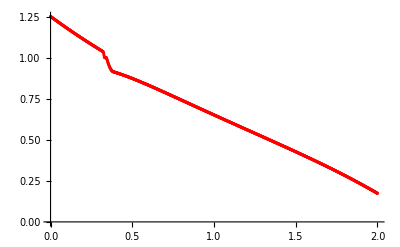

```mathematica
plotTemperaturyMPF1=ListPlot[tablicaTemperaturMPF,PlotStyle->Red]
```

```mathematica
u1[x_,t_]:=Exp[0.5*t-x];
```

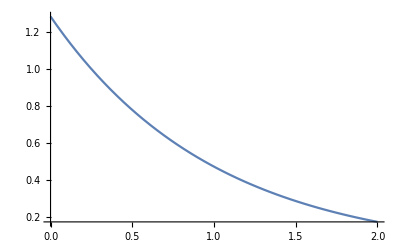

```mathematica
plotTemperaturyDokladne1=Plot[u1[x,0.5],{x,0,2}]
```

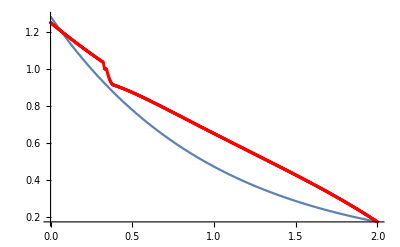

```mathematica
Show[plotTemperaturyDokladne1,plotTemperaturyMPF1]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(√Pi*(lambdaL-lambdaS))/(2*aL*√t);
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t],temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna1=Table[{i*0.002,entalpia[u1[i*0.002,0.5],0.5]},{i,0,1000}];
```

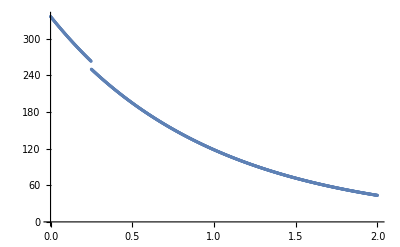

```mathematica
plotEntalpiaDokladna1=ListPlot[tablicaEntalpiaDokladna1]
```

```mathematica
strE=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE=ReadList[strE]
```

{327.822,327.442,327.062,326.682,326.303,325.924,325.546,325.169,324.791,324.415,324.038,323.662,323.287,322.912,322.538,322.163,321.79,321.417,321.044,320.672,320.3,319.929,319.558,319.187,318.817,318.447,318.078,317.71,317.341,316.973,316.606,316.239,315.873,315.506,315.141,314.776,314.411,314.046,313.683,313.319,312.956,312.593,312.231,311.869,311.508,311.147,310.787,310.427,310.067,309.708,309.349,308.991,308.633,308.275,307.918,307.561,307.205,306.849,306.494,306.139,305.784,305.43,305.076,304.723,304.37,304.017,303.665,303.313,302.962,302.611,302.261,301.911,301.561,301.212,300.863,300.514,300.166,299.819,299.472,299.125,298.778,298.432,298.087,297.741,297.397,297.052,296.708,296.364,296.021,295.678,295.336,294.994,294.652,294.311,293.97,293.63,293.289,292.95,292.61,292.271,291.933,291.595,291.257,290.92,290.583,290.246,289.91,289.574,289.239,288.904,288.569,288.235,287.901,287.567,287.234,286.901,286.569,286.237,285.905,285.574,285.243,284.913,284.583,284.253,283.924,283.595,283.266,282.938,282.61,282.283,281.956,281.629,281.303,280.977,280.651,280.326,280.002,279.677,279.353,279.029,278.706,278.383,278.061,277.739,277.417,277.096,276.775,276.454,276.134,275.814,275.495,275.176,274.858,274.539,274.222,273.904,273.588,273.271,272.955,272.64,272.325,272.011,270.367,267.853,265.343,262.998,260.778,258.561,256.346,254.308,252.385,250.463,248.544,246.833,245.206,243.58,241.954,240.594,239.262,237.93,236.646,235.609,234.572,233.535,232.641,231.9,231.158,230.415,229.932,229.486,229.039,228.686,228.537,228.388,228.237,228.085,227.932,227.778,227.623,227.466,227.309,227.151,226.992,226.831,226.67,226.508,226.345,226.18,226.015,225.849,225.682,225.514,225.345,225.176,225.005,224.833,224.661,224.488,224.314,224.139,223.963,223.787,223.61,223.432,223.253,223.073,222.893,222.712,222.53,222.347,222.164,221.98,221.795,221.609,221.423,221.236,221.049,220.861,220.672,220.482,220.292,220.102,219.91,219.718,219.526,219.333,219.139,218.944,218.75,218.554,218.358,218.161,217.964,217.767,217.568,217.37,217.17,216.971,216.77,216.569,216.368,216.166,215.964,215.762,215.558,215.355,215.151,214.946,214.741,214.536,214.33,214.124,213.917,213.71,213.503,213.295,213.087,212.878,212.669,212.459,212.25,212.04,211.829,211.618,211.407,211.195,210.984,210.771,210.559,210.346,210.133,209.919,209.706,209.491,209.277,209.062,208.847,208.632,208.416,208.201,207.984,207.768,207.551,207.335,207.117,206.9,206.682,206.464,206.246,206.028,205.809,205.59,205.371,205.152,204.933,204.713,204.493,204.273,204.053,203.832,203.611,203.39,203.169,202.948,202.726,202.505,202.283,202.061,201.839,201.617,201.394,201.171,200.949,200.726,200.503,200.279,200.056,199.832,199.609,199.385,199.161,198.937,198.713,198.488,198.264,198.039,197.815,197.59,197.365,197.14,196.915,196.69,196.464,196.239,196.013,195.788,195.562,195.336,195.11,194.884,194.658,194.432,194.206,193.98,193.753,193.527,193.301,193.074,192.847,192.621,192.394,192.167,191.94,191.713,191.486,191.259,191.032,190.805,190.578,190.35,190.123,189.896,189.668,189.441,189.214,188.986,188.759,188.531,188.303,188.076,187.848,187.62,187.393,187.165,186.937,186.709,186.482,186.254,186.026,185.798,185.57,185.342,185.115,184.887,184.659,184.431,184.203,183.975,183.747,183.519,183.291,183.063,182.835,182.607,182.379,182.151,181.923,181.695,181.467,181.24,181.012,180.784,180.556,180.328,180.1,179.872,179.644,179.416,179.188,178.961,178.733,178.505,178.277,178.049,177.822,177.594,177.366,177.139,176.911,176.683,176.456,176.228,176.,175.773,175.545,175.318,175.09,174.863,174.635,174.408,174.181,173.953,173.726,173.499,173.271,173.044,172.817,172.59,172.363,172.135,171.908,171.681,171.454,171.227,171.,170.773,170.547,170.32,170.093,169.866,169.639,169.413,169.186,168.959,168.733,168.506,168.28,168.053,167.827,167.6,167.374,167.148,166.921,166.695,166.469,166.243,166.017,165.79,165.564,165.338,165.112,164.886,164.661,164.435,164.209,163.983,163.757,163.532,163.306,163.08,162.855,162.629,162.404,162.178,161.953,161.727,161.502,161.277,161.051,160.826,160.601,160.376,160.151,159.926,159.701,159.476,159.251,159.026,158.801,158.576,158.351,158.126,157.902,157.677,157.452,157.228,157.003,156.779,156.554,156.33,156.105,155.881,155.657,155.432,155.208,154.984,154.76,154.535,154.311,154.087,153.863,153.639,153.415,153.191,152.967,152.743,152.519,152.296,152.072,151.848,151.624,151.401,151.177,150.953,150.73,150.506,150.282,150.059,149.835,149.612,149.389,149.165,148.942,148.718,148.495,148.272,148.049,147.825,147.602,147.379,147.156,146.933,146.709,146.486,146.263,146.04,145.817,145.594,145.371,145.148,144.925,144.702,144.479,144.257,144.034,143.811,143.588,143.365,143.142,142.92,142.697,142.474,142.251,142.029,141.806,141.583,141.36,141.138,140.915,140.692,140.47,140.247,140.025,139.802,139.579,139.357,139.134,138.912,138.689,138.466,138.244,138.021,137.799,137.576,137.354,137.131,136.908,136.686,136.463,136.241,136.018,135.796,135.573,135.351,135.128,134.905,134.683,134.46,134.238,134.015,133.792,133.57,133.347,133.125,132.902,132.679,132.457,132.234,132.011,131.789,131.566,131.343,131.12,130.898,130.675,130.452,130.229,130.006,129.783,129.561,129.338,129.115,128.892,128.669,128.446,128.223,128.,127.777,127.554,127.331,127.107,126.884,126.661,126.438,126.214,125.991,125.768,125.544,125.321,125.098,124.874,124.651,124.427,124.204,123.98,123.756,123.533,123.309,123.085,122.861,122.637,122.413,122.189,121.965,121.741,121.517,121.293,121.069,120.845,120.62,120.396,120.171,119.947,119.723,119.498,119.273,119.049,118.824,118.599,118.374,118.149,117.924,117.699,117.474,117.249,117.024,116.798,116.573,116.348,116.122,115.897,115.671,115.445,115.219,114.994,114.768,114.542,114.316,114.089,113.863,113.637,113.411,113.184,112.958,112.731,112.504,112.277,112.051,111.824,111.597,111.369,111.142,110.915,110.688,110.46,110.233,110.005,109.777,109.549,109.321,109.093,108.865,108.637,108.409,108.18,107.952,107.723,107.494,107.265,107.037,106.807,106.578,106.349,106.12,105.89,105.661,105.431,105.201,104.971,104.741,104.511,104.281,104.05,103.82,103.589,103.359,103.128,102.897,102.666,102.434,102.203,101.972,101.74,101.508,101.276,101.044,100.812,100.58,100.348,100.115,99.8826,99.6498,99.4169,99.1839,98.9507,98.7173,98.4839,98.2503,98.0165,97.7826,97.5486,97.3144,97.0801,96.8456,96.6109,96.3762,96.1412,95.9062,95.6709,95.4355,95.2,94.9643,94.7284,94.4924,94.2562,94.0199,93.7834,93.5468,93.3099,93.073,92.8358,92.5985,92.361,92.1234,91.8855,91.6475,91.4094,91.171,90.9325,90.6938,90.455,90.2159,89.9767,89.7373,89.4977,89.258,89.018,88.7779,88.5376,88.2971,88.0564,87.8155,87.5745,87.3332,87.0918,86.8501,86.6083,86.3663,86.124,85.8816,85.639,85.3962,85.1532,84.91,84.6665,84.4229,84.1791,83.935,83.6908,83.4463,83.2017,82.9568,82.7117,82.4664,82.2209,81.9752,81.7292,81.4831,81.2367,80.9901,80.7433,80.4962,80.249,80.0015,79.7538,79.5058,79.2576,79.0093,78.7606,78.5118,78.2627,78.0133,77.7638,77.514,77.2639,77.0137,76.7632,76.5124,76.2614,76.0102,75.7587,75.507,75.255,75.0028,74.7503,74.4976,74.2446,73.9914,73.7379,73.4841,73.2301,72.9759,72.7214,72.4666,72.2116,71.9563,71.7007,71.4449,71.1888,70.9325,70.6759,70.419,70.1618,69.9044,69.6467,69.3887,69.1304,68.8719,68.6131,68.354,68.0946,67.835,67.575,67.3148,67.0543,66.7935,66.5324,66.2711,66.0094,65.7474,65.4852,65.2227,64.9598,64.6967,64.4333,64.1695,63.9055,63.6412,63.3765,63.1116,62.8464,62.5808,62.315,62.0488,61.7823,61.5155,61.2484,60.981,60.7133,60.4452,60.1768,59.9082,59.6391,59.3698,59.1002,58.8302,58.5599,58.2893,58.0183,57.747,57.4754,57.2034,56.9311,56.6585,56.3856,56.1123,55.8386,55.5647,55.2903,55.0157,54.7407,54.4653,54.1896,53.9136,53.6372,53.3605,53.0834,52.8059,52.5281,52.25,51.9715,51.6926,51.4134,51.1338,50.8538,50.5735,50.2928,50.0118,49.7304,49.4486,49.1664,48.8839,48.601,48.3177,48.0341,47.75,47.4656,47.1808,46.8957,46.6101,46.3242,46.0379,45.7512,45.4641,45.1766,44.8887,44.6005,44.3118,44.0228,43.7333,43.4435}

```mathematica
strListE={327.8220949877,327.4416404096,327.0616529599,326.6821283765,326.3030635184,325.9244575554,325.5463096599,325.168619007,324.7913847745,324.4146061429,324.0382822954,323.662412418,323.286995699,322.9120313296,322.5375185035,322.1634564273,321.7898443125,321.416681373,321.0439668257,320.6716994357,320.2998784116,319.928502964,319.5575723091,319.1870856679,318.8170422636,318.447441322,318.0782820715,317.7095637478,317.3412855988,316.9734468743,316.6060468268,316.239084711,315.8725593158,315.5064698859,315.1408156686,314.7755959133,314.4108098714,314.0464568004,313.6825359737,313.3190466709,312.955988174,312.5933597667,312.2311607355,311.8693898999,311.508046535,311.1471299179,310.7866393277,310.4265740493,310.066933389,309.707716655,309.3489231574,308.9905522083,308.6326026697,308.2750738414,307.9179650254,307.5612755254,307.2050046589,306.8491517602,306.4937161652,306.1386972111,305.7840942356,305.429906128,305.0761322128,304.7227718159,304.3698242808,304.0172889677,303.6651652389,303.3134524582,302.962149563,302.6112558983,302.260770811,301.9106936539,301.5610238128,301.2117606754,300.8629036307,300.5144520694,300.1664049479,299.8187616344,299.471521506,299.1246839758,298.7782484585,298.4322143702,298.0865807122,297.7413468882,297.3965122884,297.0520763348,296.7080384702,296.3643981388,296.0211547857,295.6783074368,295.3358555219,294.9937984765,294.652135775,294.3108668935,293.9699913087,293.6295080817,293.2894166774,292.9497165728,292.6104072793,292.2714883095,291.9329591766,291.594818978,291.2570672145,290.9197034327,290.5827271878,290.2461380357,289.9099351266,289.5741180035,289.2386862231,288.9036394233,288.5689772125,288.2346991994,287.9008045802,287.56729295,287.2341640227,286.9014174868,286.5690530174,286.2370698809,285.9054677382,285.5742463734,285.2434056069,284.9129451998,284.582864507,284.2531632745,283.9238414165,283.5948989154,283.2663356485,282.938151086,282.6103450896,282.2829178075,281.9558694259,281.6291999847,281.3029091135,280.976996921,280.6514638949,280.3263104846,280.001536569,279.6771424086,279.3531286967,279.0294963674,278.7062462275,278.3833785158,278.0608940877,277.7387946151,277.4170817667,277.0957564635,276.7748199415,276.4542750446,276.1341247795,275.814371522,275.4950176245,275.1760678655,274.8575280821,274.5394036952,274.221699441,273.9044253154,273.5875951319,273.2712222923,272.9553188282,272.6399494265,272.325222093,272.0112443368,270.3667886084,267.8531313397,265.342604478,262.9976160996,260.7781629547,258.561156909,256.346470593,254.3076176295,252.3846372304,250.4633519465,248.5436563653,246.8331168004,245.205858648,243.5796290153,241.9543442526,240.5938578709,239.261832974,237.9302523563,236.6461795568,235.6091813823,234.5721665814,233.5350935479,232.6412322551,231.899716182,231.1577413087,230.4152859266,229.9315639197,229.485734242,229.0390814151,228.6858988299,228.5373358737,228.3876423936,228.2368314585,228.0849160082,227.9319088542,227.7778226809,227.6226700472,227.4664633874,227.3092150125,227.150937111,226.9916417506,226.8313408792,226.6700463256,226.5077698013,226.3445229011,226.1803171042,226.0151637758,225.8490741677,225.6820594194,225.5141305593,225.3452985059,225.1755740684,225.0049679482,224.8334907397,224.6611529312,224.487964906,224.3139369437,224.1390792204,223.9634018107,223.7869146878,223.6096277249,223.431550696,223.2526932768,223.073065046,222.8926754854,222.7115339819,222.5296498274,222.3470322202,222.163690266,221.9796329783,221.7948692799,221.609408003,221.4232578907,221.2364275976,221.0489256905,220.8607606495,220.6719408686,220.4824746567,220.2923702381,220.1016357536,219.9102792612,219.7183087368,219.5257320752,219.3325570904,219.138791517,218.9444430102,218.7495191474,218.5540274282,218.3579752754,218.161370036,217.9642189814,217.7665293085,217.5683081402,217.3695625263,217.1702994438,216.9705257982,216.7702484235,216.5694740834,216.3682094716,216.1664612127,215.9642358627,215.7615399098,215.5583797747,215.3547618119,215.1506923095,214.9461774904,214.7412235126,214.5358364703,214.3300223937,214.1237872504,213.9171369453,213.7100773219,213.5026141622,213.2947531877,213.0865000599,212.8778603807,212.668839693,212.4594434817,212.2496771734,212.0395461377,211.8290556874,211.618211079,211.4070175135,211.1954801364,210.9836040389,210.7713942578,210.5588557766,210.3459935252,210.1328123813,209.9193171702,209.7055126657,209.4914035903,209.276994616,209.0622903644,208.8472954075,208.6320142679,208.4164514195,208.2006112877,207.9844982503,207.7681166372,207.5514707317,207.3345647702,207.1174029431,206.8999893953,206.6823282259,206.4644234898,206.2462791968,206.0278993132,205.8092877614,205.5904484207,205.3713851275,205.152101676,204.9326018181,204.7128892644,204.492967684,204.2728407053,204.0525119162,203.8319848645,203.6112630584,203.3903499665,203.1692490187,202.9479636061,202.7264970816,202.5048527603,202.2830339196,202.0610437997,201.8388856041,201.6165624996,201.3940776171,201.1714340513,200.9486348617,200.7256830724,200.5025816729,200.2793336179,200.0559418282,199.8324091904,199.6087385577,199.3849327501,199.1609945545,198.9369267252,198.7127319842,198.4884130214,198.2639724949,198.0394130315,197.8147372267,197.5899476452,197.3650468209,197.1400372578,196.9149214294,196.6897017798,196.4643807235,196.2389606456,196.0134439027,195.7878328223,195.5621297037,195.336336818,195.1104564084,194.8844906906,194.6584418527,194.4323120558,194.2061034342,193.9798180954,193.7534581206,193.5270255648,193.3005224573,193.0739508015,192.8473125755,192.6206097321,192.3938441992,192.1670178799,191.9401326529,191.7131903726,191.4861928692,191.2591419492,191.0320393954,190.8048869671,190.5776864006,190.3504394091,190.123147683,189.8958128902,189.6684366762,189.4410206642,189.2135664558,188.9860756304,188.7585497462,188.5309903398,188.3033989268,188.0757770016,187.848126038,187.6204474892,187.3927427878,187.1650133464,186.9372605574,186.7094857933,186.4816904071,186.2538757322,186.0260430825,185.798193753,185.5703290195,185.3424501392,185.1145583505,184.8866548733,184.6587409093,184.4308176419,184.2028862368,183.9749478416,183.7470035862,183.5190545833,183.291101928,183.0631466982,182.835189955,182.6072327423,182.3792760876,182.1513210014,181.9233684781,181.6954194957,181.467475016,181.239535985,181.0116033324,180.7836779727,180.5557608045,180.327852711,180.0999545601,179.8720672047,179.6441914823,179.4163282159,179.1884782135,178.9606422684,178.7328211596,178.5050156516,178.2772264946,178.0494544246,177.8217001639,177.5939644207,177.3662478893,177.1385512506,176.9108751718,176.6832203069,176.4555872964,176.2279767678,176.0003893353,175.7728256005,175.5452861519,175.3177715653,175.0902824041,174.8628192188,174.635382548,174.4079729177,174.1805908418,173.9532368221,173.7259113484,173.4986148989,173.2713479395,173.0441109251,172.8169042985,172.5897284912,172.3625839236,172.1354710044,171.9083901314,171.6813416912,171.4543260597,171.2273436014,171.0003946705,170.7734796103,170.5465987534,170.3197524219,170.0929409277,169.8661645721,169.6394236462,169.412718431,169.1860491974,168.9594162062,168.7328197084,168.5062599451,168.2797371478,168.053251538,167.826803328,167.6003927203,167.3740199082,167.1476850753,166.9213883965,166.6951300368,166.4689101528,166.2427288914,166.016586391,165.790482781,165.5644181817,165.338392705,165.112406454,164.8864595232,164.6605519985,164.4346839574,164.208855469,163.983066594,163.757317385,163.5316078862,163.3059381338,163.080308156,162.8547179728,162.6291675965,162.4036570313,162.1781862737,161.9527553126,161.7273641291,161.5020126965,161.2767009809,161.0514289405,160.8261965265,160.6010036824,160.3758503444,160.1507364416,159.9256618959,159.7006266217,159.4756305268,159.2506735116,159.0257554697,158.8008762877,158.5760358454,158.3512340156,158.1264706645,157.9017456515,157.6770588295,157.4524100446,157.2277991364,157.003225938,156.7786902759,156.5541919705,156.3297308356,156.1053066787,155.8809193012,155.6565684979,155.432254058,155.207975764,154.9837333927,154.7595267147,154.5353554947,154.3112194913,154.0871184575,153.8630521402,153.6390202804,153.4150226137,153.1910588695,152.9671287719,152.7432320393,152.5193683843,152.295537514,152.0717391302,151.8479729289,151.6242386009,151.4005358315,151.1768643006,150.9532236829,150.7296136477,150.5060338591,150.282483976,150.0589636521,149.8354725358,149.6120102708,149.3885764954,149.165170843,148.9417929419,148.7184424156,148.4951188826,148.2718219564,148.0485512458,147.8253063547,147.6020868822,147.3788924227,147.1557225659,146.9325768967,146.7094549953,146.4863564375,146.2632807942,146.0402276321,145.8171965129,145.5941869942,145.371198629,145.1482309657,144.9252835484,144.7023559169,144.4794476065,144.2565581483,144.0336870688,143.8108338907,143.587998132,143.3651793067,143.1423769246,142.9195904913,142.6968195082,142.4740634728,142.2513218782,142.0285942138,141.8058799645,141.5831786116,141.3604896323,141.1378124997,140.9151466831,140.6924916479,140.4698468555,140.2472117634,140.0245858256,139.8019684918,139.5793592082,139.3567574171,139.1341625573,138.9115740635,138.688991367,138.4664138952,138.243841072,138.0212723175,137.7987070483,137.5761446774,137.3535846141,137.1310262643,136.9084690303,136.6859123109,136.4633555013,136.2407979934,136.0182391754,135.7956784323,135.5731151456,135.3505486934,135.1279784502,134.9054037876,134.6828240735,134.4602386725,134.2376469461,134.0150482522,133.7924419457,133.5698273782,133.3472038978,133.1245708498,132.9019275759,132.6792734149,132.4566077023,132.2339297705,132.0112389486,131.7885345628,131.5658159361,131.3430823885,131.1203332366,130.8975677943,130.6747853724,130.4519852785,130.2291668173,130.0063292906,129.783471997,129.5605942322,129.3376952891,129.1147744575,128.8918310243,128.6688642734,128.4458734861,128.2228579405,127.999816912,127.776749673,127.5536554932,127.3305336395,127.1073833757,126.8842039631,126.6609946601,126.4377547222,126.2144834024,125.9911799507,125.7678436144,125.5444736383,125.321069264,125.0976297309,124.8741542754,124.6506421314,124.4270925299,124.2035046994,123.9798778657,123.7562112521,123.532504079,123.3087555644,123.0849649237,122.8611313695,122.6372541119,122.4133323587,122.1893653147,121.9653521824,121.7412921617,121.5171844501,121.2930282422,121.0688227306,120.8445671049,120.6202605526,120.3959022585,120.1714914049,119.9470271718,119.7225087367,119.4979352744,119.2733059576,119.0486199565,118.8238764387,118.5990745695,118.3742135118,118.1492924262,117.9243104707,117.6992668011,117.4741605708,117.2489909307,117.0237570296,116.7984580137,116.5730930269,116.347661211,116.1221617053,115.8965936468,115.6709561702,115.4452484078,115.2194694899,114.9936185442,114.7676946963,114.5416970695,114.3156247849,114.0894769612,113.8632527149,113.6369511603,113.4105714096,113.1841125725,112.9575737566,112.7309540674,112.5042526081,112.2774684796,112.0506007808,111.8236486083,111.5966110566,111.3694872179,111.1422761824,110.9149770379,110.6875888704,110.4601107634,110.2325417985,110.004881055,109.7771276102,109.5492805392,109.321338915,109.0933018085,108.8651682885,108.6369374218,108.4086082728,108.1801799042,107.9516513762,107.7230217474,107.4942900739,107.26545541,107.0365168078,106.8074733174,106.5783239869,106.3490678622,106.1197039874,105.8902314043,105.6606491528,105.4309562708,105.2011517942,104.9712347567,104.7412041903,104.5110591247,104.2807985878,104.0504216053,103.8199272011,103.589314397,103.358582213,103.1277296669,102.8967557746,102.66565955,102.4344400052,102.2030961501,101.9716269929,101.7400315397,101.5083087946,101.2764577598,101.0444774358,100.8123668207,100.5801249111,100.3477507015,100.1152431845,99.8826013507,99.6498241889,99.4169106859,99.1838598267,98.9506705944,98.7173419702,98.4838729331,98.2502624607,98.0165095285,97.78261311,97.5485721769,97.3143856992,97.0800526448,96.8455719798,96.6109426686,96.3761636734,96.1412339549,95.9061524717,95.6709181808,95.435530037,95.1999869937,94.964288002,94.7284320116,94.49241797,94.2562448232,94.0199115151,93.7834169879,93.5467601821,93.3099400362,93.0729554869,92.8358054693,92.5984889165,92.3610047598,92.1233519287,91.8855293512,91.6475359531,91.4093706587,91.1710323903,90.9325200686,90.6938326125,90.4549689389,90.2159279634,89.9767085993,89.7373097585,89.497730351,89.257969285,89.0180254672,88.7778978021,88.5375851929,88.2970865409,88.0564007454,87.8155267044,87.5744633139,87.3332094681,87.0917640598,86.8501259797,86.6082941169,86.366267359,86.1240445915,85.8816246985,85.6390065623,85.3961890633,85.1531710806,84.9099514911,84.6665291704,84.4229029922,84.1790718286,83.9350345499,83.6907900249,83.4463371204,83.2016747019,82.956801633,82.7117167755,82.4664189899,82.2209071346,81.9751800667,81.7292366413,81.4830757122,81.2366961312,80.9900967486,80.7432764132,80.4962339718,80.2489682698,80.0014781509,79.7537624571,79.5058200288,79.2576497049,79.0092503224,78.7606207169,78.5117597221,78.2626661704,78.0133388924,77.7637767171,77.5139784719,77.2639429824,77.013669073,76.7631555661,76.5124012826,76.261405042,76.0101656619,75.7586819585,75.5069527463,75.2549768383,75.0027530458,74.7502801787,74.497557045,74.2445824514,73.9913552029,73.7378741031,73.4841379537,73.230145555,72.9758957059,72.7213872035,72.4666188434,72.2115894197,71.9562977249,71.70074255,71.4449226843,71.1888369157,70.9324840305,70.6758628136,70.4189720481,70.1618105157,69.9043769966,69.6466702695,69.3886891115,69.1304322981,68.8718986035,68.6130868001,68.3539956591,68.09462395,67.8349704407,67.5750338979,67.3148130865,67.05430677,66.7935137106,66.5324326686,66.2710624031,66.0094016717,65.7474492306,65.4852038341,65.2226642355,64.9598291865,64.6966974371,64.4332677361,64.1695388307,63.9055094667,63.6411783884,63.3765443387,63.111606059,62.8463622892,62.5808117678,62.3149532321,62.0487854175,61.7823070582,61.5155168872,61.2484136356,60.9809960334,60.7132628091,60.4452126898,60.1768444012,59.9081566674,59.6391482114,59.3698177545,59.1001640168,58.830185717,58.5598815722,58.2892502983,58.0182906099,57.7470012199,57.4753808401,57.2034281807,56.9311419508,56.658520858,56.3855636083,56.1122689067,55.8386354567,55.5646619604,55.2903471186,55.0156896307,54.7406881948,54.4653415077,54.1896482648,53.9136071602,53.6372168866,53.3604761354,53.0833835968,52.8059379596,52.5281379112,52.2499821378,51.9714693242,51.6925981541,51.4133673097,51.1337754719,50.8538213204,50.5735035336,50.2928207887,50.0117717615,49.7303551264,49.4485695569,49.166413725,48.8838863013,48.6009859555,48.3177113557,48.034061169,47.7500340611,47.4656286965,47.1808437386,46.8956778494,46.6101296897,46.3241979192,46.0378811961,45.7511781777,45.46408752,45.1766078777,44.8887379043,44.6004762522,44.3118215726,44.0227725155,43.7333277296,43.4434858626};
```

```mathematica
tablicaEntalpiaMPF1=Table[{i*0.002,strListE[[i+1]]},{i,0,1000}];
```

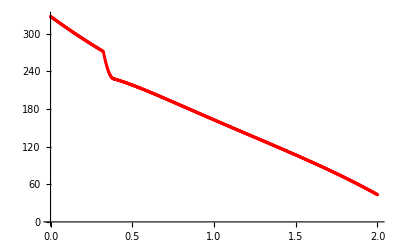

```mathematica
plotEntalpiaMPF1=ListPlot[tablicaEntalpiaMPF1,PlotStyle->Red]
```

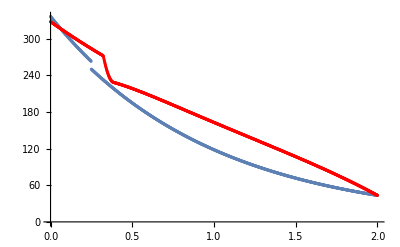

```mathematica
Show[plotEntalpiaDokladna1,plotEntalpiaMPF1]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv

### alfa = 1/2, t=1

#### temperatury

```mathematica
str2=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList2=ReadList[str2]
```

{1.63271,1.63018,1.62765,1.62513,1.62261,1.6201,1.61759,1.61509,1.61259,1.6101,1.60761,1.60513,1.60265,1.60018,1.59771,1.59525,1.59279,1.59033,1.58788,1.58543,1.58299,1.58056,1.57813,1.5757,1.57328,1.57086,1.56844,1.56603,1.56363,1.56123,1.55883,1.55644,1.55406,1.55168,1.5493,1.54693,1.54456,1.54219,1.53983,1.53748,1.53513,1.53278,1.53044,1.5281,1.52577,1.52344,1.52111,1.51879,1.51648,1.51417,1.51186,1.50955,1.50726,1.50496,1.50267,1.50038,1.4981,1.49583,1.49355,1.49128,1.48902,1.48676,1.4845,1.48225,1.48,1.47776,1.47552,1.47328,1.47105,1.46882,1.4666,1.46438,1.46216,1.45995,1.45774,1.45554,1.45334,1.45115,1.44895,1.44677,1.44458,1.4424,1.44023,1.43806,1.43589,1.43373,1.43157,1.42941,1.42726,1.42511,1.42297,1.42083,1.41869,1.41656,1.41443,1.41231,1.41019,1.40807,1.40596,1.40385,1.40174,1.39964,1.39754,1.39545,1.39336,1.39127,1.38919,1.38711,1.38504,1.38297,1.3809,1.37883,1.37677,1.37472,1.37266,1.37061,1.36857,1.36653,1.36449,1.36245,1.36042,1.35839,1.35637,1.35435,1.35233,1.35032,1.34831,1.3463,1.3443,1.3423,1.34031,1.33831,1.33633,1.33434,1.33236,1.33038,1.32841,1.32644,1.32447,1.32251,1.32054,1.31859,1.31663,1.31468,1.31274,1.31079,1.30885,1.30692,1.30498,1.30305,1.30113,1.2992,1.29728,1.29537,1.29345,1.29154,1.28964,1.28773,1.28583,1.28394,1.28204,1.28015,1.27827,1.27638,1.2745,1.27262,1.27075,1.26888,1.26701,1.26515,1.26329,1.26143,1.25957,1.25772,1.25587,1.25403,1.25219,1.25035,1.24851,1.24668,1.24485,1.24302,1.2412,1.23938,1.23756,1.23575,1.23394,1.23213,1.23032,1.22852,1.22672,1.22493,1.22314,1.22135,1.21956,1.21778,1.216,1.21422,1.21244,1.21067,1.2089,1.20714,1.20537,1.20361,1.20186,1.2001,1.19835,1.1966,1.19486,1.19312,1.19138,1.18964,1.18791,1.18617,1.18445,1.18272,1.181,1.17928,1.17756,1.17585,1.17414,1.17243,1.17073,1.16902,1.16732,1.16563,1.16393,1.16224,1.16055,1.15887,1.15718,1.1555,1.15382,1.15215,1.15048,1.14881,1.14714,1.14548,1.14382,1.14216,1.1405,1.13885,1.1372,1.13555,1.1339,1.13226,1.13062,1.12898,1.12735,1.12572,1.12409,1.12246,1.12084,1.11921,1.1176,1.11598,1.11437,1.11275,1.11115,1.10954,1.10794,1.10633,1.10474,1.10314,1.10155,1.09996,1.09837,1.09678,1.0952,1.09362,1.09204,1.09046,1.08889,1.08732,1.08575,1.08418,1.08262,1.08106,1.0795,1.07794,1.07639,1.07484,1.07329,1.07174,1.0702,1.06866,1.06712,1.06558,1.06405,1.06252,1.06099,1.05946,1.05793,1.05641,1.05489,1.05337,1.05186,1.05035,1.04884,1.04733,1.04582,1.04432,1.04282,1.04132,1.03983,1.03833,1.03684,1.03535,1.03387,1.03239,1.0237,1.01022,1,1,1,0.998162,0.987234,0.977656,0.968088,0.959458,0.951369,0.943577,0.936968,0.930362,0.924894,0.919765,0.915159,0.911506,0.907852,0.9056,0.903421,0.902048,0.901345,0.900636,0.899922,0.899203,0.898479,0.89775,0.897015,0.896276,0.895532,0.894783,0.894029,0.893271,0.892508,0.89174,0.890968,0.890192,0.889411,0.888625,0.887836,0.887042,0.886244,0.885441,0.884635,0.883825,0.88301,0.882192,0.88137,0.880544,0.879714,0.87888,0.878043,0.877202,0.876358,0.87551,0.874658,0.873803,0.872945,0.872083,0.871218,0.87035,0.869478,0.868603,0.867725,0.866844,0.86596,0.865073,0.864183,0.86329,0.862394,0.861495,0.860593,0.859689,0.858782,0.857872,0.856959,0.856044,0.855126,0.854206,0.853283,0.852358,0.85143,0.850499,0.849567,0.848632,0.847695,0.846755,0.845813,0.844869,0.843923,0.842974,0.842024,0.841071,0.840116,0.83916,0.838201,0.83724,0.836278,0.835313,0.834347,0.833378,0.832408,0.831436,0.830462,0.829487,0.82851,0.827531,0.82655,0.825568,0.824584,0.823599,0.822612,0.821624,0.820634,0.819642,0.818649,0.817655,0.816659,0.815662,0.814663,0.813664,0.812662,0.81166,0.810656,0.809651,0.808645,0.807637,0.806628,0.805619,0.804608,0.803595,0.802582,0.801568,0.800552,0.799536,0.798518,0.7975,0.79648,0.79546,0.794438,0.793416,0.792393,0.791368,0.790343,0.789317,0.788291,0.787263,0.786234,0.785205,0.784175,0.783144,0.782113,0.78108,0.780047,0.779013,0.777979,0.776944,0.775908,0.774872,0.773834,0.772797,0.771758,0.77072,0.76968,0.76864,0.767599,0.766558,0.765517,0.764475,0.763432,0.762389,0.761345,0.760301,0.759257,0.758212,0.757166,0.75612,0.755074,0.754028,0.752981,0.751933,0.750886,0.749838,0.748789,0.747741,0.746692,0.745642,0.744593,0.743543,0.742493,0.741442,0.740391,0.739341,0.738289,0.737238,0.736186,0.735135,0.734083,0.73303,0.731978,0.730925,0.729873,0.72882,0.727767,0.726714,0.72566,0.724607,0.723553,0.7225,0.721446,0.720392,0.719338,0.718284,0.71723,0.716176,0.715122,0.714067,0.713013,0.711959,0.710904,0.70985,0.708795,0.707741,0.706686,0.705632,0.704577,0.703523,0.702468,0.701414,0.70036,0.699305,0.698251,0.697197,0.696142,0.695088,0.694034,0.69298,0.691926,0.690872,0.689818,0.688764,0.68771,0.686657,0.685603,0.68455,0.683496,0.682443,0.68139,0.680337,0.679284,0.678231,0.677179,0.676126,0.675074,0.674021,0.672969,0.671917,0.670866,0.669814,0.668762,0.667711,0.66666,0.665609,0.664558,0.663507,0.662456,0.661406,0.660356,0.659306,0.658256,0.657206,0.656157,0.655107,0.654058,0.653009,0.651961,0.650912,0.649864,0.648815,0.647768,0.64672,0.645672,0.644625,0.643578,0.642531,0.641484,0.640438,0.639391,0.638345,0.637299,0.636254,0.635208,0.634163,0.633118,0.632074,0.631029,0.629985,0.628941,0.627897,0.626853,0.62581,0.624767,0.623724,0.622681,0.621639,0.620596,0.619554,0.618513,0.617471,0.61643,0.615389,0.614348,0.613308,0.612267,0.611227,0.610187,0.609148,0.608108,0.607069,0.60603,0.604992,0.603953,0.602915,0.601877,0.600839,0.599802,0.598765,0.597728,0.596691,0.595654,0.594618,0.593582,0.592546,0.591511,0.590476,0.58944,0.588406,0.587371,0.586337,0.585302,0.584269,0.583235,0.582201,0.581168,0.580135,0.579103,0.57807,0.577038,0.576006,0.574974,0.573942,0.572911,0.57188,0.570849,0.569818,0.568788,0.567757,0.566727,0.565697,0.564668,0.563638,0.562609,0.56158,0.560552,0.559523,0.558495,0.557467,0.556439,0.555411,0.554384,0.553356,0.552329,0.551302,0.550276,0.549249,0.548223,0.547197,0.546171,0.545145,0.54412,0.543094,0.542069,0.541044,0.540019,0.538995,0.53797,0.536946,0.535922,0.534898,0.533875,0.532851,0.531828,0.530805,0.529782,0.528759,0.527736,0.526714,0.525691,0.524669,0.523647,0.522625,0.521603,0.520582,0.51956,0.518539,0.517518,0.516497,0.515476,0.514455,0.513435,0.512414,0.511394,0.510374,0.509354,0.508334,0.507314,0.506294,0.505275,0.504255,0.503236,0.502217,0.501198,0.500179,0.49916,0.498141,0.497122,0.496104,0.495085,0.494067,0.493049,0.492031,0.491012,0.489994,0.488976,0.487959,0.486941,0.485923,0.484905,0.483888,0.48287,0.481853,0.480836,0.479818,0.478801,0.477784,0.476767,0.47575,0.474733,0.473716,0.472699,0.471682,0.470665,0.469648,0.468631,0.467615,0.466598,0.465581,0.464565,0.463548,0.462531,0.461515,0.460498,0.459482,0.458465,0.457448,0.456432,0.455415,0.454399,0.453382,0.452366,0.451349,0.450332,0.449316,0.448299,0.447282,0.446266,0.445249,0.444232,0.443215,0.442199,0.441182,0.440165,0.439148,0.438131,0.437114,0.436097,0.43508,0.434062,0.433045,0.432028,0.43101,0.429993,0.428975,0.427958,0.42694,0.425922,0.424904,0.423886,0.422868,0.42185,0.420832,0.419814,0.418795,0.417777,0.416758,0.415739,0.414721,0.413702,0.412682,0.411663,0.410644,0.409624,0.408605,0.407585,0.406565,0.405545,0.404525,0.403505,0.402484,0.401464,0.400443,0.399422,0.398401,0.39738,0.396358,0.395337,0.394315,0.393293,0.392271,0.391249,0.390226,0.389203,0.388181,0.387158,0.386134,0.385111,0.384087,0.383063,0.382039,0.381015,0.37999,0.378966,0.377941,0.376916,0.37589,0.374865,0.373839,0.372813,0.371786,0.37076,0.369733,0.368706,0.367678,0.366651,0.365623,0.364595,0.363566,0.362538,0.361509,0.36048,0.35945,0.35842,0.35739,0.35636,0.355329,0.354298,0.353267,0.352236,0.351204,0.350172,0.349139,0.348107,0.347074,0.34604,0.345006,0.343972,0.342938,0.341903,0.340868,0.339833,0.338797,0.337761,0.336725,0.335688,0.334651,0.333613,0.332575,0.331537,0.330499,0.32946,0.32842,0.327381,0.326341,0.3253,0.324259,0.323218,0.322176,0.321134,0.320092,0.319049,0.318006,0.316962,0.315918,0.314874,0.313829,0.312783,0.311738,0.310691,0.309645,0.308598,0.30755,0.306502,0.305454,0.304405,0.303356,0.302306,0.301256,0.300205,0.299154,0.298102,0.29705,0.295998,0.294945,0.293891,0.292837,0.291783,0.290728,0.289672,0.288616,0.28756,0.286503,0.285445,0.284387,0.283329,0.28227,0.28121,0.28015,0.27909,0.278029,0.276967,0.275905,0.274842,0.273779,0.272715,0.27165,0.270586,0.26952,0.268454,0.267387,0.26632,0.265252,0.264184,0.263115,0.262046,0.260976,0.259905,0.258834,0.257762,0.25669,0.255616,0.254543,0.253469,0.252394,0.251318,0.250242,0.249165,0.248088,0.24701,0.245932,0.244852,0.243773,0.242692,0.241611,0.240529,0.239447,0.238364,0.23728,0.236196,0.23511,0.234025,0.232938,0.231851,0.230764,0.229675,0.228586,0.227496,0.226406,0.225315,0.224223,0.22313}

```mathematica
strList2={1.6327069115,1.6301759605,1.6276498596,1.6251285877,1.6226121261,1.6201004632,1.6175935873,1.6150914869,1.6125941504,1.6101015663,1.607613723,1.6051306091,1.6026522131,1.6001785237,1.5977095295,1.595245219,1.5927855811,1.5903306044,1.5878802777,1.5854345879,1.5829935239,1.5805570745,1.5781252285,1.5756979747,1.5732753022,1.5708571999,1.5684436568,1.5660346619,1.5636302043,1.561230273,1.5588348572,1.556443946,1.5540575268,1.5516755888,1.549298121,1.5469251128,1.5445565533,1.5421924319,1.5398327379,1.5374774606,1.5351265896,1.5327801143,1.530438024,1.5281003066,1.5257669514,1.523437948,1.5211132859,1.5187929546,1.5164769437,1.5141652429,1.5118578419,1.5095547304,1.5072558963,1.5049613295,1.5026710197,1.5003849566,1.4981031301,1.4958255299,1.493552146,1.4912829682,1.4890179865,1.4867571892,1.4845005663,1.4822481077,1.4799998035,1.4777556437,1.4755156184,1.4732797177,1.4710479301,1.4688202458,1.4665966549,1.4643771477,1.4621617143,1.459950345,1.4577430302,1.4555397602,1.4533405235,1.4511453107,1.4489541121,1.446766918,1.4445837191,1.4424045056,1.4402292666,1.4380579924,1.4358906736,1.4337273009,1.4315678647,1.4294123558,1.4272607646,1.4251130804,1.4229692937,1.4208293953,1.4186933759,1.4165612263,1.4144329372,1.412308498,1.4101878992,1.4080711319,1.405958187,1.4038490552,1.4017437276,1.3996421935,1.3975444438,1.3954504696,1.3933602619,1.3912738116,1.3891911084,1.3871121433,1.3850369074,1.3829653917,1.3808975875,1.378833486,1.3767730768,1.3747163511,1.3726633001,1.3706139151,1.3685681874,1.3665261067,1.3644876645,1.3624528519,1.3604216604,1.3583940815,1.356370105,1.3543497222,1.3523329248,1.350319704,1.3483100516,1.3463039575,1.3443014131,1.3423024102,1.3403069401,1.3383149947,1.336326564,1.3343416397,1.3323602133,1.3303822767,1.32840782,1.326436835,1.3244693135,1.3225052471,1.3205446277,1.3185874457,1.3166336928,1.314683361,1.3127364421,1.3107929265,1.3088528062,1.306916073,1.3049827191,1.3030527348,1.3011261121,1.2992028431,1.2972829199,1.295366333,1.2934530746,1.2915431366,1.2896365113,1.2877331893,1.2858331628,1.2839364239,1.282042965,1.2801527767,1.2782658513,1.276382181,1.2745017581,1.2726245736,1.2707506196,1.2688798886,1.2670123729,1.2651480635,1.2632869527,1.2614290329,1.2595742967,1.257722735,1.2558743403,1.254029105,1.2521870204,1.2503480789,1.248512273,1.2466795954,1.2448500372,1.243023591,1.2412002494,1.2393800052,1.2375628495,1.235748775,1.2339377744,1.2321298391,1.2303249618,1.2285231352,1.2267243522,1.2249286041,1.2231358837,1.2213461839,1.2195594962,1.2177758133,1.2159951282,1.2142174325,1.212442719,1.2106709806,1.2089022105,1.2071364001,1.2053735424,1.2036136306,1.2018566561,1.2001026122,1.1983514919,1.1966032868,1.1948579902,1.1931155951,1.1913760934,1.1896394781,1.1879057425,1.1861748785,1.1844468793,1.182721738,1.1809994481,1.1792800015,1.1775633913,1.175849611,1.1741386526,1.1724305093,1.1707251747,1.1690226407,1.1673229007,1.1656259483,1.1639317755,1.1622403758,1.1605517428,1.1588658685,1.1571827466,1.1555023706,1.1538247328,1.1521498267,1.1504776461,1.1488081832,1.1471414316,1.1454773838,1.1438160334,1.1421573743,1.1405013988,1.1388481007,1.1371974739,1.1355495109,1.1339042054,1.1322615515,1.1306215416,1.1289841698,1.12734943,1.1257173149,1.1240878185,1.1224609348,1.1208366567,1.1192149782,1.1175958921,1.1159793926,1.1143654739,1.1127541291,1.1111453522,1.1095391377,1.1079354786,1.1063343693,1.1047358043,1.1031397766,1.1015462808,1.0999553103,1.0983668595,1.0967809232,1.0951974949,1.0936165692,1.0920381411,1.0904622042,1.0888887534,1.0873177825,1.0857492868,1.0841832612,1.0826197001,1.0810585987,1.0794999526,1.0779437562,1.076390005,1.074838694,1.0732898191,1.0717433764,1.0701993615,1.0686577704,1.067118599,1.0655818446,1.0640475041,1.0625155745,1.0609860534,1.0594589397,1.0579342312,1.0564119268,1.0548920262,1.0533745298,1.0518594398,1.0503467586,1.0488364886,1.0473286365,1.0458232091,1.0443202177,1.0428196766,1.0413215989,1.0398260149,1.0383329537,1.0368424691,1.0353546358,1.0338695555,1.0323878213,1.02369734,1.0102187075,1,1,1,0.9981617209,0.9872335794,0.977655569,0.9680881729,0.9594575138,0.9513691263,0.9435772242,0.936967505,0.9303620564,0.9248943646,0.9197648808,0.9151588919,0.9115057927,0.9078516894,0.9056002371,0.9034209084,0.9020484007,0.9013450219,0.9006363305,0.8999223909,0.8992032669,0.8984790215,0.8977497171,0.8970154156,0.8962761782,0.8955320653,0.894783137,0.8940294524,0.8932710704,0.8925080491,0.8917404459,0.8909683178,0.8901917211,0.8894107116,0.8886253444,0.8878356743,0.8870417552,0.8862436406,0.8854413835,0.8846350363,0.8838246509,0.8830102785,0.8821919701,0.8813697758,0.8805437454,0.8797139282,0.8788803728,0.8780431275,0.8772022401,0.8763577577,0.875509727,0.8746581944,0.8738032056,0.8729448058,0.8720830399,0.8712179522,0.8703495867,0.8694779867,0.8686031951,0.8677252547,0.8668442073,0.8659600946,0.8650729579,0.8641828378,0.8632897748,0.8623938086,0.8614949789,0.8605933247,0.8596888845,0.8587816968,0.8578717992,0.8569592293,0.8560440241,0.8551262202,0.854205854,0.8532829612,0.8523575773,0.8514297376,0.8504994766,0.8495668289,0.8486318282,0.8476945084,0.8467549027,0.845813044,0.8448689648,0.8439226974,0.8429742736,0.8420237249,0.8410710826,0.8401163774,0.8391596399,0.8382009002,0.8372401883,0.8362775335,0.8353129652,0.8343465122,0.833378203,0.832408066,0.8314361291,0.8304624199,0.8294869657,0.8285097936,0.8275309304,0.8265504025,0.825568236,0.8245844568,0.8235990905,0.8226121623,0.8216236973,0.8206337203,0.8196422557,0.8186493276,0.81765496,0.8166591766,0.8156620007,0.8146634555,0.8136635637,0.8126623481,0.811659831,0.8106560345,0.8096509803,0.8086446902,0.8076371855,0.8066284873,0.8056186165,0.8046075936,0.8035954392,0.8025821733,0.8015678159,0.8005523867,0.7995359053,0.7985183907,0.7974998622,0.7964803384,0.795459838,0.7944383793,0.7934159805,0.7923926596,0.7913684343,0.7903433222,0.7893173405,0.7882905064,0.7872628367,0.7862343483,0.7852050577,0.7841749811,0.7831441347,0.7821125345,0.7810801961,0.7800471352,0.7790133672,0.7779789071,0.77694377,0.7759079708,0.774871524,0.7738344443,0.7727967457,0.7717584425,0.7707195485,0.7696800777,0.7686400435,0.7675994594,0.7665583386,0.7655166943,0.7644745394,0.7634318867,0.7623887487,0.7613451381,0.7603010669,0.7592565475,0.7582115917,0.7571662115,0.7561204185,0.7550742243,0.7540276402,0.7529806775,0.7519333473,0.7508856605,0.749837628,0.7487892604,0.7477405683,0.7466915621,0.745642252,0.7445926481,0.7435427605,0.7424925989,0.7414421731,0.7403914928,0.7393405673,0.738289406,0.7372380181,0.7361864127,0.7351345988,0.7340825851,0.7330303805,0.7319779934,0.7309254324,0.7298727059,0.728819822,0.7277667889,0.7267136146,0.725660307,0.7246068738,0.7235533228,0.7224996615,0.7214458974,0.7203920378,0.7193380899,0.7182840608,0.7172299577,0.7161757873,0.7151215566,0.7140672722,0.7130129407,0.7119585687,0.7109041626,0.7098497287,0.7087952731,0.7077408021,0.7066863217,0.7056318377,0.7045773561,0.7035228825,0.7024684227,0.7014139821,0.7003595663,0.6993051806,0.6982508304,0.6971965208,0.696142257,0.695088044,0.6940338867,0.6929797901,0.6919257589,0.6908717977,0.6898179114,0.6887641042,0.6877103808,0.6866567456,0.6856032027,0.6845497565,0.683496411,0.6824431704,0.6813900387,0.6803370197,0.6792841174,0.6782313354,0.6771786776,0.6761261474,0.6750737486,0.6740214845,0.6729693586,0.6719173743,0.6708655348,0.6698138433,0.668762303,0.667710917,0.6666596883,0.6656086198,0.6645577144,0.6635069749,0.6624564042,0.6614060048,0.6603557795,0.6593057308,0.6582558611,0.6572061731,0.656156669,0.6551073512,0.6540582219,0.6530092835,0.651960538,0.6509119875,0.6498636341,0.6488154799,0.6477675266,0.6467197763,0.6456722306,0.6446248915,0.6435777607,0.6425308397,0.6414841302,0.6404376339,0.6393913521,0.6383452865,0.6372994383,0.6362538089,0.6352083997,0.634163212,0.6331182469,0.6320735057,0.6310289894,0.6299846992,0.6289406361,0.627896801,0.6268531949,0.6258098188,0.6247666734,0.6237237596,0.6226810781,0.6216386297,0.6205964151,0.6195544349,0.6185126896,0.6174711799,0.6164299063,0.6153888692,0.6143480691,0.6133075064,0.6122671814,0.6112270945,0.6101872459,0.6091476359,0.6081082646,0.6070691323,0.6060302391,0.604991585,0.6039531702,0.6029149946,0.6018770583,0.6008393611,0.5998019031,0.598764684,0.5977277038,0.5966909622,0.595654459,0.594618194,0.5935821668,0.5925463773,0.5915108249,0.5904755094,0.5894404303,0.5884055871,0.5873709795,0.5863366068,0.5853024686,0.5842685643,0.5832348932,0.5822014549,0.5811682485,0.5801352735,0.579102529,0.5780700144,0.577037729,0.5760056718,0.5749738421,0.5739422391,0.5729108618,0.5718797093,0.5708487808,0.5698180752,0.5687875916,0.567757329,0.5667272863,0.5656974625,0.5646678565,0.5636384671,0.5626092934,0.561580334,0.5605515879,0.5595230537,0.5584947304,0.5574666166,0.5564387111,0.5554110126,0.5543835197,0.5533562312,0.5523291456,0.5513022615,0.5502755777,0.5492490926,0.5482228048,0.5471967128,0.5461708152,0.5451451104,0.5441195969,0.5430942732,0.5420691376,0.5410441887,0.5400194247,0.5389948441,0.5379704453,0.5369462265,0.535922186,0.5348983222,0.5338746334,0.5328511178,0.5318277736,0.5308045991,0.5297815925,0.528758752,0.5277360757,0.5267135618,0.5256912085,0.5246690139,0.523646976,0.522625093,0.521603363,0.5205817839,0.519560354,0.518539071,0.5175179332,0.5164969384,0.5154760847,0.5144553701,0.5134347924,0.5124143496,0.5113940397,0.5103738605,0.5093538099,0.5083338858,0.5073140862,0.5062944087,0.5052748514,0.5042554119,0.5032360881,0.5022168779,0.5011977789,0.500178789,0.4991599058,0.4981411273,0.497122451,0.4961038747,0.4950853962,0.4940670131,0.493048723,0.4920305238,0.4910124129,0.4899943882,0.4889764471,0.4879585874,0.4869408067,0.4859231025,0.4849054724,0.4838879141,0.4828704251,0.4818530029,0.4808356451,0.4798183493,0.4788011129,0.4777839335,0.4767668086,0.4757497356,0.4747327122,0.4737157357,0.4726988036,0.4716819133,0.4706650624,0.4696482482,0.4686314683,0.4676147199,0.4665980005,0.4655813075,0.4645646384,0.4635479904,0.462531361,0.4615147475,0.4604981473,0.4594815577,0.4584649761,0.4574483998,0.4564318261,0.4554152523,0.4543986758,0.4533820938,0.4523655037,0.4513489027,0.450332288,0.4493156571,0.448299007,0.4472823351,0.4462656387,0.4452489148,0.4442321609,0.4432153741,0.4421985516,0.4411816906,0.4401647883,0.439147842,0.4381308488,0.4371138059,0.4360967105,0.4350795597,0.4340623507,0.4330450807,0.4320277468,0.4310103462,0.4299928759,0.4289753332,0.4279577151,0.4269400187,0.4259222413,0.4249043798,0.4238864314,0.4228683931,0.4218502622,0.4208320356,0.4198137104,0.4187952837,0.4177767526,0.4167581141,0.4157393653,0.4147205033,0.413701525,0.4126824276,0.411663208,0.4106438633,0.4096243905,0.4086047867,0.4075850488,0.4065651739,0.4055451589,0.404525001,0.403504697,0.4024842439,0.4014636388,0.4004428787,0.3994219605,0.3984008811,0.3973796377,0.396358227,0.3953366462,0.3943148921,0.3932929616,0.3922708519,0.3912485597,0.3902260821,0.389203416,0.3881805583,0.3871575059,0.3861342557,0.3851108048,0.38408715,0.3830632882,0.3820392164,0.3810149313,0.3799904301,0.3789657095,0.3779407664,0.3769155978,0.3758902005,0.3748645715,0.3738387075,0.3728126056,0.3717862625,0.3707596751,0.3697328404,0.3687057551,0.3676784162,0.3666508205,0.3656229649,0.3645948462,0.3635664613,0.362537807,0.3615088802,0.3604796778,0.3594501965,0.3584204332,0.3573903848,0.356360048,0.3553294198,0.3542984969,0.3532672762,0.3522357545,0.3512039287,0.3501717954,0.3491393517,0.3481065942,0.3470735198,0.3460401253,0.3450064075,0.3439723632,0.3429379893,0.3419032824,0.3408682395,0.3398328574,0.3387971327,0.3377610624,0.3367246431,0.3356878718,0.3346507451,0.3336132599,0.332575413,0.3315372011,0.330498621,0.3294596695,0.3284203434,0.3273806394,0.3263405543,0.325300085,0.3242592281,0.3232179804,0.3221763388,0.3211342999,0.3200918605,0.3190490174,0.3180057674,0.3169621072,0.3159180335,0.3148735432,0.313828633,0.3127832996,0.3117375397,0.3106913503,0.3096447279,0.3085976693,0.3075501714,0.3065022307,0.3054538442,0.3044050085,0.3033557203,0.3023059764,0.3012557736,0.3002051085,0.299153978,0.2981023788,0.2970503075,0.2959977609,0.2949447359,0.293891229,0.292837237,0.2917827567,0.2907277848,0.289672318,0.2886163531,0.2875598867,0.2865029157,0.2854454366,0.2843874464,0.2833289415,0.2822699189,0.2812103753,0.2801503072,0.2790897115,0.278028585,0.2769669242,0.2759047259,0.2748419869,0.2737787039,0.2727148735,0.2716504926,0.2705855577,0.2695200657,0.2684540132,0.267387397,0.2663202138,0.2652524602,0.2641841331,0.2631152291,0.2620457449,0.2609756772,0.2599050228,0.2588337784,0.2577619406,0.2566895062,0.2556164719,0.2545428345,0.2534685905,0.2523937367,0.2513182699,0.2502421868,0.2491654839,0.2480881582,0.2470102062,0.2459316247,0.2448524103,0.2437725599,0.24269207,0.2416109375,0.2405291589,0.2394467311,0.2383636507,0.2372799144,0.236195519,0.2351104611,0.2340247375,0.2329383448,0.2318512798,0.2307635391,0.2296751195,0.2285860177,0.2274962304,0.2264057543,0.2253145861,0.2242227225,0.2231301601};
```

```mathematica
tablicaTemperaturMPF2=Table[{i*0.002,strList2[[i+1]]},{i,0,1000}];
```

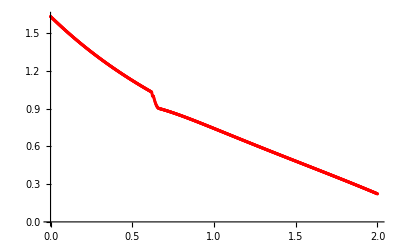

```mathematica
plotTemperaturyMPF2=ListPlot[tablicaTemperaturMPF2,PlotStyle->Red]
```

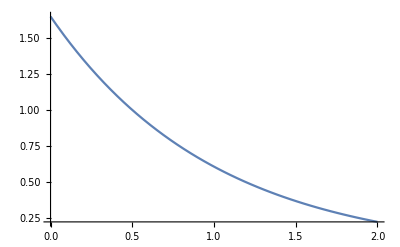

```mathematica
plotTemperaturyDokladne2=Plot[u1[x,1],{x,0,2}]
```

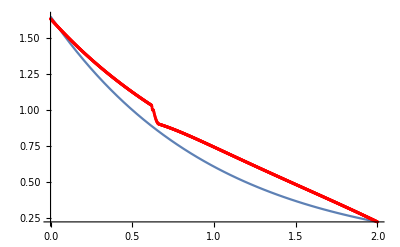

```mathematica
Show[plotTemperaturyDokladne2,plotTemperaturyMPF2]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(√Pi*(lambdaL-lambdaS))/(2*aL*√t);
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t]*roS,temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna2=Table[{i*0.002,entalpia[u1[i*0.002,1],1]},{i,0,1000}];
```

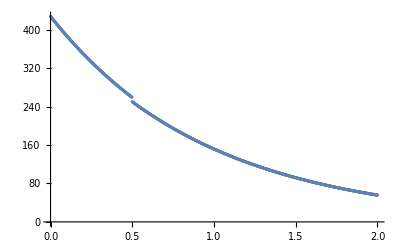

```mathematica
plotEntalpiaDokladna2=ListPlot[tablicaEntalpiaDokladna2]
```

```mathematica
strE2=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE2=ReadList[strE2]
```

{423.366,422.708,422.051,421.396,420.741,420.088,419.437,418.786,418.137,417.489,416.842,416.196,415.552,414.909,414.267,413.626,412.987,412.348,411.711,411.075,410.441,409.807,409.175,408.544,407.914,407.285,406.658,406.031,405.406,404.782,404.159,403.538,402.917,402.298,401.68,401.063,400.447,399.832,399.219,398.606,397.995,397.385,396.776,396.168,395.562,394.956,394.352,393.748,393.146,392.545,391.945,391.346,390.749,390.152,389.557,388.962,388.369,387.777,387.186,386.596,386.007,385.419,384.832,384.247,383.662,383.079,382.496,381.915,381.335,380.756,380.177,379.6,379.024,378.449,377.875,377.303,376.731,376.16,375.59,375.022,374.454,373.887,373.322,372.757,372.194,371.631,371.07,370.509,369.95,369.392,368.834,368.278,367.723,367.168,366.615,366.062,365.511,364.961,364.411,363.863,363.316,362.769,362.224,361.679,361.136,360.593,360.052,359.511,358.972,358.433,357.896,357.359,356.823,356.289,355.755,355.222,354.69,354.159,353.629,353.1,352.572,352.045,351.518,350.993,350.469,349.945,349.423,348.901,348.381,347.861,347.342,346.824,346.307,345.791,345.276,344.762,344.248,343.736,343.224,342.714,342.204,341.695,341.187,340.68,340.174,339.668,339.164,338.66,338.158,337.656,337.155,336.655,336.156,335.658,335.16,334.663,334.168,333.673,333.179,332.686,332.193,331.702,331.211,330.722,330.233,329.745,329.257,328.771,328.285,327.801,327.317,326.834,326.352,325.87,325.39,324.91,324.431,323.953,323.475,322.999,322.523,322.048,321.574,321.101,320.629,320.157,319.686,319.216,318.747,318.278,317.811,317.344,316.878,316.412,315.948,315.484,315.021,314.559,314.097,313.637,313.177,312.718,312.259,311.802,311.345,310.889,310.434,309.979,309.525,309.072,308.62,308.169,307.718,307.268,306.818,306.37,305.922,305.475,305.029,304.583,304.138,303.694,303.251,302.808,302.366,301.925,301.485,301.045,300.606,300.167,299.73,299.293,298.857,298.421,297.986,297.552,297.119,296.686,296.254,295.823,295.393,294.963,294.534,294.105,293.677,293.25,292.824,292.398,291.973,291.549,291.125,290.702,290.28,289.858,289.437,289.017,288.597,288.178,287.76,287.342,286.925,286.509,286.094,285.679,285.264,284.851,284.438,284.025,283.614,283.203,282.792,282.382,281.973,281.565,281.157,280.75,280.343,279.938,279.532,279.128,278.724,278.32,277.918,277.516,277.114,276.713,276.313,275.914,275.515,275.116,274.719,274.322,273.925,273.529,273.134,272.74,272.346,271.952,271.56,271.168,270.776,270.386,269.995,269.606,269.217,268.829,268.441,268.054,267.668,267.283,265.024,261.519,258.378,255.242,252.306,249.54,246.808,244.414,242.022,239.864,237.842,235.894,234.242,232.591,231.224,229.941,228.79,227.876,226.963,226.4,225.855,225.512,225.336,225.159,224.981,224.801,224.62,224.437,224.254,224.069,223.883,223.696,223.507,223.318,223.127,222.935,222.742,222.548,222.353,222.156,221.959,221.76,221.561,221.36,221.159,220.956,220.753,220.548,220.342,220.136,219.928,219.72,219.511,219.301,219.089,218.877,218.665,218.451,218.236,218.021,217.804,217.587,217.369,217.151,216.931,216.711,216.49,216.268,216.046,215.822,215.598,215.374,215.148,214.922,214.695,214.468,214.24,214.011,213.782,213.551,213.321,213.089,212.857,212.625,212.392,212.158,211.924,211.689,211.453,211.217,210.981,210.744,210.506,210.268,210.029,209.79,209.55,209.31,209.069,208.828,208.587,208.345,208.102,207.859,207.616,207.372,207.127,206.883,206.638,206.392,206.146,205.9,205.653,205.406,205.158,204.911,204.662,204.414,204.165,203.916,203.666,203.416,203.166,202.915,202.664,202.413,202.161,201.909,201.657,201.405,201.152,200.899,200.646,200.392,200.138,199.884,199.63,199.375,199.12,198.865,198.61,198.354,198.098,197.842,197.586,197.329,197.073,196.816,196.559,196.301,196.044,195.786,195.528,195.27,195.012,194.753,194.495,194.236,193.977,193.718,193.459,193.199,192.94,192.68,192.42,192.16,191.9,191.64,191.379,191.119,190.858,190.597,190.336,190.075,189.814,189.553,189.292,189.03,188.769,188.507,188.245,187.983,187.721,187.459,187.197,186.935,186.673,186.411,186.148,185.886,185.623,185.361,185.098,184.835,184.572,184.31,184.047,183.784,183.521,183.258,182.994,182.731,182.468,182.205,181.942,181.678,181.415,181.152,180.888,180.625,180.361,180.098,179.835,179.571,179.307,179.044,178.78,178.517,178.253,177.99,177.726,177.462,177.199,176.935,176.672,176.408,176.144,175.881,175.617,175.353,175.09,174.826,174.563,174.299,174.036,173.772,173.508,173.245,172.981,172.718,172.454,172.191,171.928,171.664,171.401,171.137,170.874,170.611,170.348,170.084,169.821,169.558,169.295,169.032,168.768,168.505,168.242,167.979,167.716,167.453,167.191,166.928,166.665,166.402,166.139,165.877,165.614,165.352,165.089,164.826,164.564,164.302,164.039,163.777,163.515,163.252,162.99,162.728,162.466,162.204,161.942,161.68,161.418,161.156,160.894,160.633,160.371,160.109,159.848,159.586,159.325,159.063,158.802,158.541,158.28,158.018,157.757,157.496,157.235,156.974,156.713,156.452,156.192,155.931,155.67,155.41,155.149,154.889,154.628,154.368,154.107,153.847,153.587,153.327,153.067,152.807,152.547,152.287,152.027,151.767,151.508,151.248,150.988,150.729,150.469,150.21,149.95,149.691,149.432,149.173,148.914,148.655,148.396,148.137,147.878,147.619,147.36,147.101,146.843,146.584,146.326,146.067,145.809,145.55,145.292,145.034,144.776,144.518,144.259,144.001,143.743,143.486,143.228,142.97,142.712,142.455,142.197,141.939,141.682,141.424,141.167,140.91,140.652,140.395,140.138,139.881,139.624,139.367,139.11,138.853,138.596,138.339,138.082,137.826,137.569,137.312,137.056,136.799,136.543,136.286,136.03,135.774,135.517,135.261,135.005,134.749,134.493,134.237,133.981,133.725,133.469,133.213,132.957,132.701,132.445,132.19,131.934,131.678,131.423,131.167,130.912,130.656,130.401,130.145,129.89,129.635,129.379,129.124,128.869,128.614,128.359,128.104,127.849,127.593,127.338,127.083,126.829,126.574,126.319,126.064,125.809,125.554,125.299,125.045,124.79,124.535,124.281,124.026,123.771,123.517,123.262,123.008,122.753,122.499,122.244,121.99,121.735,121.481,121.226,120.972,120.718,120.463,120.209,119.955,119.7,119.446,119.192,118.937,118.683,118.429,118.175,117.92,117.666,117.412,117.158,116.904,116.65,116.395,116.141,115.887,115.633,115.379,115.125,114.87,114.616,114.362,114.108,113.854,113.6,113.346,113.091,112.837,112.583,112.329,112.075,111.821,111.566,111.312,111.058,110.804,110.55,110.295,110.041,109.787,109.533,109.278,109.024,108.77,108.516,108.261,108.007,107.753,107.498,107.244,106.989,106.735,106.481,106.226,105.972,105.717,105.463,105.208,104.953,104.699,104.444,104.19,103.935,103.68,103.425,103.171,102.916,102.661,102.406,102.151,101.896,101.641,101.386,101.131,100.876,100.621,100.366,100.111,99.8555,99.6002,99.3449,99.0896,98.8342,98.5787,98.3232,98.0677,97.8121,97.5565,97.3009,97.0451,96.7894,96.5336,96.2777,96.0218,95.7658,95.5098,95.2537,94.9976,94.7414,94.4852,94.2289,93.9726,93.7161,93.4597,93.2032,92.9466,92.6899,92.4332,92.1764,91.9196,91.6627,91.4057,91.1487,90.8916,90.6345,90.3772,90.1199,89.8625,89.6051,89.3476,89.09,88.8324,88.5746,88.3168,88.0589,87.801,87.5429,87.2848,87.0266,86.7684,86.51,86.2516,85.9931,85.7345,85.4758,85.2171,84.9582,84.6993,84.4403,84.1812,83.922,83.6627,83.4033,83.1439,82.8843,82.6247,82.3649,82.1051,81.8452,81.5851,81.325,81.0648,80.8045,80.5441,80.2836,80.023,79.7623,79.5014,79.2405,78.9795,78.7184,78.4572,78.1958,77.9344,77.6728,77.4112,77.1494,76.8875,76.6256,76.3635,76.1013,75.8389,75.5765,75.3139,75.0513,74.7885,74.5256,74.2626,73.9994,73.7362,73.4728,73.2093,72.9457,72.6819,72.4181,72.1541,71.89,71.6257,71.3614,71.0969,70.8322,70.5675,70.3026,70.0376,69.7724,69.5071,69.2417,68.9762,68.7105,68.4447,68.1787,67.9126,67.6464,67.38,67.1135,66.8468,66.5801,66.3131,66.046,65.7788,65.5114,65.2439,64.9763,64.7084,64.4405,64.1724,63.9041,63.6357,63.3671,63.0984,62.8296,62.5605,62.2914,62.022,61.7526,61.4829,61.2131,60.9431,60.673,60.4027,60.1323,59.8617,59.5909,59.32,59.0489,58.7776,58.5062,58.2346,57.9628,57.6909,57.4188,57.1465,56.8741,56.6014,56.3286,56.0557,55.7825}

```mathematica
strListE2={423.3660662525,422.7080189737,422.0512327538,421.3957020545,420.7414220425,420.0883896867,419.4366019641,418.78605586,418.1367483678,417.488676489,416.8418372333,416.1962276184,415.55184467,414.9086854221,414.2667469163,413.6260262032,412.9865203413,412.3482263971,411.7111414451,411.0752621137,410.4405854797,409.8071086278,409.1748286586,408.5437426871,407.9138478364,407.285141237,406.6576200273,406.0312813537,405.4061223707,404.7821402406,404.1593321331,403.5376952257,402.9172262354,402.2979223401,401.6797807254,401.0627985846,400.446973118,399.8323015463,399.2187811015,398.6064090233,397.9951825588,397.3850989623,396.7761554957,396.1683489595,395.5616766148,394.9561357297,394.3517235797,393.7484374477,393.1462746247,392.5452324187,391.9453081513,391.3464991517,390.7488023035,390.1522149338,389.5567343766,388.9623579729,388.3690830713,387.776907028,387.1858272063,386.5958409811,386.0069457463,385.4191384533,384.832416493,384.2467772633,383.6622181697,383.0787366248,382.4963300483,381.9149958664,381.334731092,380.7555331648,380.1773995314,379.6003276451,379.0243149672,378.4493589656,377.8754571146,377.3026068954,376.7308053712,376.160050036,375.5903383907,375.0216679437,374.4540362102,373.8874407115,373.3218785595,372.7573472766,372.1938444031,371.6313674869,371.0699140827,370.5094817516,369.9500680609,369.3916701634,368.8342856277,368.2779120402,367.7225469948,367.1681880913,366.6148329357,366.0624787234,365.5111230587,364.9607635614,364.4113978634,363.8630236027,363.3156384235,362.7692395587,362.2238246501,361.6793913526,361.1359373356,360.5934602744,360.0519574441,359.5114265174,358.971865173,358.4332711043,357.8956420174,357.3589756245,356.82326923,356.2885205429,355.7547272797,355.2218871742,354.6899979689,354.1590570032,353.6290620157,353.1000107526,352.5719009714,352.0447304442,351.5184965422,350.9931970336,350.4688296939,349.9453923067,349.4228826734,348.9012981941,348.3806366659,347.8608958938,347.3420736894,346.824167883,346.307175901,345.7910955694,345.275924722,344.7616612007,344.2483024655,343.7358463647,343.224290754,342.7136334952,342.2038724619,341.6950051354,341.1870293923,340.6799431171,340.1737441995,339.6684301482,339.1639988612,338.6604482451,338.1577762115,337.6559802902,337.1550584011,336.655008472,336.1558284365,335.6575158451,335.1600686396,334.6634847687,334.1677621879,333.6728984708,333.1788915781,332.6857394799,332.1934401529,331.7019911929,331.2113905802,330.7216363063,330.2327263691,329.7446583851,329.2574303549,328.7710402916,328.285486214,327.8007657582,327.3168769458,326.8338178115,326.351586395,325.8701803508,325.3895977229,324.9098365672,324.4308945637,323.9527697641,323.4754602366,322.9989640572,322.5232789224,322.0484029055,321.5743340981,321.1010705964,320.6286101121,320.156950744,319.6860906039,319.2160274271,318.7467593206,318.2782844099,317.8106008267,317.3437063197,316.8775990214,316.4122770792,315.9477382633,315.4839807161,315.0210025987,314.5588017025,314.097376185,313.6367242161,313.176843978,312.7177332733,312.2593902817,311.8018132005,311.344999852,310.8889484287,310.4336571405,309.9791238295,309.5253467024,309.072323981,308.6200535261,308.1685335596,307.717762315,307.2677376715,306.8184578662,306.3699211461,305.9221257731,305.4750696338,305.0287509893,304.583168116,304.1383189183,303.6942016713,303.2508146669,302.8081558265,302.3662234401,301.9250158153,301.4845308905,301.044766971,300.6057223808,300.1673950748,299.7297833743,299.2928856204,298.8566997844,298.4212242045,297.9864572391,297.552396876,297.1190414712,296.686389041,296.2544379497,295.8231865727,295.3926329437,294.9627754446,294.5336124715,294.1051420757,293.6773626573,293.2502726352,292.8238700786,292.3981534061,291.9731210622,291.5487711339,291.1251020596,290.7021123121,290.2797999966,289.8581635742,289.4372011911,289.0169113275,288.597292477,288.1783428093,287.7600608263,287.3424450592,286.9254936997,286.5092052758,286.093578363,285.6786111757,285.2643022723,284.8506499234,284.4376527228,284.0253092842,283.6136179162,283.2025772404,282.7921859382,282.3824423504,281.9733451393,281.5648927169,281.1570838129,280.7499171763,280.3433912867,279.9375049146,279.5322569283,279.1276458656,278.7236705673,278.3203296985,277.9176222128,277.5155471281,277.1141032329,276.7132895545,276.3131050069,275.913548843,275.5146203226,275.116318627,274.7186431492,274.3215935829,273.9251693706,273.529370215,273.1341960567,272.7396469976,272.3457236119,271.9524264881,271.5597562875,271.1677147423,270.7763036301,270.3855258666,269.9953851665,269.6058849587,269.2170331314,268.828837226,268.4413112174,268.0544745564,267.6683536885,267.2831027956,265.0235776609,261.5191331987,258.3783671804,255.2421326989,252.3056559839,249.5404302181,246.8083948542,244.4138922609,242.0220432157,239.8643784521,237.8422815781,235.8943060509,234.2418762385,232.5905141028,231.2235911483,229.9412201926,228.7897229841,227.8764481869,226.9629223393,226.400059271,225.8552270981,225.5121001779,225.3362554721,225.1590826231,224.9805977274,224.8008167175,224.6197553639,224.4374292763,224.2538539052,224.0690445434,223.8830163276,223.6957842399,223.507363109,223.3177676121,223.1270122761,222.935111479,222.7420794515,222.5479302782,222.3526778992,222.1563361112,221.9589185693,221.7604387881,221.5609101427,221.3603458709,221.1587590736,220.9561627167,220.7525696323,220.5479925196,220.3424439467,220.1359363516,219.9284820433,219.7200932034,219.510781887,219.300560024,219.0894394203,218.8774317593,218.6645486023,218.4508013906,218.2362014461,218.0207599722,217.8044880558,217.5873966676,217.3694966636,217.150798786,216.9313136646,216.7110518175,216.4900236524,216.2682394677,216.0457094534,215.8224436921,215.5984521603,215.3737447291,215.1483311653,214.9222211328,214.6954241928,214.4679498055,214.2398073307,214.0110060289,213.7815550621,213.551463495,213.3207402957,213.0893943368,212.857434396,212.6248691576,212.3917072127,212.1579570607,211.9236271096,211.6887256776,211.4532609932,211.2172411966,210.9806743402,210.7435683898,210.5059312252,210.2677706408,210.029094347,209.7899099706,209.5502250557,209.3100470643,209.0693833774,208.8282412959,208.5866280407,208.3445507542,208.1020165006,207.8590322667,207.6156049631,207.3717414242,207.1274484094,206.8827326039,206.6376006191,206.3920589934,206.1461141931,205.8997726128,205.6530405763,205.4059243373,205.1584300799,204.9105639192,204.6623319026,204.4137400094,204.1647941524,203.9155001782,203.6658638675,203.4158909363,203.1655870362,202.9149577551,202.6640086177,202.4127450865,202.1611725616,201.9092963824,201.6571218271,201.404654114,201.151898402,200.8988597907,200.6455433216,200.3919539782,200.1380966867,199.8839763168,199.6295976817,199.3749655392,199.120084592,198.864959488,198.6095948214,198.3539951325,198.0981649089,197.8421085857,197.5858305457,197.3293351205,197.0726265907,196.8157091863,196.5585870873,196.3012644242,196.0437452785,195.7860336831,195.5281336227,195.2700490344,195.0117838083,194.7533417876,194.4947267691,194.235942504,193.9769926982,193.7178810123,193.4586110626,193.1991864215,192.9396106173,192.6798871355,192.4200194185,192.1600108665,191.8998648375,191.6395846481,191.3791735737,191.1186348487,190.8579716675,190.5971871841,190.3362845131,190.0752667299,189.814136871,189.5528979343,189.2915528799,189.0301046298,188.7685560689,188.5069100451,188.2451693695,187.983336817,187.7214151265,187.4594070015,187.19731511,186.9351420852,186.6728905258,186.4105629963,186.148162027,185.8856901151,185.6231497241,185.3605432849,185.0978731957,184.8351418223,184.5723514988,184.3095045272,184.0466031787,183.783649693,183.5206462792,183.257595116,182.994498352,182.7313581057,182.4681764663,182.2049554935,181.9416972181,181.6784036422,181.4150767395,181.1517184554,180.8883307074,180.6249153857,180.3614743527,180.098009444,179.8345224684,179.571015208,179.3074894187,179.0439468302,178.7803891466,178.5168180464,178.2532351827,177.9896421838,177.726040653,177.462432169,177.1988182864,176.9352005355,176.6715804228,176.4079594313,176.1443390205,175.8807206268,175.6171056636,175.3534955217,175.0898915693,174.8262951524,174.562707595,174.299130199,174.0355642451,173.7720109922,173.5084716782,173.24494752,172.9814397137,172.7179494346,172.4544778381,172.1910260588,171.9275952119,171.6641863923,171.4008006757,171.137439118,170.8741027564,170.6107926085,170.3475096734,170.0842549315,169.8210293447,169.5578338565,169.2946693924,169.0315368599,168.7684371487,168.5053711311,168.2423396618,167.9793435782,167.7163837007,167.453460833,167.1905757616,166.9277292569,166.6649220725,166.4021549459,166.1394285985,165.8767437357,165.6141010473,165.3515012072,165.088944874,164.8264326909,164.563965286,164.3015432722,164.0391672478,163.7768377962,163.5145554861,163.2523208719,162.9901344938,162.7279968776,162.4659085352,162.2038699647,161.9418816503,161.6799440626,161.4180576588,161.1562228827,160.8944401649,160.632709923,160.3710325615,160.1094084722,159.847838034,159.5863216134,159.3248595645,159.0634522289,158.802099936,158.5408030032,158.279561736,158.0183764279,157.7572473606,157.4961748045,157.2351590182,156.9742002489,156.7132987328,156.4524546946,156.1916683483,155.9309398965,155.6702695315,155.4096574343,155.1491037758,154.888608716,154.6281724047,154.3677949812,154.1074765749,153.8472173046,153.5870172797,153.3268765991,153.0667953522,152.8067736188,152.5468114688,152.2869089626,152.0270661515,151.767283077,151.5075597717,151.247896259,150.988292553,150.7287486591,150.4692645738,150.2098402845,149.9504757703,149.6911710015,149.4319259397,149.1727405384,148.9136147425,148.6545484887,148.3955417053,148.1365943128,147.8777062235,147.6188773417,147.360107564,147.1013967789,146.8427448674,146.584151703,146.3256171512,146.0671410703,145.8087233113,145.5503637174,145.2920621251,145.0338183633,144.7756322538,144.5175036115,144.2594322443,144.0014179532,143.743460532,143.4855597683,143.2277154426,142.9699273289,142.7121951945,142.4545188003,142.1968979007,141.9393322438,141.6818215714,141.4243656188,141.1669641154,140.9096167844,140.6523233428,140.3950835017,140.1378969663,139.8807634358,139.6236826037,139.3666541575,139.1096777794,138.8527531455,138.5958799266,138.3390577878,138.0822863888,137.8255653839,137.5688944219,137.3122731464,137.0557011957,136.7991782029,136.542703796,136.2862775976,136.0298992256,135.7735682927,135.5172844068,135.2610471707,135.0048561824,134.7487110353,134.4926113177,134.2365566135,133.9805465017,133.7245805569,133.4686583489,133.2127794432,132.9569434007,132.701149778,132.4453981271,132.1896879957,131.9340189275,131.6783904617,131.4228021331,131.1672534728,130.9117440074,130.6562732597,130.4008407481,130.1454459874,129.8900884882,129.6347677572,129.3794832973,129.1242346076,128.8690211832,128.6138425156,128.3586980926,128.1035873983,127.848509913,127.5934651137,127.3384524734,127.0834714621,126.8285215458,126.5736021873,126.3187128459,126.0638529777,125.8090220351,125.5542194674,125.2994447207,125.0446972375,124.7899764576,124.535281817,124.2806127491,124.0259686838,123.7713490482,123.5167532661,123.2621807583,123.0076309429,122.7531032346,122.4985970455,122.2441117847,121.9896468584,121.73520167,121.48077562,121.2263681063,120.9719785238,120.7176062649,120.4632507192,120.2089112737,119.9545873126,119.7002782176,119.4459833679,119.19170214,118.9374339079,118.6831780432,118.4289339149,118.1747008896,117.9204783315,117.6662656023,117.4120620614,117.1578670659,116.9036799706,116.6495001277,116.3953268874,116.1411595978,115.8869976043,115.6328402505,115.3786868777,115.1245368249,114.8703894293,114.6162440255,114.3620999466,114.107956523,113.8538130837,113.5996689551,113.345523462,113.091375927,112.8372256708,112.5830720123,112.3289142683,112.0747517537,111.8205837817,111.5664096635,111.3122287085,111.0580402243,110.8038435167,110.5496378897,110.2954226455,110.0411970848,109.7869605063,109.5327122071,109.2784514827,109.0241776268,108.7698899315,108.5155876874,108.2612701833,108.0069367066,107.7525865429,107.4982189764,107.2438332898,106.9894287642,106.7350046791,106.4805603128,106.2260949418,105.9716078414,105.7170982852,105.4625655457,105.2080088938,104.953427599,104.6988209295,104.444188152,104.1895285321,103.9348413338,103.6801258201,103.4253812523,103.1706068908,102.9158019945,102.6609658212,102.4060976272,102.1511966679,101.8962621972,101.6412934681,101.3862897322,101.1312502399,100.8761742406,100.6210609824,100.3659097125,100.1107196767,99.8554901199,99.6002202858,99.3449094171,99.0895567553,98.8341615411,98.5787230139,98.3232404122,98.0677129735,97.8121399342,97.5565205298,97.3008539947,97.0451395625,96.7893764658,96.5335639361,96.2777012042,96.0217874998,95.7658220518,95.5098040881,95.2537328357,94.9976075209,94.741427369,94.4851916045,94.2288994509,93.9725501311,93.716142867,93.4596768797,93.2031513897,92.9465656164,92.6899187786,92.4332100943,92.1764387808,91.9196040545,91.6627051311,91.4057412257,91.1487115525,90.8916153251,90.6344517562,90.3772200582,90.1199194424,89.8625491197,89.6051083,89.347596193,89.0900120075,88.8323549514,88.5746242325,88.3168190577,88.0589386331,87.8009821644,87.5429488568,87.2848379148,87.0266485422,86.7683799424,86.510031318,86.2516018714,85.9930908042,85.7344973174,85.4758206117,85.217059887,84.958214343,84.6992831785,84.4402655922,84.1811607819,83.9219679453,83.6626862793,83.4033149805,83.143853245,82.8843002684,82.6246552459,82.3649173722,82.1050858415,81.8451598478,81.5851385844,81.3250212443,81.0648070201,80.804495104,80.5440846878,80.2835749629,80.0229651202,79.7622543504,79.5014418437,79.2405267899,78.9795083786,78.718385799,78.4571582398,78.1958248895,77.9343849363,77.6728375678,77.4111819717,77.1494173349,76.8875428444,76.6255576867,76.363461048,76.1012521141,75.8389300709,75.5764941034,75.313943397,75.0512771363,74.7884945058,74.5255946898,74.2625768723,73.9994402371,73.7361839676,73.472807247,73.2093092585,72.9456891847,72.6819462083,72.4180795114,72.1540882764,71.8899716849,71.6257289188,71.3613591595,71.0968615883,70.8322353862,70.5674797343,70.3025938131,70.0375768032,69.772427885,69.5071462387,69.2417310443,68.9761814815,68.7104967303,68.44467597,68.1787183801,67.9126231398,67.6463894283,67.3800164245,67.1135033072,66.8468492552,66.580053447,66.3131150612,66.046033276,65.7788072697,65.5114362205,65.2439193063,64.9762557051,64.7084445947,64.4404851529,64.1723765573,63.9041179854,63.6357086147,63.3671476227,63.0984341866,62.8295674838,62.5605466913,62.2913709864,62.022039546,61.7525515472,61.482906167,61.2131025821,60.9431399696,60.6730175061,60.4027343685,60.1322897334,59.8616827776,59.5909126778,59.3199786106,59.0488797525,58.7776152802,58.5061843702,58.2345861992,57.9628199436,57.6908847799,57.4187798847,57.1465044346,56.8740576059,56.6014385754,56.3286465193,56.0556806144,55.7825400371};
```

```mathematica
tablicaEntalpiaMPF2=Table[{i*0.002,strListE2[[i+1]]},{i,0,1000}];
```

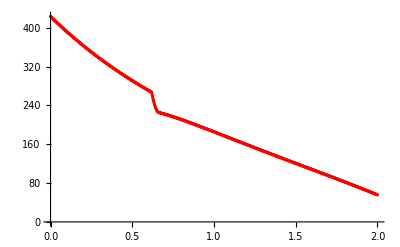

```mathematica
plotEntalpiaMPF2=ListPlot[tablicaEntalpiaMPF2,PlotStyle->Red]
```

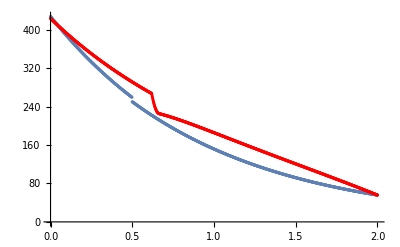

```mathematica
Show[plotEntalpiaDokladna2,plotEntalpiaMPF2]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv

### alfa = 1/2, t=1.5

#### temperatury

```mathematica
str3=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList3=ReadList[str3]
```

{2.10649,2.10272,2.09896,2.0952,2.09146,2.08772,2.08399,2.08027,2.07656,2.07285,2.06916,2.06547,2.06179,2.05811,2.05445,2.05079,2.04714,2.04349,2.03986,2.03623,2.03261,2.029,2.0254,2.0218,2.01821,2.01463,2.01105,2.00749,2.00393,2.00038,1.99683,1.9933,1.98977,1.98625,1.98273,1.97922,1.97573,1.97223,1.96875,1.96527,1.9618,1.95834,1.95488,1.95143,1.94799,1.94456,1.94113,1.93771,1.9343,1.9309,1.9275,1.92411,1.92072,1.91735,1.91398,1.91061,1.90726,1.90391,1.90057,1.89723,1.89391,1.89059,1.88727,1.88397,1.88067,1.87737,1.87409,1.87081,1.86753,1.86427,1.86101,1.85776,1.85451,1.85127,1.84804,1.84482,1.8416,1.83839,1.83518,1.83198,1.82879,1.8256,1.82242,1.81925,1.81609,1.81293,1.80978,1.80663,1.80349,1.80036,1.79723,1.79411,1.791,1.78789,1.78479,1.78169,1.7786,1.77552,1.77245,1.76938,1.76631,1.76326,1.76021,1.75716,1.75412,1.75109,1.74807,1.74505,1.74203,1.73903,1.73603,1.73303,1.73004,1.72706,1.72408,1.72111,1.71815,1.71519,1.71224,1.70929,1.70635,1.70342,1.70049,1.69757,1.69465,1.69174,1.68884,1.68594,1.68305,1.68016,1.67728,1.6744,1.67153,1.66867,1.66581,1.66296,1.66011,1.65727,1.65444,1.65161,1.64879,1.64597,1.64316,1.64035,1.63755,1.63475,1.63196,1.62918,1.6264,1.62363,1.62086,1.6181,1.61534,1.61259,1.60985,1.60711,1.60438,1.60165,1.59892,1.59621,1.59349,1.59079,1.58809,1.58539,1.5827,1.58001,1.57733,1.57466,1.57199,1.56933,1.56667,1.56401,1.56137,1.55872,1.55608,1.55345,1.55082,1.5482,1.54559,1.54297,1.54037,1.53777,1.53517,1.53258,1.52999,1.52741,1.52484,1.52227,1.5197,1.51714,1.51458,1.51203,1.50949,1.50695,1.50441,1.50188,1.49935,1.49683,1.49432,1.49181,1.4893,1.4868,1.4843,1.48181,1.47933,1.47684,1.47437,1.47189,1.46943,1.46697,1.46451,1.46205,1.45961,1.45716,1.45472,1.45229,1.44986,1.44744,1.44502,1.4426,1.44019,1.43779,1.43539,1.43299,1.4306,1.42821,1.42583,1.42345,1.42108,1.41871,1.41634,1.41398,1.41163,1.40928,1.40693,1.40459,1.40225,1.39992,1.39759,1.39526,1.39295,1.39063,1.38832,1.38601,1.38371,1.38141,1.37912,1.37683,1.37455,1.37227,1.36999,1.36772,1.36545,1.36319,1.36093,1.35868,1.35643,1.35418,1.35194,1.3497,1.34747,1.34524,1.34301,1.34079,1.33858,1.33636,1.33416,1.33195,1.32975,1.32756,1.32536,1.32318,1.32099,1.31881,1.31664,1.31447,1.3123,1.31014,1.30798,1.30582,1.30367,1.30152,1.29938,1.29724,1.29511,1.29297,1.29085,1.28872,1.2866,1.28449,1.28238,1.28027,1.27816,1.27606,1.27397,1.27188,1.26979,1.2677,1.26562,1.26354,1.26147,1.2594,1.25734,1.25527,1.25322,1.25116,1.24911,1.24706,1.24502,1.24298,1.24094,1.23891,1.23688,1.23486,1.23284,1.23082,1.22881,1.2268,1.22479,1.22279,1.22079,1.21879,1.2168,1.21481,1.21283,1.21085,1.20887,1.20689,1.20492,1.20295,1.20099,1.19903,1.19707,1.19512,1.19317,1.19122,1.18928,1.18734,1.18541,1.18347,1.18154,1.17962,1.1777,1.17578,1.17386,1.17195,1.17004,1.16814,1.16623,1.16434,1.16244,1.16055,1.15866,1.15677,1.15489,1.15301,1.15114,1.14927,1.1474,1.14553,1.14367,1.14181,1.13995,1.1381,1.13625,1.13441,1.13256,1.13072,1.12889,1.12705,1.12522,1.12339,1.12157,1.11975,1.11793,1.11612,1.11431,1.1125,1.11069,1.10889,1.10709,1.10529,1.1035,1.10171,1.09993,1.09814,1.09636,1.09458,1.09281,1.09104,1.08927,1.0875,1.08574,1.08398,1.08222,1.08047,1.07872,1.07697,1.07523,1.07349,1.07175,1.07001,1.06828,1.06655,1.06482,1.0631,1.06138,1.05966,1.05794,1.05623,1.05452,1.05281,1.05111,1.04941,1.04771,1.04602,1.04433,1.04264,1.04095,1.03927,1.03759,1.03591,1.03424,1.03257,1.02119,1.0059,1,1,0.993818,0.981309,0.969956,0.959133,0.949233,0.940093,0.931648,0.924187,0.917198,0.911413,0.90588,0.901769,0.897696,0.895256,0.892813,0.891874,0.891098,0.890317,0.889529,0.888735,0.887936,0.887132,0.886321,0.885505,0.884684,0.883857,0.883025,0.882188,0.881345,0.880497,0.879645,0.878787,0.877924,0.877057,0.876185,0.875307,0.874426,0.873539,0.872649,0.871753,0.870853,0.869949,0.869041,0.868128,0.867211,0.86629,0.865364,0.864435,0.863502,0.862564,0.861623,0.860678,0.859729,0.858777,0.857821,0.856861,0.855898,0.854931,0.85396,0.852986,0.852009,0.851029,0.850045,0.849058,0.848067,0.847074,0.846077,0.845078,0.844075,0.843069,0.842061,0.841049,0.840035,0.839017,0.837997,0.836975,0.835949,0.834921,0.833891,0.832857,0.831822,0.830783,0.829743,0.828699,0.827654,0.826606,0.825556,0.824503,0.823448,0.822391,0.821332,0.820271,0.819208,0.818142,0.817075,0.816005,0.814934,0.81386,0.812785,0.811707,0.810628,0.809547,0.808465,0.80738,0.806294,0.805206,0.804116,0.803025,0.801932,0.800838,0.799742,0.798644,0.797545,0.796445,0.795343,0.794239,0.793134,0.792028,0.790921,0.789812,0.788701,0.78759,0.786477,0.785363,0.784248,0.783132,0.782014,0.780895,0.779776,0.778655,0.777533,0.77641,0.775286,0.774161,0.773035,0.771908,0.77078,0.769651,0.768521,0.76739,0.766259,0.765126,0.763993,0.762859,0.761724,0.760589,0.759452,0.758315,0.757178,0.756039,0.7549,0.75376,0.75262,0.751478,0.750337,0.749194,0.748051,0.746908,0.745764,0.744619,0.743474,0.742328,0.741182,0.740036,0.738889,0.737741,0.736593,0.735445,0.734296,0.733147,0.731997,0.730847,0.729697,0.728546,0.727395,0.726244,0.725093,0.723941,0.722789,0.721636,0.720484,0.719331,0.718178,0.717024,0.715871,0.714717,0.713563,0.712409,0.711255,0.7101,0.708946,0.707791,0.706636,0.705481,0.704326,0.703171,0.702016,0.700861,0.699705,0.69855,0.697395,0.696239,0.695084,0.693928,0.692772,0.691617,0.690461,0.689306,0.68815,0.686995,0.685839,0.684684,0.683529,0.682373,0.681218,0.680063,0.678908,0.677753,0.676598,0.675443,0.674289,0.673134,0.67198,0.670825,0.669671,0.668517,0.667363,0.66621,0.665056,0.663903,0.66275,0.661596,0.660444,0.659291,0.658139,0.656986,0.655834,0.654682,0.653531,0.652379,0.651228,0.650077,0.648926,0.647776,0.646626,0.645476,0.644326,0.643176,0.642027,0.640878,0.639729,0.638581,0.637433,0.636285,0.635137,0.63399,0.632843,0.631696,0.63055,0.629404,0.628258,0.627112,0.625967,0.624822,0.623678,0.622534,0.62139,0.620246,0.619103,0.61796,0.616817,0.615675,0.614533,0.613392,0.61225,0.611109,0.609969,0.608829,0.607689,0.606549,0.60541,0.604272,0.603133,0.601995,0.600857,0.59972,0.598583,0.597447,0.596311,0.595175,0.594039,0.592904,0.59177,0.590635,0.589501,0.588368,0.587235,0.586102,0.58497,0.583838,0.582706,0.581575,0.580444,0.579314,0.578184,0.577054,0.575925,0.574796,0.573667,0.572539,0.571412,0.570284,0.569158,0.568031,0.566905,0.565779,0.564654,0.563529,0.562405,0.561281,0.560157,0.559034,0.557911,0.556788,0.555666,0.554545,0.553423,0.552303,0.551182,0.550062,0.548942,0.547823,0.546704,0.545586,0.544468,0.54335,0.542233,0.541116,0.54,0.538884,0.537768,0.536653,0.535538,0.534424,0.533309,0.532196,0.531083,0.52997,0.528857,0.527745,0.526633,0.525522,0.524411,0.523301,0.522191,0.521081,0.519972,0.518863,0.517754,0.516646,0.515538,0.514431,0.513324,0.512217,0.511111,0.510005,0.508899,0.507794,0.506689,0.505585,0.504481,0.503377,0.502274,0.501171,0.500069,0.498966,0.497865,0.496763,0.495662,0.494561,0.493461,0.492361,0.491262,0.490162,0.489063,0.487965,0.486867,0.485769,0.484671,0.483574,0.482477,0.481381,0.480285,0.479189,0.478093,0.476998,0.475904,0.474809,0.473715,0.472621,0.471528,0.470435,0.469342,0.468249,0.467157,0.466066,0.464974,0.463883,0.462792,0.461701,0.460611,0.459521,0.458432,0.457342,0.456253,0.455165,0.454076,0.452988,0.4519,0.450813,0.449726,0.448639,0.447552,0.446466,0.44538,0.444294,0.443208,0.442123,0.441038,0.439953,0.438869,0.437785,0.436701,0.435617,0.434534,0.433451,0.432368,0.431286,0.430203,0.429121,0.428039,0.426958,0.425877,0.424796,0.423715,0.422634,0.421554,0.420474,0.419394,0.418314,0.417235,0.416156,0.415077,0.413998,0.412919,0.411841,0.410763,0.409685,0.408608,0.40753,0.406453,0.405376,0.404299,0.403222,0.402146,0.40107,0.399993,0.398918,0.397842,0.396766,0.395691,0.394616,0.393541,0.392466,0.391392,0.390317,0.389243,0.388169,0.387095,0.386021,0.384947,0.383874,0.382801,0.381727,0.380654,0.379581,0.378509,0.377436,0.376364,0.375291,0.374219,0.373147,0.372075,0.371003,0.369932,0.36886,0.367789,0.366717,0.365646,0.364575,0.363504,0.362433,0.361362,0.360292,0.359221,0.35815,0.35708,0.35601,0.35494,0.353869,0.352799,0.351729,0.350659,0.34959,0.34852,0.34745,0.34638,0.345311,0.344241,0.343172,0.342102,0.341033,0.339964,0.338895,0.337825,0.336756,0.335687,0.334618,0.333549,0.33248,0.331411,0.330342,0.329273,0.328204,0.327135,0.326066,0.324998,0.323929,0.32286,0.321791,0.320722,0.319653,0.318585,0.317516,0.316447,0.315378,0.314309,0.31324,0.312171,0.311102,0.310033,0.308964,0.307895,0.306826,0.305757,0.304688,0.303619,0.30255,0.301481,0.300411,0.299342,0.298273,0.297203,0.296134,0.295064,0.293994,0.292925,0.291855,0.290785,0.289715,0.288645,0.287575,0.286505}

```mathematica
strList3={2.1064871962,2.1027182659,2.0989573756,2.0952044978,2.0914596067,2.0877226829,2.0839937068,2.0802726589,2.0765595199,2.0728542703,2.069156891,2.0654673625,2.0617856657,2.0581117814,2.0544456905,2.0507873739,2.0471368126,2.0434939877,2.0398588802,2.0362314695,2.0326117368,2.0289996631,2.0253952298,2.0217984182,2.0182092097,2.0146275856,2.0110535275,2.0074870169,2.0039280354,2.0003765645,1.996832586,1.9932960815,1.989767031,1.9862454163,1.9827312191,1.9792244212,1.9757250047,1.9722329514,1.9687482435,1.9652708629,1.9618007919,1.9583380125,1.9548825072,1.9514342562,1.9479932419,1.9445594466,1.9411328526,1.9377134424,1.9343011983,1.9308961029,1.9274981388,1.9241072886,1.9207235333,1.9173468556,1.9139772381,1.9106146637,1.907259115,1.903910575,1.9005690266,1.8972344527,1.8939068363,1.8905861588,1.8872724033,1.8839655529,1.8806655907,1.8773725,1.8740862639,1.8708068658,1.8675342873,1.8642685118,1.8610095228,1.8577573037,1.854511838,1.8512731093,1.848041101,1.8448157969,1.841597179,1.8383852309,1.8351799365,1.8319812795,1.8287892437,1.8256038131,1.82242497,1.8192526982,1.8160869817,1.8129278047,1.8097751512,1.8066290052,1.8034893511,1.8003561712,1.79722945,1.7941091716,1.7909953203,1.7878878806,1.7847868369,1.7816921719,1.7786038701,1.7755219161,1.7724462943,1.7693769894,1.7663139861,1.7632572674,1.7602068179,1.7571626225,1.7541246659,1.751092933,1.7480674071,1.7450480729,1.7420349156,1.7390279199,1.736027071,1.7330323539,1.7300437521,1.7270612508,1.7240848351,1.7211144901,1.7181502011,1.715191952,1.7122397279,1.7092935142,1.7063532962,1.7034190594,1.7004907878,1.6975684668,1.6946520818,1.6917416186,1.6888370626,1.6859383981,1.6830456106,1.6801586858,1.6772776096,1.6744023676,1.6715329442,1.6686693253,1.6658114966,1.6629594441,1.6601131524,1.6572726073,1.6544377948,1.6516087011,1.6487853122,1.6459676128,1.643155589,1.640349227,1.6375485131,1.6347534319,1.6319639699,1.6291801133,1.6264018486,1.6236291605,1.6208620357,1.6181004604,1.6153444214,1.6125939035,1.6098488933,1.6071093776,1.6043753428,1.6016467743,1.5989236586,1.5962059827,1.5934937331,1.5907868953,1.588085456,1.5853894023,1.5826987209,1.5800133973,1.5773334185,1.5746587716,1.5719894434,1.5693254197,1.5666666876,1.5640132341,1.5613650464,1.5587221103,1.556084413,1.5534519418,1.5508246825,1.5482026223,1.5455857487,1.5429740491,1.5403675094,1.5377661171,1.5351698596,1.5325787245,1.5299926979,1.5274117673,1.5248359203,1.5222651432,1.5196994235,1.5171387491,1.5145831076,1.5120324853,1.5094868701,1.5069462497,1.5044106107,1.5018799407,1.4993542279,1.4968334586,1.4943176209,1.4918067027,1.4893006921,1.4867995758,1.4843033417,1.4818119781,1.4793254717,1.4768438106,1.474366983,1.4718949759,1.4694277773,1.4669653757,1.464507758,1.4620549125,1.4596068276,1.4571634903,1.454724889,1.4522910123,1.4498618485,1.4474373849,1.4450176101,1.4426025125,1.4401920794,1.4377862994,1.4353851613,1.4329886522,1.430596761,1.4282094765,1.4258267859,1.4234486781,1.4210751419,1.4187061649,1.4163417359,1.4139818438,1.4116264762,1.4092756221,1.4069292705,1.404587409,1.4022500267,1.3999171113,1.397588652,1.3952646377,1.3929450565,1.3906298973,1.3883191496,1.3860128011,1.3837108411,1.3814132589,1.3791200425,1.3768311813,1.3745466646,1.3722664804,1.3699906183,1.3677190676,1.3654518165,1.3631888545,1.3609301698,1.3586757519,1.3564255905,1.3541796738,1.3519379914,1.349700533,1.347467287,1.3452382431,1.343013391,1.3407927192,1.3385762174,1.3363638742,1.3341556793,1.3319516227,1.3297516928,1.3275558797,1.3253641733,1.3231765622,1.3209930364,1.3188135846,1.3166381969,1.3144668633,1.3122995725,1.3101363148,1.3079770802,1.3058218577,1.3036706373,1.3015234081,1.2993801602,1.2972408839,1.2951055682,1.2929742033,1.2908467784,1.2887232838,1.2866037099,1.2844880458,1.2823762819,1.2802684087,1.2781644153,1.2760642923,1.273968029,1.2718756157,1.2697870433,1.2677023008,1.2656213791,1.2635442673,1.2614709563,1.2594014367,1.2573356978,1.2552737306,1.2532155244,1.25116107,1.2491103583,1.2470633788,1.2450201224,1.2429805786,1.2409447385,1.2389125915,1.2368841286,1.234859341,1.2328382182,1.2308207513,1.2288069301,1.2267967457,1.2247901891,1.2227872501,1.2207879201,1.2187921887,1.2168000472,1.2148114869,1.2128264977,1.2108450708,1.2088671963,1.2068928655,1.2049220683,1.2029547962,1.2009910407,1.1990307916,1.1970740407,1.1951207779,1.1931709947,1.1912246814,1.1892818296,1.1873424307,1.1854064751,1.1834739543,1.1815448587,1.17961918,1.1776969085,1.1757780359,1.173862554,1.1719504533,1.1700417254,1.168136361,1.1662343518,1.1643356883,1.1624403626,1.1605483665,1.1586596906,1.1567743269,1.1548922661,1.1530135002,1.1511380199,1.1492658174,1.1473968847,1.1455312127,1.1436687934,1.1418096179,1.1399536783,1.1381009656,1.136251472,1.1344051885,1.1325621076,1.1307222215,1.1288855215,1.1270519998,1.1252216478,1.123394458,1.1215704215,1.119749531,1.1179317778,1.1161171546,1.1143056541,1.1124972678,1.1106919885,1.1088898077,1.1070907184,1.1052947122,1.1035017822,1.10171192,1.0999251189,1.0981413719,1.0963606712,1.0945830101,1.0928083806,1.0910367763,1.0892681894,1.0875026137,1.0857400416,1.0839804671,1.0822238827,1.0804702827,1.0787196613,1.0769720118,1.0752273287,1.0734856056,1.0717468376,1.0700110184,1.0682781439,1.0665482083,1.064821208,1.063097138,1.0613759956,1.0596577765,1.0579424795,1.056230103,1.0545206458,1.0528141086,1.0511104922,1.0494098003,1.047712037,1.0460172107,1.0443253306,1.0426364138,1.0409504778,1.0392675583,1.0375876873,1.0359109512,1.0342374322,1.0325677213,1.0211869141,1.0059024988,1,1,0.9938181341,0.98130862,0.9699556542,0.9591326093,0.9492332546,0.9400928474,0.9316480786,0.9241869147,0.9171980761,0.9114131882,0.9058797171,0.901768574,0.8976958034,0.8952562352,0.8928132077,0.8918740209,0.8910982468,0.890316518,0.8895289081,0.8887354899,0.8879363356,0.8871315164,0.8863211028,0.8855051649,0.8846837716,0.8838569916,0.8830248925,0.8821875413,0.8813450045,0.8804973476,0.8796446358,0.8787869333,0.8779243038,0.8770568104,0.8761845153,0.8753074802,0.8744257664,0.8735394342,0.8726485434,0.8717531533,0.8708533224,0.8699491087,0.8690405696,0.8681277619,0.8672107417,0.8662895648,0.865364286,0.8644349599,0.8635016404,0.8625643808,0.8616232338,0.8606782516,0.859729486,0.8587769881,0.8578208084,0.8568609971,0.8558976036,0.854930677,0.8539602657,0.8529864179,0.8520091809,0.8510286017,0.8500447268,0.8490576023,0.8480672736,0.8470737858,0.8460771833,0.8450775104,0.8440748106,0.843069127,0.8420605023,0.8410489789,0.8400345984,0.8390174022,0.8379974311,0.8369747258,0.8359493261,0.8349212717,0.8338906017,0.8328573549,0.8318215697,0.830783284,0.8297425352,0.8286993605,0.8276537966,0.8266058798,0.8255556461,0.8245031309,0.8234483694,0.8223913964,0.8213322462,0.8202709529,0.8192075502,0.8181420712,0.8170745489,0.8160050158,0.8149335042,0.8138600459,0.8127846724,0.8117074148,0.8106283039,0.8095473702,0.8084646438,0.8073801545,0.8062939317,0.8052060047,0.8041164022,0.8030251527,0.8019322845,0.8008378252,0.7997418026,0.7986442438,0.7975451759,0.7964446253,0.7953426185,0.7942391815,0.7931343401,0.7920281197,0.7909205454,0.7898116422,0.7887014347,0.7875899472,0.7864772037,0.7853632281,0.7842480438,0.783131674,0.7820141417,0.7808954696,0.7797756803,0.7786547957,0.777532838,0.7764098287,0.7752857893,0.7741607409,0.7730347045,0.7719077008,0.7707797503,0.769650873,0.7685210891,0.7673904182,0.7662588799,0.7651264934,0.7639932777,0.7628592518,0.7617244341,0.7605888432,0.759452497,0.7583154137,0.7571776108,0.756039106,0.7548999165,0.7537600595,0.7526195518,0.7514784101,0.7503366509,0.7491942906,0.7480513451,0.7469078304,0.7457637622,0.744619156,0.743474027,0.7423283906,0.7411822615,0.7400356545,0.7388885843,0.7377410651,0.7365931113,0.7354447368,0.7342959556,0.7331467812,0.7319972273,0.7308473071,0.7296970339,0.7285464205,0.72739548,0.7262442249,0.7250926678,0.723940821,0.7227886967,0.7216363069,0.7204836636,0.7193307784,0.718177663,0.7170243287,0.7158707868,0.7147170485,0.7135631246,0.7124090262,0.7112547637,0.7101003478,0.7089457889,0.7077910972,0.7066362828,0.7054813558,0.704326326,0.7031712031,0.7020159966,0.7008607161,0.6997053708,0.69854997,0.6973945226,0.6962390378,0.6950835241,0.6939279904,0.6927724451,0.6916168968,0.6904613538,0.6893058242,0.6881503161,0.6869948376,0.6858393964,0.6846840003,0.6835286569,0.6823733737,0.6812181582,0.6800630175,0.678907959,0.6777529896,0.6765981163,0.675443346,0.6742886855,0.6731341413,0.6719797201,0.6708254283,0.6696712722,0.6685172581,0.6673633921,0.6662096803,0.6650561286,0.663902743,0.662749529,0.6615964926,0.6604436391,0.6592909741,0.658138503,0.6569862311,0.6558341636,0.6546823056,0.6535306622,0.6523792384,0.6512280389,0.6500770687,0.6489263323,0.6477758345,0.6466255796,0.6454755723,0.6443258169,0.6431763176,0.6420270787,0.6408781043,0.6397293985,0.6385809653,0.6374328085,0.6362849321,0.6351373397,0.6339900351,0.6328430218,0.6316963035,0.6305498836,0.6294037654,0.6282579523,0.6271124477,0.6259672546,0.6248223762,0.6236778156,0.6225335757,0.6213896595,0.6202460698,0.6191028095,0.6179598813,0.6168172878,0.6156750317,0.6145331155,0.6133915417,0.6122503128,0.611109431,0.6099688988,0.6088287183,0.6076888917,0.6065494213,0.605410309,0.604271557,0.603133167,0.6019951412,0.6008574813,0.5997201891,0.5985832665,0.597446715,0.5963105363,0.5951747321,0.5940393039,0.5929042532,0.5917695813,0.5906352898,0.58950138,0.5883678531,0.5872347104,0.5861019532,0.5849695825,0.5838375995,0.5827060052,0.5815748007,0.5804439869,0.5793135648,0.5781835353,0.5770538991,0.5759246572,0.5747958101,0.5736673588,0.5725393038,0.5714116457,0.5702843852,0.5691575228,0.568031059,0.5669049943,0.5657793291,0.5646540639,0.5635291989,0.5624047344,0.5612806709,0.5601570084,0.5590337473,0.5579108876,0.5567884295,0.5556663732,0.5545447186,0.5534234658,0.5523026148,0.5511821656,0.5500621181,0.5489424721,0.5478232275,0.5467043843,0.545585942,0.5444679006,0.5433502598,0.5422330192,0.5411161785,0.5399997374,0.5388836955,0.5377680523,0.5366528075,0.5355379605,0.5344235107,0.5333094578,0.5321958011,0.53108254,0.529969674,0.5288572023,0.5277451243,0.5266334393,0.5255221465,0.5244112453,0.5233007347,0.5221906142,0.5210808827,0.5199715394,0.5188625836,0.5177540142,0.5166458303,0.515538031,0.5144306154,0.5133235823,0.5122169309,0.51111066,0.5100047686,0.5088992555,0.5077941198,0.5066893602,0.5055849756,0.5044809649,0.5033773268,0.5022740601,0.5011711635,0.5000686359,0.498966476,0.4978646824,0.4967632538,0.4956621889,0.4945614863,0.4934611447,0.4923611627,0.4912615389,0.4901622717,0.4890633599,0.4879648018,0.4868665961,0.4857687413,0.4846712357,0.4835740779,0.4824772664,0.4813807995,0.4802846757,0.4791888933,0.4780934508,0.4769983466,0.4759035789,0.4748091461,0.4737150465,0.4726212785,0.4715278403,0.4704347302,0.4693419464,0.4682494873,0.467157351,0.4660655358,0.4649740398,0.4638828613,0.4627919984,0.4617014493,0.4606112121,0.459521285,0.4584316662,0.4573423536,0.4562533455,0.4551646399,0.4540762348,0.4529881284,0.4519003186,0.4508128036,0.4497255814,0.4486386499,0.4475520072,0.4464656513,0.4453795801,0.4442937916,0.4432082838,0.4421230546,0.441038102,0.4399534239,0.4388690182,0.4377848828,0.4367010156,0.4356174145,0.4345340773,0.4334510021,0.4323681865,0.4312856285,0.4302033259,0.4291212764,0.4280394781,0.4269579286,0.4258766257,0.4247955673,0.4237147511,0.422634175,0.4215538366,0.4204737338,0.4193938643,0.4183142258,0.4172348161,0.4161556329,0.4150766739,0.4139979369,0.4129194195,0.4118411195,0.4107630345,0.4096851623,0.4086075004,0.4075300466,0.4064527985,0.4053757539,0.4042989102,0.4032222652,0.4021458166,0.4010695619,0.3999934987,0.3989176248,0.3978419376,0.3967664348,0.3956911141,0.3946159729,0.3935410089,0.3924662196,0.3913916027,0.3903171556,0.389242876,0.3881687615,0.3870948095,0.3860210176,0.3849473834,0.3838739044,0.3828005781,0.381727402,0.3806543738,0.3795814908,0.3785087506,0.3774361507,0.3763636887,0.3752913619,0.374219168,0.3731471043,0.3720751684,0.3710033578,0.3699316699,0.3688601021,0.3677886521,0.3667173172,0.3656460948,0.3645749825,0.3635039777,0.3624330778,0.3613622802,0.3602915825,0.3592209821,0.3581504763,0.3570800626,0.3560097384,0.3549395012,0.3538693484,0.3527992773,0.3517292854,0.3506593702,0.3495895289,0.348519759,0.3474500579,0.346380423,0.3453108516,0.3442413412,0.3431718892,0.3421024929,0.3410331497,0.339963857,0.3388946121,0.3378254124,0.3367562553,0.3356871382,0.3346180584,0.3335490132,0.3324800001,0.3314110163,0.3303420593,0.3292731263,0.3282042147,0.3271353219,0.3260664452,0.3249975819,0.3239287294,0.322859885,0.321791046,0.3207222098,0.3196533736,0.3185845349,0.3175156908,0.3164468389,0.3153779762,0.3143091003,0.3132402083,0.3121712976,0.3111023656,0.3100334094,0.3089644264,0.307895414,0.3068263693,0.3057572898,0.3046881726,0.3036190152,0.3025498147,0.3014805685,0.3004112738,0.299341928,0.2982725283,0.297203072,0.2961335564,0.2950639788,0.2939943364,0.2929246265,0.2918548464,0.2907849933,0.2897150646,0.2886450574,0.2875749691,0.2865047969};
```

```mathematica
tablicaTemperaturMPF3=Table[{i*0.002,strList3[[i+1]]},{i,0,1000}];
```

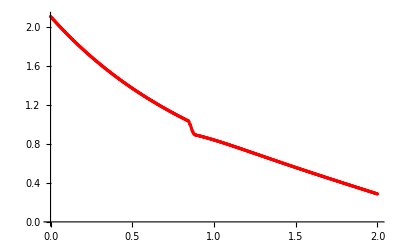

```mathematica
plotTemperaturyMPF3=ListPlot[tablicaTemperaturMPF3,PlotStyle->Red]
```

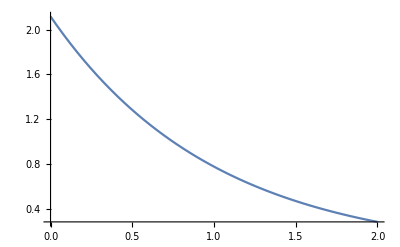

```mathematica
plotTemperaturyDokladne3=Plot[u1[x,1.5],{x,0,2}]
```

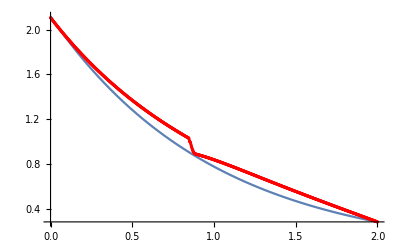

```mathematica
Show[plotTemperaturyDokladne3,plotTemperaturyMPF3]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(√Pi*(lambdaL-lambdaS))/(2*aL*√t);
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t],temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna3=Table[{i*0.002,entalpia[u1[i*0.002,1.5],1.5]},{i,0,1000}];
```

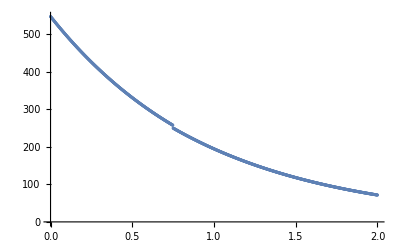

```mathematica
plotEntalpiaDokladna3=ListPlot[tablicaEntalpiaDokladna3]
```

```mathematica
strE3=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE3=ReadList[strE3]
```

{544.923,543.943,542.965,541.989,541.016,540.044,539.074,538.107,537.141,536.178,535.217,534.258,533.3,532.345,531.392,530.441,529.492,528.544,527.599,526.656,525.715,524.776,523.839,522.904,521.97,521.039,520.11,519.183,518.257,517.334,516.412,515.493,514.575,513.66,512.746,511.834,510.925,510.017,509.111,508.206,507.304,506.404,505.505,504.609,503.714,502.821,501.931,501.042,500.154,499.269,498.386,497.504,496.624,495.746,494.87,493.996,493.123,492.253,491.384,490.517,489.652,488.788,487.927,487.067,486.209,485.353,484.498,483.646,482.795,481.946,481.098,480.253,479.409,478.567,477.727,476.888,476.051,475.216,474.383,473.551,472.721,471.893,471.067,470.242,469.419,468.597,467.778,466.96,466.143,465.329,464.516,463.704,462.895,462.087,461.281,460.476,459.673,458.872,458.072,457.274,456.478,455.683,454.89,454.098,453.308,452.52,451.734,450.949,450.165,449.383,448.603,447.824,447.047,446.272,445.498,444.726,443.955,443.186,442.418,441.652,440.888,440.125,439.364,438.604,437.846,437.089,436.334,435.58,434.828,434.077,433.328,432.581,431.835,431.09,430.347,429.605,428.865,428.127,427.39,426.654,425.92,425.188,424.456,423.727,422.999,422.272,421.547,420.823,420.1,419.38,418.66,417.942,417.226,416.51,415.797,415.084,414.374,413.664,412.956,412.25,411.544,410.841,410.138,409.437,408.738,408.039,407.343,406.647,405.953,405.261,404.569,403.879,403.191,402.504,401.818,401.134,400.45,399.769,399.088,398.409,397.732,397.055,396.38,395.706,395.034,394.363,393.693,393.025,392.358,391.692,391.028,390.364,389.703,389.042,388.383,387.725,387.068,386.413,385.759,385.106,384.454,383.804,383.155,382.507,381.861,381.215,380.571,379.929,379.287,378.647,378.008,377.37,376.734,376.099,375.464,374.832,374.2,373.57,372.941,372.313,371.686,371.06,370.436,369.813,369.191,368.57,367.951,367.333,366.716,366.1,365.485,364.871,364.259,363.648,363.038,362.429,361.821,361.214,360.609,360.005,359.402,358.8,358.199,357.599,357.001,356.403,355.807,355.212,354.618,354.025,353.434,352.843,352.253,351.665,351.078,350.492,349.907,349.323,348.74,348.158,347.578,346.998,346.419,345.842,345.266,344.691,344.116,343.543,342.971,342.401,341.831,341.262,340.694,340.128,339.562,338.997,338.434,337.871,337.31,336.75,336.19,335.632,335.075,334.519,333.963,333.409,332.856,332.304,331.753,331.203,330.654,330.106,329.559,329.013,328.468,327.924,327.381,326.839,326.298,325.758,325.218,324.68,324.143,323.607,323.072,322.538,322.005,321.472,320.941,320.411,319.882,319.353,318.826,318.299,317.774,317.249,316.726,316.203,315.681,315.161,314.641,314.122,313.604,313.087,312.571,312.056,311.541,311.028,310.516,310.004,309.494,308.984,308.475,307.967,307.46,306.954,306.449,305.945,305.442,304.939,304.438,303.937,303.437,302.938,302.44,301.943,301.447,300.951,300.457,299.963,299.471,298.979,298.488,297.997,297.508,297.02,296.532,296.045,295.559,295.074,294.59,294.107,293.624,293.142,292.661,292.181,291.702,291.224,290.746,290.27,289.794,289.319,288.844,288.371,287.898,287.426,286.955,286.485,286.016,285.547,285.08,284.613,284.146,283.681,283.217,282.753,282.29,281.828,281.366,280.906,280.446,279.987,279.528,279.071,278.614,278.158,277.703,277.249,276.795,276.342,275.89,275.439,274.988,274.539,274.09,273.641,273.194,272.747,272.301,271.856,271.411,270.968,270.525,270.083,269.641,269.2,268.761,268.321,267.883,267.446,267.009,266.573,266.138,265.704,262.745,258.771,255.206,251.656,248.455,245.327,242.489,239.783,237.308,235.023,232.912,231.047,229.3,227.853,226.47,225.442,224.424,223.814,223.203,222.969,222.775,222.579,222.382,222.184,221.984,221.783,221.58,221.376,221.171,220.964,220.756,220.547,220.336,220.124,219.911,219.697,219.481,219.264,219.046,218.827,218.606,218.385,218.162,217.938,217.713,217.487,217.26,217.032,216.803,216.572,216.341,216.109,215.875,215.641,215.406,215.17,214.932,214.694,214.455,214.215,213.974,213.733,213.49,213.247,213.002,212.757,212.511,212.264,212.017,211.768,211.519,211.269,211.019,210.767,210.515,210.262,210.009,209.754,209.499,209.244,208.987,208.73,208.473,208.214,207.955,207.696,207.436,207.175,206.913,206.651,206.389,206.126,205.862,205.598,205.333,205.068,204.802,204.536,204.269,204.001,203.733,203.465,203.196,202.927,202.657,202.387,202.116,201.845,201.573,201.302,201.029,200.756,200.483,200.209,199.935,199.661,199.386,199.111,198.836,198.56,198.284,198.007,197.73,197.453,197.175,196.897,196.619,196.341,196.062,195.783,195.504,195.224,194.944,194.664,194.383,194.102,193.821,193.54,193.259,192.977,192.695,192.413,192.13,191.848,191.565,191.282,190.998,190.715,190.431,190.147,189.863,189.579,189.294,189.01,188.725,188.44,188.155,187.87,187.584,187.299,187.013,186.727,186.441,186.155,185.869,185.582,185.296,185.009,184.722,184.435,184.148,183.861,183.574,183.287,182.999,182.712,182.424,182.137,181.849,181.561,181.273,180.985,180.697,180.409,180.121,179.833,179.544,179.256,178.968,178.679,178.391,178.102,177.814,177.525,177.236,176.948,176.659,176.37,176.082,175.793,175.504,175.215,174.926,174.637,174.349,174.06,173.771,173.482,173.193,172.904,172.615,172.326,172.038,171.749,171.46,171.171,170.882,170.593,170.305,170.016,169.727,169.438,169.15,168.861,168.572,168.284,167.995,167.706,167.418,167.129,166.841,166.552,166.264,165.976,165.687,165.399,165.111,164.823,164.535,164.247,163.959,163.671,163.383,163.095,162.807,162.519,162.232,161.944,161.656,161.369,161.081,160.794,160.507,160.22,159.932,159.645,159.358,159.071,158.784,158.498,158.211,157.924,157.637,157.351,157.064,156.778,156.492,156.206,155.919,155.633,155.347,155.062,154.776,154.49,154.204,153.919,153.633,153.348,153.063,152.777,152.492,152.207,151.922,151.637,151.353,151.068,150.783,150.499,150.214,149.93,149.646,149.362,149.078,148.794,148.51,148.226,147.942,147.659,147.375,147.092,146.809,146.525,146.242,145.959,145.677,145.394,145.111,144.828,144.546,144.263,143.981,143.699,143.417,143.135,142.853,142.571,142.289,142.008,141.726,141.445,141.164,140.882,140.601,140.32,140.039,139.758,139.478,139.197,138.917,138.636,138.356,138.076,137.796,137.516,137.236,136.956,136.676,136.396,136.117,135.838,135.558,135.279,135.,134.721,134.442,134.163,133.884,133.606,133.327,133.049,132.771,132.492,132.214,131.936,131.658,131.381,131.103,130.825,130.548,130.27,129.993,129.716,129.439,129.161,128.885,128.608,128.331,128.054,127.778,127.501,127.225,126.949,126.672,126.396,126.12,125.844,125.569,125.293,125.017,124.742,124.466,124.191,123.916,123.64,123.365,123.09,122.815,122.541,122.266,121.991,121.717,121.442,121.168,120.894,120.619,120.345,120.071,119.797,119.523,119.25,118.976,118.702,118.429,118.155,117.882,117.609,117.335,117.062,116.789,116.516,116.244,115.971,115.698,115.425,115.153,114.88,114.608,114.336,114.063,113.791,113.519,113.247,112.975,112.703,112.431,112.16,111.888,111.616,111.345,111.073,110.802,110.531,110.26,109.988,109.717,109.446,109.175,108.904,108.634,108.363,108.092,107.821,107.551,107.28,107.01,106.739,106.469,106.199,105.929,105.659,105.388,105.118,104.848,104.579,104.309,104.039,103.769,103.499,103.23,102.96,102.691,102.421,102.152,101.883,101.613,101.344,101.075,100.806,100.536,100.267,99.9984,99.7294,99.4605,99.1916,98.9228,98.654,98.3853,98.1166,97.8479,97.5793,97.3107,97.0422,96.7737,96.5053,96.2368,95.9685,95.7001,95.4319,95.1636,94.8954,94.6272,94.359,94.0909,93.8228,93.5548,93.2868,93.0188,92.7508,92.4829,92.215,91.9472,91.6793,91.4115,91.1437,90.876,90.6083,90.3406,90.0729,89.8052,89.5376,89.27,89.0024,88.7349,88.4673,88.1998,87.9323,87.6648,87.3974,87.1299,86.8625,86.5951,86.3277,86.0603,85.793,85.5256,85.2583,84.991,84.7237,84.4564,84.1891,83.9218,83.6545,83.3873,83.12,82.8528,82.5855,82.3183,82.0511,81.7838,81.5166,81.2494,80.9822,80.715,80.4478,80.1806,79.9133,79.6461,79.3789,79.1117,78.8445,78.5773,78.3101,78.0428,77.7756,77.5084,77.2411,76.9739,76.7066,76.4393,76.172,75.9048,75.6375,75.3701,75.1028,74.8355,74.5681,74.3008,74.0334,73.766,73.4986,73.2312,72.9637,72.6962,72.4288,72.1613,71.8937,71.6262}

```mathematica
strListE3={544.9226835663,543.9427616782,542.9649302047,541.9891819618,541.0155102862,540.043910091,539.0743763024,538.1069038596,537.141487715,536.1781228336,535.2168041937,534.2575267864,533.3002856156,532.3450756982,531.3918920637,530.4407297548,529.4915838269,528.544449348,527.5993213989,526.6561946192,525.7150641016,524.7759249512,523.8387722942,522.9036012764,521.9704070559,521.0391848033,520.1099297015,519.1826369461,518.257301745,517.3339193183,516.4124848986,515.4929937306,514.5754406031,513.6598207707,512.7461295002,511.8343620703,510.9245137721,510.0165799214,509.1105558499,508.2064369011,507.3042184307,506.4038958063,505.5054644071,504.6089191559,503.7142554403,502.8214686596,501.9305542251,501.0415075595,500.1543240977,499.2689992962,498.3855286303,497.5039075869,496.6241312122,495.746195,494.8700944554,493.9958250952,493.1233824475,492.2527620522,491.3839594604,490.5169702395,489.6517899811,488.7884138382,487.9268374082,487.0670562994,486.2090661316,485.352862536,484.4984411546,483.6457976407,482.7949272385,481.9458256242,481.098488485,480.2529115192,479.409090436,478.5670209558,477.7266988098,476.8881197399,476.0512790749,475.2161725792,474.382796028,473.5511452074,472.7212159144,471.8930039564,471.0665047356,470.2417140687,469.4186277958,468.5972417677,467.7775518458,466.9595539021,466.143243819,465.3286170683,464.5156695422,463.7043971549,462.8947958316,462.0868615075,461.2805901282,460.4759772325,459.6730187722,458.8717107192,458.0720490607,457.2740297946,456.4776489283,455.6829020628,454.8897852113,454.098294404,453.3084256897,452.5201751275,451.7335383797,450.9485115105,450.165090594,449.383271722,448.6030510037,447.8244245585,447.0473881018,446.2719377577,445.4980696601,444.7257799653,443.9550648423,443.1859200608,442.418341794,441.652326225,440.8878695522,440.1249679934,439.3636173696,438.6038139024,437.8455538233,437.0888333754,436.3336488248,435.5799960403,434.8278712916,434.0772708579,433.3281910292,432.5806281192,431.8345780417,431.0900371136,430.3470016616,429.6054680242,428.8654321639,428.1268904349,427.3898392011,426.6542748356,425.9201937277,425.1875918793,424.456465691,423.726811573,422.9986259441,422.2719048481,421.5466447218,420.822842012,420.1004931741,419.3795942858,418.6601418207,417.9421322612,417.2255620989,416.5104274458,415.7967248112,415.0844507133,414.3736016794,413.6641738586,412.9561637925,412.2495680348,411.5443831481,410.8406053172,410.1382311172,409.4372571366,408.7376799729,408.0394958456,407.3427013634,406.6472931497,405.9532678366,405.2606216766,404.5693513132,403.8794534042,403.190924616,402.5037612326,401.8179599334,401.1335174101,400.4504299827,399.7686943459,399.0883072154,398.4092653165,397.7315649985,397.0552029918,396.3801760467,395.7064809218,395.0341139947,394.3630720332,393.6933518209,393.0249497679,392.35786266,391.6920873033,391.0276205139,390.364458728,389.7025987684,389.0420374756,388.3827713165,387.7247971335,387.0681117887,386.4127117795,385.7585939719,385.1057552458,384.4541924975,383.8039022474,383.1548813934,382.5071268553,381.8606351819,381.2154032945,380.5714281316,379.9287062696,379.2872346532,378.6470102399,378.0080296331,377.3702898007,376.7337877194,376.0985200189,375.4644836902,374.8316757321,374.2000931632,373.5697326316,372.9405911588,372.3126657835,371.6859531787,371.0604503885,370.4361544719,369.8130621263,369.1911704178,368.5704764266,367.9509768734,367.3326688468,366.7155494478,366.0996154201,365.4848638745,364.8712919333,364.2588963626,363.647674295,363.0376228747,362.4287388891,361.8210194929,361.2144614918,360.6090620547,360.0048183579,359.4017272283,358.7997858564,358.1989914399,357.599340827,357.0008312293,356.4034598661,355.8072236063,355.2121196827,354.618145336,354.0252974558,353.4335732958,352.8429701181,352.2534848326,351.6651147139,351.0778566883,350.491708043,349.9066660737,349.3227277251,348.7398903067,348.1581511352,347.5775071754,346.997955757,346.4194942178,345.8421195422,345.2658290802,344.690619834,344.1164891641,343.5434344414,342.9714526844,342.4005412768,341.83069761,341.261918722,340.6942020161,340.1275445491,339.5619437335,338.9973969933,338.4339014006,337.8714543911,337.3100534097,336.749695546,336.1903782562,335.632098649,335.0748541894,334.5186423542,333.9634602662,333.4093054138,332.8561749403,332.3040663407,331.7529771235,331.2029044461,330.653845827,330.1057987954,329.5587605241,329.0127285531,328.4677000738,327.9236726347,327.3806437966,326.8386107641,326.2975711087,325.7575220542,325.2184611798,324.680386078,324.1432939846,323.6071825025,323.0720488872,322.5378907488,322.0047057111,321.4724910414,320.9412443734,320.4109629936,319.8816445432,319.3532863257,318.8258859907,318.2994412034,317.7739492803,317.2494078944,316.7258143791,316.2031664157,315.6814617011,315.1606975812,314.6408717605,314.1219816022,313.6040248198,313.086999142,312.5709019434,312.0557309602,311.5414835856,311.0281575653,310.5157503071,310.0042595671,309.4936831153,308.9840183729,308.4752631178,307.9674147878,307.4604711712,306.9544297201,306.4492882351,305.9450445274,305.4416960643,304.9392406669,304.4376758177,303.9369993492,303.4372087575,302.9383018888,302.4402765978,301.9431303977,301.4468611548,300.9514663969,300.4569440029,299.9632915139,299.4705068233,298.9785878319,298.4875321003,297.9973375418,297.5080017319,297.0195225984,296.5318977299,296.04512507,295.5592025697,295.0741278391,294.5898988417,294.1065132049,293.6239689093,293.1422635959,292.661395263,292.1813615656,291.7021605203,291.2237901453,290.746248128,290.2695325065,289.7936409837,289.3185716204,288.844322134,288.3708906075,287.8982747757,287.4264727452,286.9554826191,286.4853021799,286.0159295593,285.5473625582,285.0795993414,284.6126377279,284.1464759142,283.6811117439,283.2165434485,282.7527692498,282.2897870677,281.827595166,281.3661914969,280.9055743778,280.4457417917,279.9866921129,279.5284233639,279.0709339821,278.614222039,278.1582860474,277.7031244907,277.2487356174,276.7951180149,276.3422700061,275.8901903103,275.4388773368,274.9883299546,274.5385466957,274.0895266195,273.6412684126,273.1937713899,272.7470344321,272.3010572078,271.8558393131,271.4113804555,270.9676807785,270.52474052,270.0825606354,269.6411421675,269.2004873351,268.7605984926,268.3214801255,267.8831367857,267.4455776927,267.0088112553,266.5728598599,266.1377449214,265.7036200818,262.7446101994,258.7706622369,255.2058906464,251.6558289134,248.4545335128,245.3271549878,242.4889135483,239.7831523206,237.3083136577,235.0232118494,232.9120196435,231.0467286794,229.2995190285,227.8532970504,226.4699292866,225.4421434914,224.4239508608,223.8140588116,223.2033019369,222.9685052321,222.7745616908,222.5791294913,222.3822270228,222.1838724866,221.9840838979,221.7828790875,221.5802757039,221.3762912148,221.1709429088,220.9642478972,220.7562231158,220.5468853265,220.3362511188,220.1243369116,219.9111589552,219.6967333322,219.4810759595,219.2642025901,219.0461288144,218.8268700615,218.6064416015,218.3848585464,218.1621358516,217.9382883179,217.7133305927,217.4872771713,217.2601423986,217.0319404706,216.8026854355,216.5723911955,216.341071508,216.1087399871,215.8754101048,215.6410951926,215.4058084426,215.169562909,214.9323715096,214.6942470267,214.4552021087,214.2152492713,213.9744008988,213.7326692454,213.4900664364,213.2466044694,213.0022952156,212.7571504209,212.5111817075,212.2644005746,212.0168183998,211.7684464402,211.5192958337,211.2693776002,211.0187026424,210.7672817473,210.5151255871,210.2622447202,210.0086495928,209.7543505394,209.4993577843,209.2436814423,208.98733152,208.730317917,208.4726504265,208.2143387367,207.9553924315,207.6958209919,207.4356337966,207.1748401232,206.9134491493,206.6514699531,206.3889115146,206.1257827167,205.8620923458,205.5978490929,205.3330615546,205.0677382339,204.8018875411,204.5355177947,204.2686372225,204.0012539622,203.7333760622,203.4650114831,203.1961680976,202.9268536921,202.6570759673,202.386842539,202.1161609387,201.8450386151,201.573482934,201.3015011799,201.0291005564,200.7562881868,200.4830711153,200.2094563077,199.9354506519,199.6610609588,199.386293963,199.1111563238,198.8356546255,198.5597953786,198.28358502,198.0070299142,197.7301363536,197.4529105597,197.1753586832,196.8974868051,196.6193009372,196.3408070228,196.0620109376,195.78291849,195.5035354218,195.2238674091,194.9439200628,194.6636989292,194.3832094907,194.1024571664,193.8214473126,193.5401852236,193.2586761322,192.9769252104,192.6949375698,192.4127182624,192.130272281,191.84760456,191.5647199757,191.2816233472,190.9983194364,190.7148129495,190.4311085363,190.147210792,189.8631242569,189.5788534172,189.2944027055,189.0097765014,188.7249791321,188.4400148725,188.1548879463,187.8696025259,187.5841627335,187.2985726411,187.0128362712,186.7269575974,186.4409405446,186.1547889898,185.8685067622,185.582097644,185.2955653707,185.0089136317,184.7221460705,184.4352662853,184.1482778296,183.8611842123,183.5739888985,183.2866953096,182.999306824,182.7118267773,182.424258463,182.1366051325,181.8488699961,181.5610562227,181.2731669408,180.9852052386,180.6971741646,180.4090767277,180.1209158979,179.8326946063,179.5444157461,179.2560821723,178.9676967024,178.679262117,178.3907811596,178.1022565375,177.8136909219,177.5250869482,177.2364472165,176.9477742921,176.6590707053,176.3703389525,176.0815814957,175.7928007636,175.5039991515,175.2151790217,174.926342704,174.6374924958,174.3486306624,174.0597594377,173.770881024,173.4819975928,173.1931112845,172.9042242095,172.6153384478,172.3264560498,172.037579036,171.7487093981,171.4598490987,171.1710000716,170.8821642224,170.5933434287,170.3045395402,170.015754379,169.72698974,169.4382473914,169.1495290742,168.8608365035,168.5721713678,168.28353533,167.9949300272,167.7063570712,167.4178180485,167.1293145209,166.8408480257,166.5524200754,166.2640321587,165.9756857403,165.6873822614,165.3991231395,165.1109097691,164.8227435219,164.5346257465,164.2465577695,163.9585408948,163.6705764046,163.3826655592,163.0948095972,162.8070097359,162.5192671715,162.2315830793,161.9439586138,161.656394909,161.3688930786,161.0814542161,160.7940793954,160.5067696705,160.2195260758,159.9323496266,159.6452413191,159.3582021304,159.0712330193,158.7843349256,158.4975087711,158.2107554593,157.9240758759,157.6374708886,157.3509413477,157.0644880861,156.7781119193,156.4918136459,156.2055940475,155.9194538892,155.6333939194,155.34741487,155.061517457,154.7757023803,154.4899703238,154.2043219558,153.918757929,153.6332788808,153.3478854333,153.0625781937,152.777357754,152.4922246918,152.2071795698,151.9222229364,151.6373553257,151.3525772577,151.0678892381,150.7832917592,150.4987852993,150.2143703231,149.9300472821,149.6458166142,149.3616787444,149.0776340846,148.7936830339,148.5098259784,148.226063292,147.9423953357,147.6588224585,147.375344997,147.0919632757,146.8086776071,146.5254882921,146.2423956198,145.9593998674,145.6765013011,145.3937001754,145.1109967338,144.8283912085,144.5458838209,144.2634747815,143.9811642899,143.6989525351,143.4168396957,143.1348259397,142.852911425,142.5710962991,142.2893806996,142.0077647538,141.7262485795,141.4448322846,141.1635159672,140.8822997159,140.60118361,140.3201677193,140.0392521043,139.7584368164,139.4777218979,139.1971073824,138.9165932942,138.636179649,138.3558664541,138.0756537078,137.7955414001,137.5155295127,137.2356180188,136.9558068835,136.6760960638,136.3964855086,136.1169751587,135.8375649474,135.5582547999,135.2790446338,134.9999343592,134.7209238786,134.4420130869,134.163201872,133.884490114,133.6058776864,133.3273644551,133.0489502792,132.7706350107,132.4924184948,132.21430057,131.9362810678,131.6583598131,131.3805366244,131.1028113136,130.8251836861,130.5476535408,130.2702206706,129.9928848621,129.7156458955,129.4385035451,129.1614575792,128.8845077601,128.6076538443,128.3308955822,128.0542327188,127.7776649931,127.5011921388,127.2248138837,126.9485299504,126.6723400558,126.3962439115,126.1202412241,125.8443316944,125.5685150185,125.292790887,125.0171589857,124.7416189952,124.4661705912,124.1908134446,123.9155472212,123.6403715823,123.3652861843,123.0902906789,122.8153847134,122.5405679302,122.2658399674,121.9912004586,121.7166490329,121.4421853152,121.167808926,120.8935194814,120.6193165936,120.3451998703,120.0711689154,119.7972233285,119.5233627053,119.2495866376,118.975894713,118.7022865156,118.4287616254,118.1553196187,117.8819600681,117.6086825424,117.335486607,117.0623718234,116.7893377497,116.5163839405,116.2435099468,115.9707153163,115.6979995932,115.4253623184,115.1528030295,114.8803212609,114.6079165436,114.3355884055,114.0633363714,113.791159963,113.5190586987,113.2470320942,112.9750796619,112.7032009115,112.4313953495,112.1596624798,111.8880018032,111.6164128178,111.344895019,111.0734478992,110.8020709484,110.5307636537,110.2595254997,109.9883559682,109.7172545385,109.4462206876,109.1752538895,108.9043536163,108.633519337,108.3627505188,108.0920466262,107.8214071212,107.5508314639,107.2803191116,107.0098695198,106.7394821414,106.4691564273,106.1988918262,105.9286877846,105.6585437468,105.3884591551,105.1184334498,104.848466069,104.5785564488,104.3087040235,104.0389082253,103.7691684844,103.4994842292,103.2298548861,102.9602798798,102.690758633,102.4212905667,102.1518751,101.8825116505,101.6131996337,101.3439384635,101.0747275524,100.8055663108,100.5364541476,100.2673904703,99.9983746844,99.7294061942,99.4604844022,99.1916087093,98.9227785152,98.6539932178,98.3852522137,98.1165548979,97.8479006641,97.5792889044,97.3107190097,97.0421903694,96.7737023716,96.5052544031,96.2368458492,95.9684760941,95.7001445206,95.4318505101,95.1635934432,94.8953726987,94.6271876545,94.3590376874,94.0909221727,93.8228404848,93.5547919967,93.2867760807,93.0187921074,92.7508394467,92.4829174674,92.215025537,91.9471630222,91.6793292884,91.4115237001,91.1437456209,90.8759944133,90.6082694387,90.3405700576,90.0728956297,89.8052455136,89.5376190669,89.2700156465,89.0024346082,88.7348753069,88.4673370968,88.1998193311,87.9323213621,87.6648425415,87.3973822197,87.1299397468,86.8625144717,86.5951057427,86.3277129072,86.060335312,85.7929723029,85.5256232251,85.258287423,84.9909642401,84.7236530196,84.4563531035,84.1890638333,83.92178455,83.6545145934,83.3872533032,83.120000018,82.8527540758,82.5855148142,82.3182815699,82.051053679,81.783830477,81.5166112988,81.2493954786,80.98218235,80.7149712461,80.4477614992,80.1805524413,79.9133434036,79.6461337168,79.3789227109,79.1117097155,78.8444940595,78.5772750715,78.3100520791,78.0428244099,77.7755913905,77.5083523472,77.2411066057,76.9738534912,76.7065923285,76.4393224416,76.1720431542,75.9047537895,75.6374536701,75.3701421182,75.1028184553,74.8354820027,74.5681320811,74.3007680106,74.0333891109,73.7659947012,73.4985841003,73.2311566264,72.9637115974,72.6962483305,72.4287661427,72.1612643503,71.8937422693,71.626199215};
```

```mathematica
tablicaEntalpiaMPF3=Table[{i*0.002,strListE3[[i+1]]},{i,0,1000}];
```

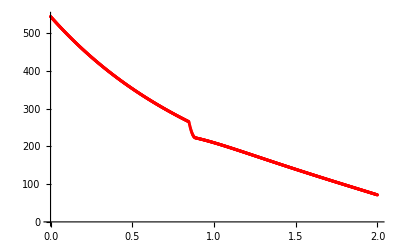

```mathematica
plotEntalpiaMPF3=ListPlot[tablicaEntalpiaMPF3,PlotStyle->Red]
```

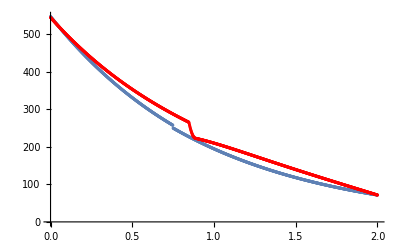

```mathematica
Show[plotEntalpiaDokladna3,plotEntalpiaMPF3]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv

### alfa = 1/2, t=2

#### temperatury

```mathematica
str4=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList4=ReadList[str4]
```

{2.71025,2.70497,2.6997,2.69444,2.68919,2.68395,2.67873,2.67351,2.66831,2.66312,2.65794,2.65278,2.64762,2.64248,2.63735,2.63222,2.62711,2.62202,2.61693,2.61185,2.60679,2.60173,2.59669,2.59166,2.58664,2.58163,2.57664,2.57165,2.56667,2.56171,2.55676,2.55181,2.54688,2.54196,2.53705,2.53215,2.52727,2.52239,2.51752,2.51267,2.50782,2.50299,2.49817,2.49335,2.48855,2.48376,2.47898,2.47421,2.46945,2.4647,2.45996,2.45523,2.45052,2.44581,2.44111,2.43643,2.43175,2.42708,2.42243,2.41778,2.41315,2.40852,2.40391,2.3993,2.39471,2.39012,2.38555,2.38098,2.37643,2.37189,2.36735,2.36283,2.35831,2.35381,2.34931,2.34483,2.34035,2.33589,2.33143,2.32699,2.32255,2.31812,2.31371,2.3093,2.3049,2.30052,2.29614,2.29177,2.28741,2.28306,2.27872,2.27439,2.27007,2.26576,2.26146,2.25716,2.25288,2.24861,2.24434,2.24009,2.23584,2.2316,2.22738,2.22316,2.21895,2.21475,2.21056,2.20638,2.2022,2.19804,2.19389,2.18974,2.1856,2.18148,2.17736,2.17325,2.16915,2.16505,2.16097,2.1569,2.15283,2.14877,2.14473,2.14069,2.13666,2.13264,2.12862,2.12462,2.12062,2.11664,2.11266,2.10869,2.10473,2.10077,2.09683,2.0929,2.08897,2.08505,2.08114,2.07724,2.07334,2.06946,2.06558,2.06171,2.05785,2.054,2.05016,2.04632,2.0425,2.03868,2.03487,2.03107,2.02727,2.02349,2.01971,2.01594,2.01218,2.00842,2.00468,2.00094,1.99721,1.99349,1.98977,1.98607,1.98237,1.97868,1.975,1.97132,1.96766,1.964,1.96035,1.95671,1.95307,1.94944,1.94582,1.94221,1.93861,1.93501,1.93142,1.92784,1.92427,1.9207,1.91714,1.91359,1.91005,1.90651,1.90298,1.89946,1.89595,1.89244,1.88894,1.88545,1.88197,1.87849,1.87502,1.87156,1.86811,1.86466,1.86122,1.85779,1.85436,1.85094,1.84753,1.84413,1.84073,1.83734,1.83396,1.83058,1.82722,1.82386,1.8205,1.81715,1.81381,1.81048,1.80716,1.80384,1.80052,1.79722,1.79392,1.79063,1.78735,1.78407,1.7808,1.77753,1.77428,1.77103,1.76778,1.76455,1.76132,1.75809,1.75488,1.75167,1.74847,1.74527,1.74208,1.7389,1.73572,1.73255,1.72939,1.72623,1.72308,1.71994,1.7168,1.71367,1.71055,1.70743,1.70432,1.70121,1.69811,1.69502,1.69194,1.68886,1.68578,1.68272,1.67966,1.6766,1.67356,1.67052,1.66748,1.66445,1.66143,1.65841,1.6554,1.6524,1.6494,1.64641,1.64343,1.64045,1.63747,1.63451,1.63155,1.62859,1.62564,1.6227,1.61976,1.61683,1.61391,1.61099,1.60808,1.60517,1.60227,1.59938,1.59649,1.5936,1.59073,1.58785,1.58499,1.58213,1.57928,1.57643,1.57358,1.57075,1.56792,1.56509,1.56227,1.55946,1.55665,1.55385,1.55105,1.54826,1.54548,1.5427,1.53992,1.53715,1.53439,1.53163,1.52888,1.52614,1.5234,1.52066,1.51793,1.51521,1.51249,1.50977,1.50707,1.50436,1.50167,1.49898,1.49629,1.49361,1.49093,1.48826,1.4856,1.48294,1.48028,1.47764,1.47499,1.47235,1.46972,1.46709,1.46447,1.46185,1.45924,1.45663,1.45403,1.45144,1.44884,1.44626,1.44368,1.4411,1.43853,1.43596,1.4334,1.43085,1.4283,1.42575,1.42321,1.42067,1.41814,1.41562,1.4131,1.41058,1.40807,1.40556,1.40306,1.40057,1.39808,1.39559,1.39311,1.39063,1.38816,1.38569,1.38323,1.38077,1.37832,1.37587,1.37343,1.37099,1.36856,1.36613,1.36371,1.36129,1.35887,1.35646,1.35406,1.35166,1.34926,1.34687,1.34448,1.3421,1.33973,1.33735,1.33498,1.33262,1.33026,1.32791,1.32556,1.32321,1.32087,1.31853,1.3162,1.31388,1.31155,1.30923,1.30692,1.30461,1.3023,1.3,1.29771,1.29542,1.29313,1.29084,1.28857,1.28629,1.28402,1.28175,1.27949,1.27724,1.27498,1.27273,1.27049,1.26825,1.26601,1.26378,1.26155,1.25933,1.25711,1.2549,1.25268,1.25048,1.24828,1.24608,1.24388,1.24169,1.23951,1.23732,1.23515,1.23297,1.2308,1.22864,1.22648,1.22432,1.22217,1.22002,1.21787,1.21573,1.21359,1.21146,1.20933,1.2072,1.20508,1.20296,1.20085,1.19874,1.19663,1.19453,1.19243,1.19034,1.18825,1.18616,1.18408,1.182,1.17993,1.17786,1.17579,1.17373,1.17167,1.16961,1.16756,1.16551,1.16346,1.16142,1.15939,1.15735,1.15532,1.1533,1.15127,1.14926,1.14724,1.14523,1.14322,1.14122,1.13922,1.13722,1.13523,1.13324,1.13125,1.12927,1.12729,1.12531,1.12334,1.12137,1.11941,1.11745,1.11549,1.11354,1.11159,1.10964,1.1077,1.10576,1.10382,1.10189,1.09996,1.09803,1.09611,1.09419,1.09227,1.09036,1.08845,1.08655,1.08465,1.08275,1.08085,1.07896,1.07707,1.07519,1.0733,1.07142,1.06955,1.06768,1.06581,1.06394,1.06208,1.06022,1.05837,1.05652,1.05467,1.05282,1.05098,1.04914,1.04731,1.04548,1.04365,1.04182,1.04,1.03818,1.03637,1.03456,1.02935,1.01274,1,1,0.992538,0.978961,0.966427,0.954688,0.943908,0.934,0.924969,0.916887,0.909599,0.903339,0.897791,0.893347,0.889536,0.886904,0.884826,0.884003,0.883174,0.882338,0.881496,0.880648,0.879794,0.878934,0.878068,0.877196,0.876318,0.875434,0.874544,0.873649,0.872749,0.871843,0.870931,0.870015,0.869093,0.868165,0.867233,0.866296,0.865353,0.864406,0.863454,0.862497,0.861536,0.860569,0.859598,0.858623,0.857643,0.856659,0.85567,0.854677,0.85368,0.852679,0.851673,0.850664,0.84965,0.848633,0.847611,0.846586,0.845557,0.844524,0.843488,0.842448,0.841404,0.840357,0.839307,0.838253,0.837195,0.836135,0.835071,0.834004,0.832933,0.83186,0.830783,0.829703,0.828621,0.827535,0.826447,0.825356,0.824261,0.823165,0.822065,0.820963,0.819858,0.81875,0.81764,0.816527,0.815412,0.814295,0.813175,0.812053,0.810928,0.809801,0.808672,0.807541,0.806407,0.805271,0.804134,0.802994,0.801852,0.800708,0.799562,0.798415,0.797265,0.796113,0.79496,0.793805,0.792648,0.79149,0.790329,0.789167,0.788004,0.786839,0.785672,0.784503,0.783334,0.782162,0.78099,0.779815,0.77864,0.777463,0.776285,0.775105,0.773924,0.772742,0.771558,0.770374,0.769188,0.768001,0.766813,0.765624,0.764433,0.763242,0.76205,0.760856,0.759662,0.758467,0.75727,0.756073,0.754875,0.753676,0.752476,0.751275,0.750074,0.748872,0.747669,0.746465,0.74526,0.744055,0.742849,0.741643,0.740436,0.739228,0.738019,0.73681,0.735601,0.73439,0.73318,0.731969,0.730757,0.729545,0.728332,0.727119,0.725905,0.724692,0.723477,0.722263,0.721047,0.719832,0.718616,0.7174,0.716184,0.714967,0.71375,0.712533,0.711316,0.710098,0.70888,0.707662,0.706444,0.705225,0.704007,0.702788,0.701569,0.70035,0.699131,0.697912,0.696693,0.695473,0.694254,0.693035,0.691815,0.690596,0.689376,0.688157,0.686937,0.685718,0.684498,0.683279,0.68206,0.680841,0.679621,0.678402,0.677183,0.675965,0.674746,0.673527,0.672309,0.67109,0.669872,0.668654,0.667436,0.666219,0.665001,0.663784,0.662567,0.66135,0.660134,0.658917,0.657701,0.656485,0.65527,0.654054,0.652839,0.651625,0.65041,0.649196,0.647982,0.646769,0.645555,0.644342,0.64313,0.641918,0.640706,0.639494,0.638283,0.637072,0.635862,0.634651,0.633442,0.632232,0.631023,0.629815,0.628607,0.627399,0.626192,0.624985,0.623779,0.622573,0.621367,0.620162,0.618957,0.617753,0.616549,0.615346,0.614143,0.612941,0.611739,0.610537,0.609336,0.608136,0.606936,0.605736,0.604537,0.603339,0.602141,0.600944,0.599747,0.59855,0.597354,0.596159,0.594964,0.59377,0.592576,0.591383,0.59019,0.588998,0.587806,0.586615,0.585425,0.584235,0.583045,0.581857,0.580668,0.579481,0.578293,0.577107,0.575921,0.574735,0.573551,0.572366,0.571183,0.57,0.568817,0.567635,0.566454,0.565273,0.564093,0.562913,0.561734,0.560556,0.559378,0.558201,0.557025,0.555849,0.554673,0.553499,0.552325,0.551151,0.549978,0.548806,0.547634,0.546463,0.545293,0.544123,0.542954,0.541785,0.540617,0.53945,0.538283,0.537117,0.535951,0.534787,0.533622,0.532459,0.531296,0.530133,0.528972,0.52781,0.52665,0.52549,0.524331,0.523172,0.522014,0.520857,0.5197,0.518544,0.517389,0.516234,0.515079,0.513926,0.512773,0.511621,0.510469,0.509318,0.508167,0.507018,0.505868,0.50472,0.503572,0.502424,0.501278,0.500132,0.498986,0.497841,0.496697,0.495554,0.494411,0.493268,0.492127,0.490985,0.489845,0.488705,0.487566,0.486427,0.485289,0.484152,0.483015,0.481879,0.480743,0.479608,0.478474,0.47734,0.476207,0.475075,0.473943,0.472812,0.471681,0.470551,0.469422,0.468293,0.467164,0.466037,0.46491,0.463783,0.462657,0.461532,0.460407,0.459283,0.45816,0.457037,0.455915,0.454793,0.453672,0.452551,0.451431,0.450312,0.449193,0.448075,0.446957,0.44584,0.444723,0.443607,0.442492,0.441377,0.440263,0.439149,0.438036,0.436924,0.435812,0.4347,0.433589,0.432479,0.431369,0.43026,0.429151,0.428043,0.426936,0.425829,0.424722,0.423616,0.422511,0.421406,0.420302,0.419198,0.418095,0.416992,0.41589,0.414788,0.413687,0.412586,0.411486,0.410386,0.409287,0.408189,0.407091,0.405993,0.404896,0.403799,0.402703,0.401608,0.400513,0.399418,0.398324,0.39723,0.396137,0.395045,0.393952,0.392861,0.39177,0.390679,0.389589,0.388499,0.38741,0.386321,0.385232,0.384144,0.383057,0.38197,0.380883,0.379797,0.378712,0.377627,0.376542,0.375457,0.374374,0.37329,0.372207,0.371125,0.370042,0.368961,0.367879}

```mathematica
strList4={2.71025387,2.7049702063,2.6996983417,2.6944382404,2.6891898684,2.6839531972,2.6787281982,2.673514843,2.6683131033,2.6631229507,2.6579443572,2.6527772945,2.6476217347,2.6424776496,2.6373450115,2.6322237924,2.6271139645,2.6220155002,2.6169283718,2.6118525501,2.6067880073,2.6017347161,2.5966926492,2.5916617791,2.5866420786,2.5816335207,2.5766360783,2.5716497242,2.5666744317,2.5617101737,2.5567569236,2.5518146545,2.5468833379,2.5419629473,2.537053456,2.5321548375,2.5272670653,2.522390113,2.5175239545,2.5126685634,2.5078239137,2.5029899793,2.4981667341,2.4933541505,2.4885522025,2.4837608642,2.4789801099,2.4742099137,2.46945025,2.4647010933,2.459962418,2.4552341988,2.4505164085,2.4458090218,2.4411120134,2.4364253581,2.4317490307,2.4270830061,2.4224272593,2.4177817653,2.4131464994,2.4085214348,2.403906547,2.3993018111,2.3947072026,2.3901226968,2.3855482691,2.3809838952,2.3764295489,2.3718852059,2.367350842,2.3628264329,2.3583119545,2.3538073826,2.3493126932,2.3448278623,2.3403528644,2.3358876756,2.331432272,2.32698663,2.3225507259,2.3181245361,2.3137080353,2.3093012,2.3049040068,2.3005164323,2.2961384532,2.2917700462,2.2874111881,2.2830618541,2.2787220211,2.2743916661,2.270070766,2.265759298,2.2614572391,2.2571645651,2.2528812531,2.2486072803,2.2443426242,2.2400872621,2.2358411716,2.2316043286,2.2273767106,2.2231582953,2.2189490604,2.2147489835,2.2105580411,2.2063762108,2.2022034707,2.1980397985,2.1938851725,2.1897395706,2.1856029695,2.1814753473,2.1773566822,2.1732469525,2.1691461366,2.1650542113,2.1609711551,2.1568969465,2.152831564,2.1487749862,2.1447271903,2.140688155,2.136657859,2.1326362812,2.1286234004,2.1246191941,2.1206236412,2.1166367207,2.1126584117,2.1086886934,2.1047275435,2.1007749411,2.0968308655,2.0928952961,2.0889682108,2.0850495891,2.0811394103,2.077237654,2.0733442999,2.0694593261,2.0655827123,2.0617144382,2.0578544835,2.0540028268,2.0501594478,2.0463243266,2.042497443,2.0386787757,2.0348683047,2.0310660103,2.0272718725,2.0234858702,2.0197079836,2.0159381931,2.0121764791,2.0084228205,2.0046771978,2.0009395915,1.9972099823,1.9934883493,1.9897746731,1.9860689346,1.9823711144,1.978681192,1.9749991481,1.9713249638,1.9676586199,1.9640000961,1.9603493734,1.9567064329,1.9530712557,1.9494438217,1.9458241119,1.9422121078,1.9386077893,1.9350111377,1.9314221344,1.9278407609,1.9242669974,1.9207008253,1.9171422263,1.9135911821,1.9100476729,1.9065116805,1.9029831867,1.8994621718,1.8959486178,1.8924425067,1.8889438203,1.8854525393,1.8819686457,1.8784921218,1.8750229481,1.8715611069,1.8681065804,1.8646593496,1.8612193967,1.8577867041,1.8543612542,1.8509430282,1.8475320085,1.8441281776,1.8407315167,1.8373420086,1.8339596358,1.8305843796,1.827216223,1.8238551485,1.8205011378,1.8171541737,1.8138142391,1.8104813157,1.8071553864,1.8038364343,1.8005244426,1.797219393,1.7939212686,1.7906300527,1.7873457273,1.7840682755,1.7807976808,1.7775339252,1.7742769921,1.7710268651,1.7677835262,1.764546959,1.7613171471,1.7580940728,1.7548777198,1.7516680718,1.7484651112,1.7452688218,1.7420791875,1.7388961907,1.7357198155,1.7325500443,1.7293868612,1.7262302503,1.7230801943,1.7199366773,1.7167996834,1.7136691956,1.7105451981,1.7074276751,1.7043166097,1.7012119861,1.6981137888,1.6950220009,1.6919366069,1.6888575912,1.6857849371,1.6827186293,1.6796586508,1.6766049865,1.6735576211,1.6705165379,1.6674817217,1.6644531574,1.6614308285,1.6584147199,1.6554048165,1.652401102,1.6494035613,1.6464121783,1.6434269379,1.6404478253,1.6374748243,1.6345079201,1.631547098,1.6285923419,1.6256436371,1.6227009677,1.6197643189,1.6168336763,1.6139090239,1.6109903473,1.608077632,1.6051708622,1.6022700235,1.5993751002,1.596486078,1.5936029426,1.5907256785,1.5878542714,1.5849887057,1.5821289675,1.5792750424,1.5764269152,1.5735845718,1.5707479983,1.5679171792,1.5650921007,1.5622727475,1.5594591058,1.5566511617,1.5538489002,1.5510523075,1.5482613684,1.5454760694,1.5426963968,1.5399223355,1.5371538722,1.5343909917,1.5316336807,1.5288819257,1.5261357118,1.5233950257,1.5206598527,1.5179301793,1.515205991,1.5124872745,1.5097740165,1.5070662025,1.5043638193,1.5016668524,1.4989752887,1.4962891152,1.4936083175,1.4909328824,1.4882627959,1.4855980447,1.4829386162,1.4802844961,1.4776356714,1.4749921281,1.4723538534,1.4697208331,1.4670930547,1.4644705053,1.461853171,1.4592410391,1.4566340959,1.4540323285,1.4514357234,1.4488442678,1.4462579494,1.4436767544,1.4411006704,1.4385296836,1.4359637819,1.4334029514,1.4308471799,1.4282964553,1.4257507639,1.4232100935,1.4206744308,1.4181437634,1.4156180781,1.4130973628,1.4105816054,1.4080707926,1.4055649124,1.4030639516,1.4005678982,1.3980767391,1.3955904624,1.3931090563,1.3906325076,1.3881608046,1.3856939343,1.3832318849,1.3807746434,1.3783221983,1.3758745365,1.3734316464,1.3709935167,1.3685601342,1.3661314877,1.3637075643,1.3612883525,1.3588738396,1.3564640143,1.3540588639,1.351658377,1.3492625423,1.3468713474,1.3444847809,1.3421028302,1.3397254844,1.3373527308,1.3349845583,1.3326209545,1.3302619084,1.327907409,1.3255574438,1.323212002,1.3208710712,1.3185346406,1.3162026979,1.3138752322,1.3115522314,1.3092336846,1.3069195799,1.3046099063,1.3023046532,1.3000038086,1.2977073619,1.2954153009,1.2931276152,1.2908442927,1.288565323,1.2862906942,1.2840203958,1.2817544159,1.2794927441,1.2772353688,1.2749822794,1.2727334656,1.2704889158,1.2682486196,1.2660125654,1.263780743,1.2615531408,1.2593297486,1.2571105549,1.2548955495,1.252684721,1.2504780593,1.248275553,1.246077192,1.2438829664,1.2416928648,1.2395068773,1.2373249925,1.2351472007,1.2329734905,1.2308038521,1.2286382744,1.2264767476,1.2243192605,1.2221658034,1.2200163653,1.2178709365,1.2157295059,1.2135920639,1.211458601,1.2093291062,1.2072035699,1.2050819814,1.2029643311,1.2008506081,1.1987408031,1.1966349053,1.1945329052,1.1924347923,1.1903405571,1.1882501891,1.1861636788,1.1840810158,1.1820021909,1.1799271934,1.1778560142,1.1757886467,1.1737250778,1.1716652987,1.1696092988,1.1675570693,1.1655085997,1.1634638811,1.1614229032,1.1593856572,1.1573521328,1.1553223211,1.1532962122,1.1512737971,1.1492550658,1.1472400096,1.1452286185,1.1432208839,1.1412167958,1.1392163457,1.1372195236,1.1352263212,1.1332367306,1.1312507415,1.1292683505,1.1272895428,1.1253143194,1.1233426615,1.1213745611,1.1194100084,1.1174489956,1.1154915131,1.113537553,1.1115871061,1.1096401644,1.1076967188,1.1057567616,1.1038202836,1.1018872775,1.0999577341,1.0980316462,1.0961090049,1.094189803,1.092274032,1.0903616849,1.0884527533,1.0865472305,1.0846451083,1.0827463804,1.0808510397,1.0789590793,1.0770704959,1.0751852799,1.0733034314,1.0714249383,1.0695498045,1.0676780152,1.0658095785,1.0639444772,1.0620827236,1.0602242986,1.0583692007,1.0565174278,1.0546689806,1.0528238594,1.0509820681,1.0491436109,1.047308497,1.0454767371,1.04364835,1.0418233585,1.0400018012,1.0381837303,1.0363692394,1.0345585939,1.029350378,1.0127409791,1,1,0.9925384616,0.9789608629,0.9664274381,0.9546876967,0.9439079056,0.9339999505,0.924968635,0.9168869068,0.9095994867,0.903338925,0.8977913033,0.8933473311,0.8895358395,0.8869043415,0.8848257017,0.8840029916,0.883173823,0.8823382771,0.8814964344,0.8806483743,0.8797941757,0.8789339165,0.8780676739,0.8771955242,0.876317543,0.8754338051,0.8745443846,0.8736493547,0.872748788,0.8718427563,0.8709313305,0.8700145811,0.8690925776,0.8681653889,0.8672330831,0.8662957278,0.8653533896,0.8644061348,0.8634540286,0.8624971358,0.8615355205,0.860569246,0.8595983751,0.8586229698,0.8576430916,0.8566588013,0.8556701591,0.8546772244,0.8536800563,0.852678713,0.8516732522,0.8506637311,0.8496502061,0.8486327331,0.8476113675,0.846586164,0.8455571769,0.8445244596,0.8434880653,0.8424480464,0.8414044549,0.8403573422,0.8393067591,0.8382527559,0.8371953825,0.836134688,0.8350707213,0.8340035305,0.8329331633,0.831859667,0.8307830883,0.8297034733,0.8286208679,0.8275353172,0.826446866,0.8253555586,0.8242614387,0.8231645498,0.8220649346,0.8209626356,0.8198576949,0.8187501538,0.8176400534,0.8165274344,0.815412337,0.8142948009,0.8131748655,0.8120525696,0.8109279518,0.8098010501,0.8086719022,0.8075405453,0.8064070162,0.8052713515,0.8041335872,0.8029937588,0.8018519018,0.800708051,0.7995622409,0.7984145056,0.7972648788,0.7961133941,0.7949600843,0.7938049821,0.7926481199,0.7914895295,0.7903292426,0.7891672905,0.7880037039,0.7868385135,0.7856717494,0.7845034416,0.7833336196,0.7821623126,0.7809895495,0.7798153589,0.7786397691,0.7774628079,0.776284503,0.7751048817,0.773923971,0.7727417977,0.771558388,0.7703737682,0.769187964,0.7680010009,0.7668129043,0.7656236989,0.7644334095,0.7632420605,0.7620496759,0.7608562795,0.759661895,0.7584665456,0.7572702543,0.7560730438,0.7548749367,0.7536759551,0.7524761211,0.7512754563,0.7500739823,0.7488717201,0.7476686909,0.7464649153,0.7452604137,0.7440552065,0.7428493137,0.7416427549,0.7404355497,0.7392277175,0.7380192773,0.736810248,0.7356006482,0.7343904962,0.7331798103,0.7319686085,0.7307569084,0.7295447277,0.7283320836,0.7271189933,0.7259054737,0.7246915415,0.7234772132,0.7222625052,0.7210474334,0.7198320139,0.7186162623,0.7174001941,0.7161838248,0.7149671694,0.7137502429,0.71253306,0.7113156354,0.7100979835,0.7088801184,0.7076620543,0.7064438049,0.7052253841,0.7040068053,0.7027880818,0.7015692269,0.7003502536,0.6991311746,0.6979120028,0.6966927506,0.6954734304,0.6942540544,0.6930346347,0.691815183,0.6905957112,0.6893762309,0.6881567534,0.6869372901,0.685717852,0.6844984502,0.6832790955,0.6820597986,0.68084057,0.6796214202,0.6784023594,0.6771833978,0.6759645452,0.6747458117,0.6735272069,0.6723087404,0.6710904217,0.6698722601,0.6686542648,0.6674364448,0.6662188092,0.6650013666,0.663784126,0.6625670957,0.6613502842,0.6601337,0.6589173511,0.6577012458,0.6564853919,0.6552697973,0.6540544698,0.652839417,0.6516246465,0.6504101656,0.6491959816,0.6479821018,0.6467685332,0.6455552828,0.6443423575,0.6431297641,0.6419175092,0.6407055993,0.639494041,0.6382828406,0.6370720043,0.6358615384,0.6346514489,0.6334417418,0.632232423,0.6310234981,0.629814973,0.6286068532,0.6273991443,0.6261918516,0.6249849804,0.6237785361,0.6225725237,0.6213669484,0.6201618151,0.6189571286,0.6177528938,0.6165491155,0.6153457983,0.6141429466,0.6129405651,0.6117386581,0.6105372299,0.6093362848,0.6081358269,0.6069358603,0.6057363891,0.6045374172,0.6033389484,0.6021409865,0.6009435352,0.5997465983,0.5985501792,0.5973542815,0.5961589085,0.5949640638,0.5937697505,0.5925759718,0.591382731,0.5901900311,0.5889978752,0.5878062663,0.5866152071,0.5854247006,0.5842347495,0.5830453566,0.5818565244,0.5806682556,0.5794805527,0.5782934182,0.5771068545,0.5759208638,0.5747354486,0.573550611,0.5723663532,0.5711826774,0.5699995856,0.5688170797,0.5676351619,0.5664538339,0.5652730976,0.5640929548,0.5629134072,0.5617344566,0.5605561046,0.5593783527,0.5582012026,0.5570246556,0.5558487132,0.5546733769,0.5534986479,0.5523245276,0.5511510172,0.5499781179,0.5488058308,0.5476341571,0.5464630979,0.5452926541,0.5441228267,0.5429536167,0.5417850249,0.5406170522,0.5394496994,0.5382829673,0.5371168565,0.5359513678,0.5347865017,0.5336222589,0.53245864,0.5312956454,0.5301332757,0.5289715312,0.5278104124,0.5266499196,0.5254900531,0.5243308133,0.5231722005,0.5220142147,0.5208568562,0.5197001251,0.5185440216,0.5173885457,0.5162336974,0.5150794768,0.5139258839,0.5127729185,0.5116205805,0.5104688699,0.5093177865,0.50816733,0.5070175003,0.5058682971,0.5047197201,0.503571769,0.5024244435,0.5012777431,0.5001316674,0.498986216,0.4978413885,0.4966971844,0.495553603,0.4944106439,0.4932683065,0.4921265901,0.4909854942,0.489845018,0.4887051609,0.4875659221,0.4864273009,0.4852892965,0.4841519082,0.483015135,0.4818789762,0.4807434308,0.479608498,0.4784741768,0.4773404663,0.4762073655,0.4750748735,0.4739429891,0.4728117113,0.4716810391,0.4705509714,0.469421507,0.4682926449,0.4671643837,0.4660367225,0.4649096599,0.4637831947,0.4626573257,0.4615320516,0.4604073712,0.459283283,0.4581597857,0.4570368781,0.4559145587,0.4547928261,0.4536716789,0.4525511157,0.451431135,0.4503117353,0.4491929152,0.448074673,0.4469570074,0.4458399166,0.4447233992,0.4436074536,0.4424920781,0.4413772711,0.4402630309,0.439149356,0.4380362445,0.4369236949,0.4358117053,0.4347002741,0.4335893995,0.4324790797,0.4313693129,0.4302600973,0.4291514311,0.4280433124,0.4269357395,0.4258287103,0.4247222231,0.4236162759,0.4225108667,0.4214059938,0.420301655,0.4191978484,0.418094572,0.4169918239,0.4158896019,0.4147879042,0.4136867285,0.4125860729,0.4114859353,0.4103863135,0.4092872055,0.4081886091,0.4070905222,0.4059929426,0.4048958681,0.4037992967,0.402703226,0.4016076538,0.400512578,0.3994179962,0.3983239063,0.3972303058,0.3961371927,0.3950445644,0.3939524188,0.3928607535,0.3917695661,0.3906788544,0.3895886158,0.3884988481,0.3874095488,0.3863207154,0.3852323457,0.3841444371,0.3830569872,0.3819699935,0.3808834535,0.3797973648,0.3787117248,0.3776265309,0.3765417807,0.3754574716,0.374373601,0.3732901664,0.3722071651,0.3711245946,0.3700424522,0.3689607352,0.3678794412};
```

```mathematica
tablicaTemperaturMPF4=Table[{i*0.002,strList4[[i+1]]},{i,0,1000}];
```

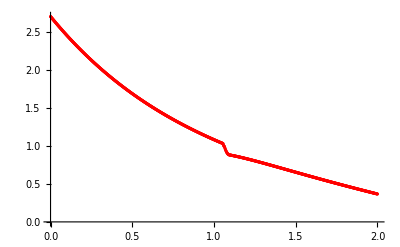

```mathematica
plotTemperaturyMPF4=ListPlot[tablicaTemperaturMPF4,PlotStyle->Red]
```

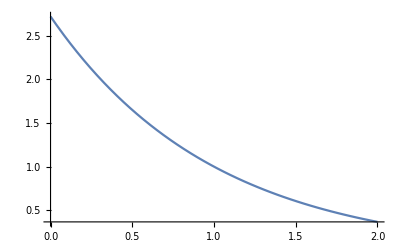

```mathematica
plotTemperaturyDokladne4=Plot[u1[x,2],{x,0,2}]
```

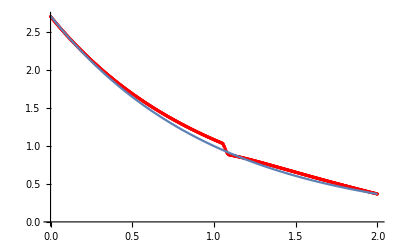

```mathematica
Show[plotTemperaturyMPF4,plotTemperaturyDokladne4]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(√Pi*(lambdaL-lambdaS))/(2*aL*√t);
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t],temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna4=Table[{i*0.002,entalpia[u1[i*0.002,2],2]},{i,0,1000}];
```

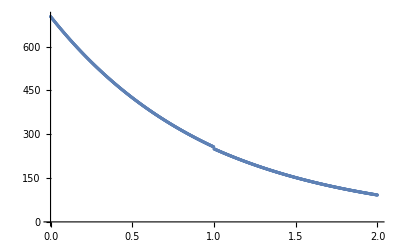

```mathematica
plotEntalpiaDokladna4=ListPlot[tablicaEntalpiaDokladna4]
```

```mathematica
strE4=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE4=ReadList[strE4]
```

{700.933,699.559,698.188,696.821,695.456,694.094,692.736,691.38,690.028,688.679,687.332,685.989,684.648,683.311,681.976,680.645,679.316,677.991,676.668,675.348,674.031,672.718,671.407,670.099,668.794,667.491,666.192,664.895,663.602,662.311,661.023,659.738,658.456,657.177,655.9,654.627,653.356,652.088,650.823,649.56,648.301,647.044,645.79,644.539,643.29,642.044,640.801,639.561,638.324,637.089,635.857,634.627,633.401,632.177,630.956,629.737,628.521,627.308,626.098,624.89,623.685,622.482,621.282,620.085,618.89,617.698,616.509,615.322,614.138,612.957,611.778,610.601,609.428,608.256,607.088,605.922,604.758,603.597,602.439,601.283,600.13,598.979,597.831,596.685,595.542,594.401,593.263,592.127,590.993,589.863,588.734,587.608,586.485,585.364,584.245,583.129,582.016,580.904,579.796,578.689,577.585,576.484,575.385,574.288,573.193,572.101,571.012,569.924,568.839,567.757,566.677,565.599,564.523,563.45,562.379,561.311,560.245,559.181,558.119,557.06,556.003,554.948,553.896,552.845,551.798,550.752,549.709,548.668,547.629,546.592,545.558,544.526,543.496,542.468,541.443,540.419,539.398,538.379,537.363,536.348,535.336,534.326,533.318,532.312,531.309,530.307,529.308,528.311,527.316,526.323,525.332,524.344,523.357,522.373,521.391,520.411,519.432,518.457,517.483,516.511,515.541,514.574,513.608,512.644,511.683,510.724,509.766,508.811,507.858,506.907,505.957,505.01,504.065,503.122,502.181,501.242,500.305,499.369,498.436,497.505,496.576,495.649,494.724,493.8,492.879,491.96,491.042,490.127,489.213,488.302,487.392,486.484,485.578,484.675,483.773,482.872,481.974,481.078,480.184,479.291,478.4,477.512,476.625,475.74,474.857,473.975,473.096,472.219,471.343,470.469,469.597,468.727,467.858,466.992,466.127,465.264,464.403,463.544,462.686,461.83,460.976,460.124,459.274,458.425,457.579,456.734,455.89,455.049,454.209,453.371,452.535,451.7,450.867,450.036,449.207,448.38,447.554,446.73,445.907,445.086,444.267,443.45,442.634,441.821,441.008,440.198,439.389,438.582,437.776,436.972,436.17,435.37,434.571,433.773,432.978,432.184,431.392,430.601,429.812,429.024,428.239,427.454,426.672,425.891,425.111,424.334,423.558,422.783,422.01,421.239,420.469,419.701,418.934,418.169,417.405,416.643,415.883,415.124,414.367,413.611,412.857,412.104,411.353,410.603,409.855,409.109,408.364,407.62,406.878,406.138,405.399,404.661,403.925,403.191,402.457,401.726,400.996,400.267,399.54,398.815,398.09,397.368,396.646,395.927,395.208,394.491,393.776,393.062,392.349,391.638,390.928,390.22,389.513,388.808,388.104,387.401,386.7,386.,385.302,384.605,383.909,383.215,382.522,381.831,381.141,380.452,379.765,379.079,378.394,377.711,377.029,376.348,375.669,374.991,374.315,373.64,372.966,372.294,371.623,370.953,370.284,369.617,368.951,368.287,367.624,366.962,366.301,365.642,364.984,364.327,363.672,363.018,362.365,361.713,361.063,360.414,359.767,359.12,358.475,357.831,357.188,356.547,355.907,355.268,354.63,353.994,353.359,352.725,352.092,351.461,350.831,350.202,349.574,348.947,348.322,347.698,347.075,346.453,345.833,345.213,344.595,343.978,343.363,342.748,342.135,341.522,340.912,340.302,339.693,339.086,338.479,337.874,337.27,336.667,336.066,335.465,334.866,334.268,333.67,333.075,332.48,331.886,331.294,330.702,330.112,329.523,328.935,328.348,327.762,327.177,326.594,326.011,325.43,324.85,324.27,323.692,323.115,322.539,321.965,321.391,320.818,320.247,319.676,319.107,318.538,317.971,317.405,316.84,316.276,315.713,315.151,314.59,314.03,313.471,312.913,312.356,311.801,311.246,310.692,310.139,309.588,309.037,308.488,307.939,307.392,306.845,306.3,305.755,305.212,304.669,304.128,303.587,303.048,302.509,301.972,301.435,300.9,300.365,299.831,299.299,298.767,298.237,297.707,297.178,296.65,296.124,295.598,295.073,294.549,294.026,293.504,292.983,292.463,291.944,291.425,290.908,290.392,289.876,289.362,288.848,288.336,287.824,287.313,286.803,286.294,285.786,285.279,284.773,284.268,283.763,283.26,282.757,282.256,281.755,281.255,280.756,280.258,279.761,279.264,278.769,278.274,277.781,277.288,276.796,276.305,275.815,275.325,274.837,274.35,273.863,273.377,272.892,272.408,271.925,271.443,270.961,270.481,270.001,269.522,269.044,268.567,268.091,267.615,267.141,266.667,266.194,265.723,265.252,263.898,259.579,255.563,251.708,248.135,244.74,241.607,238.672,235.977,233.5,231.242,229.222,227.4,225.835,224.448,223.337,222.384,221.726,221.206,221.001,220.793,220.585,220.374,220.162,219.949,219.733,219.517,219.299,219.079,218.858,218.636,218.412,218.187,217.961,217.733,217.504,217.273,217.041,216.808,216.574,216.338,216.102,215.864,215.624,215.384,215.142,214.9,214.656,214.411,214.165,213.918,213.669,213.42,213.17,212.918,212.666,212.413,212.158,211.903,211.647,211.389,211.131,210.872,210.612,210.351,210.089,209.827,209.563,209.299,209.034,208.768,208.501,208.233,207.965,207.696,207.426,207.155,206.884,206.612,206.339,206.065,205.791,205.516,205.241,204.964,204.688,204.41,204.132,203.853,203.574,203.294,203.013,202.732,202.45,202.168,201.885,201.602,201.318,201.033,200.748,200.463,200.177,199.891,199.604,199.316,199.028,198.74,198.451,198.162,197.872,197.582,197.292,197.001,196.71,196.418,196.126,195.833,195.541,195.247,194.954,194.66,194.366,194.071,193.776,193.481,193.185,192.89,192.593,192.297,192.,191.703,191.406,191.108,190.811,190.512,190.214,189.915,189.617,189.318,189.018,188.719,188.419,188.119,187.819,187.518,187.218,186.917,186.616,186.315,186.014,185.712,185.411,185.109,184.807,184.505,184.203,183.9,183.598,183.295,182.992,182.689,182.386,182.083,181.78,181.476,181.173,180.869,180.566,180.262,179.958,179.654,179.35,179.046,178.742,178.438,178.133,177.829,177.524,177.22,176.916,176.611,176.306,176.002,175.697,175.392,175.088,174.783,174.478,174.173,173.868,173.564,173.259,172.954,172.649,172.344,172.039,171.734,171.429,171.125,170.82,170.515,170.21,169.905,169.601,169.296,168.991,168.686,168.382,168.077,167.773,167.468,167.164,166.859,166.555,166.25,165.946,165.642,165.338,165.033,164.729,164.425,164.121,163.817,163.514,163.21,162.906,162.603,162.299,161.996,161.692,161.389,161.086,160.782,160.479,160.176,159.874,159.571,159.268,158.965,158.663,158.36,158.058,157.756,157.454,157.152,156.85,156.548,156.246,155.945,155.643,155.342,155.04,154.739,154.438,154.137,153.836,153.536,153.235,152.935,152.634,152.334,152.034,151.734,151.434,151.134,150.835,150.535,150.236,149.937,149.638,149.339,149.04,148.741,148.442,148.144,147.846,147.548,147.249,146.952,146.654,146.356,146.059,145.761,145.464,145.167,144.87,144.573,144.277,143.98,143.684,143.388,143.092,142.796,142.5,142.204,141.909,141.613,141.318,141.023,140.728,140.434,140.139,139.845,139.55,139.256,138.962,138.668,138.375,138.081,137.788,137.495,137.201,136.909,136.616,136.323,136.031,135.738,135.446,135.154,134.862,134.571,134.279,133.988,133.697,133.406,133.115,132.824,132.533,132.243,131.953,131.662,131.373,131.083,130.793,130.504,130.214,129.925,129.636,129.347,129.058,128.77,128.481,128.193,127.905,127.617,127.329,127.042,126.754,126.467,126.18,125.893,125.606,125.319,125.033,124.747,124.46,124.174,123.888,123.603,123.317,123.032,122.746,122.461,122.176,121.891,121.607,121.322,121.038,120.754,120.47,120.186,119.902,119.619,119.335,119.052,118.769,118.486,118.203,117.92,117.638,117.355,117.073,116.791,116.509,116.227,115.946,115.664,115.383,115.102,114.821,114.54,114.259,113.979,113.698,113.418,113.138,112.858,112.578,112.298,112.019,111.739,111.46,111.181,110.902,110.623,110.344,110.066,109.787,109.509,109.231,108.953,108.675,108.397,108.12,107.842,107.565,107.288,107.011,106.734,106.457,106.181,105.904,105.628,105.351,105.075,104.799,104.524,104.248,103.972,103.697,103.422,103.147,102.871,102.597,102.322,102.047,101.773,101.498,101.224,100.95,100.676,100.402,100.128,99.8545,99.581,99.3076,99.0343,98.7611,98.4881,98.2152,97.9424,97.6697,97.3972,97.1247,96.8524,96.5802,96.3081,96.0361,95.7642,95.4925,95.2209,94.9493,94.6779,94.4066,94.1354,93.8644,93.5934,93.3225,93.0518,92.7811,92.5106,92.2402,91.9699}

```mathematica
strListE4={700.9325768866,699.5588243192,698.1881395156,696.8205131934,695.4559364831,694.0944019595,692.735902216,691.3804298645,690.0279775356,688.6785378781,687.3321035596,685.9886672659,684.6482217013,683.3107595882,681.9762736676,680.6447566984,679.3162014581,677.990600742,676.6679473638,675.3482337012,674.0314525904,672.7175968854,671.406659467,670.0986332404,668.7935111291,667.4912860739,666.1919510337,664.8954989848,663.6019229214,662.3112158552,661.0233708155,659.7383808489,658.4562385515,657.1769369904,655.9004692501,654.6268284322,653.3560076559,652.0880000703,650.8227988457,649.5603971692,648.3007882454,647.0439652955,645.789921558,644.5386498197,643.2901433377,642.0443953855,640.8013992537,639.5611482498,638.3236356978,637.088854949,635.8567993783,634.6274623772,633.4008369017,632.1769163602,630.9556941776,629.7371637954,628.5213186712,627.3081522795,626.0976581105,624.8898296763,623.6846605178,622.4821437424,621.2822729066,620.0850415832,618.8904433607,617.698471844,616.5091206538,615.3223834269,614.1382533958,612.95672423,611.7777896149,610.6014432515,609.4276788569,608.2564901636,607.08787092,605.9218148898,604.7583154287,603.5973663325,602.4389614128,601.2830944966,600.1297594263,598.9789500597,597.8306598539,596.6848826854,595.5416124587,594.4008430937,593.2625685255,592.1267827043,590.9934795955,589.8626527583,588.7342961772,587.6084038635,586.4849698434,585.3639881582,584.245452864,583.1293576146,582.0156964816,580.9044635609,579.7956529686,578.6892588356,577.5852753074,576.4836961267,575.3845154539,574.2877274702,573.19332638,572.1013064026,571.011661365,569.9243855004,568.8394730563,567.7569183023,566.67671553,565.5988590453,564.523342755,563.4501609785,562.3793080496,561.3107783287,560.2445661933,559.1806656262,558.1190710179,557.0597767729,556.0027773154,554.9480670935,553.8956401626,552.8454909833,551.7976140301,550.752003793,549.7086547901,548.6675611459,547.6287173903,546.5921180668,545.5577577336,544.5256309773,543.4957319888,542.4680553662,541.4425957212,540.4193476818,539.3983055043,538.3794638408,537.3628173573,536.3483607326,535.3360886664,534.325995475,533.3180758778,532.3123246071,531.3087364084,530.3073056563,529.3080271228,528.3108955934,527.3159058662,526.323052366,525.3323299177,524.3437333587,523.3572575396,522.3728969354,521.3906464228,520.4105008911,519.4324552425,518.4565040052,517.4826421041,516.5108644799,515.541166086,514.5735415022,513.6079857024,512.6444936781,511.6830604333,510.723680598,509.7663491957,508.8110612682,507.8578118697,506.9065956788,505.9574077693,505.0102432329,504.0650971734,503.1219643166,502.1808397874,501.2417187266,500.3045959073,499.3694664811,498.4363256242,497.5051685266,496.5759900057,495.6487852639,494.7235495273,493.8002780341,492.8789656451,491.9596076151,491.0421992185,490.1267353599,489.2132113232,488.3016224165,487.3919639616,486.4842309038,485.5784185789,484.674522344,483.7725371866,482.8724584728,481.9742815925,481.0780015741,480.1836138189,479.291113745,478.4004967909,477.5117580228,476.6248928879,475.7398968591,474.8567650415,473.9754929167,473.0960759868,472.2185093955,471.3427886583,470.4689093069,469.5968665226,468.7266558549,467.858272865,466.9917127713,466.1269711568,465.2640436157,464.4029257652,463.5436128563,462.6861005161,461.8303843926,460.9764597718,460.124322314,459.2739676976,458.4253912433,457.5785886441,456.7335556095,455.8902874939,455.0487800228,454.2090289371,453.3710296241,452.5347778417,451.7002693621,450.8674996053,450.036464361,449.2071594333,448.3795802737,447.553722704,446.7295821996,445.9071546035,445.086435769,444.2674212029,443.4501067793,442.6344883832,441.8205615519,441.0083221912,440.1977662167,439.3888891969,438.5816870682,437.7761557772,436.9722909229,436.1700884724,435.3695444031,434.5706543442,433.7734142932,432.977819901,432.1838671839,431.3915521698,430.6008705377,429.8118183356,429.0243916218,428.2385861049,427.4543978628,426.6718229835,425.8908572053,425.1114966357,424.3337370358,423.5575745296,422.7830052545,422.010024997,421.2386299141,420.4688161722,419.7005795871,418.9339163445,418.1688222845,417.4052936073,416.6433265275,415.8829169098,415.124060987,414.3667550028,413.6109948489,412.8567767876,412.1040967347,411.3529509667,410.6033357745,409.8552470968,409.1086812432,408.3636341789,407.6201022242,406.8780817169,406.1375686448,405.398559361,404.6610502316,403.9250372686,403.1905168559,402.457485029,401.7259381852,400.9958727363,400.2672847398,399.5401706251,398.8145264742,398.0903487286,397.3676338456,396.6463779271,395.9265774482,395.2082285355,394.4913276752,393.7758713692,393.0618557641,392.3492773792,391.638132385,390.9284173122,390.2201283551,389.5132620556,388.8078149773,388.1037833337,387.4011636998,386.6999523123,386.0001457577,385.3017406432,384.604733224,383.9091201195,383.2148976079,382.5220623201,381.8306109065,381.1405396628,380.4518452531,379.7645239956,379.0785725659,378.3939873042,377.7107648984,377.0289020577,376.3483951391,375.6692408628,374.9914356078,374.314976106,373.6398587577,372.9660803093,372.2936375259,371.6225268242,370.9527449806,370.2842884328,369.6171539689,368.9513380475,368.2868374724,367.6236490652,366.9617692996,366.3011950088,365.6419226869,364.9839491787,364.3272709985,363.6718850073,363.0177880826,362.3649767538,361.7134479102,361.063198101,360.4142242273,359.7665228579,359.1200909093,358.4749253157,357.8310226599,357.1883798875,356.5469936009,355.9068607575,355.2679779789,354.6303422362,353.9939501678,353.3587987607,352.7248850168,352.09220559,351.460757494,350.8305374011,350.201542337,349.5737689926,348.9472144086,348.3218752908,347.6977486953,347.0748316919,346.4531210026,345.8326137092,345.2133065516,344.5951966234,343.9782806824,343.3625558372,342.74801886,342.1346668746,341.522497019,340.9115060805,340.3016912091,339.6930492094,339.0855772433,338.4792721327,337.8741310533,337.2701508423,336.6673286901,336.0656614479,335.465146321,334.8657805271,334.2675609338,333.6704847708,333.0745489224,332.4797506304,331.8860867955,331.2935546737,330.7021511801,330.1118735853,329.522718818,328.9346841635,328.3477665644,327.7619633203,327.1772717408,326.5936887867,326.01121178,325.4298376973,324.8495638738,324.2703873009,323.6923053283,323.1153149611,322.5394135632,321.9645981534,321.3908661099,320.8182144652,320.2466406117,319.6761419512,319.1067155348,318.5383587769,317.9710687437,317.4048428627,316.8396782149,316.2755722421,315.7125220389,315.1505250615,314.589578418,314.0296795788,313.4708256658,312.9130141637,312.3562422077,311.8005072972,311.2458069403,310.6921382914,310.139498872,309.5878858514,309.0372967645,308.4877287955,307.9391794937,307.3916460573,306.8451260503,306.2996166847,305.7551155395,305.2116198406,304.6691271819,304.1276348033,303.5871403141,303.0476409683,302.5091343903,301.9716188156,301.4350909174,300.8995483424,300.3649883827,299.8314087005,299.2988066031,298.7671797688,298.2365255203,297.7068415524,297.1781252034,296.6503741851,296.1235858516,295.5977579322,295.0728877971,294.5489731938,294.0260115092,293.5040005095,292.9829375986,292.4628205625,291.9436468229,291.4254141863,290.9081206491,290.3917634833,289.8763418092,289.361851817,288.8482937339,288.3356626883,287.8239565596,287.3131728717,286.8033095315,286.2943640865,285.7863344735,285.279218266,284.7730134321,284.2677175748,283.7633286973,283.2598444346,282.7572628288,282.2555815509,281.7547986872,281.2549119486,280.7559194724,280.257819015,279.7606087724,279.2642865533,278.7688506234,278.2742988517,277.7806295873,277.2878409959,276.7959313025,276.3048996263,275.8147434504,275.3254628606,274.8370546371,274.3495198544,273.8628546404,273.3770610946,272.8921347596,272.4080788201,271.9248883252,271.4425628697,270.9611019181,270.4805056361,270.0007741182,269.5219083798,269.0439095126,268.5667799075,268.0905223425,267.615141675,267.1406438894,266.6670389902,266.1943405635,265.7225729196,265.2518051076,263.8976689606,259.5792252432,255.5633893942,251.7078774041,248.1346153924,244.7402157259,241.6068595169,238.6719241796,235.9769763907,233.4999876164,231.2421587472,229.2217266885,227.3998716703,225.8347312448,224.4478258219,223.336832763,222.3839598687,221.7260853708,221.2064254241,221.0007478914,220.7934557397,220.5845692732,220.374108589,220.1620935792,219.9485439326,219.7334791371,219.516918481,219.2988810557,219.0793857568,218.8584512866,218.6360961556,218.4123386846,218.1871970061,217.9606890668,217.7328326287,217.5036452713,217.2731443931,217.0413472136,216.8082707748,216.5739319432,216.338347411,216.1015336983,215.8635071544,215.6242839596,215.3838801269,215.1423115035,214.8995937722,214.6557424535,214.4107729068,214.1647003319,213.9175397706,213.6693061086,213.4200140765,213.1696782513,212.9183130585,212.6659327728,212.41255152,212.1581832783,211.9028418798,211.6465410119,211.3892942185,211.1311149018,210.8720163231,210.6120116047,210.3511137311,210.0893355501,209.8266897742,209.5631889822,209.2988456202,209.033672003,208.7676803151,208.5008826126,208.2332908237,207.9649167504,207.6957720697,207.4258683346,207.1552169753,206.8838293007,206.6117164994,206.3388896406,206.0653596757,205.7911374391,205.5162336498,205.2406589117,204.9644237157,204.6875384399,204.4100133514,204.1318586068,203.8530842539,203.5737002322,203.2937163741,203.0131424061,202.7319879497,202.4502625226,202.1679755393,201.8851363125,201.601754054,201.3178378755,201.0333967899,200.7484397118,200.4629754589,200.1770127529,199.8905602199,199.6036263921,199.3162197082,199.0283485145,198.7400210658,198.451245526,198.1620299695,197.8723823818,197.5823106602,197.291822615,197.0009259701,196.7096283639,196.4179373502,196.1258603991,195.8334048976,195.5405781503,195.2473873809,194.953839732,194.6599422668,194.3657019693,194.0711257453,193.7762204229,193.480992754,193.1854494139,192.8895970031,192.5934420475,192.2969909992,192.0002502372,191.7032260683,191.4059247276,191.1083523794,190.8105151176,190.5124189667,190.2140698823,189.9154737518,189.6166363952,189.3175635656,189.0182609498,188.7187341693,188.4189887805,188.1190302756,187.8188640833,187.5184955691,187.2179300363,186.9171727263,186.6162288194,186.3151034354,186.013801634,185.7123284158,185.4106887222,185.1088874369,184.8069293854,184.5048193367,184.202562003,183.9001620405,183.5976240501,183.294952578,182.9921521159,182.6892271018,182.3861819204,182.0830209039,181.779748332,181.4763684331,181.172885384,180.8693033113,180.5656262912,180.2618583502,179.9580034657,179.6540655666,179.3500485332,179.0459561985,178.7417923481,178.4375607207,178.1332650088,177.8289088591,177.5244958729,177.2200296064,176.9155135714,176.6109512358,176.3063460235,176.0017013157,175.6970204504,175.3923067235,175.087563389,174.7827936594,174.478000706,174.1731876595,173.8683576105,173.5635136095,173.2586586676,172.9537957569,172.6489278108,172.3440577243,172.0391883548,171.7343225217,171.4294630077,171.1246125584,170.819773883,170.514949655,170.2101425117,169.9053550554,169.6005898534,169.2958494382,168.9911363081,168.6864529277,168.3818017275,168.0771851053,167.7726054255,167.4680650202,167.1635661891,166.8591112,166.5547022891,166.2503416612,165.9460314902,165.6417739194,165.3375710615,165.0334249993,164.7293377859,164.4253114447,164.1213479702,163.8174493279,163.5136174547,163.2098542593,162.9061616224,162.6025413968,162.2989954081,161.9955254546,161.6921333077,161.3888207123,161.0855893869,160.7824410239,160.4793772899,160.1763998259,159.8735102477,159.5707101459,159.2680010866,158.9653846112,158.6628622367,158.3604354562,158.0581057391,157.755874531,157.4537432545,157.1517133089,156.8497860707,156.5479628939,156.24624511,155.9446340283,155.6431309365,155.3417371003,155.040453764,154.7392821507,154.4382234623,154.1372788801,153.8364495648,153.5357366563,153.2351412748,152.9346645203,152.634307473,152.3340711935,152.0339567232,151.733965084,151.4340972791,151.1343542929,150.8347370911,150.5352466209,150.2358838116,149.9366495741,149.6375448017,149.33857037,149.0397271371,148.7410159437,148.4424376136,148.1439929535,147.8456827533,147.5475077863,147.2494688096,146.9515665638,146.6538017735,146.3561751473,146.0586873781,145.7613391433,145.4641311046,145.1670639087,144.870138187,144.573354556,144.2767136174,143.9802159582,143.683862151,143.3876527538,143.0915883108,142.7956693516,142.4998963924,142.2042699352,141.9087904688,141.6134584681,141.3182743949,141.0232386977,140.7283518119,140.4336141601,140.139026152,139.8445881845,139.5503006421,139.256163897,138.9621783088,138.6683442252,138.3746619817,138.0811319022,137.7877542983,137.4945294705,137.2014577072,136.9085392859,136.6157744725,136.3231635217,136.0307066772,135.7384041717,135.4462562272,135.1542630548,134.862424855,134.5707418179,134.279214123,133.9878419397,133.696625427,133.4055647341,133.1146599999,132.8239113537,132.5333189148,132.242882793,131.9526030883,131.6624798915,131.3725132837,131.0827033371,130.7930501143,130.5035536691,130.2142140461,129.9250312813,129.6360054014,129.3471364247,129.0584243609,128.7698692109,128.4814709673,128.1932296143,127.9051451278,127.6172174754,127.3294466168,127.0418325033,126.7543750786,126.4670742783,126.1799300303,125.8929422546,125.6061108638,125.3194357627,125.0329168487,124.746554012,124.460347135,124.1742960931,123.8884007546,123.6026609805,123.3170766246,123.0316475342,122.7463735491,122.4612545027,122.1762902213,121.8914805247,121.606825226,121.3223241316,121.0379770415,120.7537837492,120.4697440418,120.1858577001,119.9021244985,119.6185442054,119.3351165828,119.0518413869,118.7687183676,118.4857472688,118.2029278288,117.9202597797,117.637742848,117.3553767542,117.0731612134,116.7910959347,116.509180622,116.2274149734,115.9457986814,115.6643314334,115.383012911,115.1018427908,114.8208207439,114.5399464362,114.2592195283,113.9786396758,113.6982065291,113.4179197335,113.1377789293,112.8577837518,112.5779338314,112.2982287936,112.0186682589,111.7392518432,111.4599791575,111.180849808,110.9018633963,110.6230195194,110.3443177694,110.0657577342,109.7873389968,109.5090611359,109.2309237256,108.9529263356,108.6750685312,108.3973498734,108.1197699186,107.8423282192,107.565024323,107.2878577739,107.0108281112,106.7339348703,106.4571775824,106.1805557744,105.9040689692,105.6277166857,105.3514984386,105.0754137386,104.7994620925,104.5236430031,104.2479559692,103.9724004857,103.6969760436,103.4216821299,103.146518228,102.8714838173,102.5965783733,102.321801368,102.0471522693,101.7726305415,101.4982356453,101.2239670374,100.9498241711,100.6758064958,100.4019134572,100.1281444977,99.8544990557,99.5809765662,99.3075764605,99.0342981663,98.7611411079,98.4881047059,98.2151883773,97.9423915358,97.6697135913,97.3971539504,97.1247120161,96.852387188,96.5801788622,96.3080864312,96.0361092843,95.7642468071,95.4924983819,95.2208633875,94.9493411993,94.6779311893,94.4066327262,94.1354451749,93.8643678974,93.5934002519,93.3225415935,93.0517912736,92.7811486405,92.510613039,92.2401838104,91.9698602929};
```

```mathematica
tablicaEntalpiaMPF4=Table[{i*0.002,strListE4[[i+1]]},{i,0,1000}];
```

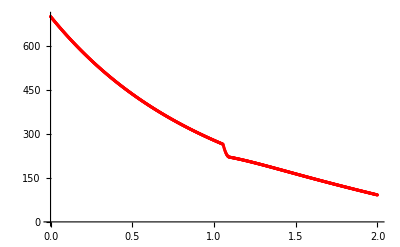

```mathematica
plotEntalpiaMPF4=ListPlot[tablicaEntalpiaMPF4,PlotStyle->Red]
```

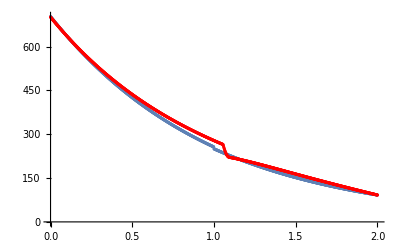

```mathematica
Show[plotEntalpiaDokladna4,plotEntalpiaMPF4]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv

## alfa=8/10

### alfa = 8/10, t=1/2

#### temperatury

```mathematica
str5=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList5=ReadList[str5]
```

{1.27392,1.27149,1.26907,1.26665,1.26423,1.26182,1.25942,1.25702,1.25462,1.25223,1.24984,1.24746,1.24509,1.24272,1.24035,1.23799,1.23563,1.23328,1.23093,1.22859,1.22625,1.22392,1.22159,1.21926,1.21694,1.21463,1.21232,1.21001,1.20771,1.20542,1.20313,1.20084,1.19856,1.19628,1.19401,1.19174,1.18948,1.18722,1.18497,1.18272,1.18047,1.17823,1.176,1.17377,1.17154,1.16932,1.1671,1.16489,1.16268,1.16047,1.15828,1.15608,1.15389,1.1517,1.14952,1.14734,1.14517,1.143,1.14084,1.13868,1.13653,1.13437,1.13223,1.13009,1.12795,1.12582,1.12369,1.12156,1.11944,1.11733,1.11522,1.11311,1.11101,1.10891,1.10681,1.10472,1.10264,1.10056,1.09848,1.09641,1.09434,1.09227,1.09021,1.08816,1.08611,1.08406,1.08202,1.07998,1.07794,1.07591,1.07388,1.07186,1.06984,1.06783,1.06582,1.06382,1.06181,1.05982,1.05782,1.05584,1.05385,1.05187,1.0499,1.04792,1.04596,1.04399,1.04204,1.04008,1.03813,1.03619,1.03269,1.02076,1.00885,1,1,1,1,1,0.993428,0.986202,0.979663,0.973126,0.967852,0.963213,0.958567,0.955268,0.952508,0.949737,0.948436,0.947541,0.946631,0.945707,0.944768,0.943816,0.94285,0.941871,0.940879,0.939874,0.938857,0.937828,0.936788,0.935735,0.934672,0.933598,0.932513,0.931417,0.930312,0.929196,0.928071,0.926937,0.925793,0.924641,0.923479,0.92231,0.921131,0.919945,0.918751,0.917549,0.91634,0.915124,0.9139,0.91267,0.911433,0.910189,0.908939,0.907683,0.906421,0.905153,0.90388,0.902601,0.901316,0.900027,0.898732,0.897433,0.896129,0.89482,0.893507,0.892189,0.890868,0.889542,0.888213,0.886879,0.885542,0.884202,0.882858,0.881511,0.880161,0.878807,0.877451,0.876092,0.87473,0.873366,0.871999,0.870629,0.869258,0.867884,0.866508,0.86513,0.86375,0.862368,0.860984,0.859599,0.858212,0.856824,0.855434,0.854043,0.852651,0.851258,0.849863,0.848467,0.847071,0.845673,0.844275,0.842876,0.841476,0.840076,0.838675,0.837273,0.835871,0.834469,0.833067,0.831664,0.830261,0.828858,0.827454,0.826051,0.824648,0.823244,0.821841,0.820438,0.819036,0.817633,0.816231,0.814829,0.813427,0.812026,0.810626,0.809226,0.807826,0.806427,0.805029,0.803631,0.802234,0.800838,0.799443,0.798048,0.796654,0.795261,0.793869,0.792478,0.791088,0.789699,0.788311,0.786924,0.785538,0.784153,0.78277,0.781387,0.780006,0.778626,0.777247,0.77587,0.774493,0.773118,0.771745,0.770372,0.769002,0.767632,0.766264,0.764898,0.763532,0.762169,0.760807,0.759446,0.758087,0.756729,0.755373,0.754019,0.752666,0.751315,0.749965,0.748617,0.747271,0.745927,0.744584,0.743243,0.741903,0.740565,0.739229,0.737895,0.736563,0.735232,0.733903,0.732576,0.731251,0.729927,0.728605,0.727285,0.725967,0.724651,0.723337,0.722025,0.720714,0.719405,0.718099,0.716794,0.715491,0.71419,0.712891,0.711593,0.710298,0.709005,0.707713,0.706424,0.705137,0.703851,0.702568,0.701286,0.700006,0.698729,0.697453,0.69618,0.694908,0.693638,0.692371,0.691105,0.689842,0.68858,0.68732,0.686063,0.684807,0.683554,0.682302,0.681053,0.679805,0.67856,0.677317,0.676075,0.674836,0.673599,0.672364,0.67113,0.669899,0.66867,0.667443,0.666218,0.664995,0.663774,0.662555,0.661339,0.660124,0.658911,0.657701,0.656492,0.655285,0.654081,0.652878,0.651678,0.65048,0.649283,0.648089,0.646897,0.645707,0.644518,0.643332,0.642148,0.640966,0.639786,0.638608,0.637432,0.636259,0.635087,0.633917,0.632749,0.631583,0.63042,0.629258,0.628098,0.626941,0.625785,0.624632,0.62348,0.62233,0.621183,0.620037,0.618894,0.617752,0.616613,0.615475,0.61434,0.613206,0.612075,0.610945,0.609818,0.608692,0.607569,0.606447,0.605327,0.60421,0.603094,0.601981,0.600869,0.599759,0.598651,0.597546,0.596442,0.59534,0.59424,0.593142,0.592046,0.590952,0.58986,0.58877,0.587681,0.586595,0.585511,0.584428,0.583348,0.582269,0.581192,0.580118,0.579045,0.577974,0.576905,0.575838,0.574772,0.573709,0.572647,0.571588,0.57053,0.569474,0.56842,0.567368,0.566318,0.56527,0.564223,0.563179,0.562136,0.561095,0.560056,0.559019,0.557984,0.55695,0.555918,0.554889,0.55386,0.552834,0.55181,0.550787,0.549767,0.548748,0.547731,0.546715,0.545702,0.54469,0.54368,0.542672,0.541666,0.540661,0.539658,0.538657,0.537658,0.536661,0.535665,0.534671,0.533679,0.532689,0.5317,0.530713,0.529728,0.528744,0.527763,0.526783,0.525804,0.524828,0.523853,0.52288,0.521909,0.520939,0.519971,0.519005,0.51804,0.517077,0.516116,0.515157,0.514199,0.513243,0.512289,0.511336,0.510385,0.509435,0.508488,0.507541,0.506597,0.505654,0.504713,0.503774,0.502836,0.5019,0.500965,0.500032,0.499101,0.498171,0.497243,0.496316,0.495392,0.494468,0.493547,0.492627,0.491708,0.490791,0.489876,0.488962,0.48805,0.48714,0.486231,0.485323,0.484418,0.483513,0.482611,0.481709,0.48081,0.479912,0.479015,0.47812,0.477227,0.476335,0.475445,0.474556,0.473669,0.472783,0.471899,0.471016,0.470135,0.469255,0.468377,0.4675,0.466625,0.465751,0.464879,0.464008,0.463139,0.462271,0.461405,0.46054,0.459677,0.458815,0.457955,0.457096,0.456238,0.455382,0.454527,0.453674,0.452823,0.451972,0.451123,0.450276,0.44943,0.448585,0.447742,0.4469,0.44606,0.445221,0.444384,0.443548,0.442713,0.44188,0.441048,0.440217,0.439388,0.43856,0.437734,0.436909,0.436085,0.435263,0.434442,0.433622,0.432804,0.431987,0.431172,0.430358,0.429545,0.428734,0.427924,0.427115,0.426307,0.425501,0.424697,0.423893,0.423091,0.42229,0.421491,0.420693,0.419896,0.4191,0.418306,0.417513,0.416721,0.415931,0.415142,0.414354,0.413568,0.412782,0.411998,0.411216,0.410434,0.409654,0.408875,0.408098,0.407321,0.406546,0.405772,0.405,0.404228,0.403458,0.402689,0.401921,0.401155,0.40039,0.399626,0.398863,0.398101,0.397341,0.396582,0.395824,0.395067,0.394312,0.393558,0.392805,0.392053,0.391302,0.390552,0.389804,0.389057,0.388311,0.387566,0.386823,0.38608,0.385339,0.384599,0.38386,0.383122,0.382385,0.38165,0.380916,0.380182,0.37945,0.378719,0.37799,0.377261,0.376534,0.375807,0.375082,0.374358,0.373635,0.372913,0.372192,0.371473,0.370754,0.370037,0.36932,0.368605,0.367891,0.367178,0.366466,0.365755,0.365045,0.364337,0.363629,0.362923,0.362217,0.361513,0.36081,0.360107,0.359406,0.358706,0.358007,0.357309,0.356612,0.355916,0.355222,0.354528,0.353835,0.353143,0.352453,0.351763,0.351074,0.350387,0.3497,0.349015,0.34833,0.347647,0.346964,0.346283,0.345602,0.344923,0.344245,0.343567,0.342891,0.342215,0.341541,0.340868,0.340195,0.339524,0.338853,0.338184,0.337515,0.336848,0.336181,0.335515,0.334851,0.334187,0.333524,0.332863,0.332202,0.331542,0.330883,0.330225,0.329568,0.328912,0.328257,0.327603,0.32695,0.326298,0.325646,0.324996,0.324346,0.323698,0.32305,0.322403,0.321758,0.321113,0.320469,0.319826,0.319184,0.318542,0.317902,0.317263,0.316624,0.315986,0.31535,0.314714,0.314079,0.313445,0.312811,0.312179,0.311548,0.310917,0.310287,0.309659,0.309031,0.308404,0.307777,0.307152,0.306527,0.305904,0.305281,0.304659,0.304038,0.303418,0.302798,0.30218,0.301562,0.300945,0.300329,0.299714,0.2991,0.298486,0.297873,0.297261,0.29665,0.29604,0.295431,0.294822,0.294214,0.293607,0.293001,0.292396,0.291791,0.291187,0.290584,0.289982,0.289381,0.28878,0.28818,0.287581,0.286983,0.286386,0.285789,0.285193,0.284598,0.284004,0.28341,0.282817,0.282225,0.281634,0.281044,0.280454,0.279865,0.279277,0.278689,0.278103,0.277517,0.276932,0.276347,0.275763,0.27518,0.274598,0.274017,0.273436,0.272856,0.272277,0.271698,0.27112,0.270543,0.269967,0.269391,0.268816,0.268242,0.267669,0.267096,0.266524,0.265952,0.265382,0.264812,0.264242,0.263674,0.263106,0.262539,0.261972,0.261407,0.260842,0.260277,0.259714,0.259151,0.258588,0.258027,0.257466,0.256905,0.256346,0.255787,0.255228,0.254671,0.254114,0.253558,0.253002,0.252447,0.251893,0.251339,0.250786,0.250234,0.249682,0.249131,0.248581,0.248031,0.247482,0.246933,0.246386,0.245838,0.245292,0.244746,0.244201,0.243656,0.243112,0.242569,0.242026,0.241484,0.240942,0.240401,0.239861,0.239321,0.238782,0.238244,0.237706,0.237169,0.236632,0.236096,0.235561,0.235026,0.234492,0.233958,0.233425,0.232893,0.232361,0.23183,0.231299,0.230769,0.23024,0.229711,0.229183,0.228655,0.228128,0.227601,0.227075,0.22655,0.226025,0.2255,0.224977,0.224454,0.223931,0.223409,0.222888,0.222367,0.221846,0.221326,0.220807,0.220289,0.21977,0.219253,0.218736,0.218219,0.217703,0.217188,0.216673,0.216159,0.215645,0.215132,0.214619,0.214107,0.213595,0.213084,0.212573,0.212063,0.211554,0.211045,0.210536,0.210028,0.209521,0.209014,0.208507,0.208001,0.207496,0.206991,0.206487,0.205983,0.205479,0.204977,0.204474,0.203972,0.203471,0.20297,0.20247,0.20197,0.20147,0.200972,0.200473,0.199975,0.199478,0.198981,0.198484,0.197988,0.197493,0.196998,0.196503,0.196009,0.195516,0.195023,0.19453,0.194038,0.193546,0.193055,0.192564,0.192074,0.191584,0.191095,0.190606,0.190117,0.189629,0.189142,0.188655,0.188168,0.187682,0.187196,0.186711,0.186226,0.185742,0.185258,0.184774,0.184291,0.183809,0.183326,0.182845,0.182363,0.181883,0.181402,0.180922,0.180443,0.179964,0.179485,0.179007,0.178529,0.178051,0.177574,0.177098,0.176622,0.176146,0.175671,0.175196,0.174722,0.174248,0.173774}

```mathematica
strList5={1.2739237722,1.2714937754,1.269068706,1.2666485494,1.2642332945,1.2618229331,1.2594174573,1.2570168591,1.2546211286,1.2522302525,1.2498442225,1.2474630308,1.2450866693,1.2427151301,1.2403484054,1.2379864804,1.2356293471,1.2332769972,1.2309294227,1.2285866157,1.2262485685,1.2239152732,1.2215867154,1.2192628869,1.2169437799,1.2146293863,1.2123196985,1.2100147086,1.2077144026,1.2054187727,1.2031278108,1.200841509,1.1985598598,1.1962828496,1.1940104705,1.1917427147,1.1894795743,1.1872210418,1.184967104,1.182717753,1.1804729811,1.1782327806,1.1759971388,1.1737660479,1.1715395002,1.1693174882,1.1671000043,1.1648870359,1.1626785754,1.1604746153,1.158275148,1.1560801613,1.1538896477,1.1517035997,1.1495220099,1.1473448664,1.1451721617,1.1430038883,1.1408400392,1.1386806026,1.1365255712,1.1343749377,1.1322286951,1.130086832,1.1279493411,1.1258162154,1.1236874482,1.1215630283,1.1194429487,1.1173272025,1.1152157792,1.113108672,1.1110058742,1.1089073795,1.1068131777,1.1047232622,1.1026376267,1.100556266,1.0984791697,1.0964063317,1.094337747,1.0922734065,1.0902133045,1.0881574362,1.0861057937,1.0840583721,1.082015167,1.0799761757,1.0779413912,1.0759108094,1.0738844295,1.0718622469,1.0698442591,1.0678304674,1.0658208705,1.0638154694,1.0618142687,1.0598172728,1.0578244887,1.0558359268,1.0538516067,1.0518715433,1.0498957592,1.0479243002,1.045957208,1.043994538,1.0420364208,1.0400829817,1.0381348143,1.0361947919,1.0326922048,1.0207564374,1.0088534619,1,1,1,1,1,0.9934278287,0.9862015553,0.9796630951,0.9731257605,0.9678518325,0.9632126652,0.9585674897,0.9552677029,0.9525078642,0.949736724,0.9484362829,0.9475412495,0.9466313769,0.9457070023,0.9447684563,0.9438160636,0.9428501425,0.9418710055,0.940878959,0.9398743037,0.9388573346,0.9378283412,0.9367876073,0.9357354115,0.9346720272,0.9335977224,0.9325127601,0.9314173983,0.9303118902,0.9291964841,0.9280714236,0.9269369476,0.9257932905,0.9246406823,0.9234793486,0.9223095107,0.9211313855,0.919945186,0.9187511211,0.9175493957,0.9163402106,0.9151237629,0.9139002461,0.9126698496,0.9114327596,0.9101891584,0.908939225,0.9076831349,0.9064210602,0.9051531697,0.9038796289,0.9026006003,0.9013162431,0.9000267135,0.8987321646,0.8974327467,0.8961286071,0.8948198901,0.8935067376,0.8921892883,0.8908676786,0.8895420419,0.8882125094,0.8868792094,0.8855422678,0.8842018082,0.8828579516,0.8815108168,0.8801605201,0.8788071757,0.8774508954,0.876091789,0.874729964,0.8733655258,0.8719985779,0.8706292214,0.8692575559,0.8678836785,0.8665076849,0.8651296685,0.8637497211,0.8623679325,0.8609843909,0.8595991827,0.8582123924,0.8568241031,0.855434396,0.8540433509,0.8526510458,0.8512575572,0.8498629602,0.8484673282,0.8470707332,0.8456732457,0.844274935,0.8428758687,0.8414761132,0.8400757336,0.8386747934,0.8372733552,0.83587148,0.8344692278,0.8330666571,0.8316638255,0.8302607891,0.8288576032,0.8274543218,0.8260509976,0.8246476824,0.8232444271,0.8218412811,0.8204382931,0.8190355108,0.8176329806,0.8162307484,0.8148288586,0.813427355,0.8120262806,0.810625677,0.8092255854,0.8078260459,0.8064270978,0.8050287794,0.8036311286,0.8022341819,0.8008379755,0.7994425446,0.7980479237,0.7966541465,0.7952612459,0.7938692543,0.7924782032,0.7910881235,0.7896990453,0.7883109982,0.786924011,0.7855381119,0.7841533285,0.7827696878,0.7813872161,0.7800059392,0.7786258822,0.7772470698,0.7758695259,0.7744932741,0.7731183372,0.7717447377,0.7703724975,0.7690016379,0.7676321798,0.7662641435,0.764897549,0.7635324156,0.7621687623,0.7608066076,0.7594459695,0.7580868656,0.7567293131,0.7553733288,0.7540189289,0.7526661294,0.7513149458,0.7499653932,0.7486174864,0.7472712397,0.7459266672,0.7445837825,0.7432425988,0.7419031291,0.740565386,0.7392293817,0.7378951282,0.7365626369,0.7352319193,0.7339029863,0.7325758485,0.7312505163,0.7299269998,0.7286053088,0.7272854527,0.7259674408,0.724651282,0.723336985,0.7220245583,0.72071401,0.719405348,0.71809858,0.7167937134,0.7154907555,0.7141897131,0.7128905929,0.7115934016,0.7102981454,0.7090048303,0.7077134622,0.7064240468,0.7051365896,0.7038510957,0.7025675703,0.7012860181,0.7000064439,0.6987288523,0.6974532474,0.6961796334,0.6949080144,0.693638394,0.692370776,0.6911051638,0.6898415607,0.6885799699,0.6873203943,0.6860628368,0.6848073001,0.6835537868,0.6823022993,0.6810528398,0.6798054106,0.6785600135,0.6773166504,0.6760753233,0.6748360335,0.6735987827,0.6723635722,0.6711304033,0.6698992771,0.6686701946,0.6674431569,0.6662181646,0.6649952185,0.6637743192,0.6625554671,0.6613386628,0.6601239064,0.6589111982,0.6577005383,0.6564919267,0.6552853634,0.6540808481,0.6528783807,0.6516779607,0.6504795878,0.6492832615,0.6480889811,0.6468967461,0.6457065558,0.6445184092,0.6433323055,0.6421482438,0.640966223,0.6397862421,0.6386082999,0.6374323951,0.6362585265,0.6350866928,0.6339168924,0.632749124,0.631583386,0.6304196769,0.6292579948,0.6280983383,0.6269407055,0.6257850946,0.6246315037,0.623479931,0.6223303744,0.621182832,0.6200373017,0.6188937814,0.617752269,0.6166127622,0.6154752588,0.6143397567,0.6132062533,0.6120747464,0.6109452336,0.6098177125,0.6086921805,0.6075686352,0.606447074,0.6053274943,0.6042098936,0.6030942691,0.6019806182,0.6008689382,0.5997592263,0.5986514798,0.5975456958,0.5964418716,0.5953400042,0.5942400908,0.5931421284,0.5920461142,0.5909520451,0.5898599182,0.5887697305,0.5876814788,0.5865951602,0.5855107716,0.5844283098,0.5833477718,0.5822691544,0.5811924544,0.5801176686,0.5790447939,0.5779738269,0.5769047646,0.5758376035,0.5747723405,0.5737089722,0.5726474954,0.5715879067,0.5705302027,0.5694743802,0.5684204357,0.5673683659,0.5663181674,0.5652698367,0.5642233705,0.5631787654,0.5621360177,0.5610951243,0.5600560814,0.5590188858,0.5579835338,0.5569500221,0.555918347,0.5548885051,0.5538604929,0.5528343068,0.5518099433,0.5507873988,0.5497666697,0.5487477526,0.5477306438,0.5467153398,0.545701837,0.5446901317,0.5436802205,0.5426720996,0.5416657655,0.5406612146,0.5396584433,0.5386574479,0.5376582247,0.5366607703,0.5356650809,0.5346711529,0.5336789827,0.5326885666,0.531699901,0.5307129822,0.5297278066,0.5287443705,0.5277626702,0.5267827022,0.5258044627,0.524827948,0.5238531546,0.5228800787,0.5219087167,0.5209390649,0.5199711197,0.5190048773,0.5180403341,0.5170774864,0.5161163306,0.515156863,0.5141990799,0.5132429777,0.5122885527,0.5113358011,0.5103847194,0.5094353039,0.5084875509,0.5075414567,0.5065970177,0.5056542302,0.5047130906,0.5037735952,0.5028357403,0.5018995222,0.5009649375,0.5000319822,0.4991006529,0.4981709459,0.4972428575,0.4963163841,0.495391522,0.4944682676,0.4935466173,0.4926265674,0.4917081143,0.4907912544,0.489875984,0.4889622996,0.4880501974,0.487139674,0.4862307256,0.4853233487,0.4844175397,0.4835132949,0.4826106108,0.4817094837,0.4808099102,0.4799118865,0.4790154092,0.4781204746,0.4772270791,0.4763352192,0.4754448913,0.4745560919,0.4736688174,0.4727830642,0.4718988288,0.4710161076,0.4701348972,0.4692551939,0.4683769942,0.4675002947,0.4666250917,0.4657513818,0.4648791614,0.464008427,0.4631391752,0.4622714024,0.4614051052,0.4605402799,0.4596769233,0.4588150317,0.4579546017,0.4570956298,0.4562381126,0.4553820466,0.4545274284,0.4536742544,0.4528225213,0.4519722256,0.4511233639,0.4502759327,0.4494299286,0.4485853482,0.4477421881,0.4469004449,0.4460601151,0.4452211954,0.4443836824,0.4435475726,0.4427128628,0.4418795495,0.4410476294,0.440217099,0.4393879551,0.4385601942,0.437733813,0.4369088083,0.4360851765,0.4352629145,0.4344420189,0.4336224863,0.4328043134,0.431987497,0.4311720336,0.4303579201,0.4295451532,0.4287337294,0.4279236456,0.4271148985,0.4263074848,0.4255014012,0.4246966445,0.4238932114,0.4230910987,0.4222903031,0.4214908214,0.4206926504,0.4198957867,0.4191002273,0.4183059689,0.4175130083,0.4167213422,0.4159309675,0.415141881,0.4143540795,0.4135675598,0.4127823187,0.4119983531,0.4112156599,0.4104342357,0.4096540776,0.4088751823,0.4080975467,0.4073211677,0.4065460421,0.4057721669,0.4049995388,0.4042281548,0.4034580118,0.4026891067,0.4019214363,0.4011549977,0.4003897876,0.3996258031,0.398863041,0.3981014983,0.3973411719,0.3965820588,0.3958241559,0.3950674602,0.3943119686,0.3935576781,0.3928045856,0.3920526883,0.3913019829,0.3905524666,0.3898041363,0.389056989,0.3883110217,0.3875662315,0.3868226153,0.3860801701,0.3853388931,0.3845987812,0.3838598315,0.383122041,0.3823854068,0.3816499259,0.3809155954,0.3801824124,0.3794503738,0.3787194769,0.3779897187,0.3772610963,0.3765336067,0.3758072471,0.3750820146,0.3743579063,0.3736349193,0.3729130507,0.3721922978,0.3714726575,0.370754127,0.3700367035,0.3693203842,0.3686051661,0.3678910465,0.3671780225,0.3664660912,0.36575525,0.3650454959,0.3643368261,0.3636292378,0.3629227283,0.3622172947,0.3615129343,0.3608096442,0.3601074216,0.3594062639,0.3587061682,0.3580071318,0.3573091519,0.3566122257,0.3559163505,0.3552215236,0.3545277423,0.3538350037,0.3531433052,0.3524526441,0.3517630176,0.351074423,0.3503868576,0.3497003187,0.3490148037,0.3483303098,0.3476468343,0.3469643746,0.346282928,0.3456024919,0.3449230635,0.3442446401,0.3435672193,0.3428907982,0.3422153743,0.3415409449,0.3408675074,0.3401950592,0.3395235976,0.33885312,0.3381836238,0.3375151064,0.3368475652,0.3361809976,0.335515401,0.3348507728,0.3341871105,0.3335244114,0.332862673,0.3322018927,0.331542068,0.3308831963,0.3302252751,0.3295683017,0.3289122737,0.3282571885,0.3276030437,0.3269498365,0.3262975647,0.3256462255,0.3249958166,0.3243463354,0.3236977794,0.323050146,0.322403433,0.3217576376,0.3211127575,0.3204687901,0.3198257331,0.3191835838,0.31854234,0.317901999,0.3172625585,0.316624016,0.3159863691,0.3153496152,0.3147137521,0.3140787772,0.3134446882,0.3128114826,0.312179158,0.311547712,0.3109171421,0.3102874461,0.3096586214,0.3090306658,0.3084035767,0.3077773519,0.307151989,0.3065274855,0.3059038392,0.3052810476,0.3046591084,0.3040380193,0.3034177779,0.3027983818,0.3021798287,0.3015621164,0.3009452424,0.3003292044,0.2997140001,0.2990996273,0.2984860835,0.2978733665,0.297261474,0.2966504037,0.2960401533,0.2954307204,0.294822103,0.2942142985,0.2936073049,0.2930011197,0.2923957408,0.2917911659,0.2911873927,0.290584419,0.2899822425,0.289380861,0.2887802723,0.2881804741,0.2875814643,0.2869832405,0.2863858006,0.2857891423,0.2851932634,0.2845981619,0.2840038353,0.2834102816,0.2828174986,0.282225484,0.2816342357,0.2810437516,0.2804540294,0.2798650669,0.2792768621,0.2786894127,0.2781027167,0.2775167718,0.2769315759,0.2763471269,0.2757634226,0.2751804609,0.2745982397,0.2740167569,0.2734360103,0.2728559978,0.2722767174,0.2716981669,0.2711203442,0.2705432472,0.2699668739,0.2693912221,0.2688162897,0.2682420748,0.2676685752,0.2670957889,0.2665237137,0.2659523477,0.2653816887,0.2648117348,0.2642424839,0.2636739339,0.2631060828,0.2625389286,0.2619724693,0.2614067028,0.2608416271,0.2602772402,0.2597135401,0.2591505247,0.2585881922,0.2580265404,0.2574655675,0.2569052713,0.25634565,0.2557867016,0.255228424,0.2546708153,0.2541138736,0.2535575969,0.2530019832,0.2524470305,0.2518927371,0.2513391008,0.2507861198,0.2502337921,0.2496821158,0.2491310889,0.2485807097,0.248030976,0.2474818861,0.2469334381,0.2463856299,0.2458384598,0.2452919258,0.244746026,0.2442007586,0.2436561217,0.2431121134,0.2425687319,0.2420259752,0.2414838415,0.240942329,0.2404014358,0.2398611601,0.2393214999,0.2387824536,0.2382440192,0.2377061949,0.2371689788,0.2366323693,0.2360963644,0.2355609623,0.2350261613,0.2344919595,0.2339583552,0.2334253464,0.2328929316,0.2323611088,0.2318298762,0.2312992322,0.230769175,0.2302397027,0.2297108136,0.2291825059,0.228654778,0.228127628,0.2276010543,0.227075055,0.2265496284,0.2260247729,0.2255004866,0.2249767679,0.224453615,0.2239310263,0.223409,0.2228875344,0.2223666278,0.2218462786,0.221326485,0.2208072453,0.2202885579,0.2197704212,0.2192528333,0.2187357928,0.2182192978,0.2177033468,0.217187938,0.2166730699,0.2161587408,0.2156449491,0.2151316931,0.2146189712,0.2141067818,0.2135951232,0.2130839939,0.2125733922,0.2120633165,0.2115537653,0.2110447368,0.2105362296,0.2100282421,0.2095207726,0.2090138196,0.2085073815,0.2080014567,0.2074960437,0.2069911409,0.2064867468,0.2059828598,0.2054794783,0.2049766009,0.204474226,0.203972352,0.2034709774,0.2029701008,0.2024697205,0.2019698352,0.2014704431,0.200971543,0.2004731332,0.1999752123,0.1994777788,0.1989808311,0.1984843679,0.1979883876,0.1974928888,0.19699787,0.1965033298,0.1960092666,0.1955156791,0.1950225658,0.1945299253,0.194037756,0.1935460567,0.1930548258,0.1925640619,0.1920737637,0.1915839296,0.1910945584,0.1906056485,0.1901171987,0.1896292074,0.1891416734,0.1886545952,0.1881679715,0.1876818008,0.1871960819,0.1867108133,0.1862259936,0.1857416217,0.185257696,0.1847742152,0.1842911781,0.1838085832,0.1833264292,0.1828447149,0.1823634389,0.1818825998,0.1814021964,0.1809222274,0.1804426914,0.1799635872,0.1794849135,0.179006669,0.1785288523,0.1780514624,0.1775744978,0.1770979573,0.1766218396,0.1761461435,0.1756708678,0.1751960112,0.1747215724,0.1742475502,0.1737739435};
```

```mathematica
tablicaTemperaturMPF5=Table[{i*0.002,strList5[[i+1]]},{i,0,1000}];
```

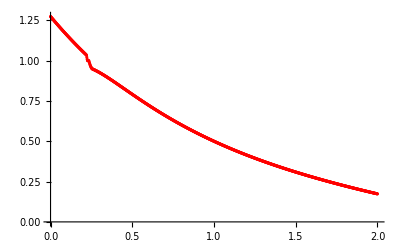

```mathematica
plotTemperaturyMPF5=ListPlot[tablicaTemperaturMPF5,PlotStyle->Red]
```

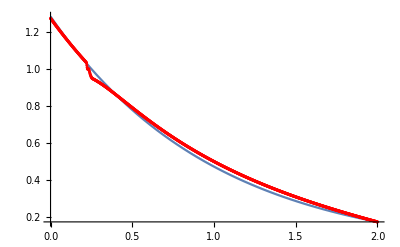

```mathematica
Show[plotTemperaturyDokladne1,plotTemperaturyMPF5]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(Gamma[0.2]*(lambdaL-lambdaS))/(5*aL*t^(1/5));
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t],temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna5=Table[{i*0.002,entalpia[u1[i*0.002,0.5],0.5]},{i,0,1000}];
```

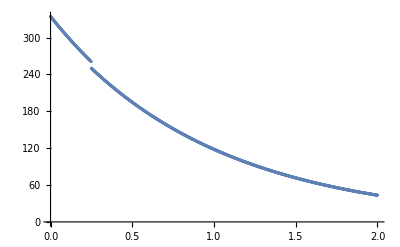

```mathematica
plotEntalpiaDokladna5=ListPlot[tablicaEntalpiaDokladna5]
```

```mathematica
strE=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE5=ReadList[strE]
```

{331.767,331.135,330.505,329.876,329.248,328.621,327.996,327.371,326.748,326.127,325.506,324.887,324.27,323.653,323.038,322.423,321.811,321.199,320.589,319.98,319.372,318.765,318.16,317.555,316.952,316.351,315.75,315.151,314.553,313.956,313.36,312.766,312.173,311.581,310.99,310.4,309.812,309.224,308.638,308.054,307.47,306.888,306.306,305.726,305.147,304.57,303.993,303.418,302.843,302.27,301.699,301.128,300.558,299.99,299.423,298.857,298.292,297.728,297.165,296.604,296.044,295.484,294.926,294.37,293.814,293.259,292.706,292.153,291.602,291.052,290.503,289.955,289.409,288.863,288.318,287.775,287.233,286.692,286.152,285.613,285.075,284.538,284.002,283.468,282.934,282.402,281.871,281.341,280.812,280.284,279.757,279.231,278.706,278.183,277.66,277.139,276.619,276.099,275.581,275.064,274.548,274.034,273.52,273.007,272.496,271.986,271.476,270.969,270.462,269.958,269.047,265.944,262.849,260.08,257.475,254.876,252.586,250.47,248.357,246.55,244.916,243.281,241.963,240.803,239.642,238.817,238.127,237.434,237.109,236.885,236.658,236.427,236.192,235.954,235.713,235.468,235.22,234.969,234.714,234.457,234.197,233.934,233.668,233.399,233.128,232.854,232.578,232.299,232.018,231.734,231.448,231.16,230.87,230.577,230.283,229.986,229.688,229.387,229.085,228.781,228.475,228.167,227.858,227.547,227.235,226.921,226.605,226.288,225.97,225.65,225.329,225.007,224.683,224.358,224.032,223.705,223.377,223.047,222.717,222.386,222.053,221.72,221.386,221.05,220.714,220.378,220.04,219.702,219.363,219.023,218.682,218.341,218.,217.657,217.314,216.971,216.627,216.282,215.937,215.592,215.246,214.9,214.553,214.206,213.859,213.511,213.163,212.814,212.466,212.117,211.768,211.418,211.069,210.719,210.369,210.019,209.669,209.318,208.968,208.617,208.267,207.916,207.565,207.214,206.864,206.513,206.162,205.811,205.46,205.11,204.759,204.408,204.058,203.707,203.357,203.007,202.656,202.306,201.957,201.607,201.257,200.908,200.559,200.209,199.861,199.512,199.164,198.815,198.467,198.12,197.772,197.425,197.078,196.731,196.385,196.038,195.692,195.347,195.001,194.656,194.312,193.967,193.623,193.28,192.936,192.593,192.25,191.908,191.566,191.224,190.883,190.542,190.202,189.861,189.522,189.182,188.843,188.505,188.167,187.829,187.491,187.154,186.818,186.482,186.146,185.811,185.476,185.141,184.807,184.474,184.141,183.808,183.476,183.144,182.813,182.482,182.151,181.821,181.492,181.163,180.834,180.506,180.179,179.851,179.525,179.198,178.873,178.547,178.223,177.898,177.575,177.251,176.928,176.606,176.284,175.963,175.642,175.322,175.002,174.682,174.363,174.045,173.727,173.41,173.093,172.776,172.46,172.145,171.83,171.516,171.202,170.888,170.576,170.263,169.951,169.64,169.329,169.019,168.709,168.4,168.091,167.783,167.475,167.168,166.861,166.555,166.249,165.944,165.639,165.335,165.031,164.728,164.425,164.123,163.821,163.52,163.22,162.919,162.62,162.321,162.022,161.724,161.427,161.13,160.833,160.537,160.242,159.947,159.652,159.358,159.065,158.772,158.479,158.187,157.896,157.605,157.314,157.025,156.735,156.446,156.158,155.87,155.583,155.296,155.009,154.723,154.438,154.153,153.869,153.585,153.302,153.019,152.736,152.454,152.173,151.892,151.612,151.332,151.052,150.774,150.495,150.217,149.94,149.663,149.386,149.11,148.835,148.56,148.286,148.012,147.738,147.465,147.192,146.92,146.649,146.378,146.107,145.837,145.567,145.298,145.029,144.761,144.493,144.226,143.959,143.693,143.427,143.162,142.897,142.633,142.369,142.105,141.842,141.58,141.317,141.056,140.795,140.534,140.274,140.014,139.755,139.496,139.238,138.98,138.722,138.465,138.209,137.952,137.697,137.442,137.187,136.933,136.679,136.425,136.173,135.92,135.668,135.416,135.165,134.915,134.664,134.415,134.165,133.916,133.668,133.42,133.172,132.925,132.678,132.432,132.186,131.941,131.696,131.451,131.207,130.963,130.72,130.477,130.235,129.993,129.751,129.51,129.269,129.029,128.789,128.55,128.311,128.072,127.834,127.596,127.359,127.122,126.885,126.649,126.414,126.178,125.943,125.709,125.475,125.241,125.008,124.775,124.543,124.311,124.079,123.848,123.617,123.387,123.157,122.927,122.698,122.469,122.241,122.013,121.785,121.558,121.331,121.104,120.878,120.653,120.427,120.202,119.978,119.754,119.53,119.307,119.084,118.861,118.639,118.417,118.196,117.975,117.754,117.534,117.314,117.094,116.875,116.656,116.438,116.22,116.002,115.785,115.568,115.351,115.135,114.919,114.704,114.489,114.274,114.06,113.846,113.632,113.419,113.206,112.993,112.781,112.569,112.357,112.146,111.936,111.725,111.515,111.305,111.096,110.887,110.678,110.47,110.262,110.054,109.847,109.64,109.433,109.227,109.021,108.816,108.611,108.406,108.201,107.997,107.793,107.589,107.386,107.183,106.981,106.779,106.577,106.375,106.174,105.973,105.773,105.573,105.373,105.173,104.974,104.775,104.576,104.378,104.18,103.983,103.785,103.589,103.392,103.196,103.,102.804,102.609,102.414,102.219,102.024,101.83,101.637,101.443,101.25,101.057,100.865,100.672,100.48,100.289,100.097,99.9065,99.7158,99.5254,99.3353,99.1455,98.956,98.7669,98.578,98.3894,98.2011,98.0132,97.8255,97.6381,97.451,97.2642,97.0778,96.8916,96.7057,96.52,96.3347,96.1497,95.965,95.7805,95.5964,95.4125,95.2289,95.0456,94.8626,94.6799,94.4974,94.3153,94.1334,93.9518,93.7705,93.5895,93.4087,93.2283,93.0481,92.8682,92.6885,92.5092,92.3301,92.1513,91.9728,91.7945,91.6165,91.4388,91.2614,91.0842,90.9073,90.7307,90.5543,90.3782,90.2024,90.0269,89.8516,89.6765,89.5018,89.3273,89.1531,88.9791,88.8054,88.6319,88.4588,88.2858,88.1132,87.9408,87.7686,87.5967,87.4251,87.2537,87.0826,86.9117,86.7411,86.5707,86.4006,86.2308,86.0612,85.8918,85.7227,85.5538,85.3852,85.2169,85.0488,84.8809,84.7133,84.5459,84.3788,84.2119,84.0452,83.8789,83.7127,83.5468,83.3811,83.2157,83.0505,82.8855,82.7208,82.5563,82.3921,82.2281,82.0643,81.9008,81.7375,81.5744,81.4116,81.249,81.0866,80.9244,80.7625,80.6009,80.4394,80.2782,80.1172,79.9564,79.7959,79.6356,79.4755,79.3156,79.156,78.9966,78.8374,78.6784,78.5197,78.3612,78.2029,78.0448,77.8869,77.7293,77.5719,77.4147,77.2577,77.1009,76.9443,76.788,76.6319,76.476,76.3203,76.1648,76.0095,75.8544,75.6996,75.545,75.3905,75.2363,75.0823,74.9285,74.7749,74.6215,74.4683,74.3154,74.1626,74.01,73.8577,73.7055,73.5536,73.4018,73.2503,73.0989,72.9478,72.7968,72.6461,72.4956,72.3452,72.1951,72.0451,71.8954,71.7458,71.5965,71.4473,71.2983,71.1495,71.001,70.8526,70.7044,70.5564,70.4086,70.2609,70.1135,69.9663,69.8192,69.6724,69.5257,69.3792,69.2329,69.0868,68.9409,68.7951,68.6496,68.5042,68.359,68.214,68.0692,67.9245,67.7801,67.6358,67.4917,67.3478,67.2041,67.0605,66.9171,66.7739,66.6309,66.4881,66.3454,66.2029,66.0606,65.9185,65.7765,65.6347,65.4931,65.3517,65.2104,65.0693,64.9284,64.7876,64.647,64.5066,64.3664,64.2263,64.0864,63.9467,63.8071,63.6677,63.5285,63.3894,63.2505,63.1118,62.9732,62.8348,62.6965,62.5584,62.4205,62.2828,62.1452,62.0077,61.8705,61.7334,61.5964,61.4596,61.323,61.1865,61.0502,60.914,60.778,60.6422,60.5065,60.371,60.2356,60.1004,59.9653,59.8304,59.6956,59.561,59.4265,59.2922,59.1581,59.0241,58.8902,58.7565,58.623,58.4896,58.3563,58.2232,58.0903,57.9575,57.8248,57.6923,57.5599,57.4277,57.2956,57.1637,57.0319,56.9003,56.7688,56.6374,56.5062,56.3751,56.2442,56.1134,55.9828,55.8522,55.7219,55.5917,55.4616,55.3316,55.2018,55.0721,54.9426,54.8132,54.6839,54.5548,54.4258,54.297,54.1683,54.0397,53.9112,53.7829,53.6547,53.5267,53.3988,53.271,53.1433,53.0158,52.8884,52.7612,52.6341,52.5071,52.3802,52.2535,52.1268,52.0004,51.874,51.7478,51.6217,51.4957,51.3699,51.2442,51.1186,50.9931,50.8677,50.7425,50.6174,50.4925,50.3676,50.2429,50.1183,49.9938,49.8694,49.7452,49.6211,49.4971,49.3732,49.2495,49.1258,49.0023,48.8789,48.7556,48.6325,48.5094,48.3865,48.2637,48.141,48.0184,47.896,47.7736,47.6514,47.5293,47.4073,47.2854,47.1636,47.042,46.9205,46.799,46.6777,46.5565,46.4354,46.3144,46.1936,46.0728,45.9521,45.8316,45.7112,45.5909,45.4706,45.3505,45.2306,45.1107,44.9909,44.8712,44.7517,44.6322,44.5129,44.3936,44.2745,44.1555,44.0365,43.9177,43.799,43.6804,43.5619,43.4435}

```mathematica
strListE5={331.7671700092,331.1353708505,330.5048528036,329.8756120932,329.2476458015,328.6209518459,327.9955281449,327.3713726183,326.7484826859,326.126854891,325.5064871026,324.8873772415,324.26952325,323.6529230718,323.0375746516,322.4234741545,321.8106194735,321.1990085028,320.5886391381,319.9795093337,319.3716170573,318.7649602776,318.1595352325,317.5553398398,316.9523720187,316.3506296897,315.7501108397,315.1508134754,314.5527339263,313.9558701329,313.3602200372,312.7657815835,312.1725527985,311.5805301406,310.9897115714,310.4000950541,309.8116785527,309.2244601086,308.6384362674,308.0536050118,307.4699643256,306.8875122041,306.3062453242,305.726161689,305.1472593025,304.5695361702,303.9929903568,303.4176185745,302.843418849,302.2703892072,301.6985277194,301.1278311832,300.5582976476,299.9899251625,299.422711823,298.8566545002,298.2917512692,297.7280002055,297.1653994442,296.603945926,296.0436377553,295.4844730373,294.9264499682,294.3695655537,293.8138179327,293.259205247,292.7057257832,292.1533766055,291.6021558939,291.0520618971,290.5030918402,289.9552439721,289.4085165234,288.8629079084,288.3184154353,287.7750374005,287.2327721937,286.6916183909,286.1515733565,285.6126354716,285.0748034478,284.5380749272,284.0024484118,283.4679226609,282.9344955913,282.402165984,281.8709326529,281.3407949183,280.8117509617,280.2837996903,279.7569409158,279.2311734244,278.7064965931,278.1829107547,277.6604155737,277.1390112938,276.6186991001,276.099480175,275.5813563044,275.064330202,274.5484069785,274.0335904988,273.5198866297,273.007307298,272.4958633307,271.9855691318,271.4764586598,270.9685644776,270.4620409488,269.95763514,269.0469624808,265.9436629613,262.8488893234,260.080344295,257.4754434256,254.8758290249,252.5860915361,250.4702558998,248.3569571843,246.550388829,244.9157737698,243.2814401361,241.9629581159,240.8031662946,239.641872425,238.8169257209,238.126966054,237.4341809942,237.109070717,236.8853123784,236.6578442333,236.4267505679,236.192114078,235.954015898,235.7125356297,235.4677513709,235.2197397433,234.9685759193,234.7143336493,234.4570852879,234.1969018196,233.9338528841,233.6680068013,233.3994305959,233.128190021,232.8543495817,232.5779725583,232.2991210293,232.0178558928,231.734236889,231.4483226216,231.1601705786,230.8698371529,230.5773776629,230.2828463722,229.9862965091,229.6877802857,229.3873489169,229.0850526389,228.7809407269,228.4750615134,228.1674624056,227.8581899021,227.5472896102,227.2348062621,226.9207837314,226.6052650488,226.2882924177,225.9699072296,225.6501500792,225.3290607792,225.0066783745,224.6830411567,224.358186678,224.032151765,223.7049725318,223.3766843937,223.0473220799,222.7169196462,222.3855104873,222.0531273497,221.719802343,221.3855669522,221.0504520491,220.7144879036,220.377704195,220.0401300229,219.7017939181,219.362723853,219.0229472519,218.6824910014,218.3413814602,217.9996444689,217.65730536,217.3143889665,216.9709196323,216.6269212203,216.2824171218,215.9374302653,215.591983125,215.246097729,214.8997956682,214.5530981037,214.2060257755,213.8585990098,213.5108377268,213.1627614485,212.8143893059,212.4657400463,212.1168320405,211.7676832897,211.4183114326,211.0687337518,210.7189671809,210.3690283104,210.0189333946,209.6686983579,209.3183388003,208.9678700043,208.6173069401,208.266664272,207.9159563635,207.5651972836,207.2144008117,206.8635804434,206.5127493954,206.1619206113,205.811106766,205.4603202713,205.1095732804,204.758877693,204.4082451601,204.0576870883,203.7072146445,203.3568387606,203.0065701378,202.6564192506,202.3063963517,201.9565114753,201.606774442,201.2571948623,200.9077821407,200.5585454795,200.2094938827,199.8606361596,199.5119809286,199.1635366206,198.8153114826,198.4673135811,198.1195508058,197.7720308723,197.4247613259,197.0777495449,196.7310027429,196.384527973,196.0383321301,195.692421954,195.3468040325,195.001484804,194.6564705607,194.311767451,193.9673814822,193.6233185235,193.2795843084,192.9361844371,192.5931243792,192.2504094764,191.9080449444,191.5660358756,191.2243872414,190.8831038945,190.5421905711,190.201651893,189.8614923702,189.5217164023,189.1823282813,188.8433321933,188.5047322204,188.1665323431,187.8287364416,187.4913482985,187.1543715998,186.8178099374,186.4816668107,186.1459456281,185.8106497093,185.4757822862,185.1413465054,184.8073454293,184.4737820378,184.1406592301,183.807979826,183.4757465674,183.14396212,182.8126290747,182.481749949,182.1513271882,181.8213631672,181.4918601915,181.1628204989,180.8342462604,180.5061395815,180.1785025041,179.8513370068,179.5246450068,179.1984283609,178.8726888665,178.547428263,178.2226482328,177.8983504023,177.5745363433,177.2512075736,176.9283655586,176.6060117119,176.2841473963,175.9627739252,175.6418925631,175.3215045269,175.0016109866,174.6822130663,174.3633118451,174.044908358,173.7270035968,173.4095985108,173.0926940078,172.776290955,172.4603901793,172.1449924688,171.830098573,171.5157092039,171.2018250366,170.8884467101,170.5755748279,170.2632099589,169.9513526377,169.640003366,169.3291626124,169.0188308138,168.7090083755,168.3996956721,168.0908930481,167.7826008186,167.4748192695,167.1675486585,166.8607892156,166.5545411434,166.248804618,165.9435797894,165.6388667819,165.3346656948,165.0309766028,164.7277995566,164.4251345834,164.1229816872,163.8213408496,163.5202120298,163.2195951657,162.9194901735,162.6198969491,162.3208153677,162.0222452848,161.7241865362,161.4266389389,161.1296022908,160.8330763719,160.5370609439,160.2415557513,159.9465605212,159.6520749641,159.3580987739,159.0646316283,158.7716731896,158.4792231044,158.1872810044,157.8958465063,157.6049192127,157.3144987119,157.0245845783,156.7351763729,156.4462736437,156.1578759253,155.86998274,155.5825935978,155.2957079963,155.0093254216,154.7234453481,154.438067239,154.1531905463,153.8688147114,153.584939165,153.3015633277,153.0186866099,152.7363084121,152.4544281253,152.1730451312,151.8921588022,151.6117685018,151.3318735847,151.0524733972,150.7735672771,150.4951545542,150.2172345503,149.9398065796,149.6628699485,149.3864239562,149.1104678946,148.8350010487,148.5600226966,148.2855321096,148.0115285528,147.7380112847,147.4649795577,147.1924326181,146.9203697065,146.6487900577,146.3776929008,146.1070774598,145.836942953,145.567288594,145.298113591,145.0294171477,144.7611984627,144.4934567303,144.2261911403,143.9594008778,143.6930851242,143.4272430564,143.1618738474,142.8969766665,142.632550679,142.3685950467,142.1051089278,141.8420914771,141.579541846,141.3174591829,141.0558426327,140.7946913376,140.5340044367,140.2737810664,140.0140203603,139.7547214492,139.4958834615,139.2375055233,138.9795867578,138.7221262865,138.4651232283,138.2085767,137.9524858165,137.6968496906,137.4416674332,137.1869381535,136.9326609587,136.6788349545,136.425459245,136.1725329327,135.9200551186,135.6680249024,135.4164413823,135.1653036553,134.9146108173,134.6643619628,134.4145561854,134.1651925775,133.9162702308,133.6677882358,133.4197456822,133.172141659,132.9249752543,132.6782455556,132.4319516496,132.1860926226,131.9406675602,131.6956755474,131.4511156691,131.2069870093,130.963288652,130.7200196807,130.4771791786,130.2347662289,129.9927799142,129.7512193173,129.5100835207,129.2693716068,129.029082658,128.7892157568,128.5497699856,128.3107444269,128.0721381632,127.8339502774,127.5961798523,127.358825971,127.1218877169,126.8853641735,126.6492544248,126.413557555,126.1782726487,125.9433987909,125.7089350668,125.4748805624,125.241234364,125.0079955582,124.7751632324,124.5427364745,124.3107143728,124.0790960164,123.8478804949,123.6170668984,123.3866543181,123.1566418454,122.9270285726,122.6978135929,122.4689959999,122.2405748882,122.0125493533,121.7849184911,121.5576813987,121.3308371739,121.1043849153,120.8783237226,120.6526526961,120.4273709372,120.2024775482,119.9779716323,119.7538522937,119.5301186375,119.30676977,119.0838047982,118.8612228303,118.6390229756,118.4172043443,118.1957660476,117.974707198,117.7540269089,117.5337242948,117.3137984715,117.0942485556,116.8750736651,116.6562729191,116.4378454376,116.2197903422,116.0021067552,115.7847938004,115.5678506026,115.3512762881,115.1350699839,114.9192308188,114.7037579224,114.4886504256,114.2739074607,114.0595281612,113.8455116617,113.6318570982,113.4185636081,113.2056303297,112.9930564029,112.7808409689,112.5689831699,112.3574821498,112.1463370534,111.9355470272,111.7251112188,111.5150287771,111.3052988524,111.0959205964,110.886893162,110.6782157036,110.4698873768,110.2619073386,110.0542747474,109.8469887629,109.6400485463,109.43345326,109.2272020678,109.021294135,108.8157286282,108.6105047153,108.4056215657,108.2010783502,107.9968742408,107.7930084113,107.5894800364,107.3862882925,107.1834323573,106.9809114101,106.7787246312,106.5768712028,106.375350308,106.1741611318,105.9733028602,105.7727746808,105.5725757827,105.3727053564,105.1731625935,104.9739466874,104.7750568328,104.5764922258,104.3782520638,104.1803355459,103.9827418723,103.785470245,103.588519867,103.391889943,103.1955796791,102.9995882828,102.803914963,102.60855893,102.4135193956,102.218795573,102.0243866768,101.830291923,101.6365105291,101.4430417139,101.2498846979,101.0570387027,100.8645029515,100.6722766689,100.4803590809,100.2887494149,100.0974468998,99.9064507659,99.7157602448,99.5253745697,99.3352929752,99.1455146971,98.9560389728,98.7668650412,98.5779921424,98.389419518,98.2011464111,98.0131720662,97.825495729,97.6381166468,97.4510340684,97.2642472437,97.0777554244,96.8915578632,96.7056538144,96.5200425339,96.3347232785,96.149695307,95.9649578791,95.7805102561,95.5963517008,95.4124814772,95.2288988507,95.0456030883,94.8625934582,94.6798692301,94.4974296749,94.315274065,94.1334016743,93.951811778,93.7705036524,93.5894765757,93.4087298271,93.2282626873,93.0480744382,92.8681643634,92.6885317476,92.5091758769,92.330096039,92.1512915225,91.9727616179,91.7945056166,91.6165228117,91.4388124973,91.2613739693,91.0842065246,90.9073094615,90.7306820798,90.5543236805,90.378233566,90.2024110401,90.0268554078,89.8515659755,89.676542051,89.5017829433,89.327287963,89.1530564216,88.9790876323,88.8053809095,88.6319355689,88.4587509275,88.2858263038,88.1131610172,87.940754389,87.7686057413,87.5967143977,87.4250796833,87.2537009242,87.0825774479,86.9117085834,86.7410936607,86.5707320114,86.400622968,86.2307658647,86.0611600368,85.8918048209,85.7226995549,85.553843578,85.3852362307,85.2168768547,85.0487647932,84.8808993903,84.7132799918,84.5459059445,84.3787765965,84.2118912973,84.0452493975,83.8788502491,83.7126932054,83.5467776208,83.3811028511,83.2156682532,83.0504731855,82.8855170075,82.72079908,82.5563187649,82.3920754256,82.2280684266,82.0642971336,81.9007609138,81.7374591353,81.5743911676,81.4115563816,81.2489541492,81.0865838436,80.9244448392,80.7625365118,80.6008582383,80.4394093968,80.2781893666,80.1171975284,79.9564332641,79.7958959566,79.6355849901,79.4754997503,79.3156396238,79.1560039984,78.9965922634,78.8374038091,78.6784380269,78.5196943097,78.3611720515,78.2028706474,78.0447894937,77.8869279881,77.7292855294,77.5718615174,77.4146553535,77.2576664398,77.1008941801,76.9443379791,76.7879972427,76.6318713781,76.4759597935,76.3202618986,76.1647771039,76.0095048215,75.8544444643,75.6995954466,75.5449571839,75.3905290927,75.2363105908,75.0823010973,74.9285000322,74.7749068168,74.6215208737,74.4683416265,74.3153685,74.1626009202,74.0100383143,73.8576801106,73.7055257386,73.553574629,73.4018262135,73.2502799252,73.0989351982,72.9477914678,72.7968481705,72.6461047438,72.4955606266,72.3452152587,72.1950680813,72.0451185366,71.895366068,71.74581012,71.5964501383,71.4472855698,71.2983158624,71.1495404652,71.0009588285,70.8525704039,70.7043746437,70.5563710018,70.4085589329,70.2609378932,70.1135073396,69.9662667306,69.8192155255,69.6723531848,69.5256791703,69.3791929448,69.2328939722,69.0867817177,68.9408556475,68.7951152289,68.6495599305,68.5041892219,68.3590025739,68.2139994584,68.0691793484,67.924541718,67.7800860426,67.6358117986,67.4917184635,67.347805516,67.204072436,67.0605187043,66.9171438031,66.7739472154,66.6309284257,66.4880869194,66.3454221829,66.2029337041,66.0606209717,65.9184834757,65.7765207071,65.6347321582,65.4931173221,65.3516756934,65.2104067677,65.0693100415,64.9283850126,64.7876311801,64.6470480439,64.5066351052,64.3663918663,64.2263178306,64.0864125026,63.9466753879,63.8071059934,63.6677038268,63.5284683973,63.3893992148,63.2504957908,63.1117576375,62.9731842684,62.8347751982,62.6965299425,62.5584480182,62.4205289432,62.2827722367,62.1451774189,62.007744011,61.8704715356,61.7333595161,61.5964074774,61.4596149451,61.3229814462,61.1865065087,61.0501896619,60.9140304359,60.7780283623,60.6421829736,60.5064938033,60.3709603864,60.2355822586,60.100358957,59.9652900197,59.8303749861,59.6956133965,59.5610047924,59.4265487164,59.2922447124,59.1580923252,59.0240911008,58.8902405863,58.7565403301,58.6229898815,58.489588791,58.3563366103,58.2232328922,58.0902771905,57.9574690603,57.8248080578,57.6922937402,57.559925666,57.4277033947,57.2956264869,57.1636945046,57.0319070107,56.9002635692,56.7687637454,56.6374071056,56.5061932173,56.3751216491,56.2441919709,56.1134037534,55.9827565687,55.85224999,55.7218835916,55.5916569489,55.4615696386,55.3316212385,55.2018113272,55.072139485,54.9426052929,54.8132083333,54.6839481895,54.5548244464,54.4258366895,54.2969845057,54.1682674832,54.0396852111,53.9112372798,53.7829232808,53.6547428067,53.5266954513,53.3987808096,53.2709984777,53.143348053,53.0158291337,52.8884413196,52.7611842113,52.6340574108,52.5070605212,52.3801931466,52.2534548925,52.1268453655,52.0003641732,51.8740109247,51.7477852298,51.6216867,51.4957149475,51.369869586,51.2441502301,51.1185564959,50.9930880005,50.867744362,50.7425251999,50.617430135,50.4924587889,50.3676107847,50.2428857465,50.1182832997,49.9938030709,49.8694446877,49.745207779,49.6210919751,49.497096907,49.3732222074,49.24946751,49.1258324494,49.0023166619,48.8789197847,48.7556414562,48.6324813161,48.5094390052,48.3865141655,48.2637064405,48.1410154744,48.0184409129,47.895982403,47.7736395927,47.6514121313,47.5292996692,47.4073018583,47.2854183514,47.1636488026,47.0419928674,46.9204502023,46.799020465,46.6777033147,46.5564984115,46.4354054169,46.3144239936,46.1935538055,46.0727945177,45.9521457967,45.8316073099,45.7111787264,45.5908597161,45.4706499503,45.3505491016,45.2305568437,45.1106728518,44.990896802,44.8712283718,44.7516672401,44.6322130868,44.5128655932,44.3936244418,44.2744893163,44.1554599017,44.0365358844,43.9177169517,43.7990027925,43.6803930969,43.5618875561,43.4434858626};
```

```mathematica
tablicaEntalpiaMPF5=Table[{i*0.002,strListE5[[i+1]]},{i,0,1000}];
```

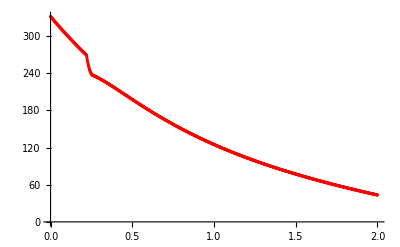

```mathematica
plotEntalpiaMPF5=ListPlot[tablicaEntalpiaMPF5,PlotStyle->Red]
```

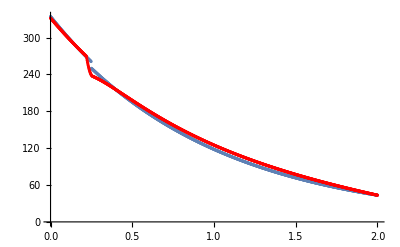

```mathematica
Show[plotEntalpiaDokladna5,plotEntalpiaMPF5]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv

### alfa = 8/10, t=1

#### temperatury

```mathematica
str6=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList6=ReadList[str6]
```

{1.64718,1.64398,1.64078,1.63759,1.6344,1.63123,1.62805,1.62489,1.62173,1.61858,1.61543,1.6123,1.60916,1.60604,1.60292,1.59981,1.5967,1.5936,1.5905,1.58742,1.58434,1.58126,1.57819,1.57513,1.57207,1.56902,1.56598,1.56294,1.55991,1.55689,1.55387,1.55086,1.54785,1.54485,1.54186,1.53887,1.53589,1.53291,1.52994,1.52698,1.52402,1.52107,1.51813,1.51519,1.51226,1.50933,1.50641,1.50349,1.50059,1.49768,1.49479,1.4919,1.48901,1.48613,1.48326,1.48039,1.47753,1.47467,1.47182,1.46898,1.46614,1.46331,1.46048,1.45766,1.45485,1.45204,1.44924,1.44644,1.44365,1.44086,1.43808,1.43531,1.43254,1.42977,1.42701,1.42426,1.42152,1.41878,1.41604,1.41331,1.41059,1.40787,1.40516,1.40245,1.39975,1.39705,1.39436,1.39167,1.38899,1.38632,1.38365,1.38099,1.37833,1.37568,1.37303,1.37039,1.36775,1.36512,1.36249,1.35987,1.35726,1.35465,1.35205,1.34945,1.34685,1.34426,1.34168,1.3391,1.33653,1.33396,1.3314,1.32885,1.32629,1.32375,1.32121,1.31867,1.31614,1.31361,1.31109,1.30858,1.30607,1.30356,1.30106,1.29857,1.29608,1.29359,1.29111,1.28864,1.28617,1.2837,1.28124,1.27879,1.27634,1.27389,1.27145,1.26902,1.26659,1.26416,1.26174,1.25933,1.25692,1.25451,1.25211,1.24972,1.24733,1.24494,1.24256,1.24018,1.23781,1.23545,1.23308,1.23073,1.22838,1.22603,1.22369,1.22135,1.21901,1.21669,1.21436,1.21204,1.20973,1.20742,1.20511,1.20281,1.20052,1.19823,1.19594,1.19366,1.19138,1.18911,1.18684,1.18458,1.18232,1.18007,1.17782,1.17557,1.17333,1.17109,1.16886,1.16664,1.16441,1.1622,1.15998,1.15777,1.15557,1.15337,1.15117,1.14898,1.14679,1.14461,1.14243,1.14026,1.13809,1.13593,1.13377,1.13161,1.12946,1.12731,1.12517,1.12303,1.12089,1.11876,1.11664,1.11452,1.1124,1.11029,1.10818,1.10607,1.10397,1.10188,1.09979,1.0977,1.09561,1.09354,1.09146,1.08939,1.08732,1.08526,1.0832,1.08115,1.0791,1.07705,1.07501,1.07297,1.07094,1.06891,1.06689,1.06487,1.06285,1.06084,1.05883,1.05682,1.05482,1.05283,1.05083,1.04885,1.04686,1.04488,1.04291,1.04093,1.03897,1.03701,1.03505,1.0331,1.03115,1.01935,1.00729,1,1,1,1,0.992482,0.9839,0.977202,0.970555,0.964825,0.960103,0.955374,0.952512,0.949695,0.947791,0.94688,0.945953,0.945012,0.944057,0.943087,0.942103,0.941106,0.940096,0.939073,0.938037,0.936989,0.935929,0.934857,0.933774,0.93268,0.931575,0.930459,0.929333,0.928197,0.927051,0.925895,0.92473,0.923555,0.922372,0.92118,0.91998,0.918771,0.917555,0.91633,0.915098,0.913858,0.912611,0.911357,0.910096,0.908829,0.907555,0.906274,0.904988,0.903696,0.902397,0.901093,0.899784,0.898469,0.897149,0.895824,0.894495,0.89316,0.891821,0.890478,0.88913,0.887778,0.886422,0.885062,0.883698,0.882331,0.88096,0.879586,0.878208,0.876828,0.875444,0.874057,0.872668,0.871275,0.869881,0.868483,0.867083,0.865681,0.864277,0.862871,0.861462,0.860052,0.858639,0.857225,0.85581,0.854392,0.852973,0.851553,0.850132,0.848709,0.847285,0.84586,0.844433,0.843006,0.841578,0.840149,0.838719,0.837289,0.835858,0.834426,0.832994,0.831562,0.830129,0.828695,0.827262,0.825828,0.824394,0.82296,0.821526,0.820092,0.818657,0.817223,0.81579,0.814356,0.812923,0.811489,0.810057,0.808624,0.807192,0.805761,0.80433,0.802899,0.801469,0.80004,0.798611,0.797183,0.795756,0.794329,0.792904,0.791479,0.790055,0.788632,0.787209,0.785788,0.784368,0.782949,0.781531,0.780114,0.778698,0.777283,0.775869,0.774457,0.773045,0.771635,0.770226,0.768819,0.767413,0.766008,0.764604,0.763202,0.761801,0.760402,0.759004,0.757607,0.756212,0.754819,0.753427,0.752036,0.750647,0.74926,0.747874,0.74649,0.745107,0.743726,0.742347,0.740969,0.739593,0.738219,0.736846,0.735475,0.734106,0.732738,0.731373,0.730009,0.728646,0.727286,0.725927,0.72457,0.723215,0.721862,0.720511,0.719161,0.717813,0.716467,0.715123,0.713781,0.712441,0.711103,0.709766,0.708432,0.707099,0.705769,0.70444,0.703113,0.701788,0.700465,0.699144,0.697825,0.696508,0.695193,0.69388,0.692569,0.69126,0.689952,0.688647,0.687344,0.686043,0.684744,0.683446,0.682151,0.680858,0.679567,0.678278,0.676991,0.675706,0.674423,0.673142,0.671863,0.670586,0.669311,0.668038,0.666768,0.665499,0.664232,0.662968,0.661705,0.660444,0.659186,0.65793,0.656675,0.655423,0.654173,0.652924,0.651678,0.650434,0.649192,0.647952,0.646714,0.645478,0.644245,0.643013,0.641783,0.640556,0.63933,0.638107,0.636885,0.635666,0.634448,0.633233,0.63202,0.630809,0.6296,0.628393,0.627188,0.625985,0.624784,0.623585,0.622388,0.621194,0.620001,0.61881,0.617622,0.616435,0.61525,0.614068,0.612887,0.611709,0.610533,0.609358,0.608186,0.607015,0.605847,0.604681,0.603517,0.602354,0.601194,0.600036,0.59888,0.597726,0.596573,0.595423,0.594275,0.593129,0.591985,0.590842,0.589702,0.588564,0.587428,0.586294,0.585161,0.584031,0.582903,0.581776,0.580652,0.57953,0.578409,0.577291,0.576174,0.57506,0.573947,0.572836,0.571728,0.570621,0.569516,0.568413,0.567312,0.566213,0.565116,0.564021,0.562928,0.561837,0.560747,0.55966,0.558574,0.557491,0.556409,0.555329,0.554251,0.553175,0.552101,0.551029,0.549959,0.54889,0.547824,0.546759,0.545696,0.544635,0.543576,0.542519,0.541463,0.54041,0.539358,0.538308,0.53726,0.536214,0.53517,0.534128,0.533087,0.532048,0.531011,0.529976,0.528943,0.527911,0.526882,0.525854,0.524828,0.523803,0.522781,0.52176,0.520742,0.519724,0.518709,0.517696,0.516684,0.515674,0.514666,0.513659,0.512655,0.511652,0.510651,0.509651,0.508654,0.507658,0.506664,0.505672,0.504681,0.503692,0.502705,0.501719,0.500736,0.499754,0.498773,0.497795,0.496818,0.495843,0.494869,0.493898,0.492928,0.491959,0.490993,0.490028,0.489064,0.488103,0.487143,0.486185,0.485228,0.484273,0.48332,0.482368,0.481418,0.48047,0.479523,0.478578,0.477635,0.476693,0.475753,0.474815,0.473878,0.472943,0.472009,0.471077,0.470147,0.469218,0.468291,0.467366,0.466442,0.465519,0.464599,0.46368,0.462762,0.461846,0.460932,0.460019,0.459108,0.458198,0.45729,0.456383,0.455478,0.454575,0.453673,0.452773,0.451874,0.450977,0.450081,0.449187,0.448294,0.447403,0.446514,0.445626,0.444739,0.443854,0.442971,0.442089,0.441209,0.44033,0.439452,0.438576,0.437702,0.436829,0.435957,0.435087,0.434219,0.433352,0.432486,0.431622,0.43076,0.429899,0.429039,0.428181,0.427324,0.426469,0.425615,0.424763,0.423912,0.423062,0.422214,0.421367,0.420522,0.419678,0.418836,0.417995,0.417156,0.416318,0.415481,0.414646,0.413812,0.412979,0.412148,0.411319,0.41049,0.409663,0.408838,0.408014,0.407191,0.40637,0.40555,0.404731,0.403914,0.403098,0.402284,0.40147,0.400659,0.399848,0.399039,0.398231,0.397425,0.39662,0.395816,0.395014,0.394213,0.393413,0.392615,0.391818,0.391022,0.390228,0.389435,0.388643,0.387853,0.387063,0.386276,0.385489,0.384704,0.38392,0.383137,0.382356,0.381576,0.380797,0.38002,0.379243,0.378468,0.377695,0.376922,0.376151,0.375381,0.374613,0.373845,0.373079,0.372315,0.371551,0.370789,0.370028,0.369268,0.368509,0.367752,0.366996,0.366241,0.365487,0.364735,0.363983,0.363233,0.362485,0.361737,0.360991,0.360246,0.359502,0.358759,0.358018,0.357277,0.356538,0.3558,0.355063,0.354328,0.353594,0.35286,0.352128,0.351398,0.350668,0.34994,0.349212,0.348486,0.347761,0.347037,0.346315,0.345593,0.344873,0.344154,0.343436,0.342719,0.342003,0.341289,0.340575,0.339863,0.339152,0.338442,0.337733,0.337025,0.336319,0.335613,0.334909,0.334205,0.333503,0.332802,0.332102,0.331403,0.330706,0.330009,0.329314,0.328619,0.327926,0.327234,0.326542,0.325852,0.325163,0.324476,0.323789,0.323103,0.322418,0.321735,0.321052,0.320371,0.319691,0.319011,0.318333,0.317656,0.31698,0.316305,0.315631,0.314958,0.314286,0.313615,0.312945,0.312277,0.311609,0.310942,0.310277,0.309612,0.308949,0.308286,0.307624,0.306964,0.306304,0.305646,0.304989,0.304332,0.303677,0.303022,0.302369,0.301717,0.301065,0.300415,0.299766,0.299117,0.29847,0.297824,0.297178,0.296534,0.29589,0.295248,0.294607,0.293966,0.293327,0.292688,0.292051,0.291414,0.290778,0.290144,0.28951,0.288878,0.288246,0.287615,0.286985,0.286356,0.285729,0.285102,0.284476,0.283851,0.283227,0.282603,0.281981,0.28136,0.28074,0.28012,0.279502,0.278884,0.278268,0.277652,0.277037,0.276424,0.275811,0.275199,0.274588,0.273978,0.273368,0.27276,0.272153,0.271546,0.270941,0.270336,0.269732,0.269129,0.268527,0.267926,0.267326,0.266727,0.266129,0.265531,0.264935,0.264339,0.263744,0.26315,0.262557,0.261965,0.261374,0.260783,0.260194,0.259605,0.259017,0.25843,0.257844,0.257259,0.256675,0.256091,0.255508,0.254927,0.254346,0.253766,0.253187,0.252608,0.252031,0.251454,0.250878,0.250303,0.249729,0.249156,0.248583,0.248012,0.247441,0.246871,0.246302,0.245734,0.245166,0.2446,0.244034,0.243469,0.242905,0.242342,0.241779,0.241217,0.240656,0.240096,0.239537,0.238979,0.238421,0.237864,0.237308,0.236753,0.236199,0.235645,0.235092,0.23454,0.233989,0.233439,0.232889,0.23234,0.231792,0.231245,0.230699,0.230153,0.229608,0.229064,0.228521,0.227978,0.227436,0.226895,0.226355,0.225816,0.225277,0.224739,0.224202,0.223666,0.22313}

```mathematica
strList6={1.6471808914,1.643976752,1.64077921,1.6375882485,1.634403853,1.6312260107,1.628054709,1.6248899351,1.6217316747,1.6185799095,1.6154346269,1.6122958142,1.6091634589,1.6060375486,1.6029180709,1.5998050066,1.5966983429,1.5935980672,1.590504167,1.5874166299,1.5843354437,1.5812605962,1.5781920685,1.5751298481,1.5720739227,1.5690242798,1.5659809074,1.5629437935,1.5599129196,1.5568882735,1.553869843,1.5508576158,1.5478515801,1.544851718,1.5418580174,1.5388704662,1.5358890524,1.5329137642,1.5299445842,1.5269815003,1.5240245006,1.5210735732,1.5181287013,1.5151898728,1.5122570761,1.5093302993,1.5064095308,1.5034947537,1.5005859565,1.4976831274,1.4947862549,1.4918953224,1.4890103184,1.4861312313,1.4832580496,1.4803907572,1.4775293424,1.4746737939,1.4718241003,1.4689802456,1.4661422183,1.4633100073,1.4604836011,1.457662984,1.4548481447,1.452039072,1.4492357548,1.4464381774,1.4436463286,1.4408601974,1.4380797683,1.4353050303,1.4325359723,1.4297725833,1.427014848,1.4242627555,1.4215162949,1.4187754553,1.4160402216,1.4133105828,1.4105865283,1.407868043,1.4051551162,1.4024477371,1.3997458909,1.397049567,1.3943587546,1.3916734432,1.388993618,1.3863192684,1.3836503839,1.38098695,1.3783289561,1.3756763917,1.3730292425,1.370387498,1.3677511478,1.3651201777,1.3624945771,1.3598743358,1.3572594435,1.354649886,1.352045653,1.3494467343,1.3468531158,1.3442647874,1.3416817388,1.3391039563,1.3365314295,1.3339641485,1.3314020994,1.3288452722,1.3262936568,1.3237472395,1.3212060104,1.3186699594,1.3161390731,1.3136133414,1.3110927545,1.3085772989,1.3060669646,1.303561742,1.3010616177,1.2985665817,1.2960766245,1.2935917326,1.2911118964,1.2886371028,1.286167342,1.2837026043,1.2812428768,1.2787881496,1.2763384133,1.273893655,1.2714538648,1.2690190336,1.2665891482,1.2641641992,1.2617441772,1.2593290694,1.2569188663,1.2545135585,1.2521131335,1.2497175817,1.2473268939,1.2449410575,1.2425600631,1.2401838983,1.2378125537,1.2354460203,1.2330842854,1.23072734,1.2283751748,1.2260277776,1.2236851392,1.2213472505,1.2190140993,1.2166856765,1.21436197,1.2120429705,1.2097286694,1.2074190543,1.2051141164,1.2028138468,1.2005182334,1.1982272674,1.1959409368,1.1936592327,1.1913821465,1.1891096662,1.186841783,1.1845784884,1.1823197703,1.1800656203,1.1778160265,1.1755709803,1.1733304732,1.1710944935,1.1688630326,1.1666360821,1.1644136304,1.162195669,1.1599821865,1.1577731744,1.1555686244,1.153368525,1.151172868,1.1489816452,1.1467948451,1.1446124595,1.1424344774,1.1402608904,1.1380916906,1.1359268668,1.1337664109,1.131610315,1.1294585681,1.1273111623,1.1251680867,1.1230293334,1.1208948947,1.1187647599,1.1166389213,1.1145173683,1.1124000934,1.110287089,1.1081783448,1.1060738533,1.1039736074,1.1018775969,1.0997858148,1.097698251,1.0956148986,1.093535751,1.0914607984,1.0893900346,1.0873234502,1.0852610388,1.0832027948,1.0811487095,1.0790987772,1.07705299,1.0750113427,1.0729738312,1.0709404484,1.0689111903,1.0668860515,1.0648650291,1.0628481223,1.0608353272,1.0588266433,1.0568220744,1.0548216198,1.0528252868,1.050833081,1.0488450105,1.0468610981,1.0448813605,1.0429058348,1.0409345648,1.0389675966,1.0370050695,1.0350471124,1.0330952281,1.0311523258,1.0193491765,1.0072850742,1,1,1,1,0.9924816398,0.9838995945,0.9772019821,0.9705552253,0.964825221,0.9601031445,0.9553744858,0.9525124472,0.9496953107,0.947791276,0.9468799375,0.9459534729,0.9450122239,0.9440565257,0.9430867073,0.9421030913,0.9411059945,0.9400957275,0.939072595,0.9380368961,0.9369889242,0.935928967,0.9348573069,0.9337742211,0.9326799812,0.931574854,0.930459101,0.9293329788,0.9281967392,0.9270506293,0.9258948912,0.9247297626,0.9235554769,0.9223722626,0.9211803442,0.9199799419,0.9187712715,0.9175545448,0.9163299696,0.9150977499,0.9138580853,0.9126111722,0.9113572028,0.9100963658,0.9088288462,0.9075548257,0.9062744823,0.9049879906,0.9036955219,0.9023972441,0.9010933222,0.8997839176,0.8984691889,0.8971492916,0.8958243781,0.8944945979,0.8931600976,0.8918210211,0.8904775094,0.8891297008,0.887777731,0.8864217328,0.8850618368,0.8836981708,0.8823308603,0.8809600283,0.8795857952,0.8782082794,0.8768275967,0.8754438609,0.8740571834,0.8726676735,0.8712754384,0.869880583,0.8684832103,0.8670834214,0.8656813152,0.8642769887,0.862870537,0.8614620535,0.8600516295,0.8586393546,0.8572253167,0.8558096019,0.8543922946,0.8529734774,0.8515532314,0.8501316362,0.8487087696,0.8472847079,0.8458595258,0.8444332969,0.8430060927,0.8415779839,0.8401490392,0.8387193264,0.8372889116,0.8358578598,0.8344262346,0.8329940981,0.8315615115,0.8301285346,0.828695226,0.8272616429,0.8258278417,0.8243938774,0.8229598039,0.821525674,0.8200915396,0.8186574512,0.8172234586,0.8157896102,0.8143559537,0.8129225357,0.8114894019,0.8100565969,0.8086241644,0.8071921473,0.8057605876,0.8043295262,0.8028990034,0.8014690585,0.80003973,0.7986110556,0.7971830721,0.7957558156,0.7943293214,0.7929036242,0.7914787577,0.790054755,0.7886316484,0.7872094697,0.7857882497,0.7843680188,0.7829488067,0.7815306422,0.7801135537,0.7786975689,0.777282715,0.7758690183,0.7744565049,0.7730452,0.7716351283,0.770226314,0.7688187808,0.7674125517,0.7660076493,0.7646040957,0.7632019124,0.7618011204,0.7604017403,0.7590037921,0.7576072954,0.7562122693,0.7548187326,0.7534267034,0.7520361996,0.7506472384,0.7492598369,0.7478740116,0.7464897786,0.7451071535,0.7437261518,0.7423467885,0.740969078,0.7395930346,0.7382186721,0.7368460041,0.7354750436,0.7341058036,0.7327382964,0.7313725342,0.7300085289,0.7286462919,0.7272858345,0.7259271674,0.7245703014,0.7232152468,0.7218620135,0.7205106113,0.7191610496,0.7178133377,0.7164674845,0.7151234986,0.7137813885,0.7124411623,0.7111028279,0.709766393,0.7084318651,0.7070992513,0.7057685587,0.704439794,0.7031129637,0.7017880742,0.7004651315,0.6991441417,0.6978251104,0.696508043,0.6951929451,0.6938798216,0.6925686775,0.6912595175,0.6899523463,0.6886471683,0.6873439876,0.6860428084,0.6847436345,0.6834464697,0.6821513176,0.6808581815,0.6795670648,0.6782779705,0.6769909016,0.675705861,0.6744228513,0.673141875,0.6718629347,0.6705860325,0.6693111706,0.668038351,0.6667675757,0.6654988463,0.6642321646,0.662967532,0.6617049501,0.66044442,0.659185943,0.6579295201,0.6566751524,0.6554228407,0.6541725858,0.6529243883,0.6516782488,0.6504341679,0.6491921458,0.6479521829,0.6467142794,0.6454784353,0.6442446507,0.6430129256,0.6417832598,0.640555653,0.639330105,0.6381066154,0.6368851837,0.6356658094,0.6344484919,0.6332332304,0.6320200243,0.6308088727,0.6295997747,0.6283927294,0.6271877358,0.6259847928,0.6247838992,0.6235850538,0.6223882554,0.6211935026,0.6200007941,0.6188101285,0.6176215042,0.6164349197,0.6152503734,0.6140678636,0.6128873888,0.6117089471,0.6105325367,0.6093581559,0.6081858026,0.6070154751,0.6058471713,0.6046808892,0.6035166268,0.6023543819,0.6011941525,0.6000359363,0.5988797312,0.5977255348,0.596573345,0.5954231594,0.5942749756,0.5931287912,0.5919846039,0.5908424111,0.5897022105,0.5885639994,0.5874277753,0.5862935357,0.5851612779,0.5840309993,0.5829026973,0.5817763691,0.5806520121,0.5795296236,0.5784092006,0.5772907406,0.5761742406,0.5750596979,0.5739471095,0.5728364727,0.5717277844,0.5706210418,0.569516242,0.568413382,0.5673124588,0.5662134695,0.5651164109,0.5640212802,0.5629280742,0.5618367899,0.5607474241,0.5596599739,0.5585744361,0.5574908075,0.5564090851,0.5553292657,0.5542513461,0.5531753231,0.5521011936,0.5510289543,0.5499586021,0.5488901336,0.5478235457,0.5467588352,0.5456959987,0.5446350329,0.5435759347,0.5425187007,0.5414633277,0.5404098122,0.5393581511,0.5383083409,0.5372603784,0.5362142602,0.5351699829,0.5341275433,0.5330869379,0.5320481634,0.5310112164,0.5299760936,0.5289427915,0.5279113068,0.5268816361,0.5258537759,0.5248277229,0.5238034737,0.5227810248,0.5217603729,0.5207415145,0.5197244462,0.5187091645,0.5176956661,0.5166839475,0.5156740053,0.514665836,0.5136594361,0.5126548024,0.5116519313,0.5106508193,0.509651463,0.508653859,0.5076580038,0.506663894,0.5056715261,0.5046808967,0.5036920023,0.5027048394,0.5017194047,0.5007356945,0.4997537056,0.4987734344,0.4977948775,0.4968180315,0.4958428928,0.494869458,0.4938977238,0.4929276865,0.4919593428,0.4909926893,0.4900277224,0.4890644388,0.488102835,0.4871429075,0.4861846529,0.4852280678,0.4842731487,0.4833198923,0.482368295,0.4814183534,0.4804700642,0.4795234238,0.4785784289,0.477635076,0.4766933618,0.4757532828,0.4748148355,0.4738780167,0.4729428228,0.4720092505,0.4710772964,0.4701469571,0.4692182291,0.4682911092,0.4673655939,0.4664416798,0.4655193635,0.4645986417,0.4636795111,0.4627619681,0.4618460096,0.460931632,0.4600188322,0.4591076066,0.4581979519,0.4572898649,0.4563833422,0.4554783804,0.4545749762,0.4536731263,0.4527728273,0.451874076,0.450976869,0.450081203,0.4491870748,0.4482944809,0.4474034182,0.4465138833,0.445625873,0.4447393839,0.4438544129,0.4429709565,0.4420890116,0.4412085749,0.4403296431,0.439452213,0.4385762814,0.437701845,0.4368289005,0.4359574448,0.4350874746,0.4342189866,0.4333519778,0.4324864448,0.4316223845,0.4307597937,0.4298986691,0.4290390076,0.4281808061,0.4273240612,0.4264687699,0.425614929,0.4247625354,0.4239115858,0.4230620771,0.4222140062,0.42136737,0.4205221653,0.4196783889,0.4188360379,0.4179951089,0.4171555991,0.4163175051,0.415480824,0.4146455526,0.4138116879,0.4129792268,0.4121481662,0.411318503,0.4104902342,0.4096633567,0.4088378674,0.4080137634,0.4071910415,0.4063696988,0.4055497322,0.4047311386,0.4039139152,0.4030980588,0.4022835665,0.4014704352,0.400658662,0.3998482438,0.3990391778,0.3982314608,0.3974250901,0.3966200625,0.3958163751,0.3950140251,0.3942130093,0.393413325,0.3926149691,0.3918179388,0.391022231,0.390227843,0.3894347718,0.3886430144,0.3878525681,0.3870634298,0.3862755968,0.3854890661,0.3847038349,0.3839199002,0.3831372593,0.3823559093,0.3815758474,0.3807970706,0.3800195762,0.3792433613,0.3784684231,0.3776947588,0.3769223656,0.3761512406,0.3753813811,0.3746127843,0.3738454474,0.3730793676,0.3723145421,0.3715509681,0.370788643,0.3700275639,0.3692677282,0.3685091329,0.3677517755,0.3669956531,0.3662407631,0.3654871028,0.3647346693,0.3639834601,0.3632334723,0.3624847034,0.3617371506,0.3609908112,0.3602456826,0.3595017621,0.3587590469,0.3580175346,0.3572772224,0.3565381076,0.3558001876,0.3550634599,0.3543279216,0.3535935704,0.3528604034,0.3521284181,0.351397612,0.3506679823,0.3499395266,0.3492122422,0.3484861265,0.347761177,0.3470373911,0.3463147662,0.3455932998,0.3448729893,0.3441538323,0.343435826,0.3427189681,0.342003256,0.3412886871,0.340575259,0.3398629692,0.3391518151,0.3384417942,0.3377329041,0.3370251423,0.3363185062,0.3356129935,0.3349086016,0.3342053282,0.3335031707,0.3328021266,0.3321021937,0.3314033693,0.3307056511,0.3300090367,0.3293135236,0.3286191095,0.3279257918,0.3272335683,0.3265424366,0.3258523941,0.3251634386,0.3244755677,0.323788779,0.3231030701,0.3224184388,0.3217348825,0.321052399,0.320370986,0.319690641,0.3190113619,0.3183331461,0.3176559916,0.3169798958,0.3163048565,0.3156308715,0.3149579383,0.3142860548,0.3136152187,0.3129454276,0.3122766793,0.3116089715,0.310942302,0.3102766685,0.3096120688,0.3089485006,0.3082859617,0.3076244498,0.3069639628,0.3063044984,0.3056460544,0.3049886286,0.3043322187,0.3036768227,0.3030224383,0.3023690633,0.3017166955,0.3010653328,0.300414973,0.2997656139,0.2991172534,0.2984698894,0.2978235196,0.297178142,0.2965337544,0.2958903547,0.2952479407,0.2946065104,0.2939660617,0.2933265924,0.2926881004,0.2920505836,0.2914140401,0.2907784675,0.290143864,0.2895102275,0.2888775557,0.2882458468,0.2876150986,0.2869853092,0.2863564764,0.2857285982,0.2851016726,0.2844756976,0.2838506711,0.2832265911,0.2826034557,0.2819812628,0.2813600104,0.2807396965,0.2801203192,0.2795018765,0.2788843663,0.2782677868,0.2776521359,0.2770374117,0.2764236122,0.2758107356,0.2751987798,0.2745877429,0.273977623,0.2733684182,0.2727601265,0.272152746,0.2715462749,0.2709407111,0.2703360529,0.2697322983,0.2691294455,0.2685274925,0.2679264375,0.2673262786,0.2667270139,0.2661286417,0.26553116,0.2649345669,0.2643388607,0.2637440396,0.2631501015,0.2625570449,0.2619648677,0.2613735683,0.2607831448,0.2601935954,0.2596049182,0.2590171116,0.2584301737,0.2578441027,0.2572588969,0.2566745544,0.2560910736,0.2555084526,0.2549266897,0.2543457832,0.2537657313,0.2531865322,0.2526081843,0.2520306857,0.2514540349,0.25087823,0.2503032693,0.2497291512,0.2491558739,0.2485834357,0.248011835,0.24744107,0.2468711391,0.2463020407,0.2457337729,0.2451663342,0.244599723,0.2440339374,0.243468976,0.242904837,0.2423415189,0.24177902,0.2412173386,0.2406564731,0.240096422,0.2395371836,0.2389787562,0.2384211384,0.2378643285,0.2373083249,0.236753126,0.2361987303,0.2356451361,0.235092342,0.2345403463,0.2339891474,0.2334387439,0.2328891342,0.2323403167,0.2317922898,0.2312450522,0.2306986022,0.2301529383,0.229608059,0.2290639627,0.2285206481,0.2279781135,0.2274363575,0.2268953785,0.2263551752,0.225815746,0.2252770894,0.224739204,0.2242020883,0.2236657408,0.2231301601};
```

```mathematica
tablicaTemperaturMPF6=Table[{i*0.002,strList6[[i+1]]},{i,0,1000}];
```

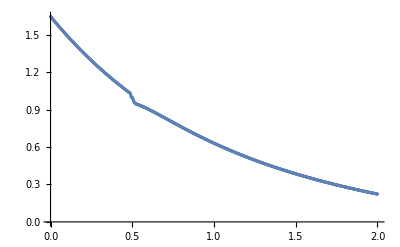

```mathematica
plotTemperaturyMPF6=ListPlot[tablicaTemperaturMPF6]
```

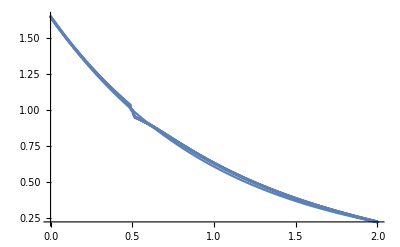

```mathematica
Show[plotTemperaturyDokladne2,plotTemperaturyMPF6]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(Gamma[0.2]*(lambdaL-lambdaS))/(5*aL*t^(1/5));
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t],temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna6=Table[{i*0.002,entalpia[u1[i*0.002,1],1]},{i,0,1000}];
```

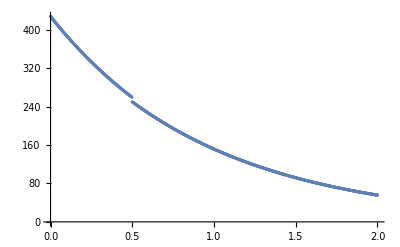

```mathematica
plotEntalpiaDokladna6=ListPlot[tablicaEntalpiaDokladna6]
```

```mathematica
strE=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE6=ReadList[strE]
```

{427.449,426.616,425.784,424.955,424.127,423.3,422.476,421.653,420.832,420.012,419.195,418.379,417.564,416.751,415.94,415.131,414.323,413.517,412.713,411.91,411.109,410.309,409.512,408.715,407.921,407.128,406.337,405.547,404.759,403.973,403.188,402.405,401.623,400.843,400.065,399.288,398.513,397.739,396.967,396.197,395.428,394.661,393.895,393.131,392.369,391.608,390.848,390.09,389.334,388.579,387.826,387.074,386.324,385.576,384.829,384.083,383.339,382.597,381.856,381.117,380.379,379.642,378.907,378.174,377.442,376.712,375.983,375.256,374.53,373.805,373.082,372.361,371.641,370.923,370.206,369.49,368.776,368.063,367.352,366.642,365.934,365.227,364.522,363.818,363.116,362.415,361.715,361.017,360.32,359.625,358.931,358.238,357.547,356.858,356.169,355.482,354.797,354.113,353.43,352.749,352.069,351.391,350.714,350.038,349.363,348.691,348.019,347.349,346.68,346.012,345.346,344.681,344.018,343.356,342.695,342.036,341.378,340.721,340.066,339.412,338.759,338.108,337.458,336.809,336.162,335.516,334.871,334.227,333.585,332.944,332.305,331.667,331.03,330.394,329.76,329.127,328.495,327.864,327.235,326.607,325.981,325.355,324.731,324.108,323.487,322.866,322.247,321.63,321.013,320.398,319.784,319.171,318.559,317.949,317.34,316.732,316.125,315.52,314.916,314.313,313.711,313.111,312.511,311.913,311.316,310.721,310.126,309.533,308.941,308.35,307.761,307.172,306.585,305.999,305.414,304.83,304.248,303.666,303.086,302.507,301.929,301.353,300.777,300.203,299.63,299.058,298.487,297.917,297.348,296.781,296.215,295.65,295.086,294.523,293.961,293.4,292.841,292.283,291.725,291.169,290.614,290.061,289.508,288.956,288.406,287.856,287.308,286.761,286.215,285.67,285.126,284.583,284.042,283.501,282.961,282.423,281.886,281.35,280.814,280.28,279.747,279.215,278.685,278.155,277.626,277.099,276.572,276.047,275.522,274.999,274.477,273.955,273.435,272.916,272.398,271.881,271.366,270.851,270.337,269.825,269.313,268.803,268.294,267.786,267.281,264.212,261.076,257.946,255.302,252.665,250.268,248.12,245.975,244.3,242.639,241.206,240.026,238.844,238.128,237.424,236.948,236.72,236.488,236.253,236.014,235.772,235.526,235.276,235.024,234.768,234.509,234.247,233.982,233.714,233.444,233.17,232.894,232.615,232.333,232.049,231.763,231.474,231.182,230.889,230.593,230.295,229.995,229.693,229.389,229.082,228.774,228.465,228.153,227.839,227.524,227.207,226.889,226.569,226.247,225.924,225.599,225.273,224.946,224.617,224.287,223.956,223.624,223.29,222.955,222.619,222.282,221.944,221.605,221.265,220.925,220.583,220.24,219.896,219.552,219.207,218.861,218.514,218.167,217.819,217.47,217.121,216.771,216.42,216.069,215.718,215.366,215.013,214.66,214.306,213.952,213.598,213.243,212.888,212.533,212.177,211.821,211.465,211.108,210.752,210.394,210.037,209.68,209.322,208.964,208.607,208.249,207.89,207.532,207.174,206.815,206.457,206.098,205.74,205.381,205.023,204.664,204.306,203.947,203.589,203.231,202.872,202.514,202.156,201.798,201.44,201.082,200.725,200.367,200.01,199.653,199.296,198.939,198.582,198.226,197.87,197.514,197.158,196.802,196.447,196.092,195.737,195.383,195.028,194.674,194.321,193.967,193.614,193.261,192.909,192.557,192.205,191.853,191.502,191.151,190.8,190.45,190.1,189.751,189.402,189.053,188.705,188.357,188.009,187.662,187.315,186.969,186.622,186.277,185.932,185.587,185.242,184.898,184.555,184.212,183.869,183.526,183.185,182.843,182.502,182.162,181.821,181.482,181.143,180.804,180.466,180.128,179.79,179.453,179.117,178.781,178.445,178.11,177.776,177.442,177.108,176.775,176.442,176.11,175.778,175.447,175.116,174.786,174.456,174.127,173.798,173.47,173.142,172.815,172.488,172.162,171.836,171.511,171.186,170.862,170.538,170.215,169.892,169.569,169.248,168.926,168.606,168.285,167.966,167.647,167.328,167.01,166.692,166.375,166.058,165.742,165.426,165.111,164.796,164.482,164.169,163.856,163.543,163.231,162.92,162.609,162.298,161.988,161.679,161.37,161.061,160.753,160.446,160.139,159.833,159.527,159.221,158.916,158.612,158.308,158.005,157.702,157.4,157.098,156.797,156.496,156.196,155.896,155.597,155.298,155.,154.703,154.405,154.109,153.813,153.517,153.222,152.927,152.633,152.34,152.046,151.754,151.462,151.17,150.879,150.589,150.299,150.009,149.72,149.431,149.143,148.856,148.569,148.282,147.996,147.711,147.426,147.141,146.857,146.573,146.29,146.008,145.726,145.444,145.163,144.882,144.602,144.323,144.044,143.765,143.487,143.209,142.932,142.655,142.379,142.103,141.828,141.553,141.279,141.005,140.732,140.459,140.187,139.915,139.644,139.373,139.102,138.832,138.563,138.294,138.025,137.757,137.49,137.223,136.956,136.69,136.424,136.159,135.894,135.63,135.366,135.102,134.84,134.577,134.315,134.054,133.792,133.532,133.272,133.012,132.753,132.494,132.236,131.978,131.72,131.463,131.207,130.951,130.695,130.44,130.185,129.931,129.677,129.424,129.171,128.919,128.666,128.415,128.164,127.913,127.663,127.413,127.163,126.915,126.666,126.418,126.17,125.923,125.676,125.43,125.184,124.938,124.693,124.449,124.205,123.961,123.717,123.474,123.232,122.99,122.748,122.507,122.266,122.026,121.786,121.546,121.307,121.068,120.83,120.592,120.355,120.118,119.881,119.645,119.409,119.173,118.938,118.704,118.47,118.236,118.002,117.769,117.537,117.305,117.073,116.841,116.61,116.38,116.15,115.92,115.69,115.462,115.233,115.005,114.777,114.549,114.322,114.096,113.87,113.644,113.418,113.193,112.969,112.744,112.52,112.297,112.074,111.851,111.628,111.406,111.185,110.964,110.743,110.522,110.302,110.082,109.863,109.644,109.425,109.207,108.989,108.772,108.555,108.338,108.122,107.906,107.69,107.475,107.26,107.045,106.831,106.617,106.404,106.191,105.978,105.766,105.554,105.342,105.131,104.92,104.709,104.499,104.289,104.079,103.87,103.661,103.453,103.245,103.037,102.83,102.623,102.416,102.209,102.003,101.798,101.592,101.387,101.183,100.978,100.775,100.571,100.368,100.165,99.9621,99.7598,99.5579,99.3563,99.155,98.9541,98.7535,98.5533,98.3533,98.1537,97.9545,97.7556,97.557,97.3587,97.1608,96.9631,96.7659,96.5689,96.3723,96.176,95.98,95.7843,95.589,95.394,95.1993,95.0049,94.8108,94.6171,94.4237,94.2306,94.0378,93.8453,93.6532,93.4614,93.2698,93.0786,92.8877,92.6972,92.5069,92.3169,92.1273,91.9379,91.7489,91.5602,91.3718,91.1837,90.9959,90.8084,90.6212,90.4343,90.2477,90.0614,89.8754,89.6898,89.5044,89.3193,89.1345,88.95,88.7659,88.582,88.3984,88.2151,88.0321,87.8494,87.667,87.4849,87.3031,87.1215,86.9403,86.7593,86.5787,86.3983,86.2182,86.0385,85.859,85.6797,85.5008,85.3222,85.1438,84.9657,84.788,84.6104,84.4332,84.2563,84.0796,83.9032,83.7272,83.5513,83.3758,83.2005,83.0255,82.8508,82.6764,82.5023,82.3284,82.1548,81.9814,81.8084,81.6356,81.4631,81.2909,81.1189,80.9472,80.7758,80.6046,80.4337,80.2631,80.0927,79.9227,79.7528,79.5833,79.414,79.245,79.0762,78.9077,78.7395,78.5715,78.4038,78.2364,78.0692,77.9022,77.7356,77.5692,77.403,77.2371,77.0715,76.9061,76.741,76.5761,76.4115,76.2472,76.0831,75.9192,75.7556,75.5923,75.4292,75.2663,75.1037,74.9414,74.7793,74.6175,74.4559,74.2945,74.1334,73.9726,73.812,73.6516,73.4915,73.3316,73.172,73.0126,72.8535,72.6946,72.536,72.3776,72.2194,72.0615,71.9038,71.7463,71.5891,71.4321,71.2754,71.1189,70.9627,70.8066,70.6509,70.4953,70.34,70.1849,70.0301,69.8755,69.7211,69.5669,69.413,69.2594,69.1059,68.9527,68.7997,68.6469,68.4944,68.3421,68.19,68.0382,67.8866,67.7352,67.584,67.4331,67.2824,67.1319,66.9816,66.8316,66.6818,66.5322,66.3828,66.2336,66.0847,65.936,65.7875,65.6393,65.4912,65.3434,65.1958,65.0484,64.9012,64.7543,64.6075,64.461,64.3147,64.1686,64.0228,63.8771,63.7317,63.5864,63.4414,63.2966,63.152,63.0077,62.8635,62.7196,62.5758,62.4323,62.289,62.1459,62.003,61.8603,61.7178,61.5755,61.4334,61.2916,61.1499,61.0085,60.8672,60.7262,60.5854,60.4448,60.3043,60.1641,60.0241,59.8843,59.7447,59.6053,59.4661,59.3271,59.1883,59.0497,58.9113,58.7731,58.6351,58.4973,58.3597,58.2223,58.0851,57.9481,57.8113,57.6747,57.5382,57.402,57.266,57.1302,56.9945,56.8591,56.7238,56.5888,56.4539,56.3193,56.1848,56.0505,55.9164,55.7825}

```mathematica
strListE6={427.4487191763,426.6156429465,425.7842820147,424.9546320396,424.126689206,423.3004502114,422.4759117599,421.653070562,420.8319228339,420.0124639004,419.1946904167,418.3785991091,417.5641867362,416.7514500632,415.9403858619,415.1309891286,414.3232565703,413.5171849004,412.7127708391,411.9100111887,411.1089027738,410.3094424253,409.5116252227,408.7154479297,407.920907317,407.1280001618,406.3367233366,405.5470737238,404.7590465194,403.9726385365,403.1878465943,402.4046675201,401.6230982382,400.8431340937,400.06477194,399.2880086371,398.5128410513,397.7392661244,396.9672793068,396.1968774911,395.4280575764,394.6608164683,393.8951497532,393.1310543553,392.3685272053,391.6075652402,390.8481654221,390.0903233937,389.3340361167,388.5793005587,387.826113695,387.0744712452,386.3243702012,385.5758075608,384.8287803293,384.0832842834,383.3393164444,382.5968738399,381.8559535048,381.1165512703,380.3786641869,379.6422893112,378.9074237077,378.1740632593,377.4422050454,376.7118461511,375.9829836701,375.2556135352,374.5297328538,373.8053387401,373.0824271815,372.3609952927,371.6410402091,370.9225590738,370.2055479056,369.4900038612,368.7759241042,368.0633058057,367.3521450284,366.6424389561,365.9341847811,365.2273786027,364.5220176248,363.8180990595,363.1156190664,362.4145748446,361.7149636261,361.016782651,360.3200280916,359.6246971997,358.9307872358,358.2382944152,357.5472159993,356.8575492684,356.169290485,355.4824369147,354.7969858573,354.112933619,353.4302774722,352.7490147359,352.0691427373,351.390657777,350.7135571936,350.0378383338,349.3634975307,348.6905321385,348.0189395237,347.3487160539,346.679859096,346.0123660357,345.3462332731,344.6814581889,344.0180381883,343.355969701,342.6952501237,342.0358768809,341.3778464297,340.7211561845,340.0658035887,339.4117851251,338.7590982269,338.1077403566,337.4577080204,336.808998672,336.1616097927,335.5155379102,334.8707805001,334.2273341621,333.5851963441,332.9443645446,332.3048353816,331.6666063216,331.0296748871,330.3940377131,329.7596922845,329.1266361488,328.4948659567,327.8643792168,327.2351734974,326.6072454633,325.9805926503,325.355212645,324.7311021252,324.1082586548,323.4866798387,322.8663623664,322.2473038311,321.629500985,321.012951399,320.3976526963,319.7836016388,319.1707958156,318.5592328808,317.9489096049,317.3398236087,316.7319725646,316.125353251,315.519963321,314.9157996126,314.3128597636,313.7111414612,313.1106415492,312.5113576849,311.9132875889,311.3164281105,310.7207769406,310.1263309863,309.5330879356,308.9410455162,308.3502006392,307.7605510114,307.1720943979,306.5848277137,305.9987486951,305.413854314,304.8301423104,304.2476104605,303.6662557395,303.086075907,302.5070687808,301.9292313391,301.3525613731,300.7770559176,300.2027127686,299.6295297622,299.0575039366,298.4866331092,297.9169151634,297.3483471413,296.7809269023,296.2146515472,295.6495189358,295.08552698,294.5226727862,293.9609542464,293.4003693225,292.8409151283,292.2825896138,291.7253899568,291.1693140963,290.6143600489,290.0605250048,289.507806966,288.9562031941,288.4057116967,287.8563305576,287.3080570606,286.7608892721,286.2148253575,285.6698626303,285.1259992724,284.5832326929,284.0415610555,283.5009826761,282.9614950183,282.4230964172,281.8857844684,281.3495575098,280.8144140807,280.2803518816,279.7473694863,279.2154648222,278.6846365285,278.1548835485,277.6262040082,277.0985969001,276.5720608179,276.0465949949,275.5221992098,274.9988724881,274.4766146908,273.9554267615,273.4353085662,272.9162619926,272.3982884715,271.8813901549,271.3655729239,270.8508411481,270.3372044828,269.8246742763,269.3132625373,268.8030055052,268.2939366475,267.7864467211,267.2812921393,264.2124733083,261.0758067035,257.9464096632,255.3018657797,252.6653791516,250.2679267037,248.120409962,245.974898634,244.3004955187,242.6388063331,241.2063052576,240.0257861329,238.8436214613,238.1281118056,237.4238276639,236.947819007,236.719984374,236.4883682188,236.2530559631,236.0141314188,235.7716768169,235.525772837,235.2764986364,235.0239318777,234.7681487569,234.5092240301,234.2472310405,233.9822417444,233.7143267369,233.4435552769,233.1699953121,232.8937135031,232.6147752474,232.3332447025,232.0491848089,231.762657313,231.4737227886,231.1824406591,230.8888692186,230.5930656528,230.2950860597,229.9949854692,229.6928178636,229.3886361966,229.0824924124,228.7744374642,228.4645213331,228.1527930455,227.8393006911,227.5240914404,227.2072115611,226.8887064357,226.5686205773,226.2469976456,225.9238804633,225.5993110312,225.2733305435,224.9459794027,224.6172972345,224.2873229019,223.9560945195,223.6236494675,223.2900244049,222.9552552835,222.6193773603,222.282425211,221.9444327423,221.6054332045,221.2654592033,220.9245427124,220.5827150845,220.2400070635,219.8964487952,219.5520698389,219.2068991779,218.8609652305,218.5142958603,218.1669183865,217.8188595941,217.4701457438,217.1208025816,216.7708553486,216.4203287903,216.0692471656,215.7176342561,215.365513375,215.0129073754,214.6598386593,214.3063291859,213.9524004797,213.5980736384,213.2433693415,212.8883078573,212.5329090512,212.1771923925,211.8211769626,211.4648814615,211.1083242154,210.7515231832,210.3944959639,210.0372598026,209.6798315979,209.3222279076,208.9644649555,208.6065586376,208.248524528,207.890377885,207.5321336571,207.1738064887,206.8154107255,206.4569604207,206.0984693398,205.7399509663,205.381418507,205.022884897,204.6643628049,204.3058646377,203.9474025456,203.5889884271,203.2306339334,202.8723504732,202.514149217,202.1560411021,201.7980368361,201.4401469019,201.0823815618,200.7247508614,200.3672646338,200.0099325033,199.65276389,199.2957680128,198.9389538938,198.5823303616,198.2259060551,197.869689427,197.5136887475,197.1579121072,196.8023674211,196.4470624315,196.0920047113,195.7372016675,195.3826605436,195.0283884235,194.674392234,194.3206787479,193.9672545867,193.614126224,193.2612999876,192.9087820625,192.556578494,192.2046951896,191.8531379223,191.5019123325,191.151023931,190.8004781012,190.4502801017,190.1004350683,189.7509480166,189.4018238444,189.0530673335,188.7046831523,188.3566758577,188.0090498972,187.6618096114,187.3149592353,186.9685029009,186.6224446389,186.2767883807,185.9315379603,185.5866971159,185.2422694921,184.8982586416,184.5546680265,184.2115010208,183.8687609114,183.5264509,183.1845741049,182.8431335623,182.502132228,182.1615729791,181.821458615,181.4817918596,181.1425753622,180.803811699,180.4655033747,180.1276528237,179.7902624117,179.4533344367,179.1168711303,178.7808746593,178.4453471267,178.1102905729,177.7757069772,177.4415982585,177.1079662769,176.7748128346,176.4421396772,176.1099484945,175.7782409218,175.4470185411,175.1162828817,174.7860354215,174.4562775882,174.1270107598,173.7982362659,173.4699553885,173.142169363,172.8148793791,172.4880865818,172.1617920719,171.8359969073,171.5107021035,171.1859086349,170.8616174348,170.5378293972,170.2145453768,169.8917661901,169.5694926161,169.247725397,168.926465239,168.6057128131,168.2854687554,167.9657336683,167.6465081209,167.3277926496,167.0095877589,166.6918939221,166.3747115815,166.0580411497,165.7418830095,165.4262375151,165.1111049921,164.7964857386,164.4823800254,164.1687880967,163.8557101706,163.5431464396,163.2310970713,162.9195622085,162.6085419703,162.2980364518,161.9880457255,161.6785698409,161.3696088257,161.0611626856,160.7532314054,160.4458149487,160.1389132591,159.83252626,159.5266538553,159.22129593,158.91645235,158.612122963,158.308307599,158.0050060699,157.7022181709,157.3999436799,157.0981823586,156.7969339525,156.4961981912,156.1959747888,155.8962634444,155.5970638422,155.2983756518,155.0001985288,154.7025321148,154.4053760378,154.1087299126,153.8125933407,153.5169659114,153.2218472011,152.9272367741,152.6331341831,152.3395389687,152.0464506605,151.7538687768,151.4617928251,151.170222302,150.879156694,150.5885954774,150.2985381184,150.0089840736,149.7199327901,149.4313837056,149.143336249,148.8557898401,148.5687438902,148.2821978021,147.9961509703,147.7106027814,147.425552614,147.140999839,146.8569438199,146.5733839128,146.2903194668,146.0077498239,145.7256743194,145.4440922818,145.1630030333,144.8824058897,144.6023001608,144.3226851502,144.0435601558,143.7649244697,143.4867773785,143.2091181633,142.9319461002,142.6552604599,142.3790605082,142.103345506,141.8281147094,141.5533673702,141.2791027353,141.0053200475,140.7320185453,140.4591974631,140.1868560312,139.914993476,139.6436090204,139.3727018833,139.10227128,138.8323164227,138.5628365199,138.293830777,138.0252983962,137.7572385766,137.4896505144,137.2225334028,136.9558864325,136.6897087912,136.4239996641,136.1587582339,135.8939836809,135.629675183,135.3658319159,135.1024530529,134.8395377655,134.5770852229,134.3150945925,134.0535650397,133.7924957283,133.53188582,133.2717344752,133.0120408525,132.752804109,132.4940234002,132.2356978805,131.9778267027,131.7204090184,131.463443978,131.2069307306,130.9508684245,130.6952562066,130.4400932231,130.1853786191,129.9311115389,129.6772911258,129.4239165226,129.1709868712,128.9185013128,128.6664589882,128.4148590372,128.1637005995,127.9129828142,127.6627048197,127.4128657543,127.1634647559,126.9145009619,126.6659735097,126.4178815363,126.1702241785,125.9230005731,125.6762098566,125.4298511656,125.1839236365,124.9384264058,124.69335861,124.4487193857,124.2045078697,123.9607231986,123.7173645096,123.4744309397,123.2319216265,122.9898357076,122.748172321,122.5069306051,122.2661096983,122.0257087399,121.7857268692,121.5461632261,121.3070169509,121.0682871845,120.8299730682,120.5920737439,120.354588354,120.1175160414,119.8808559499,119.6446072237,119.4087690077,119.1733404475,118.9383206893,118.7037088801,118.4695041678,118.2357057007,118.0023126282,117.7693241002,117.5367392678,117.3045572826,117.0727772972,116.8413984651,116.6104199405,116.3798408787,116.1496604358,115.919877769,115.6904920363,115.4615023967,115.2329080102,115.0047080378,114.7769016415,114.5494879843,114.3224662304,114.0958355448,113.8695950937,113.6437440445,113.4182815655,113.1932068261,112.9685189971,112.74421725,112.5203007579,112.2967686946,112.0736202354,111.8508545566,111.6284708358,111.4064682517,111.1848459843,110.9636032147,110.7427391253,110.5222528997,110.3021437227,110.0824107806,109.8630532605,109.6440703513,109.4254612428,109.2072251261,108.9893611939,108.7718686399,108.5547466591,108.337994448,108.1216112044,107.9055961274,107.6899484172,107.4746672757,107.259751906,107.0452015125,106.8310153011,106.6171924789,106.4037322544,106.1906338377,105.97789644,105.765519274,105.5535015539,105.3418424951,105.1305413146,104.9195972306,104.7090094629,104.4987772327,104.2888997625,104.0793762764,103.8702059996,103.6613881592,103.4529219834,103.244806702,103.0370415461,102.8296257485,102.6225585431,102.4158391657,102.2094668531,102.0034408438,101.7977603778,101.5924246966,101.3874330429,101.1827846612,100.9784787973,100.7745146985,100.5708916136,100.3676087929,100.1646654881,99.9620609525,99.759794441,99.5578652096,99.3562725162,99.1550156199,98.9540937816,98.7535062634,98.5532523291,98.3533312439,98.1537422746,97.9544846895,97.7555577582,97.556960752,97.3586929438,97.1607536078,96.9631420198,96.7658574572,96.5688991987,96.3722665248,96.1759587173,95.9799750595,95.7843148364,95.5889773344,95.3939618414,95.199267647,95.004894042,94.8108403189,94.6171057719,94.4236896965,94.2305913896,94.03781015,93.8453452777,93.6531960744,93.4613618432,93.2698418888,93.0786355175,92.8877420369,92.6971607564,92.5068909866,92.31693204,92.1272832304,91.9379438731,91.7489132849,91.5601907844,91.3717756914,91.1836673274,90.9958650154,90.8083680798,90.6211758467,90.4342876437,90.2477027997,90.0614206454,89.8754405129,89.6897617359,89.5043836494,89.3193055901,89.1345268963,88.9500469076,88.7658649653,88.5819804121,88.3983925922,88.2151008515,88.0321045372,87.8494029982,87.6669955847,87.4848816487,87.3030605434,87.1215316236,86.9402942459,86.7593477681,86.5786915494,86.398324951,86.2182473351,86.0384580657,85.8589565081,85.6797420294,85.500813998,85.3221717838,85.1438147582,84.9657422941,84.7879537661,84.6104485501,84.4332260234,84.2562855651,84.0796265555,83.9032483767,83.7271504119,83.5513320463,83.3757926661,83.2005316592,83.0255484151,82.8508423247,82.6764127803,82.5022591757,82.3283809064,82.1547773691,81.9814479623,81.8083920856,81.6356091403,81.4630985293,81.2908596568,81.1188919284,80.9471947515,80.7757675346,80.6046096879,80.433720623,80.2630997531,80.0927464927,79.9226602578,79.752840466,79.5832865362,79.4139978889,79.244973946,79.0762141308,78.9077178682,78.7394845845,78.5715137074,78.4038046662,78.2363568916,78.0691698156,77.9022428719,77.7355754955,77.5691671229,77.4030171921,77.2371251425,77.0714904149,76.9061124516,76.7409906964,76.5761245944,76.4115135923,76.2471571383,76.0830546817,75.9192056736,75.7556095664,75.5922658139,75.4291738714,75.2663331956,75.1037432448,74.9414034783,74.7793133574,74.6174723444,74.4558799032,74.2945354992,74.133438599,73.9725886708,73.8119851842,73.6516276103,73.4915154214,73.3316480914,73.1720250956,73.0126459107,72.8535100147,72.6946168873,72.5359660094,72.3775568633,72.2193889327,72.061461703,71.9037746606,71.7463272935,71.5891190912,71.4321495445,71.2754181457,71.1189243882,70.9626677672,70.806647779,70.6508639216,70.4953156941,70.3400025972,70.1849241329,70.0300798045,69.875469117,69.7210915766,69.5669466907,69.4130339684,69.2593529202,69.1059030577,68.9526838941,68.799694944,68.6469357232,68.4944057491,68.3421045405,68.1900316172,68.0381865009,67.8865687144,67.7351777818,67.5840132287,67.4330745822,67.2823613704,67.1318731233,66.9816093718,66.8315696484,66.6817534869,66.5321604226,66.3827899919,66.2336417328,66.0847151847,65.9360098881,65.7875253851,65.639261219,65.4912169347,65.3433920782,65.195786197,65.0483988399,64.9012295571,64.7542779001,64.6075434219,64.4610256765,64.3147242198,64.1686386085,64.022768401,63.877113157,63.7316724374,63.5864458046,63.4414328222,63.2966330553,63.1520460703,63.0076714349,62.8635087182,62.7195574905,62.5758173236,62.4322877906,62.2889684659,62.1458589252,62.0029587457,61.8602675057,61.7177847851,61.5755101649,61.4334432275,61.2915835568,61.1499307377,61.0084843567,60.8672440016,60.7262092614,60.5853797265,60.4447549886,60.3043346408,60.1641182774,60.0241054941,59.884295888,59.7446890573,59.6052846017,59.4660821222,59.3270812211,59.1882815019,59.0496825696,58.9112840304,58.7730854919,58.6350865629,58.4972868535,58.3596859753,58.2222835411,58.0850791649,57.9480724622,57.8112630496,57.6746505452,57.5382345684,57.4020147396,57.265990681,57.1301620157,56.9945283682,56.8590893645,56.7238446315,56.5887937979,56.4539364933,56.3192723487,56.1848009965,56.0505220704,55.9164352052,55.7825400371};
```

```mathematica
tablicaEntalpiaMPF6=Table[{i*0.002,strListE6[[i+1]]},{i,0,1000}];
```

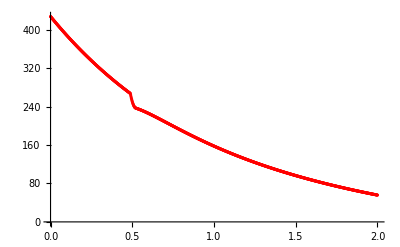

```mathematica
plotEntalpiaMPF6=ListPlot[tablicaEntalpiaMPF6,PlotStyle->Red]
```

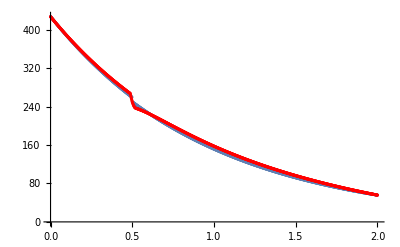

```mathematica
Show[plotEntalpiaDokladna6,plotEntalpiaMPF6]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv

### alfa = 8/10, t=1.5

#### temperatury

```mathematica
str7=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList7=ReadList[str7]
```

{2.11636,2.11212,2.1079,2.10368,2.09948,2.09528,2.09109,2.08691,2.08274,2.07857,2.07442,2.07028,2.06614,2.06201,2.05789,2.05378,2.04968,2.04558,2.0415,2.03742,2.03335,2.0293,2.02524,2.0212,2.01717,2.01314,2.00913,2.00512,2.00112,1.99713,1.99314,1.98917,1.9852,1.98124,1.97729,1.97335,1.96942,1.96549,1.96157,1.95766,1.95376,1.94987,1.94599,1.94211,1.93824,1.93438,1.93053,1.92669,1.92285,1.91902,1.9152,1.91139,1.90759,1.90379,1.9,1.89622,1.89245,1.88869,1.88493,1.88118,1.87744,1.87371,1.86998,1.86627,1.86256,1.85886,1.85516,1.85147,1.8478,1.84413,1.84046,1.83681,1.83316,1.82952,1.82589,1.82226,1.81864,1.81503,1.81143,1.80784,1.80425,1.80067,1.7971,1.79353,1.78997,1.78642,1.78288,1.77934,1.77582,1.7723,1.76878,1.76528,1.76178,1.75829,1.7548,1.75133,1.74786,1.74439,1.74094,1.73749,1.73405,1.73062,1.72719,1.72377,1.72036,1.71696,1.71356,1.71017,1.70678,1.70341,1.70004,1.69667,1.69332,1.68997,1.68663,1.68329,1.67997,1.67664,1.67333,1.67002,1.66672,1.66343,1.66014,1.65686,1.65359,1.65033,1.64707,1.64381,1.64057,1.63733,1.6341,1.63087,1.62765,1.62444,1.62124,1.61804,1.61484,1.61166,1.60848,1.60531,1.60214,1.59898,1.59583,1.59268,1.58955,1.58641,1.58329,1.58017,1.57705,1.57395,1.57085,1.56775,1.56466,1.56158,1.55851,1.55544,1.55238,1.54932,1.54627,1.54323,1.54019,1.53716,1.53414,1.53112,1.52811,1.5251,1.5221,1.51911,1.51612,1.51314,1.51017,1.5072,1.50424,1.50128,1.49833,1.49539,1.49245,1.48952,1.48659,1.48367,1.48076,1.47785,1.47495,1.47205,1.46916,1.46628,1.4634,1.46053,1.45767,1.45481,1.45195,1.4491,1.44626,1.44343,1.4406,1.43777,1.43495,1.43214,1.42933,1.42653,1.42374,1.42095,1.41816,1.41538,1.41261,1.40985,1.40708,1.40433,1.40158,1.39884,1.3961,1.39336,1.39064,1.38792,1.3852,1.38249,1.37979,1.37709,1.37439,1.3717,1.36902,1.36635,1.36367,1.36101,1.35835,1.35569,1.35304,1.3504,1.34776,1.34513,1.3425,1.33988,1.33726,1.33465,1.33204,1.32944,1.32685,1.32426,1.32167,1.31909,1.31652,1.31395,1.31139,1.30883,1.30627,1.30373,1.30118,1.29865,1.29611,1.29359,1.29107,1.28855,1.28604,1.28353,1.28103,1.27853,1.27604,1.27356,1.27108,1.2686,1.26613,1.26366,1.2612,1.25875,1.2563,1.25385,1.25141,1.24898,1.24655,1.24412,1.2417,1.23929,1.23688,1.23447,1.23207,1.22967,1.22728,1.2249,1.22252,1.22014,1.21777,1.2154,1.21304,1.21068,1.20833,1.20598,1.20364,1.2013,1.19897,1.19664,1.19432,1.192,1.18969,1.18738,1.18507,1.18277,1.18048,1.17819,1.1759,1.17362,1.17135,1.16907,1.16681,1.16454,1.16229,1.16003,1.15778,1.15554,1.1533,1.15107,1.14884,1.14661,1.14439,1.14217,1.13996,1.13775,1.13555,1.13335,1.13116,1.12897,1.12678,1.1246,1.12242,1.12025,1.11808,1.11592,1.11376,1.11161,1.10946,1.10731,1.10517,1.10304,1.1009,1.09877,1.09665,1.09453,1.09242,1.09031,1.0882,1.0861,1.084,1.08191,1.07982,1.07773,1.07565,1.07357,1.0715,1.06943,1.06737,1.06531,1.06325,1.0612,1.05916,1.05711,1.05508,1.05304,1.05101,1.04899,1.04696,1.04495,1.04293,1.04093,1.03892,1.03692,1.03493,1.03294,1.03095,1.02119,1.00886,1,1,1,0.998549,0.989774,0.981125,0.974334,0.967543,0.962065,0.957239,0.952963,0.950094,0.947213,0.946075,0.94514,0.94419,0.943224,0.942244,0.94125,0.940242,0.93922,0.938184,0.937136,0.936075,0.935002,0.933916,0.932819,0.93171,0.930589,0.929458,0.928316,0.927163,0.926001,0.924828,0.923646,0.922454,0.921252,0.920042,0.918823,0.917596,0.91636,0.915116,0.913864,0.912604,0.911337,0.910062,0.90878,0.907492,0.906197,0.904895,0.903586,0.902272,0.900951,0.899625,0.898293,0.896955,0.895613,0.894264,0.892911,0.891553,0.89019,0.888823,0.887451,0.886075,0.884694,0.88331,0.881922,0.880529,0.879134,0.877734,0.876332,0.874926,0.873516,0.872104,0.870689,0.869271,0.86785,0.866427,0.865001,0.863573,0.862142,0.860709,0.859274,0.857837,0.856398,0.854958,0.853515,0.852071,0.850625,0.849178,0.847729,0.84628,0.844828,0.843376,0.841923,0.840468,0.839013,0.837556,0.836099,0.834642,0.833183,0.831724,0.830264,0.828804,0.827344,0.825883,0.824422,0.82296,0.821499,0.820037,0.818575,0.817113,0.815652,0.81419,0.812728,0.811267,0.809806,0.808345,0.806885,0.805424,0.803965,0.802506,0.801047,0.799589,0.798131,0.796674,0.795218,0.793762,0.792307,0.790853,0.7894,0.787948,0.786496,0.785046,0.783596,0.782147,0.7807,0.779253,0.777808,0.776363,0.77492,0.773478,0.772037,0.770597,0.769159,0.767722,0.766286,0.764851,0.763418,0.761986,0.760556,0.759127,0.757699,0.756273,0.754848,0.753425,0.752003,0.750583,0.749165,0.747748,0.746332,0.744919,0.743506,0.742096,0.740687,0.73928,0.737874,0.736471,0.735068,0.733668,0.73227,0.730873,0.729478,0.728084,0.726693,0.725303,0.723915,0.72253,0.721145,0.719763,0.718383,0.717004,0.715628,0.714253,0.71288,0.711509,0.71014,0.708773,0.707408,0.706045,0.704684,0.703325,0.701968,0.700612,0.699259,0.697908,0.696559,0.695212,0.693866,0.692523,0.691182,0.689843,0.688506,0.687171,0.685838,0.684507,0.683179,0.681852,0.680527,0.679205,0.677884,0.676566,0.675249,0.673935,0.672623,0.671313,0.670005,0.668699,0.667396,0.666094,0.664794,0.663497,0.662202,0.660909,0.659618,0.658329,0.657042,0.655757,0.654475,0.653194,0.651916,0.65064,0.649366,0.648094,0.646824,0.645557,0.644291,0.643028,0.641767,0.640508,0.639251,0.637996,0.636743,0.635493,0.634244,0.632998,0.631754,0.630512,0.629272,0.628035,0.626799,0.625566,0.624334,0.623105,0.621878,0.620653,0.619431,0.61821,0.616991,0.615775,0.614561,0.613349,0.612139,0.610931,0.609725,0.608521,0.60732,0.606121,0.604923,0.603728,0.602535,0.601344,0.600155,0.598968,0.597784,0.596601,0.595421,0.594242,0.593066,0.591892,0.59072,0.58955,0.588382,0.587216,0.586053,0.584891,0.583731,0.582574,0.581419,0.580265,0.579114,0.577965,0.576818,0.575672,0.574529,0.573388,0.57225,0.571113,0.569978,0.568845,0.567714,0.566586,0.565459,0.564334,0.563212,0.562091,0.560973,0.559856,0.558742,0.557629,0.556519,0.55541,0.554304,0.553199,0.552097,0.550996,0.549898,0.548801,0.547707,0.546614,0.545524,0.544435,0.543349,0.542264,0.541181,0.540101,0.539022,0.537945,0.536871,0.535798,0.534727,0.533658,0.532591,0.531526,0.530463,0.529402,0.528342,0.527285,0.52623,0.525176,0.524125,0.523075,0.522027,0.520982,0.519938,0.518896,0.517856,0.516817,0.515781,0.514747,0.513714,0.512683,0.511655,0.510628,0.509603,0.508579,0.507558,0.506539,0.505521,0.504505,0.503491,0.502479,0.501469,0.500461,0.499454,0.49845,0.497447,0.496446,0.495447,0.494449,0.493454,0.49246,0.491468,0.490478,0.48949,0.488503,0.487518,0.486536,0.485554,0.484575,0.483597,0.482622,0.481648,0.480675,0.479705,0.478736,0.477769,0.476804,0.475841,0.474879,0.473919,0.472961,0.472005,0.47105,0.470097,0.469146,0.468196,0.467249,0.466303,0.465358,0.464416,0.463475,0.462536,0.461598,0.460663,0.459729,0.458796,0.457866,0.456937,0.456009,0.455084,0.45416,0.453238,0.452317,0.451398,0.450481,0.449566,0.448652,0.447739,0.446829,0.44592,0.445013,0.444107,0.443203,0.442301,0.4414,0.440501,0.439604,0.438708,0.437814,0.436921,0.43603,0.435141,0.434253,0.433367,0.432482,0.4316,0.430718,0.429839,0.42896,0.428084,0.427209,0.426336,0.425464,0.424594,0.423725,0.422858,0.421992,0.421128,0.420266,0.419405,0.418546,0.417688,0.416832,0.415978,0.415125,0.414273,0.413423,0.412575,0.411728,0.410882,0.410038,0.409196,0.408355,0.407516,0.406678,0.405842,0.405007,0.404174,0.403342,0.402512,0.401683,0.400856,0.40003,0.399206,0.398383,0.397562,0.396742,0.395923,0.395106,0.394291,0.393477,0.392664,0.391853,0.391044,0.390236,0.389429,0.388624,0.38782,0.387018,0.386217,0.385417,0.384619,0.383823,0.383028,0.382234,0.381442,0.380651,0.379861,0.379073,0.378287,0.377501,0.376717,0.375935,0.375154,0.374374,0.373596,0.372819,0.372044,0.37127,0.370497,0.369726,0.368956,0.368188,0.367421,0.366655,0.365891,0.365128,0.364366,0.363606,0.362847,0.362089,0.361333,0.360578,0.359825,0.359073,0.358322,0.357572,0.356824,0.356077,0.355332,0.354588,0.353845,0.353104,0.352363,0.351625,0.350887,0.350151,0.349416,0.348683,0.34795,0.34722,0.34649,0.345762,0.345035,0.344309,0.343584,0.342861,0.34214,0.341419,0.3407,0.339982,0.339265,0.33855,0.337836,0.337123,0.336411,0.335701,0.334992,0.334284,0.333577,0.332872,0.332168,0.331465,0.330764,0.330064,0.329365,0.328667,0.32797,0.327275,0.326581,0.325888,0.325197,0.324507,0.323817,0.32313,0.322443,0.321758,0.321073,0.32039,0.319709,0.319028,0.318349,0.317671,0.316994,0.316318,0.315644,0.31497,0.314298,0.313627,0.312958,0.312289,0.311622,0.310956,0.310291,0.309627,0.308965,0.308303,0.307643,0.306984,0.306326,0.30567,0.305014,0.30436,0.303707,0.303055,0.302404,0.301754,0.301105,0.300458,0.299812,0.299167,0.298523,0.29788,0.297239,0.296598,0.295959,0.295321,0.294684,0.294048,0.293413,0.292779,0.292147,0.291515,0.290885,0.290256,0.289628,0.289001,0.288375,0.287751,0.287127,0.286505}

```mathematica
strList7={2.1163576298,2.1121241791,2.1078996125,2.1036839092,2.0994770499,2.0952790168,2.0910897923,2.0869093585,2.0827376959,2.0785747815,2.0744205974,2.070275126,2.0661383499,2.0620102516,2.0578908137,2.0537800121,2.0496778291,2.0455842472,2.0414992488,2.0374228167,2.0333549337,2.0292955829,2.0252447404,2.0212023889,2.017168511,2.0131430897,2.0091261079,2.0051175489,2.0011173894,1.9971256123,1.9931422007,1.9891671374,1.985200406,1.9812419838,1.9772918538,1.9733499993,1.9694164036,1.96549105,1.9615739165,1.9576649864,1.953764243,1.9498716698,1.9459872452,1.9421109527,1.9382427757,1.934382698,1.9305307032,1.9266867699,1.9228508818,1.9190230228,1.9152031765,1.9113913219,1.907587443,1.9037915236,1.9000035477,1.8962234944,1.8924513479,1.8886870921,1.8849307113,1.8811821847,1.8774414967,1.8737086315,1.8699835732,1.8662663017,1.8625568012,1.8588550561,1.8551610508,1.8514747653,1.847796184,1.8441252914,1.8404620678,1.8368064977,1.8331585657,1.8295182565,1.8258855503,1.822260432,1.8186428864,1.8150328981,1.8114304479,1.8078355205,1.804248101,1.8006681699,1.7970957124,1.7935307134,1.7899731539,1.7864230189,1.7828802936,1.7793449632,1.7758170086,1.7722964151,1.7687831681,1.7652772488,1.7617786425,1.7582873345,1.7548033064,1.7513265435,1.7478570313,1.7443947514,1.7409396893,1.7374918306,1.7340511608,1.7306176618,1.7271913191,1.7237721185,1.7203600418,1.7169550749,1.7135572035,1.7101664097,1.7067826794,1.7034059984,1.7000363488,1.6966737168,1.6933180882,1.6899694455,1.6866277745,1.6832930615,1.6799652889,1.6766444428,1.6733305094,1.6700234713,1.6667233148,1.6634300261,1.6601435879,1.6568639865,1.6535912085,1.6503252365,1.647066057,1.6438136531,1.640568011,1.6373291175,1.6340969555,1.6308715117,1.6276527725,1.6244407214,1.6212353448,1.6180366295,1.6148445588,1.6116591195,1.6084802983,1.6053080788,1.6021424477,1.598983392,1.5958308951,1.592684944,1.5895455259,1.5864126241,1.5832862258,1.5801663149,1.5770528782,1.573945903,1.5708453731,1.5677512757,1.564663598,1.561582324,1.5585074409,1.5554389361,1.5523767936,1.5493210007,1.5462715418,1.543228404,1.540191575,1.5371610389,1.5341367832,1.5311187956,1.5281070603,1.5251015649,1.522102294,1.519109235,1.5161223758,1.5131417008,1.5101671978,1.5071988546,1.5042366557,1.501280589,1.4983306393,1.4953867944,1.4924490421,1.4895173674,1.4865917581,1.4836722024,1.480758685,1.477851194,1.4749497144,1.4720542343,1.4691647419,1.4662812222,1.4634036634,1.4605320537,1.4576663783,1.4548066254,1.4519527803,1.4491048314,1.4462627669,1.4434265722,1.4405962357,1.4377717459,1.4349530882,1.432140251,1.4293332199,1.4265319833,1.4237365299,1.4209468453,1.418162918,1.4153847337,1.4126122811,1.409845549,1.4070845229,1.4043291917,1.4015795443,1.3988355664,1.3960972468,1.3933645714,1.3906375291,1.387916109,1.3852002968,1.3824900816,1.3797854494,1.3770863893,1.3743928902,1.3717049384,1.3690225229,1.3663456299,1.3636742486,1.3610083681,1.3583479747,1.3556930577,1.3530436033,1.3503996009,1.3477610397,1.3451279063,1.3425001898,1.3398778799,1.3372609628,1.3346494282,1.3320432624,1.329442455,1.3268469957,1.3242568709,1.3216720702,1.3190925803,1.3165183908,1.3139494915,1.311385869,1.3088275131,1.3062744105,1.3037265511,1.3011839246,1.2986465179,1.2961143208,1.2935873203,1.2910655063,1.2885488687,1.2860373945,1.2835310736,1.2810298932,1.2785338432,1.2760429137,1.2735570919,1.2710763678,1.2686007286,1.2661301645,1.2636646658,1.2612042195,1.2587488159,1.2562984425,1.2538530894,1.251412747,1.2489774026,1.2465470467,1.2441216666,1.2417012527,1.2392857956,1.2368752827,1.2344697045,1.2320690486,1.2296733054,1.2272824628,1.2248965112,1.2225154412,1.2201392406,1.2177678999,1.2154014071,1.2130397528,1.2106829276,1.2083309195,1.2059837193,1.2036413148,1.2013036969,1.1989708564,1.1966427814,1.1943194627,1.1920008884,1.1896870494,1.1873779368,1.1850735386,1.1827738459,1.1804788469,1.1781885327,1.1759028945,1.1736219204,1.1713456016,1.1690739266,1.1668068865,1.1645444698,1.1622866676,1.1600334714,1.1577848697,1.1555408538,1.1533014123,1.1510665367,1.1488362184,1.1466104461,1.1443892113,1.1421725028,1.1399603122,1.1377526313,1.1355494487,1.1333507564,1.1311565432,1.1289668008,1.1267815185,1.1246006881,1.1224243015,1.1202523481,1.1180848196,1.1159217057,1.1137629983,1.1116086898,1.1094587697,1.1073132302,1.1051720613,1.1030352552,1.1009028047,1.0987746998,1.0966509332,1.0945314952,1.0924163785,1.0903055739,1.0881990745,1.086096874,1.0839989633,1.0819053361,1.079815984,1.0777309011,1.0756500825,1.0735735202,1.0715012095,1.0694331438,1.0673693188,1.0653097295,1.063254373,1.0612032486,1.0591563527,1.0571136851,1.055075247,1.0530410412,1.0510110765,1.0489853588,1.0469639021,1.0449467254,1.0429338491,1.0409253207,1.0389211877,1.0369215531,1.0349265494,1.0329365413,1.0309547086,1.0211874643,1.0088625547,1,1,1,0.9985490272,0.9897739856,0.9811254329,0.9743342795,0.967543469,0.9620647068,0.9572393936,0.9529630576,0.9500940191,0.9472131921,0.9460754064,0.9451402539,0.9441897857,0.9432243487,0.9422442834,0.9412499239,0.9402415977,0.9392196265,0.9381843258,0.9371360049,0.9360749676,0.9350015118,0.9339159296,0.932818508,0.9317095282,0.9305892661,0.9294579926,0.9283159733,0.9271634687,0.9260007345,0.9248280215,0.9236455757,0.9224536385,0.9212524467,0.9200422324,0.9188232237,0.9175956438,0.9163597122,0.9151156439,0.9138636499,0.912603937,0.9113367084,0.910062163,0.9087804963,0.9074918999,0.9061965615,0.9048946656,0.9035863929,0.9022719208,0.9009514231,0.8996250705,0.8982930302,0.8969554663,0.8956125398,0.8942644085,0.8929112272,0.8915531476,0.8901903188,0.8888228866,0.8874509943,0.8860747823,0.8846943882,0.8833099472,0.8819215916,0.8805294513,0.8791336537,0.8777343234,0.8763315831,0.8749255527,0.8735163499,0.8721040902,0.8706888867,0.8692708503,0.8678500898,0.8664267119,0.8650008211,0.8635725199,0.8621419088,0.8607090863,0.8592741491,0.8578371917,0.856398307,0.8549575859,0.8535151176,0.8520709896,0.8506252875,0.8491780953,0.8477294953,0.8462795681,0.8448283929,0.843376047,0.8419226066,0.8404681459,0.8390127379,0.8375564541,0.8360993644,0.8346415376,0.8331830409,0.8317239401,0.8302642998,0.8288041833,0.8273436525,0.825882768,0.8244215895,0.8229601751,0.8214985819,0.8200368659,0.8185750817,0.817113283,0.8156515223,0.8141898511,0.8127283198,0.8112669776,0.809805873,0.8083450533,0.8068845647,0.8054244527,0.8039647617,0.802505535,0.8010468155,0.7995886446,0.7981310632,0.7966741113,0.7952178278,0.7937622512,0.7923074188,0.7908533673,0.7894001325,0.7879477495,0.7864962527,0.7850456756,0.7835960512,0.7821474115,0.780699788,0.7792532115,0.777807712,0.7763633191,0.7749200614,0.7734779671,0.7720370637,0.7705973781,0.7691589367,0.7677217651,0.7662858885,0.7648513313,0.7634181177,0.7619862711,0.7605558144,0.75912677,0.7576991598,0.7562730051,0.7548483268,0.7534251454,0.7520034806,0.750583352,0.7491647785,0.7477477787,0.7463323706,0.7449185718,0.7435063997,0.742095871,0.740687002,0.7392798088,0.737874307,0.7364705117,0.7350684378,0.7336680998,0.7322695117,0.7308726872,0.7294776398,0.7280843824,0.7266929277,0.7253032882,0.7239154758,0.7225295022,0.7211453788,0.7197631168,0.7183827269,0.7170042196,0.7156276051,0.7142528933,0.712880094,0.7115092163,0.7101402694,0.7087732623,0.7074082033,0.7060451009,0.7046839631,0.7033247978,0.7019676125,0.7006124146,0.6992592112,0.6979080093,0.6965588155,0.6952116362,0.6938664777,0.6925233461,0.6911822472,0.6898431866,0.6885061698,0.6871712021,0.6858382884,0.6845074336,0.6831786425,0.6818519196,0.6805272692,0.6792046955,0.6778842024,0.6765657939,0.6752494735,0.6739352449,0.6726231114,0.6713130761,0.6700051422,0.6686993125,0.66739559,0.6660939771,0.6647944763,0.6634970902,0.6622018208,0.6609086702,0.6596176406,0.6583287336,0.6570419511,0.6557572947,0.6544747657,0.6531943657,0.6519160959,0.6506399575,0.6493659514,0.6480940787,0.6468243402,0.6455567367,0.6442912687,0.6430279368,0.6417667415,0.6405076831,0.6392507619,0.637995978,0.6367433317,0.6354928227,0.6342444512,0.6329982169,0.6317541195,0.6305121589,0.6292723344,0.6280346457,0.6267990923,0.6255656735,0.6243343886,0.6231052368,0.6218782174,0.6206533294,0.6194305719,0.6182099438,0.6169914441,0.6157750716,0.6145608251,0.6133487034,0.6121387051,0.6109308288,0.6097250732,0.6085214366,0.6073199177,0.6061205147,0.6049232262,0.6037280503,0.6025349853,0.6013440295,0.600155181,0.598968438,0.5977837985,0.5966012606,0.5954208223,0.5942424815,0.5930662362,0.5918920842,0.5907200234,0.5895500516,0.5883821666,0.587216366,0.5860526477,0.5848910092,0.5837314482,0.5825739623,0.581418549,0.580265206,0.5791139306,0.5779647205,0.576817573,0.5756724856,0.5745294556,0.5733884804,0.5722495575,0.571112684,0.5699778573,0.5688450747,0.5677143335,0.5665856307,0.5654589637,0.5643343296,0.5632117256,0.5620911489,0.5609725965,0.5598560656,0.5587415532,0.5576290564,0.5565185722,0.5554100978,0.55430363,0.553199166,0.5520967026,0.5509962369,0.5498977658,0.5488012862,0.5477067952,0.5466142894,0.545523766,0.5444352218,0.5433486535,0.5422640582,0.5411814326,0.5401007736,0.5390220781,0.5379453427,0.5368705644,0.53579774,0.5347268662,0.5336579398,0.5325909576,0.5315259163,0.5304628127,0.5294016436,0.5283424057,0.5272850957,0.5262297103,0.5251762463,0.5241247004,0.5230750693,0.5220273497,0.5209815383,0.5199376318,0.5188956268,0.5178555201,0.5168173083,0.5157809881,0.5147465562,0.5137140093,0.5126833439,0.5116545568,0.5106276447,0.5096026041,0.5085794317,0.5075581242,0.5065386783,0.5055210905,0.5045053575,0.5034914759,0.5024794425,0.5014692538,0.5004609064,0.4994543971,0.4984497224,0.497446879,0.4964458635,0.4954466725,0.4944493028,0.4934537508,0.4924600133,0.491468087,0.4904779683,0.489489654,0.4885031407,0.4875184251,0.4865355037,0.4855543733,0.4845750305,0.4835974718,0.4826216941,0.4816476938,0.4806754677,0.4797050125,0.4787363247,0.477769401,0.4768042381,0.4758408326,0.4748791813,0.4739192807,0.4729611276,0.4720047186,0.4710500504,0.4700971197,0.4691459231,0.4681964574,0.4672487191,0.4663027051,0.465358412,0.4644158366,0.4634749754,0.4625358252,0.4615983828,0.4606626448,0.459728608,0.4587962691,0.4578656247,0.4569366717,0.4560094068,0.4550838266,0.454159928,0.4532377077,0.4523171625,0.4513982891,0.4504810842,0.4495655446,0.4486516672,0.4477394486,0.4468288857,0.4459199753,0.445012714,0.4441070988,0.4432031264,0.4423007936,0.4414000973,0.4405010343,0.4396036013,0.4387077952,0.4378136128,0.436921051,0.4360301066,0.4351407765,0.4342530575,0.4333669464,0.4324824402,0.4315995357,0.4307182298,0.4298385193,0.4289604012,0.4280838723,0.4272089295,0.4263355698,0.42546379,0.4245935871,0.423724958,0.4228578996,0.4219924088,0.4211284826,0.420266118,0.4194053118,0.4185460611,0.4176883628,0.4168322138,0.4159776112,0.4151245519,0.414273033,0.4134230513,0.412574604,0.411727688,0.4108823003,0.410038438,0.4091960981,0.4083552775,0.4075159734,0.4066781828,0.4058419028,0.4050071303,0.4041738625,0.4033420965,0.4025118292,0.4016830578,0.4008557795,0.4000299912,0.39920569,0.3983828732,0.3975615378,0.3967416809,0.3959232996,0.3951063911,0.3942909526,0.3934769811,0.3926644739,0.391853428,0.3910438407,0.3902357092,0.3894290305,0.388623802,0.3878200207,0.387017684,0.3862167889,0.3854173327,0.3846193127,0.3838227261,0.38302757,0.3822338418,0.3814415386,0.3806506578,0.3798611966,0.3790731522,0.378286522,0.3775013032,0.3767174931,0.375935089,0.3751540881,0.3743744879,0.3735962856,0.3728194785,0.372044064,0.3712700394,0.370497402,0.3697261492,0.3689562783,0.3681877867,0.3674206718,0.3666549309,0.3658905614,0.3651275607,0.3643659262,0.3636056553,0.3628467455,0.362089194,0.3613329983,0.360578156,0.3598246643,0.3590725207,0.3583217228,0.3575722678,0.3568241534,0.3560773769,0.3553319359,0.3545878278,0.3538450501,0.3531036003,0.3523634759,0.3516246744,0.3508871933,0.3501510301,0.3494161825,0.3486826478,0.3479504237,0.3472195076,0.3464898972,0.34576159,0.3450345836,0.3443088755,0.3435844633,0.3428613446,0.3421395171,0.3414189782,0.3406997257,0.3399817571,0.33926507,0.3385496621,0.337835531,0.3371226743,0.3364110897,0.3357007749,0.3349917275,0.3342839451,0.3335774254,0.3328721662,0.3321681651,0.3314654198,0.330763928,0.3300636874,0.3293646956,0.3286669506,0.3279704498,0.3272751912,0.3265811724,0.3258883911,0.3251968452,0.3245065324,0.3238174504,0.323129597,0.3224429699,0.3217575671,0.3210733862,0.3203904251,0.3197086816,0.3190281534,0.3183488384,0.3176707344,0.3169938392,0.3163181508,0.3156436668,0.3149703852,0.3142983038,0.3136274205,0.3129577331,0.3122892395,0.3116219377,0.3109558254,0.3102909006,0.3096271612,0.308964605,0.3083032301,0.3076430342,0.3069840154,0.3063261716,0.3056695006,0.3050140005,0.3043596692,0.3037065047,0.3030545048,0.3024036677,0.3017539912,0.3011054733,0.3004581121,0.2998119055,0.2991668515,0.2985229481,0.2978801934,0.2972385853,0.2965981219,0.2959588012,0.2953206213,0.2946835802,0.2940476759,0.2934129065,0.2927792701,0.2921467647,0.2915153884,0.2908851393,0.2902560155,0.289628015,0.289001136,0.2883753766,0.2877507348,0.2871272089,0.2865047969};
```

```mathematica
tablicaTemperaturMPF7=Table[{i*0.002,strList7[[i+1]]},{i,0,1000}];
```

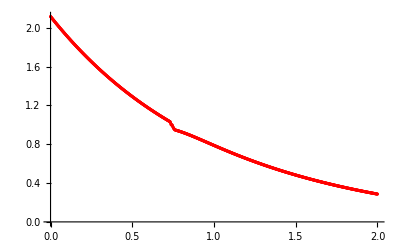

```mathematica
plotTemperaturyMPF7=ListPlot[tablicaTemperaturMPF7,PlotStyle->Red]
```

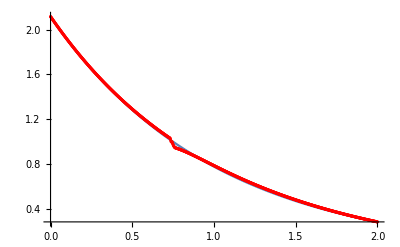

```mathematica
Show[plotTemperaturyDokladne3,plotTemperaturyMPF7]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(Gamma[0.2]*(lambdaL-lambdaS))/(5*aL*t^(1/5));
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t],temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna7=Table[{i*0.002,entalpia[u1[i*0.002,1.5],1.5]},{i,0,1000}];
```

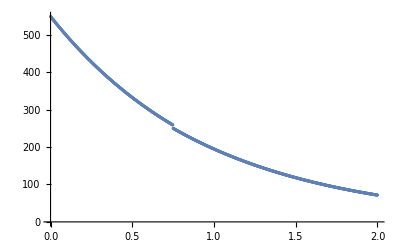

```mathematica
plotEntalpiaDokladna7=ListPlot[tablicaEntalpiaDokladna7]
```

```mathematica
strE=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE7=ReadList[strE]
```

{548.719,547.619,546.52,545.424,544.331,543.239,542.15,541.063,539.978,538.896,537.816,536.738,535.662,534.589,533.518,532.449,531.383,530.318,529.256,528.196,527.139,526.083,525.03,523.979,522.93,521.884,520.839,519.797,518.757,517.719,516.683,515.65,514.619,513.589,512.562,511.538,510.515,509.494,508.476,507.459,506.445,505.433,504.423,503.415,502.41,501.406,500.404,499.405,498.408,497.412,496.419,495.428,494.439,493.452,492.467,491.485,490.504,489.525,488.548,487.574,486.601,485.631,484.662,483.696,482.731,481.769,480.808,479.85,478.894,477.939,476.987,476.036,475.088,474.141,473.197,472.254,471.314,470.375,469.438,468.504,467.571,466.64,465.711,464.784,463.86,462.936,462.015,461.096,460.179,459.264,458.35,457.439,456.529,455.621,454.715,453.811,452.909,452.009,451.111,450.214,449.32,448.427,447.536,446.647,445.76,444.875,443.991,443.11,442.23,441.352,440.476,439.602,438.729,437.859,436.99,436.123,435.257,434.394,433.532,432.673,431.815,430.958,430.104,429.251,428.4,427.551,426.704,425.858,425.014,424.172,423.332,422.493,421.656,420.821,419.988,419.156,418.326,417.498,416.671,415.847,415.024,414.202,413.383,412.565,411.748,410.934,410.121,409.31,408.5,407.692,406.886,406.082,405.279,404.478,403.678,402.881,402.084,401.29,400.497,399.706,398.916,398.128,397.342,396.557,395.774,394.993,394.213,393.435,392.658,391.883,391.11,390.338,389.568,388.799,388.032,387.267,386.503,385.741,384.98,384.221,383.464,382.708,381.953,381.201,380.449,379.7,378.951,378.205,377.46,376.716,375.974,375.234,374.495,373.757,373.022,372.287,371.554,370.823,370.093,369.365,368.638,367.913,367.189,366.467,365.746,365.026,364.308,363.592,362.877,362.164,361.452,360.741,360.032,359.325,358.619,357.914,357.211,356.509,355.809,355.11,354.412,353.716,353.022,352.329,351.637,350.947,350.258,349.57,348.884,348.2,347.517,346.835,346.154,345.475,344.798,344.122,343.447,342.773,342.101,341.431,340.761,340.093,339.427,338.762,338.098,337.435,336.774,336.115,335.456,334.799,334.144,333.489,332.836,332.185,331.534,330.885,330.238,329.591,328.946,328.303,327.66,327.019,326.38,325.741,325.104,324.468,323.834,323.201,322.569,321.938,321.309,320.681,320.054,319.429,318.804,318.182,317.56,316.94,316.321,315.703,315.086,314.471,313.857,313.244,312.633,312.022,311.413,310.805,310.199,309.594,308.99,308.387,307.785,307.185,306.586,305.988,305.391,304.796,304.201,303.608,303.016,302.426,301.836,301.248,300.661,300.075,299.491,298.907,298.325,297.744,297.164,296.585,296.008,295.431,294.856,294.282,293.709,293.138,292.567,291.998,291.43,290.863,290.297,289.732,289.169,288.606,288.045,287.485,286.926,286.368,285.811,285.256,284.701,284.148,283.596,283.045,282.495,281.946,281.398,280.852,280.306,279.762,279.219,278.677,278.136,277.596,277.057,276.519,275.983,275.447,274.913,274.379,273.847,273.316,272.786,272.257,271.729,271.203,270.677,270.153,269.629,269.107,268.586,268.066,267.547,267.03,266.515,263.975,260.771,257.574,254.798,252.105,249.637,247.443,245.281,243.584,241.886,240.516,239.31,238.241,237.524,236.803,236.519,236.285,236.047,235.806,235.561,235.312,235.06,234.805,234.546,234.284,234.019,233.75,233.479,233.205,232.927,232.647,232.364,232.079,231.791,231.5,231.207,230.911,230.613,230.313,230.011,229.706,229.399,229.09,228.779,228.466,228.151,227.834,227.516,227.195,226.873,226.549,226.224,225.897,225.568,225.238,224.906,224.573,224.239,223.903,223.566,223.228,222.888,222.548,222.206,221.863,221.519,221.174,220.827,220.48,220.132,219.783,219.434,219.083,218.731,218.379,218.026,217.672,217.318,216.963,216.607,216.25,215.893,215.535,215.177,214.819,214.459,214.1,213.739,213.379,213.018,212.656,212.295,211.932,211.57,211.207,210.844,210.481,210.117,209.753,209.389,209.025,208.66,208.296,207.931,207.566,207.201,206.836,206.471,206.105,205.74,205.375,205.009,204.644,204.278,203.913,203.547,203.182,202.817,202.451,202.086,201.721,201.356,200.991,200.626,200.262,199.897,199.533,199.169,198.804,198.441,198.077,197.713,197.35,196.987,196.624,196.261,195.899,195.537,195.175,194.813,194.452,194.091,193.73,193.369,193.009,192.649,192.29,191.93,191.571,191.213,190.855,190.497,190.139,189.782,189.425,189.068,188.712,188.356,188.001,187.646,187.291,186.937,186.583,186.23,185.877,185.524,185.172,184.82,184.469,184.118,183.767,183.417,183.067,182.718,182.369,182.021,181.673,181.326,180.979,180.632,180.286,179.941,179.596,179.251,178.907,178.563,178.22,177.877,177.535,177.193,176.852,176.511,176.171,175.831,175.492,175.153,174.815,174.477,174.14,173.803,173.467,173.131,172.796,172.461,172.127,171.793,171.46,171.127,170.795,170.463,170.132,169.801,169.471,169.141,168.812,168.484,168.156,167.828,167.501,167.175,166.849,166.523,166.199,165.874,165.55,165.227,164.904,164.582,164.26,163.939,163.619,163.299,162.979,162.66,162.341,162.024,161.706,161.389,161.073,160.757,160.442,160.127,159.813,159.499,159.186,158.873,158.561,158.25,157.939,157.628,157.318,157.009,156.7,156.391,156.084,155.776,155.47,155.163,154.858,154.552,154.248,153.944,153.64,153.337,153.035,152.733,152.431,152.13,151.83,151.53,151.231,150.932,150.634,150.336,150.039,149.742,149.446,149.15,148.855,148.561,148.267,147.973,147.68,147.388,147.096,146.804,146.513,146.223,145.933,145.643,145.355,145.066,144.778,144.491,144.204,143.918,143.632,143.347,143.062,142.778,142.494,142.211,141.929,141.646,141.365,141.084,140.803,140.523,140.243,139.964,139.685,139.407,139.13,138.853,138.576,138.3,138.024,137.749,137.474,137.2,136.927,136.654,136.381,136.109,135.837,135.566,135.295,135.025,134.756,134.486,134.218,133.949,133.682,133.414,133.148,132.881,132.616,132.35,132.086,131.821,131.557,131.294,131.031,130.769,130.507,130.245,129.984,129.724,129.464,129.204,128.945,128.687,128.429,128.171,127.914,127.657,127.401,127.145,126.89,126.635,126.38,126.126,125.873,125.62,125.367,125.115,124.864,124.612,124.362,124.111,123.862,123.612,123.363,123.115,122.867,122.619,122.372,122.126,121.88,121.634,121.389,121.144,120.899,120.655,120.412,120.169,119.926,119.684,119.442,119.201,118.96,118.72,118.48,118.24,118.001,117.763,117.524,117.286,117.049,116.812,116.576,116.34,116.104,115.869,115.634,115.4,115.166,114.932,114.699,114.466,114.234,114.002,113.771,113.54,113.309,113.079,112.85,112.62,112.391,112.163,111.935,111.707,111.48,111.253,111.027,110.801,110.575,110.35,110.125,109.901,109.677,109.453,109.23,109.008,108.785,108.563,108.342,108.121,107.9,107.68,107.46,107.24,107.021,106.802,106.584,106.366,106.148,105.931,105.714,105.498,105.282,105.067,104.851,104.637,104.422,104.208,103.994,103.781,103.568,103.356,103.144,102.932,102.721,102.51,102.299,102.089,101.879,101.67,101.46,101.252,101.043,100.836,100.628,100.421,100.214,100.007,99.8014,99.5957,99.3904,99.1854,98.9808,98.7766,98.5727,98.3692,98.1661,97.9634,97.761,97.5589,97.3573,97.156,96.955,96.7544,96.5542,96.3543,96.1548,95.9557,95.7569,95.5585,95.3604,95.1627,94.9653,94.7683,94.5716,94.3753,94.1794,93.9838,93.7885,93.5936,93.3991,93.2049,93.011,92.8175,92.6244,92.4315,92.2391,92.0469,91.8552,91.6637,91.4726,91.2819,91.0915,90.9014,90.7117,90.5223,90.3332,90.1445,89.9562,89.7681,89.5804,89.3931,89.206,89.0193,88.833,88.647,88.4613,88.2759,88.0909,87.9062,87.7218,87.5378,87.354,87.1707,86.9876,86.8049,86.6225,86.4404,86.2586,86.0772,85.8961,85.7153,85.5349,85.3547,85.1749,84.9954,84.8163,84.6374,84.4589,84.2807,84.1028,83.9252,83.7479,83.571,83.3944,83.218,83.042,82.8664,82.691,82.5159,82.3412,82.1667,81.9926,81.8188,81.6453,81.4721,81.2992,81.1266,80.9544,80.7824,80.6107,80.4394,80.2683,80.0976,79.9272,79.757,79.5872,79.4177,79.2485,79.0795,78.9109,78.7426,78.5746,78.4069,78.2394,78.0723,77.9055,77.739,77.5727,77.4068,77.2412,77.0758,76.9108,76.746,76.5815,76.4174,76.2535,76.0899,75.9266,75.7636,75.6009,75.4385,75.2764,75.1145,74.953,74.7917,74.6307,74.47,74.3096,74.1495,73.9897,73.8302,73.6709,73.5119,73.3532,73.1948,73.0367,72.8788,72.7213,72.564,72.407,72.2503,72.0938,71.9377,71.7818,71.6262}

```mathematica
strListE7={548.7194903541,547.6187931728,546.5204058618,545.4243230049,544.3305395884,543.239050991,542.149852601,541.0629398163,539.9783075431,538.8959497988,537.8158619341,536.7380393742,535.6624775799,534.5891720219,533.5181181801,532.449309762,531.3827421877,530.3184108869,529.2563112989,528.1964389488,527.1387893871,526.0833581737,525.0301391186,523.9791277196,522.9303194837,521.8837099277,520.8392946673,519.7970693307,518.757027862,517.7191658252,516.6834787934,515.6499623505,514.6186121808,513.5894223917,512.5623886019,511.5375064392,510.5147715408,509.494179622,508.4757249097,507.4594030756,506.4452098007,505.4331407753,504.423190373,503.4153543083,502.4096283049,501.4060080957,500.4044894404,499.4050667832,498.4077358894,497.4124925338,496.4193325001,495.4282503199,494.4392417998,493.4523027553,492.4674290113,491.4846151665,490.5038570681,489.525150572,488.5484915432,487.5738746458,486.6012957663,485.6307508007,484.6622356538,483.6957450519,482.7312749213,481.7688211968,480.8083798225,479.8499455854,478.8935144502,477.9390823907,476.9866442552,476.0361960233,475.0877336982,474.1412532921,473.1967496953,472.25421894,471.3136570674,470.3750601277,469.4384230658,468.5037419517,467.5710128643,466.6402307918,465.7113918319,464.7844920917,463.8595266272,462.9364915379,462.015382959,461.0961970348,460.1789288443,459.2635745508,458.3501303264,457.4385913002,456.5289536522,455.6212135821,454.7153662738,453.811407918,452.9093347419,452.0091419804,451.1108258377,450.2143825682,449.3198084345,448.4270986762,447.5362495746,446.6472574195,445.7601174894,444.8748260888,443.9913795344,443.1097731465,442.2300032491,441.3520661855,440.4759573152,439.6016729832,438.7292095591,437.8585624393,436.9897279918,436.122702612,435.2574817312,434.3940617415,433.5324390646,432.6726091639,431.8145684574,430.9583133926,430.1038394634,429.2511431147,428.4002208197,427.5510681006,426.7036814309,425.8580564089,425.0141894836,424.1720771579,423.3317150553,422.4930996499,421.656227475,420.8210941776,419.9876962568,419.1560302775,418.3260919086,417.4978776802,416.6713841832,415.8466071074,415.0235430161,414.2021885249,413.3825393427,412.5645920671,411.748343338,410.9337888823,410.1209253324,409.3097484821,408.5002549455,407.6924413908,406.8863036273,406.0818382931,405.279042093,404.4779108505,403.6784412406,402.8806299923,402.0844729425,401.2899668036,400.4971074754,399.70589166,398.9163161082,398.1283767312,397.3420702545,396.5573934679,395.7743422927,394.9929134915,394.2131030459,393.4349077208,392.6583243188,391.8833488301,391.1099780428,390.3382087996,389.5680370986,388.7994597569,388.0324728303,387.2670731454,386.5032575609,385.7410221387,384.9803637283,384.2212792299,383.4637647112,382.707817048,381.9534323636,381.2006075454,380.4493395116,379.6996243898,378.9514590895,378.2048405722,377.4597649688,376.7162292173,375.9742295026,375.2337627714,374.4948260056,373.757415392,373.0215278993,372.2871605535,371.5543095428,370.822971871,370.0931437784,369.3648222704,368.6380043953,367.9126863939,367.1888652937,366.4665373863,365.7456997132,365.0263493465,364.3084825773,363.5920964687,362.8771881379,362.1637538747,361.4517907764,360.7412951823,360.0322641909,359.3246949452,358.6185837821,357.913927825,357.2107234596,356.5089678198,355.8086580748,355.1097906074,354.4123625727,353.7163703961,353.0218112464,352.3286823203,351.6369800444,350.9467016082,350.2578434735,349.5704028435,348.8843769435,348.1997622421,347.5165559629,346.8347553783,346.1543569512,345.475357936,344.7977548416,344.1215449259,343.4467254908,342.7732930391,342.101244855,341.4305774868,340.7612882257,340.0933744044,339.426832564,338.7616600191,338.0978533559,337.4354098992,336.7743270128,336.1146012747,335.4562300315,334.7992099053,334.1435382541,333.4892124738,332.836229178,332.1845857465,331.5342788356,330.8853058364,330.2376641773,329.5913505064,328.9463622368,328.3026960587,327.6603493958,327.0193197101,326.3796036832,325.7411987613,325.1041016681,324.4683098602,323.8338208336,323.2006313025,322.5687387468,321.938139923,321.3088323205,320.6808134703,320.0540801182,319.4286297795,318.804459242,318.1815660276,317.5599469444,316.9395995279,316.3205213302,315.7027091694,315.0861606008,314.4708724664,313.8568423345,313.2440677948,312.6325456956,312.0222736262,311.4132484625,310.805467806,310.1989292855,309.5936297787,308.9895669106,308.3867375908,307.7851394548,307.1847701719,306.5856266497,305.9877065501,305.391006817,304.7955251207,304.2012591734,303.608205913,303.0163630406,302.4257275353,301.8362971034,301.2480687495,300.6610401962,300.0752091902,299.4905727443,298.9071286054,298.3248738189,297.7438061471,297.1639233883,296.5852225898,296.0077015463,295.4313573455,294.8561877932,294.2821907457,293.7093632891,293.1377032748,292.5672078366,291.9978748298,291.4297014298,290.8626855174,290.2968250147,289.7321171081,289.1685597154,288.6061500837,288.0448861596,287.4847659558,286.9257867246,286.3679464782,285.8112425448,285.2556729562,284.7012358482,284.1479285638,283.5957492549,283.0446953582,282.4947650249,281.9459558217,281.3982659796,280.851693865,280.3062370843,279.7618940116,279.2186624623,278.6765409042,278.1355280644,277.5956218544,277.0568210953,276.5191240154,275.9825295136,275.4470362865,274.912643598,274.3793512382,273.8471583045,273.3160647366,272.786070838,272.2571773194,271.7293864934,271.202699905,270.6771211618,270.1526552196,269.6293073894,269.1070899914,268.5860154261,268.0661104099,267.5474094517,267.0300073632,266.5147308621,263.9752473259,260.7707708478,257.5736787458,254.7979339679,252.1045912019,249.6372567946,247.443496394,245.2813582365,243.5835698772,241.885867258,240.5161766895,239.3098484112,238.2407644095,237.5235047788,236.8032980231,236.5188516033,236.285063478,236.0474464209,235.8060871776,235.561070858,235.3124809662,235.0603994311,234.8049066348,234.5460814414,234.2840012254,234.0187418987,233.7503779383,233.4789824123,233.2046270063,232.927382049,232.6473165371,232.36449816,232.0789933243,231.7908671771,231.5001836297,231.2070053802,230.9113939362,230.6134096365,230.3131116731,230.0105581125,229.705805916,229.3989109606,229.0899280592,228.7789109799,228.4659124655,228.1509842528,227.8341770908,227.5155407592,227.1951240864,226.8729749671,226.5491403794,226.2236664022,225.8965982316,225.5679801971,225.2378557779,224.9062676188,224.5732575454,224.2388665792,223.9031349529,223.5661021247,223.2278067929,222.8882869097,222.5475796953,222.2057216514,221.8627485743,221.5186955686,221.1735970592,220.8274868047,220.4803979092,220.1323628347,219.7834134129,219.4335808573,219.0828957739,218.7313881733,218.3790874811,218.0260225492,217.6722216664,217.3177125687,216.9625224494,216.6066779697,216.2502052683,215.8931299709,215.5354772001,215.1772715847,214.8185372685,214.4592979199,214.0995767401,213.7393964725,213.3787794105,213.0177474065,212.6563218795,212.2945238238,211.9323738164,211.569892025,211.2070982154,210.8440117594,210.4806516418,210.1170364676,209.7531844693,209.3891135135,209.0248411083,208.6603844091,208.2957602261,207.9309850301,207.5660749591,207.2010458244,206.8359131168,206.4706920124,206.1053973787,205.7400437803,205.3746454843,205.0092164663,204.6437704152,204.2783207394,203.9128805714,203.547462773,203.1820799408,202.8167444105,202.4514682625,202.086263326,201.7211411842,201.3561131786,200.9911904137,200.6263837614,200.2617038651,199.8971611445,199.5327657994,199.1685278137,198.8044569598,198.4405628026,198.0768547029,197.7133418216,197.3500331236,196.9869373811,196.6240631773,196.2614189102,195.8990127958,195.5368528716,195.1749470001,194.8133028718,194.4519280088,194.0908297677,193.7300153426,193.3694917686,193.0092659244,192.6493445354,192.2897341766,191.9304412754,191.5714721143,191.2128328338,190.854529435,190.4965677821,190.1389536055,189.7816925034,189.4247899452,189.0682512735,188.7120817065,188.3562863405,188.0008701521,187.6458380005,187.2911946298,186.9369446709,186.5830926441,186.2296429609,185.8765999259,185.5239677392,185.1717504984,184.8199522,184.4685767421,184.1176279255,183.7671094561,183.4170249467,183.0673779183,182.7181718024,182.3694099423,182.0210955949,181.6732319327,181.3258220449,180.978868939,180.6323755431,180.2863447063,179.9407792012,179.5956817249,179.2510549004,178.9069012781,178.5632233375,178.220023488,177.8773040707,177.5350673596,177.1933155627,176.8520508235,176.5112752222,176.1709907769,175.8311994447,175.491903123,175.1531036507,174.8148028091,174.4770023234,174.1397038634,173.8029090447,173.46661943,173.1308365297,172.7955618033,172.4607966601,172.1265424604,171.7928005164,171.459572093,171.1268584088,170.7946606373,170.4629799072,170.1318173039,169.8011738697,169.4710506055,169.1414484705,168.8123683843,168.4838112264,168.1557778381,167.8282690225,167.5012855455,167.1748281369,166.8488974903,166.5234942648,166.1986190847,165.874272541,165.5504551917,165.2271675624,164.9044101472,164.582183409,164.2604877805,163.9393236645,163.6186914347,163.2985914362,162.9790239859,162.6599893736,162.3414878619,162.0235196872,161.7060850601,161.3891841659,161.0728171651,160.756984194,160.441685365,160.1269207674,159.8126904677,159.4989945098,159.1858329161,158.8732056874,158.5611128035,158.2495542237,157.9385298873,157.6280397138,157.3180836034,157.0086614374,156.6997730789,156.3914183726,156.0835971456,155.7763092076,155.4695543516,155.1633323537,154.8576429739,154.5524859562,154.2478610291,153.943767906,153.6402062852,153.3371758505,153.0346762714,152.7327072036,152.431268289,152.1303591562,151.8299794207,151.5301286854,151.2308065406,150.9320125643,150.6337463227,150.3360073702,150.0387952501,149.7421094941,149.4459496234,149.1503151484,148.8552055689,148.5606203748,148.266559046,147.9730210526,147.6800058553,147.3875129054,147.0955416454,146.8040915088,146.5131619204,146.2227522968,145.9328620461,145.6434905686,145.3546372567,145.0663014951,144.7784826611,144.4911801247,144.2043932488,143.9181213895,143.6323638959,143.3471201107,143.0623893702,142.7781710043,142.494464337,142.2112686861,141.9285833639,141.646407677,141.3647409263,141.0835824076,140.8029314114,140.5227872231,140.2431491233,139.9640163878,139.6853882876,139.4072640893,139.129643055,138.8525244426,138.5759075059,138.2997914946,138.0241756543,137.7490592272,137.4744414514,137.2003215617,136.9266987892,136.6535723619,136.3809415044,136.108805438,135.8371633812,135.5660145494,135.2953581552,135.0251934083,134.7555195159,134.4863356824,134.21764111,133.9494349983,133.6817165446,133.4144849439,133.1477393892,132.8814790713,132.615703179,132.3504108994,132.0856014175,131.8212739166,131.5574275783,131.2940615828,131.0311751084,130.7687673322,130.5068374298,130.2453845753,129.9844079418,129.723906701,129.4638800235,129.2043270788,128.9452470354,128.6866390608,128.4285023215,128.1708359834,127.9136392113,127.6569111694,127.4006510213,127.1448579298,126.8895310571,126.634669565,126.3802726148,126.1263393672,125.8728689827,125.6198606213,125.3673134428,125.1152266067,124.8635992723,124.6124305988,124.3617197451,124.1114658702,123.861668133,123.6123256923,123.363437707,123.1150033362,122.8670217388,122.6194920743,122.3724135018,122.1257851812,121.8796062723,121.6338759352,121.3885933305,121.143757619,120.8993679618,120.6554235208,120.4119234578,120.1688669355,119.9262531169,119.6840811656,119.4423502458,119.2010595221,118.9602081599,118.7197953253,118.4798201847,118.2402819056,118.001179656,117.7625126047,117.5242799213,117.286480776,117.04911434,116.8121797853,116.5756762847,116.3396030119,116.1039591414,115.8687438488,115.6339563106,115.399595704,115.1656612075,114.9321520004,114.6990672631,114.4664061769,114.2341679244,114.0023516888,113.770956655,113.5399820084,113.3094269359,113.0792906254,112.8495722659,112.6202710477,112.391386162,112.1629168015,111.9348621598,111.707221432,111.4799938142,111.2531785039,111.0267746997,110.8007816017,110.5751984109,110.35002433,110.1252585626,109.900900314,109.6769487906,109.4534032001,109.2302627517,109.0075266558,108.7851941243,108.5632643703,108.3417366085,108.1206100548,107.8998839266,107.6795574428,107.4596298234,107.2401002902,107.0209680662,106.802232376,106.5838924454,106.365947502,106.1483967746,105.9312394936,105.7144748909,105.4981021997,105.2821206549,105.0665294929,104.8513279514,104.6365152699,104.4220906891,104.2080534516,103.9944028012,103.7811379833,103.5682582451,103.3557628349,103.1436510031,102.9319220011,102.7205750823,102.5096095014,102.2990245148,102.0888193805,101.8789933579,101.6695457081,101.4604756939,101.2517825795,101.0434656308,100.8355241153,100.6279573021,100.4207644618,100.2139448668,100.0074977909,99.8014225097,99.5957183004,99.3903844416,99.1854202138,98.9808248991,98.776597781,98.5727381448,98.3692452774,98.1661184675,97.9633570052,97.7609601823,97.5589272923,97.3572576303,97.1559504931,96.9550051791,96.7544209884,96.5541972227,96.3543331853,96.1548281814,95.9556815176,95.7568925022,95.5584604452,95.3603846584,95.1626644549,94.9652991499,94.76828806,94.5716305035,94.3753258003,94.1793732721,93.9837722424,93.7885220359,93.5936219794,93.3990714012,93.2048696313,93.0110160014,92.8175098447,92.6243504964,92.431537293,92.2390695729,92.0469466761,91.8551679444,91.663732721,91.4726403511,91.2818901812,91.0914815599,90.9014138371,90.7116863646,90.5222984957,90.3332495855,90.1445389908,89.95616607,89.7681301831,89.5804306919,89.3930669597,89.2060383518,89.0193442349,88.8329839773,88.6469569491,88.4612625222,88.27590007,88.0908689675,87.9061685916,87.7217983206,87.5377575346,87.3540456154,87.1706619465,86.9876059128,86.8048769012,86.6224743,86.4403974993,86.2586458908,86.077218868,85.8961158258,85.715336161,85.5348792718,85.3547445584,85.1749314223,84.9954392669,84.8162674972,84.6374155196,84.4588827426,84.2806685761,84.1027724315,83.925193722,83.7479318627,83.5709862698,83.3943563616,83.2180415578,83.0420412799,82.8663549509,82.6909819954,82.5159218399,82.3411739123,82.1667376422,81.9926124607,81.8187978008,81.645293097,81.4720977853,81.2992113036,81.1266330911,80.9543625889,80.7823992396,80.6107424875,80.4393917783,80.2683465595,80.0976062803,79.9271703914,79.757038345,79.5872095951,79.4176835973,79.2484598087,79.079537688,78.9109166957,78.7425962937,78.5745759455,78.4068551164,78.2394332732,78.0723098841,77.9054844192,77.7389563501,77.5727251499,77.4067902933,77.2411512567,77.0758075181,76.9107585569,76.7460038543,76.581542893,76.4173751571,76.2535001327,76.089917307,75.9266261692,75.7636262097,75.6009169209,75.4384977963,75.2763683313,75.1145280227,74.9529763691,74.7917128703,74.630737028,74.4700483454,74.3096463269,74.1495304791,73.9897003095,73.8301553277,73.6708950444,73.5119189722,73.3532266251,73.1948175186,73.0366911698,72.8788470975,72.7212848217,72.5640038643,72.4070037484,72.250283999,72.0938441423,71.9376837062,71.7818022201,71.626199215};
```

```mathematica
tablicaEntalpiaMPF7=Table[{i*0.002,strListE7[[i+1]]},{i,0,1000}];
```

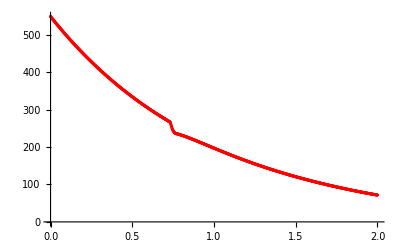

```mathematica
plotEntalpiaMPF7=ListPlot[tablicaEntalpiaMPF7,PlotStyle->Red]
```

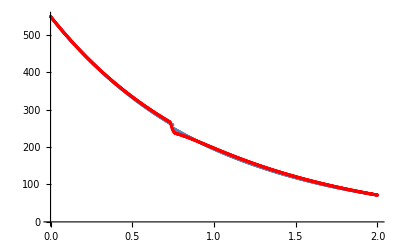

```mathematica
Show[plotEntalpiaDokladna7,plotEntalpiaMPF7]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv

### alfa = 8/10, t=2

#### temperatury

```mathematica
str8=OpenRead["temperatury1.csv"]
```

InputStream[…]

```mathematica
strList8=ReadList[str8]
```

{2.71782,2.71227,2.70673,2.70121,2.6957,2.6902,2.68471,2.67923,2.67377,2.66831,2.66287,2.65744,2.65202,2.64662,2.64122,2.63583,2.63046,2.6251,2.61975,2.61441,2.60908,2.60376,2.59846,2.59316,2.58788,2.58261,2.57735,2.5721,2.56686,2.56163,2.55642,2.55121,2.54602,2.54084,2.53566,2.5305,2.52535,2.52021,2.51508,2.50997,2.50486,2.49976,2.49468,2.4896,2.48454,2.47949,2.47444,2.46941,2.46439,2.45938,2.45438,2.44939,2.44441,2.43944,2.43449,2.42954,2.4246,2.41968,2.41476,2.40985,2.40496,2.40007,2.3952,2.39034,2.38548,2.38064,2.3758,2.37098,2.36617,2.36137,2.35657,2.35179,2.34702,2.34226,2.3375,2.33276,2.32803,2.32331,2.31859,2.31389,2.3092,2.30452,2.29984,2.29518,2.29053,2.28589,2.28125,2.27663,2.27202,2.26741,2.26282,2.25823,2.25366,2.24909,2.24454,2.23999,2.23545,2.23093,2.22641,2.2219,2.2174,2.21292,2.20844,2.20397,2.19951,2.19506,2.19061,2.18618,2.18176,2.17734,2.17294,2.16855,2.16416,2.15978,2.15542,2.15106,2.14671,2.14237,2.13804,2.13372,2.12941,2.1251,2.12081,2.11652,2.11225,2.10798,2.10372,2.09947,2.09523,2.091,2.08678,2.08257,2.07836,2.07417,2.06998,2.0658,2.06163,2.05747,2.05332,2.04918,2.04504,2.04092,2.0368,2.03269,2.02859,2.0245,2.02042,2.01635,2.01228,2.00822,2.00418,2.00014,1.99611,1.99208,1.98807,1.98406,1.98007,1.97608,1.9721,1.96812,1.96416,1.96021,1.95626,1.95232,1.94839,1.94447,1.94055,1.93665,1.93275,1.92886,1.92498,1.92111,1.91724,1.91338,1.90954,1.9057,1.90186,1.89804,1.89422,1.89041,1.88661,1.88282,1.87904,1.87526,1.87149,1.86773,1.86398,1.86023,1.8565,1.85277,1.84905,1.84533,1.84163,1.83793,1.83424,1.83056,1.82688,1.82321,1.81955,1.8159,1.81226,1.80862,1.80499,1.80137,1.79776,1.79415,1.79055,1.78696,1.78338,1.7798,1.77623,1.77267,1.76912,1.76557,1.76204,1.7585,1.75498,1.75146,1.74796,1.74445,1.74096,1.73747,1.73399,1.73052,1.72706,1.7236,1.72015,1.7167,1.71327,1.70984,1.70642,1.703,1.69959,1.69619,1.6928,1.68941,1.68603,1.68266,1.6793,1.67594,1.67259,1.66925,1.66591,1.66258,1.65926,1.65594,1.65263,1.64933,1.64603,1.64274,1.63946,1.63619,1.63292,1.62966,1.6264,1.62316,1.61992,1.61668,1.61346,1.61024,1.60702,1.60381,1.60061,1.59742,1.59423,1.59105,1.58788,1.58471,1.58155,1.5784,1.57525,1.57211,1.56898,1.56585,1.56273,1.55961,1.55651,1.5534,1.55031,1.54722,1.54414,1.54106,1.53799,1.53493,1.53187,1.52882,1.52578,1.52274,1.51971,1.51669,1.51367,1.51066,1.50765,1.50465,1.50166,1.49867,1.49569,1.49271,1.48975,1.48678,1.48383,1.48088,1.47793,1.475,1.47206,1.46914,1.46622,1.46331,1.4604,1.4575,1.4546,1.45171,1.44883,1.44595,1.44308,1.44022,1.43736,1.4345,1.43166,1.42881,1.42598,1.42315,1.42032,1.41751,1.41469,1.41189,1.40909,1.40629,1.4035,1.40072,1.39794,1.39517,1.39241,1.38965,1.38689,1.38414,1.3814,1.37866,1.37593,1.37321,1.37049,1.36777,1.36506,1.36236,1.35966,1.35697,1.35428,1.3516,1.34893,1.34626,1.34359,1.34094,1.33828,1.33563,1.33299,1.33036,1.32772,1.3251,1.32248,1.31986,1.31725,1.31465,1.31205,1.30946,1.30687,1.30429,1.30171,1.29914,1.29657,1.29401,1.29145,1.2889,1.28636,1.28382,1.28128,1.27875,1.27623,1.27371,1.2712,1.26869,1.26618,1.26369,1.26119,1.2587,1.25622,1.25374,1.25127,1.2488,1.24634,1.24388,1.24143,1.23898,1.23654,1.2341,1.23167,1.22925,1.22682,1.22441,1.22199,1.21959,1.21718,1.21479,1.2124,1.21001,1.20763,1.20525,1.20288,1.20051,1.19815,1.19579,1.19344,1.19109,1.18874,1.18641,1.18407,1.18174,1.17942,1.1771,1.17479,1.17248,1.17017,1.16787,1.16558,1.16328,1.161,1.15872,1.15644,1.15417,1.1519,1.14964,1.14738,1.14513,1.14288,1.14064,1.1384,1.13616,1.13393,1.13171,1.12949,1.12727,1.12506,1.12285,1.12065,1.11845,1.11626,1.11407,1.11188,1.1097,1.10753,1.10536,1.10319,1.10103,1.09887,1.09672,1.09457,1.09242,1.09028,1.08815,1.08602,1.08389,1.08177,1.07965,1.07754,1.07543,1.07332,1.07122,1.06913,1.06703,1.06495,1.06286,1.06078,1.05871,1.05664,1.05457,1.05251,1.05046,1.0484,1.04636,1.04431,1.04227,1.04024,1.03821,1.03618,1.03416,1.03214,1.03008,1.01688,1.00438,1,1,1,0.993248,0.984345,0.976622,0.96973,0.963289,0.958396,0.953496,0.950328,0.947411,0.945519,0.944578,0.943622,0.94265,0.941663,0.940662,0.939646,0.938617,0.937573,0.936517,0.935447,0.934365,0.933271,0.932164,0.931045,0.929915,0.928774,0.927622,0.926459,0.925286,0.924102,0.922909,0.921705,0.920493,0.919271,0.91804,0.9168,0.915552,0.914296,0.913031,0.911759,0.910479,0.909191,0.907897,0.906595,0.905286,0.903971,0.902649,0.901321,0.899986,0.898646,0.8973,0.895948,0.894591,0.893228,0.891861,0.890488,0.889111,0.887728,0.886342,0.884951,0.883555,0.882156,0.880752,0.879345,0.877934,0.87652,0.875102,0.87368,0.872256,0.870828,0.869397,0.867964,0.866527,0.865088,0.863647,0.862203,0.860757,0.859308,0.857858,0.856405,0.85495,0.853494,0.852036,0.850576,0.849114,0.847651,0.846187,0.844721,0.843254,0.841786,0.840317,0.838847,0.837376,0.835904,0.834431,0.832957,0.831483,0.830008,0.828533,0.827057,0.825581,0.824105,0.822628,0.821151,0.819674,0.818197,0.81672,0.815242,0.813765,0.812288,0.810812,0.809335,0.807859,0.806383,0.804907,0.803432,0.801957,0.800483,0.799009,0.797536,0.796064,0.794592,0.793121,0.791651,0.790182,0.788713,0.787245,0.785778,0.784313,0.782848,0.781384,0.779921,0.778459,0.776998,0.775539,0.774081,0.772623,0.771168,0.769713,0.76826,0.766807,0.765357,0.763907,0.762459,0.761013,0.759568,0.758124,0.756682,0.755241,0.753802,0.752365,0.750929,0.749494,0.748061,0.74663,0.745201,0.743773,0.742347,0.740922,0.7395,0.738079,0.736659,0.735242,0.733826,0.732412,0.731,0.72959,0.728182,0.726775,0.725371,0.723968,0.722567,0.721168,0.719771,0.718376,0.716983,0.715592,0.714203,0.712816,0.711431,0.710047,0.708666,0.707287,0.70591,0.704535,0.703162,0.701791,0.700422,0.699055,0.69769,0.696328,0.694967,0.693608,0.692252,0.690898,0.689546,0.688196,0.686848,0.685502,0.684159,0.682817,0.681478,0.680141,0.678806,0.677473,0.676142,0.674814,0.673488,0.672164,0.670842,0.669522,0.668204,0.666889,0.665576,0.664265,0.662957,0.66165,0.660346,0.659044,0.657744,0.656446,0.655151,0.653858,0.652567,0.651278,0.649992,0.648708,0.647426,0.646146,0.644868,0.643593,0.64232,0.641049,0.639781,0.638514,0.63725,0.635989,0.634729,0.633472,0.632216,0.630964,0.629713,0.628465,0.627218,0.625975,0.624733,0.623493,0.622256,0.621021,0.619789,0.618558,0.61733,0.616104,0.61488,0.613659,0.612439,0.611222,0.610007,0.608795,0.607584,0.606376,0.60517,0.603967,0.602765,0.601566,0.600369,0.599174,0.597982,0.596791,0.595603,0.594417,0.593233,0.592052,0.590872,0.589695,0.58852,0.587348,0.586177,0.585009,0.583843,0.582679,0.581517,0.580357,0.5792,0.578045,0.576892,0.575741,0.574592,0.573446,0.572301,0.571159,0.570019,0.568882,0.567746,0.566612,0.565481,0.564352,0.563225,0.5621,0.560977,0.559856,0.558738,0.557622,0.556507,0.555395,0.554285,0.553178,0.552072,0.550968,0.549867,0.548768,0.54767,0.546575,0.545482,0.544391,0.543302,0.542216,0.541131,0.540048,0.538968,0.53789,0.536813,0.535739,0.534667,0.533597,0.532529,0.531463,0.530399,0.529337,0.528277,0.52722,0.526164,0.52511,0.524059,0.523009,0.521962,0.520916,0.519873,0.518832,0.517792,0.516755,0.515719,0.514686,0.513655,0.512625,0.511598,0.510573,0.50955,0.508528,0.507509,0.506492,0.505476,0.504463,0.503452,0.502442,0.501435,0.500429,0.499426,0.498424,0.497425,0.496427,0.495431,0.494438,0.493446,0.492456,0.491468,0.490482,0.489498,0.488516,0.487536,0.486558,0.485581,0.484607,0.483634,0.482664,0.481695,0.480728,0.479764,0.478801,0.47784,0.47688,0.475923,0.474968,0.474014,0.473063,0.472113,0.471165,0.470219,0.469275,0.468332,0.467392,0.466453,0.465517,0.464582,0.463649,0.462718,0.461788,0.460861,0.459935,0.459011,0.458089,0.457169,0.456251,0.455334,0.454419,0.453506,0.452595,0.451686,0.450778,0.449873,0.448969,0.448067,0.447166,0.446268,0.445371,0.444476,0.443583,0.442691,0.441802,0.440914,0.440028,0.439143,0.438261,0.43738,0.436501,0.435624,0.434748,0.433874,0.433002,0.432132,0.431263,0.430396,0.429531,0.428668,0.427806,0.426946,0.426088,0.425231,0.424376,0.423523,0.422671,0.421822,0.420974,0.420127,0.419283,0.41844,0.417598,0.416759,0.415921,0.415085,0.41425,0.413417,0.412586,0.411757,0.410929,0.410103,0.409278,0.408455,0.407634,0.406814,0.405996,0.40518,0.404365,0.403552,0.402741,0.401931,0.401123,0.400317,0.399512,0.398709,0.397907,0.397107,0.396309,0.395512,0.394717,0.393923,0.393131,0.392341,0.391552,0.390765,0.389979,0.389195,0.388413,0.387632,0.386853,0.386075,0.385299,0.384525,0.383752,0.382981,0.382211,0.381443,0.380676,0.379911,0.379147,0.378385,0.377625,0.376866,0.376109,0.375353,0.374599,0.373846,0.373095,0.372345,0.371597,0.370851,0.370105,0.369362,0.36862,0.367879}

```mathematica
strList8={2.7178162163,2.7122692752,2.7067340831,2.7012106136,2.6956988416,2.6901987432,2.6847102946,2.679233472,2.6737682497,2.6683145986,2.662872495,2.657441915,2.6520228354,2.6466152325,2.6412190832,2.6358343571,2.6304610308,2.6250990806,2.6197484832,2.6144092154,2.6090812541,2.6037645764,2.5984591526,2.5931649596,2.5878819741,2.582610173,2.5773495338,2.5721000337,2.5668616436,2.5616343408,2.5564181023,2.5512129055,2.5460187279,2.5408355412,2.5356633227,2.53050205,2.5253517005,2.5202122521,2.5150836769,2.5099659525,2.5048590567,2.4997629673,2.4946776569,2.4896031035,2.4845392851,2.4794861795,2.474443765,2.4694120145,2.4643909063,2.4593804184,2.4543805292,2.4493912121,2.4444124454,2.4394442076,2.4344864771,2.4295392276,2.4246024377,2.419676086,2.4147601511,2.4098546072,2.4049594329,2.400074607,2.3952001085,2.3903359116,2.3854819952,2.3806383385,2.3758049204,2.3709817155,2.366168703,2.3613658621,2.3565731676,2.3517905989,2.3470181352,2.3422557559,2.3375034362,2.3327611554,2.3280288932,2.3233066291,2.3185943385,2.313892001,2.3091995963,2.3045171001,2.299844492,2.2951817521,2.290528856,2.2858857838,2.2812525153,2.2766290306,2.2720153057,2.2674113208,2.262817056,2.2582324876,2.2536575957,2.2490923607,2.244536759,2.239990771,2.2354543772,2.2309275541,2.2264102822,2.2219025421,2.2174043144,2.2129155759,2.2084363073,2.2039664894,2.1995060991,2.1950551173,2.1906135248,2.1861812988,2.1817584203,2.1773448702,2.172940626,2.1685456686,2.1641599792,2.1597835353,2.1554163182,2.151058309,2.1467094855,2.142369829,2.1380393208,2.1337179389,2.1294056646,2.1251024794,2.1208083615,2.1165232922,2.1122472534,2.1079802231,2.103722183,2.0994731115,2.0952329902,2.0910018011,2.0867795226,2.0825661365,2.0783616248,2.0741659662,2.0699791425,2.0658011359,2.0616319252,2.0574714925,2.0533198199,2.0491768864,2.0450426742,2.0409171657,2.0368003398,2.032692179,2.0285926658,2.0245017791,2.0204195016,2.0163458127,2.0122806946,2.0082241303,2.004176099,2.0001365835,1.9961055665,1.9920830276,1.9880689495,1.9840633153,1.9800661045,1.9760773,1.9720968818,1.9681248327,1.9641611359,1.9602057713,1.9562587219,1.952319971,1.9483894986,1.944467288,1.9405533193,1.9366475758,1.9327500409,1.9288606949,1.9249795212,1.9211065033,1.9172416216,1.9133848596,1.9095361978,1.9056956199,1.9018631095,1.8980386473,1.8942222169,1.8904138023,1.886613384,1.8828209459,1.879036469,1.875259937,1.8714913341,1.867730641,1.8639778419,1.8602329209,1.856495859,1.8527666403,1.8490452461,1.8453316605,1.8416258678,1.8379278492,1.8342375892,1.830555072,1.8268802792,1.823213195,1.819553801,1.8159020817,1.8122580216,1.8086216024,1.8049928086,1.8013716219,1.797758027,1.7941520087,1.7905535487,1.7869626318,1.783379243,1.779803364,1.7762349797,1.7726740722,1.7691206264,1.7655746274,1.7620360572,1.7585049008,1.7549811405,1.7514647614,1.7479557488,1.7444540848,1.7409597547,1.7374727409,1.7339930287,1.7305206035,1.7270554477,1.7235975468,1.7201468832,1.7167034425,1.7132672102,1.7098381689,1.7064163043,1.7030016021,1.6995940448,1.6961936183,1.6928003054,1.6894140917,1.6860349632,1.6826629027,1.6792978962,1.6759399265,1.6725889797,1.6692450417,1.6659080957,1.6625781275,1.6592551205,1.6559390607,1.6526299342,1.6493277244,1.6460324174,1.6427439965,1.639462448,1.6361877584,1.6329199108,1.6296588918,1.6264046848,1.6231572763,1.6199166527,1.6166827976,1.6134556976,1.6102353364,1.6070217004,1.6038147764,1.6006145482,1.5974210023,1.5942341227,1.591053896,1.5878803092,1.5847133461,1.5815529935,1.5783992355,1.5752520589,1.5721114508,1.5689773951,1.565849879,1.5627288865,1.5596144048,1.556506418,1.5534049132,1.5503098777,1.5472212958,1.5441391546,1.5410634386,1.537994135,1.5349312312,1.5318747116,1.5288245636,1.5257807717,1.5227433234,1.5197122061,1.5166874045,1.513668906,1.5106566954,1.5076507603,1.5046510882,1.5016576641,1.4986704754,1.4956895071,1.4927147469,1.4897461826,1.4867837991,1.4838275842,1.4808775229,1.4779336031,1.4749958098,1.4720641311,1.4691385547,1.466219066,1.4633056529,1.4603983006,1.4574969973,1.4546017309,1.4517124869,1.4488292533,1.4459520156,1.4430807619,1.4402154805,1.4373561569,1.4345027794,1.4316553333,1.4288138072,1.4259781866,1.4231484599,1.4203246155,1.4175066392,1.4146945192,1.4118882415,1.4090877946,1.406293167,1.4035043445,1.4007213158,1.3979440667,1.3951725859,1.3924068621,1.3896468814,1.3868926323,1.384144101,1.3814012762,1.3786641441,1.3759326934,1.3732069131,1.3704867893,1.367772311,1.3650634644,1.3623602385,1.3596626223,1.3569706021,1.354284167,1.3516033034,1.3489280002,1.346258244,1.343594024,1.3409353293,1.3382821464,1.3356344647,1.3329922705,1.3303555533,1.3277243025,1.3250985045,1.3224781488,1.3198632221,1.3172537138,1.3146496106,1.312050902,1.3094575776,1.3068696242,1.3042870312,1.3017097856,1.299137877,1.2965712952,1.2940100269,1.2914540619,1.2889033871,1.2863579924,1.2838178647,1.2812829938,1.2787533697,1.2762289793,1.2737098126,1.2711958567,1.2686871016,1.2661835345,1.2636851453,1.2611919241,1.2587038581,1.2562209375,1.2537431494,1.2512704841,1.2488029318,1.2463404797,1.2438831181,1.2414308345,1.238983619,1.2365414593,1.2341043455,1.231672268,1.2292452143,1.2268231749,1.2244061374,1.2219940921,1.2195870296,1.2171849376,1.2147878065,1.2123956241,1.2100083809,1.2076260647,1.2052486661,1.2028761759,1.2005085817,1.1981458744,1.1957880418,1.1934350747,1.191086961,1.1887436916,1.1864052572,1.1840716459,1.1817428486,1.1794188534,1.1770996512,1.1747852329,1.1724755868,1.1701707039,1.1678705724,1.1655751833,1.1632845249,1.1609985885,1.1587173652,1.1564408432,1.154169014,1.1519018658,1.1496393901,1.1473815752,1.1451284126,1.1428798937,1.1406360071,1.1383967442,1.1361620937,1.1339320471,1.1317065934,1.129485724,1.1272694306,1.1250577022,1.1228505304,1.1206479044,1.1184498158,1.1162562569,1.1140672166,1.1118826869,1.1097026572,1.1075271197,1.1053560638,1.1031894818,1.1010273662,1.0988697067,1.0967164957,1.0945677235,1.0924233825,1.0902834633,1.0881479587,1.0860168623,1.0838901646,1.0817678591,1.0796499372,1.0775363929,1.075427218,1.0733224073,1.0712219559,1.0691258569,1.0670341057,1.0649466972,1.0628636284,1.0607848984,1.0587105034,1.0566404438,1.0545747202,1.0525133352,1.0504562953,1.0484036095,1.0463552945,1.0443113683,1.042271855,1.0402368042,1.0382062642,1.0361803571,1.03415922,1.0321442441,1.0300755025,1.0168820344,1.0043835591,1,1,1,0.9932477738,0.9843453606,0.9766216495,0.9697299002,0.9632888561,0.9583955987,0.9534957466,0.9503280587,0.9474112756,0.945519105,0.9445782535,0.943621747,0.942649941,0.9416631839,0.9406618178,0.9396461783,0.9386165945,0.9375733896,0.9365168804,0.9354473779,0.9343651871,0.9332706073,0.9321639321,0.9310454496,0.9299154425,0.9287741879,0.927621958,0.9264590195,0.9252856343,0.9241020592,0.9229085462,0.9217053424,0.9204926904,0.9192708279,0.9180399884,0.9168004007,0.9155522894,0.9142958748,0.913031373,0.9117589958,0.9104789513,0.9091914433,0.907896672,0.9065948335,0.9052861203,0.9039707212,0.9026488214,0.9013206026,0.8999862428,0.8986459168,0.8972997959,0.8959480484,0.894590839,0.8932283294,0.8918606782,0.8904880409,0.88911057,0.8877284152,0.886341723,0.8849506375,0.8835552996,0.8821558477,0.8807524174,0.8793451419,0.8779341516,0.8765195744,0.8751015358,0.8736801587,0.8722555638,0.8708278693,0.8693971913,0.8679636433,0.8665273369,0.8650883813,0.8636468837,0.8622029493,0.8607566808,0.8593081794,0.857857544,0.8564048717,0.8549502575,0.8534937947,0.8520355749,0.8505756874,0.8491142202,0.8476512594,0.8461868894,0.8447211928,0.8432542507,0.8417861426,0.8403169463,0.8388467382,0.837375593,0.835903584,0.834430783,0.8329572605,0.8314830853,0.830008325,0.8285330459,0.8270573128,0.8255811892,0.8241047375,0.8226280187,0.8211510925,0.8196740174,0.8181968509,0.816719649,0.8152424669,0.8137653585,0.8122883764,0.8108115725,0.8093349974,0.8078587007,0.8063827309,0.8049071356,0.8034319615,0.801957254,0.8004830578,0.7990094166,0.7975363733,0.7960639698,0.794592247,0.793121245,0.7916510033,0.7901815603,0.7887129535,0.7872452199,0.7857783954,0.7843125155,0.7828476145,0.7813837263,0.7799208839,0.7784591197,0.7769984652,0.7755389514,0.7740806086,0.7726234663,0.7711675535,0.7697128985,0.768259529,0.766807472,0.765356754,0.7639074008,0.7624594377,0.7610128895,0.7595677802,0.7581241335,0.7566819724,0.7552413195,0.7538021968,0.7523646258,0.7509286274,0.7494942223,0.7480614303,0.7466302712,0.745200764,0.7437729273,0.7423467794,0.740922338,0.7394996205,0.7380786437,0.7366594242,0.735241978,0.733826321,0.7324124683,0.7310004349,0.7295902355,0.7281818841,0.7267753946,0.7253707804,0.7239680548,0.7225672305,0.72116832,0.7197713353,0.7183762883,0.7169831905,0.7155920531,0.714202887,0.7128157027,0.7114305106,0.7100473206,0.7086661424,0.7072869856,0.7059098594,0.7045347725,0.7031617338,0.7017907516,0.7004218341,0.6990549891,0.6976902244,0.6963275474,0.6949669653,0.6936084851,0.6922521136,0.6908978572,0.6895457224,0.6881957152,0.6868478416,0.6855021073,0.6841585178,0.6828170784,0.6814777943,0.6801406704,0.6788057116,0.6774729223,0.676142307,0.67481387,0.6734876153,0.6721635469,0.6708416684,0.6695219836,0.6682044958,0.6668892083,0.6655761242,0.6642652467,0.6629565784,0.6616501221,0.6603458804,0.6590438558,0.6577440504,0.6564464666,0.6551511063,0.6538579715,0.6525670639,0.6512783854,0.6499919373,0.6487077213,0.6474257385,0.6461459903,0.6448684778,0.643593202,0.6423201638,0.641049364,0.6397808034,0.6385144825,0.6372504019,0.635988562,0.6347289632,0.6334716056,0.6322164895,0.630963615,0.6297129819,0.6284645903,0.62721844,0.6259745307,0.624732862,0.6234934337,0.6222562452,0.6210212959,0.6197885853,0.6185581127,0.6173298772,0.6161038782,0.6148801146,0.6136585856,0.6124392902,0.6112222272,0.6100073956,0.6087947941,0.6075844215,0.6063762765,0.6051703578,0.6039666638,0.6027651933,0.6015659446,0.6003689163,0.5991741066,0.597981514,0.5967911366,0.5956029729,0.594417021,0.593233279,0.592051745,0.5908724172,0.5896952936,0.5885203722,0.587347651,0.5861771278,0.5850088005,0.5838426671,0.5826787253,0.5815169729,0.5803574077,0.5792000273,0.5780448294,0.5768918118,0.575740972,0.5745923076,0.5734458163,0.5723014954,0.5711593425,0.5700193552,0.5688815308,0.5677458669,0.5666123607,0.5654810097,0.5643518113,0.5632247628,0.5620998614,0.5609771046,0.5598564895,0.5587380134,0.5576216735,0.5565074672,0.5553953914,0.5542854435,0.5531776206,0.5520719198,0.5509683382,0.549866873,0.5487675212,0.5476702799,0.5465751463,0.5454821172,0.5443911899,0.5433023612,0.5422156281,0.5411309878,0.5400484371,0.5389679731,0.5378895927,0.5368132928,0.5357390704,0.5346669223,0.5335968456,0.5325288372,0.5314628938,0.5303990125,0.5293371901,0.5282774234,0.5272197094,0.5261640449,0.5251104267,0.5240588517,0.5230093167,0.5219618186,0.5209163541,0.5198729201,0.5188315135,0.5177921309,0.5167547693,0.5157194254,0.514686096,0.5136547779,0.5126254679,0.5115981628,0.5105728593,0.5095495542,0.5085282443,0.5075089264,0.5064915972,0.5054762535,0.5044628921,0.5034515097,0.5024421031,0.501434669,0.5004292042,0.4994257054,0.4984241695,0.4974245931,0.496426973,0.495431306,0.4944375889,0.4934458182,0.4924559909,0.4914681037,0.4904821533,0.4894981365,0.48851605,0.4875358907,0.4865576551,0.4855813402,0.4846069427,0.4836344592,0.4826638867,0.4816952218,0.4807284614,0.4797636021,0.4788006408,0.4778395742,0.4768803991,0.4759231124,0.4749677106,0.4740141907,0.4730625495,0.4721127837,0.4711648901,0.4702188654,0.4692747066,0.4683324104,0.4673919736,0.466453393,0.4655166655,0.4645817877,0.4636487567,0.4627175691,0.4617882218,0.4608607117,0.4599350355,0.4590111902,0.4580891725,0.4571689793,0.4562506075,0.4553340539,0.4544193153,0.4535063887,0.4525952709,0.4516859588,0.4507784493,0.4498727392,0.4489688254,0.4480667049,0.4471663745,0.4462678311,0.4453710717,0.4444760931,0.4435828923,0.4426914663,0.4418018118,0.440913926,0.4400278056,0.4391434477,0.4382608493,0.4373800072,0.4365009185,0.43562358,0.4347479889,0.433874142,0.4330020363,0.432131669,0.4312630368,0.4303961369,0.4295309663,0.428667522,0.4278058009,0.4269458002,0.4260875168,0.4252309479,0.4243760904,0.4235229414,0.422671498,0.4218217572,0.4209737161,0.4201273718,0.4192827214,0.4184397619,0.4175984905,0.4167589043,0.4159210003,0.4150847757,0.4142502276,0.4134173531,0.4125861494,0.4117566137,0.410928743,0.4101025345,0.4092779854,0.4084550929,0.407633854,0.4068142661,0.4059963263,0.4051800318,0.4043653797,0.4035523674,0.402740992,0.4019312507,0.4011231408,0.4003166594,0.399511804,0.3987085716,0.3979069595,0.397106965,0.3963085855,0.395511818,0.39471666,0.3939231087,0.3931311614,0.3923408154,0.3915520681,0.3907649167,0.3899793585,0.3891953909,0.3884130112,0.3876322168,0.386853005,0.3860753732,0.3852993187,0.3845248389,0.3837519312,0.3829805929,0.3822108215,0.3814426143,0.3806759688,0.3799108823,0.3791473522,0.3783853761,0.3776249513,0.3768660752,0.3761087453,0.3753529591,0.374598714,0.3738460075,0.3730948369,0.3723451999,0.3715970939,0.3708505164,0.3701054649,0.3693619368,0.3686199297,0.3678794412};
```

```mathematica
tablicaTemperaturMPF8=Table[{i*0.002,strList8[[i+1]]},{i,0,1000}];
```

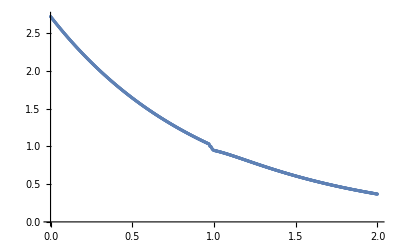

```mathematica
plotTemperaturyMPF8=ListPlot[tablicaTemperaturMPF8]
```

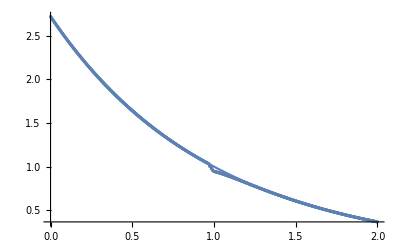

```mathematica
Show[plotTemperaturyDokladne4,plotTemperaturyMPF8]
```

```mathematica
Close["temperatury1.csv"]
```

temperatury1.csv

#### entalpie

```mathematica
cL=26;cS=25;roL=10;roS=10;lambdaL=130;lambdaS=125;um=1;aL=lambdaL/(roL*cL);aS=lambdaS/(roS*cS);L[t_]:=(Gamma[0.2]*(lambdaL-lambdaS))/(5*aL*t^(1/5));
```

```mathematica
entalpia[temp_,t_]:=Piecewise[{{cL*roL*(temp-um)+cS*roS*um+L[t],temp>um},{cS*roS*temp,temp≤um}}]
```

```mathematica
tablicaEntalpiaDokladna8=Table[{i*0.002,entalpia[u1[i*0.002,2],2]},{i,0,1000}];
```

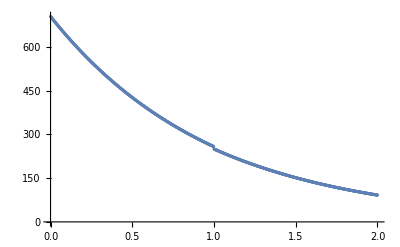

```mathematica
plotEntalpiaDokladna8=ListPlot[tablicaEntalpiaDokladna8]
```

```mathematica
strE=OpenRead["entalpie1.csv"]
```

InputStream[…]

```mathematica
strListE8=ReadList[strE]
```

{704.625,703.183,701.744,700.308,698.875,697.445,696.018,694.594,693.173,691.755,690.34,688.928,687.519,686.113,684.71,683.31,681.913,680.519,679.128,677.74,676.354,674.972,673.593,672.216,670.842,669.472,668.104,666.739,665.377,664.018,662.662,661.308,659.958,658.61,657.266,655.924,654.585,653.248,651.915,650.584,649.256,647.931,646.609,645.29,643.973,642.66,641.349,640.04,638.735,637.432,636.132,634.835,633.54,632.249,630.96,629.673,628.39,627.109,625.831,624.555,623.283,622.013,620.745,619.48,618.218,616.959,615.702,614.448,613.197,611.948,610.702,609.459,608.218,606.98,605.744,604.511,603.281,602.053,600.828,599.605,598.385,597.168,595.953,594.74,593.531,592.323,591.119,589.917,588.717,587.52,586.326,585.134,583.944,582.757,581.573,580.391,579.211,578.034,576.86,575.688,574.518,573.351,572.187,571.024,569.865,568.707,567.553,566.4,565.25,564.103,562.958,561.815,560.675,559.537,558.401,557.268,556.138,555.009,553.883,552.76,551.639,550.52,549.403,548.289,547.177,546.068,544.961,543.856,542.754,541.654,540.556,539.46,538.367,537.276,536.188,535.101,534.017,532.936,531.856,530.779,529.704,528.632,527.561,526.493,525.427,524.364,523.302,522.243,521.186,520.131,519.079,518.029,516.981,515.935,514.891,513.85,512.81,511.773,510.738,509.706,508.675,507.647,506.62,505.596,504.574,503.555,502.537,501.521,500.508,499.497,498.488,497.481,496.476,495.473,494.473,493.474,492.478,491.483,490.491,489.501,488.513,487.527,486.543,485.561,484.581,483.603,482.627,481.654,480.682,479.712,478.745,477.779,476.816,475.854,474.895,473.937,472.982,472.029,471.077,470.128,469.18,468.235,467.291,466.35,465.41,464.473,463.537,462.603,461.672,460.742,459.814,458.888,457.964,457.043,456.122,455.204,454.288,453.374,452.462,451.551,450.643,449.736,448.831,447.928,447.028,446.128,445.231,444.336,443.443,442.551,441.661,440.774,439.888,439.003,438.121,437.241,436.362,435.485,434.611,433.738,432.866,431.997,431.129,430.263,429.399,428.537,427.677,426.818,425.962,425.107,424.253,423.402,422.552,421.704,420.858,420.014,419.171,418.331,417.492,416.654,415.819,414.985,414.153,413.323,412.494,411.667,410.842,410.019,409.197,408.377,407.559,406.742,405.927,405.114,404.303,403.493,402.685,401.878,401.074,400.271,399.469,398.67,397.872,397.075,396.281,395.488,394.696,393.906,393.118,392.332,391.547,390.764,389.982,389.202,388.424,387.647,386.872,386.099,385.327,384.557,383.788,383.021,382.256,381.492,380.73,379.969,379.21,378.453,377.697,376.942,376.19,375.438,374.689,373.941,373.194,372.449,371.706,370.964,370.224,369.485,368.747,368.012,367.278,366.545,365.814,365.084,364.356,363.629,362.904,362.181,361.459,360.738,360.019,359.301,358.585,357.871,357.157,356.446,355.736,355.027,354.32,353.614,352.91,352.207,351.505,350.805,350.107,349.41,348.714,348.02,347.328,346.636,345.946,345.258,344.571,343.886,343.201,342.519,341.837,341.158,340.479,339.802,339.126,338.452,337.779,337.108,336.438,335.769,335.102,334.436,333.771,333.108,332.446,331.786,331.127,330.469,329.813,329.158,328.504,327.852,327.201,326.551,325.903,325.256,324.611,323.966,323.323,322.682,322.042,321.403,320.765,320.129,319.494,318.86,318.228,317.597,316.967,316.339,315.712,315.086,314.461,313.838,313.216,312.595,311.976,311.358,310.741,310.125,309.511,308.898,308.286,307.676,307.066,306.458,305.852,305.246,304.642,304.039,303.437,302.837,302.238,301.639,301.043,300.447,299.853,299.26,298.668,298.077,297.488,296.899,296.312,295.727,295.142,294.558,293.976,293.395,292.815,292.237,291.659,291.083,290.508,289.934,289.362,288.79,288.22,287.651,287.083,286.516,285.95,285.386,284.822,284.26,283.699,283.139,282.581,282.023,281.467,280.912,280.358,279.805,279.253,278.702,278.153,277.604,277.057,276.511,275.966,275.422,274.879,274.338,273.797,273.258,272.72,272.183,271.647,271.112,270.578,270.045,269.514,268.984,268.455,267.927,267.4,266.875,266.351,265.813,262.382,259.133,256.039,253.303,250.571,248.312,246.086,244.155,242.432,240.822,239.599,238.374,237.582,236.853,236.38,236.145,235.905,235.662,235.416,235.165,234.912,234.654,234.393,234.129,233.862,233.591,233.318,233.041,232.761,232.479,232.194,231.905,231.615,231.321,231.026,230.727,230.426,230.123,229.818,229.51,229.2,228.888,228.574,228.258,227.94,227.62,227.298,226.974,226.649,226.322,225.993,225.662,225.33,224.997,224.661,224.325,223.987,223.648,223.307,222.965,222.622,222.278,221.932,221.585,221.238,220.889,220.539,220.188,219.836,219.484,219.13,218.775,218.42,218.064,217.707,217.349,216.991,216.632,216.272,215.912,215.551,215.189,214.827,214.464,214.101,213.738,213.373,213.009,212.644,212.279,211.913,211.547,211.18,210.814,210.447,210.079,209.712,209.344,208.976,208.608,208.239,207.871,207.502,207.133,206.764,206.395,206.026,205.657,205.288,204.919,204.549,204.18,203.811,203.441,203.072,202.703,202.334,201.965,201.596,201.227,200.858,200.489,200.121,199.752,199.384,199.016,198.648,198.28,197.913,197.545,197.178,196.811,196.445,196.078,195.712,195.346,194.98,194.615,194.25,193.885,193.52,193.156,192.792,192.428,192.065,191.702,191.339,190.977,190.615,190.253,189.892,189.531,189.17,188.81,188.451,188.091,187.732,187.374,187.015,186.658,186.3,185.943,185.587,185.231,184.875,184.52,184.165,183.81,183.457,183.103,182.75,182.398,182.045,181.694,181.343,180.992,180.642,180.292,179.943,179.594,179.246,178.898,178.551,178.204,177.858,177.512,177.167,176.822,176.477,176.134,175.79,175.448,175.105,174.764,174.423,174.082,173.742,173.402,173.063,172.724,172.386,172.049,171.712,171.376,171.04,170.704,170.369,170.035,169.701,169.368,169.036,168.703,168.372,168.041,167.71,167.38,167.051,166.722,166.394,166.066,165.739,165.413,165.086,164.761,164.436,164.112,163.788,163.464,163.142,162.82,162.498,162.177,161.856,161.536,161.217,160.898,160.58,160.262,159.945,159.629,159.313,158.997,158.682,158.368,158.054,157.741,157.428,157.116,156.805,156.494,156.183,155.873,155.564,155.255,154.947,154.64,154.332,154.026,153.72,153.415,153.11,152.806,152.502,152.199,151.896,151.594,151.293,150.992,150.691,150.391,150.092,149.794,149.495,149.198,148.901,148.604,148.308,148.013,147.718,147.424,147.13,146.837,146.544,146.252,145.961,145.67,145.379,145.089,144.8,144.511,144.223,143.935,143.648,143.361,143.075,142.79,142.505,142.22,141.936,141.653,141.37,141.088,140.806,140.525,140.244,139.964,139.685,139.405,139.127,138.849,138.571,138.294,138.018,137.742,137.467,137.192,136.918,136.644,136.371,136.098,135.826,135.554,135.283,135.012,134.742,134.472,134.203,133.935,133.667,133.399,133.132,132.866,132.6,132.334,132.069,131.805,131.541,131.278,131.015,130.752,130.49,130.229,129.968,129.708,129.448,129.189,128.93,128.672,128.414,128.156,127.9,127.643,127.387,127.132,126.877,126.623,126.369,126.116,125.863,125.611,125.359,125.107,124.856,124.606,124.356,124.107,123.858,123.609,123.361,123.114,122.867,122.621,122.375,122.129,121.884,121.639,121.395,121.152,120.909,120.666,120.424,120.182,119.941,119.7,119.46,119.22,118.981,118.742,118.504,118.266,118.028,117.791,117.555,117.319,117.083,116.848,116.613,116.379,116.145,115.912,115.679,115.447,115.215,114.984,114.753,114.522,114.292,114.063,113.834,113.605,113.377,113.149,112.921,112.695,112.468,112.242,112.017,111.792,111.567,111.343,111.119,110.896,110.673,110.45,110.228,110.007,109.786,109.565,109.345,109.125,108.906,108.687,108.469,108.251,108.033,107.816,107.599,107.383,107.167,106.951,106.736,106.522,106.308,106.094,105.881,105.668,105.455,105.243,105.032,104.821,104.61,104.4,104.19,103.98,103.771,103.563,103.354,103.147,102.939,102.732,102.526,102.319,102.114,101.908,101.704,101.499,101.295,101.091,100.888,100.685,100.483,100.281,100.079,99.878,99.6771,99.4767,99.2767,99.0771,98.878,98.6792,98.4808,98.2828,98.0852,97.888,97.6912,97.4948,97.2988,97.1033,96.9081,96.7133,96.5188,96.3248,96.1312,95.938,95.7451,95.5527,95.3607,95.169,94.9777,94.7868,94.5963,94.4062,94.2165,94.0272,93.8382,93.6497,93.4615,93.2737,93.0863,92.8993,92.7126,92.5264,92.3405,92.155,91.9699}

```mathematica
strListE7={704.6253394027,703.1831347025,701.7439847592,700.3078826974,698.8748219793,697.4447963967,696.0177997542,694.5938258696,693.1728680725,691.7549188068,690.3399718531,688.92802107,687.5190603554,686.1130836201,684.7100847874,683.3100560122,681.9129911644,680.5188841275,679.1277287974,677.7395191595,676.354249228,674.9719130299,673.5925028451,672.2160126448,670.8424364128,669.4717681457,668.1040019427,666.7391319184,665.3771505069,664.0180517649,662.6618297618,661.3084785811,659.9579924098,658.6103638612,657.265587063,655.9236561555,654.5845652914,653.2483087045,651.9148791437,650.5842708059,649.2564779001,647.931494648,646.6093139578,645.2899300816,643.9733372839,642.6595298416,641.3485020614,640.0402469375,638.7347587887,637.4320319462,636.132060753,634.8348383031,633.540358969,632.2486171348,630.9596071972,629.6733223298,628.3897569574,627.108905517,625.8307624578,624.5553210303,623.2825757115,622.0125209903,620.7451513675,619.4804601685,618.2184419216,616.9590911668,615.7024024562,614.4483691875,613.1969859397,611.9482473037,610.7021467472,609.4586788729,608.2178383101,606.9796196995,605.7440165629,604.5110235674,603.2806353918,602.0528467265,600.82765116,599.6050434085,598.3850181999,597.1675691747,595.9526910853,594.740378697,593.5306257262,592.323426936,591.1187771282,589.9166711163,588.7171026513,587.5200665717,586.3255577273,585.1335699277,583.9440980366,582.7571369401,581.5726805108,580.3907236317,579.2112612245,578.0342872217,576.8597965277,575.6877841001,574.5182449074,573.3511728976,572.1865630638,571.0244104096,569.8647089305,568.7074536509,567.5526396097,566.4002608523,565.2503124309,564.1027894192,562.9576859099,561.8149969845,560.674717751,559.5368423473,558.4013658857,557.2682835084,556.1375893962,555.0092786936,553.883346577,552.7597872675,551.6385959435,550.5197678152,549.4032971419,548.2891791371,547.1774090448,546.0679811604,544.9608907338,543.856132142,542.7537006154,541.6535914409,540.5557990285,539.4603186416,538.3671456054,537.2762743612,536.1877002053,535.1014185019,534.0174237223,532.9357112014,531.8562763373,530.7791136297,529.7042184544,528.6315862419,527.5612115187,526.4930897025,525.4272162558,524.3635857307,523.3021935874,522.2430344497,521.1861037644,520.1313970352,519.0789089089,518.0286348641,516.9805704481,515.9347103298,514.8910500319,513.8495851335,512.8103103242,511.7732211718,510.7383124334,509.7055796714,508.6750184991,507.6466236925,506.6203908449,505.5963156155,504.5743927983,503.5546180305,502.5369861708,501.5214928638,500.5081337941,499.4969038362,498.4877986651,497.4808140127,496.4759447687,495.4731866441,494.4725345911,493.4739843353,492.4775316363,491.4831714595,490.4908995605,489.5007117475,488.5126029989,487.5265691032,486.5426050993,485.5607067919,484.5808700194,483.6030898316,482.6273620626,481.6536826008,480.6820465063,479.7124496487,478.7448871465,477.7793548829,476.8158487779,475.8543639591,474.8948963385,473.9374418869,472.9819957404,472.0285538522,471.077111415,470.1276643887,469.1802087777,468.234739782,467.2912533897,466.3497448559,465.4102101879,464.4726454252,463.537045829,462.6034074345,461.6717263333,460.741997792,459.8142178861,458.8883819363,457.9644860244,457.0425262783,456.1224980227,455.2043973701,454.2882196984,453.3739611357,452.461617847,451.5511852135,450.6426593904,449.7360358058,448.8313106334,447.9284800762,447.02753957,446.1284853153,445.2313127866,444.336018203,443.4425978061,442.5510470843,441.661362283,440.7735396975,439.8875748166,439.0034639215,438.1212025514,437.240786996,436.3622135905,435.4854778736,434.6105761664,433.7375040575,432.8662578804,431.9968340106,431.1292280353,430.2634363161,429.399454489,428.5372789312,427.676906059,426.8183315065,425.9615516766,425.1065622511,424.2533596502,423.4019403315,422.5522999744,421.7044350245,420.8583412071,420.014014985,419.1714528573,418.3306505474,417.4916045432,416.654310613,415.8187652615,414.9849650303,414.152905685,413.3225837554,412.4939950522,411.6671361219,410.8420035484,410.0185931387,409.1969014642,408.3769243773,407.5586584654,406.7421003557,405.9272458947,405.114091697,404.3026336545,403.4928683951,402.6847918299,401.8784006035,401.0736913739,400.2706600708,399.4693033625,398.6696172011,397.871598271,397.0752432741,396.2805481769,395.4875096876,394.6961237985,393.9063872338,393.1182967393,392.3318483172,391.5470387151,390.7638639652,389.9823208308,389.202406102,388.4241158155,387.6474467579,386.8723950009,386.0989573463,385.3271306289,384.5569109187,383.7882950411,383.0212791064,382.255859955,381.4920337128,380.7297972356,379.9691473915,379.2100803248,378.4525929139,377.6966813231,376.942342446,376.1895731955,375.4383697469,374.6887290162,373.9406472056,373.194121246,372.4491480956,371.7057239593,370.9638457906,370.223509829,369.4847130424,368.747451685,368.0117227399,367.2775231995,366.5448493381,365.8136981602,365.084065957,364.3559497478,363.6293465704,362.9042527268,362.180665258,361.4585804915,360.7379954825,360.0189073144,359.3013123159,358.585207564,357.8705894222,357.1574549814,356.4458006195,355.7356234418,355.0269205668,354.3196883879,353.6139240315,352.9096239108,352.2067851663,351.505404962,350.8054797161,350.1070065902,349.4099820326,348.7144032183,348.02026661,347.3275693967,346.636308778,345.9464812338,345.2580839739,344.5711134952,343.8855670212,343.2014417972,342.5187343261,341.8374418521,341.1575609063,340.4790887457,339.8020219156,339.1263576869,338.4520933406,337.7792254389,337.1077512728,336.4376674212,335.7689711884,335.1016599018,334.4357301445,333.7711792419,333.1080038056,332.4462011729,331.78576797,331.1267015479,330.4689992697,329.8126577758,329.1576744371,328.5040459125,327.8517695856,327.2008421292,326.5512609403,325.903023424,325.2561262711,324.6105668975,323.9663420092,323.3234490356,322.6818854232,322.0416478871,321.4027338773,320.7651401314,320.1288641113,319.4939025688,318.8602529793,318.2279128276,317.596878882,316.9671486367,316.3387188767,315.7115871097,315.0857508667,314.4612069359,313.8379528468,313.215985415,312.5953021805,311.9758999751,311.3577763524,310.7409288823,310.125354407,309.5110505008,308.8980140284,308.2862425761,307.6757330235,307.0664829714,306.4584900326,305.8517511018,305.246263799,304.6420250397,304.0390324587,303.4372837184,302.8367757353,302.2375061702,301.6394719705,301.042670806,300.4470996451,299.8527561736,299.2596381011,298.6677424035,298.0770667921,297.4876082735,296.8993645721,296.312332715,295.7265104452,295.1418955273,294.5584850027,293.9762766386,293.3952675123,292.8154554117,292.236837434,291.6594113901,291.0831751133,290.5081257239,289.9342610622,289.3615782913,288.7900752796,288.2197499473,287.6505994638,287.0826217514,286.5158140422,285.9501742776,285.3856997434,284.8223884245,284.2602383721,283.6992468976,283.1394120536,282.5807312568,282.0232026109,281.4668236079,280.9115924313,280.3575073609,279.804565966,279.2527665337,278.70210684,278.1525853063,277.6041998439,277.0569490559,276.5108316971,275.9658459425,275.4219906482,274.8792644426,274.3376665512,273.7971967301,273.2578540349,272.7196385447,272.1825504036,271.6465903026,271.1117599496,270.5780616271,270.0454997269,269.5140789115,268.9838054654,268.454692262,267.9267518486,267.4000159947,266.8745203645,266.3506266335,265.8127537974,262.3824521065,259.1328485281,256.0390196057,253.3025296673,250.5705933112,248.3119434432,246.0863401525,244.1554123817,242.4324750515,240.8222140138,239.5988996778,238.3739366461,237.5820146678,236.8528188963,236.3797762618,236.1445633688,235.9054367541,235.6624852385,235.4157959687,235.165454448,234.9115445674,234.6541486349,234.3933474047,234.1292201066,233.8618444734,233.591296769,233.3176518159,233.0409830211,232.761362403,232.4788606167,232.1935469794,231.9054894951,231.6147548788,231.3214085808,231.0255148095,230.7271365547,230.4263356104,230.1231725965,229.8177069806,229.5099970998,229.200100181,228.8880723619,228.5739687109,228.2578432474,227.9397489604,227.6197378283,227.2978608374,226.9741680002,226.6487083734,226.3215300759,225.992680306,225.6622053581,225.3301506403,224.99656069,224.6614791903,224.3249489863,223.9870120998,223.6477097453,223.3070823445,222.9651695413,222.622010216,222.2776424997,221.9321037879,221.5854307543,221.2376593644,220.8888248882,220.5389619134,220.1881043582,219.8362854832,219.4835379041,219.1298936036,218.7753839428,218.4200396733,218.0638909479,217.7069673322,217.3492978154,216.9909108208,216.6318342165,216.2720953256,215.9117209366,215.550737313,215.189170203,214.8270448497,214.4643859996,214.1012179126,213.7375643706,213.3734486866,213.0088937132,212.6439218515,212.2785550591,211.9128148588,211.5467223463,211.1802981982,210.8135626802,210.4465356543,210.0792365863,209.7116845536,209.343898252,208.9758960033,208.6076957615,208.2393151206,207.8707713204,207.5020812537,207.1332614728,206.7643281953,206.3952973109,206.0261843873,205.6570046761,205.2877731189,204.918504353,204.5492127171,204.1799122569,203.8106167303,203.4413396133,203.0720941048,202.7028931319,202.3337493553,201.9646751737,201.5956827293,201.226783912,200.8579903647,200.4893134876,200.1207644426,199.7523541583,199.3840933337,199.015992443,198.6480617397,198.2803112605,197.9127508296,197.5453900627,197.1782383709,196.8113049642,196.4445988558,196.0781288656,195.7119036234,195.3459315733,194.9802209765,194.6147799149,194.2496162948,193.8847378497,193.5201521439,193.1558665756,192.7918883801,192.4282246325,192.0648822513,191.7018680008,191.3391884945,190.9768501976,190.6148594297,190.2532223681,189.8919450499,189.5310333748,189.1704931081,188.8103298827,188.4505492018,188.0911564414,187.7321568528,187.3735555648,187.0153575859,186.6575678069,186.300191003,185.943231836,185.5866948562,185.230584505,184.8749051166,184.5196609201,184.1648560417,183.8104945063,183.4565802398,183.1031170708,182.7501087323,182.397558864,182.0454710135,181.6938486385,181.3426951083,180.9920137055,180.6418076278,180.2920799895,179.9428338231,179.5940720808,179.2457976364,178.8980132861,178.5507217509,178.2039256772,177.8576276389,177.5118301382,177.1665356076,176.8217464107,176.4774648437,176.133693137,175.7904334561,175.4476879029,175.105458517,174.7637472771,174.4225561018,174.0818868512,173.7417413274,173.4021212765,173.0630283887,172.7244643004,172.3864305944,172.0489288015,171.7119604011,171.3755268226,171.039629446,170.7042696033,170.369448579,170.0351676114,169.701427893,169.3682305722,169.0355767534,168.7034674981,168.3719038261,168.0408867159,167.7104171057,167.3804958939,167.0511239406,166.7223020675,166.3940310593,166.0663116641,165.7391445942,165.4125305271,165.0864701056,164.7609639391,164.4360126038,164.1116166437,163.7877765711,163.4644928672,163.141765983,162.8195963393,162.4979843281,162.1769303126,161.856434628,161.536497582,161.2171194554,160.8983005028,160.5800409529,160.2623410089,159.9452008496,159.6286206294,159.3126004788,158.9971405052,158.6822407932,158.367901405,158.0541223811,157.7409037405,157.4282454811,157.1161475807,156.8046099966,156.4936326666,156.1832155094,155.8733584246,155.5640612935,155.2553239793,154.9471463277,154.6395281667,154.332469308,154.0259695461,153.7200286596,153.4146464114,153.1098225486,152.8055568032,152.5018488925,152.1986985192,151.8961053715,151.5940691243,151.2925894384,150.9916659615,150.6912983283,150.3914861609,150.0922290687,149.7935266493,149.4953784882,149.1977841594,148.9007432255,148.604255238,148.3083197376,148.0129362546,147.7181043086,147.4238234094,147.1300930568,146.8369127411,146.5442819429,146.252200134,145.960666777,145.6696813258,145.3792432257,145.0893519137,144.8000068187,144.5112073616,144.2229529556,143.9352430063,143.6480769119,143.3614540636,143.0753738453,142.7898356344,142.5048388013,142.2203827101,141.9364667186,141.6530901783,141.370252435,141.0879528282,140.8061906921,140.5249653552,140.2442761406,139.9641223663,139.6845033449,139.4054183844,139.1268667878,138.8488478533,138.5713608747,138.2944051414,138.0179799385,137.7420845467,137.4667182429,137.1918802999,136.9175699869,136.6437865692,136.3705293085,136.0977974632,135.8255902882,135.5539070353,135.2827469528,135.0121092864,134.7419932785,134.4723981688,134.2033231942,133.934767589,133.6667305849,133.3992114111,133.1322092944,132.8657234594,132.5997531284,132.3342975216,132.0693558572,131.8049273513,131.5410112184,131.2776066708,131.0147129195,130.7523291734,130.4904546403,130.2290885261,129.9682300354,129.7078783716,129.4480327365,129.1886923309,128.9298563544,128.6715240054,128.4136944813,128.1563669786,127.8995406929,127.6432148188,127.3873885501,127.1320610801,126.8772316012,126.6228993052,126.3690633834,126.1157230265,125.8628774248,125.610525768,125.3586672457,125.1073010469,124.8564263607,124.6060423755,124.3561482799,124.1067432621,123.8578265104,123.6093972129,123.3614545579,123.1139977334,122.8670259278,122.6205383294,122.3745341268,122.1290125087,121.8839726639,121.6394137817,121.3953350517,121.1517356636,120.9086148076,120.6659716743,120.4238054549,120.1821153407,119.9409005237,119.7001601966,119.4598935523,119.2200997846,118.9807780878,118.7419276567,118.503547687,118.265637375,118.0281959178,117.7912225131,117.5547163595,117.3186766564,117.083102604,116.8479934032,116.6133482562,116.3791663657,116.1454469353,115.91218917,115.6793922752,115.4470554576,115.2151779249,114.9837588858,114.7527975499,114.5222931281,114.2922448321,114.0626518751,113.833513471,113.604828835,113.3765971836,113.1488177343,112.9214897059,112.6946123182,112.4681847924,112.2422063508,112.0166762173,111.7915936165,111.5669577747,111.3427679194,111.1190232794,110.8957230846,110.6728665666,110.4504529581,110.2284814931,110.0069514073,109.7858619374,109.5652123217,109.3450017998,109.1252296129,108.9058950033,108.6869972151,108.4685354935,108.2505090854,108.032917239,107.8157592041,107.5990342319,107.3827415752,107.166880488,106.9514502262,106.736450047,106.5218792091,106.3077369728,106.0940225998,105.8807353536,105.6678744991,105.4554393026,105.2434290323,105.0318429577,104.8206803499,104.6099404817,104.3996226275,104.1897260632,103.9802500662,103.7711939158,103.5625568925,103.3543382788,103.1465373587,102.9391534176,102.7321857429,102.5256336233,102.3194963492,102.1137732129,101.908463508,101.7035665299,101.4990815756,101.2950079439,101.0913449351,100.8880918511,100.6852479956,100.4828126739,100.2807851929,100.0791648614,99.8779509896,99.6771428895,99.4767398748,99.2767412607,99.0771463643,98.8779545042,98.6791650008,98.4807771761,98.2827903537,98.0852038592,97.8880170196,97.6912291635,97.4948396215,97.2988477257,97.1032528098,96.9080542094,96.7132512615,96.5188433052,96.3248296808,96.1312097306,95.9379827986,95.7451482302,95.5527053728,95.3606535753,95.1689921883,94.9777205641,94.7868380567,94.5963440219,94.4062378168,94.2165188006,94.0271863338,93.8382397789,93.6496784999,93.4615018625,93.2737092341,93.0862999836,92.8992734818,92.712629101,92.5263662152,92.3404842001,92.154982433,91.9698602929};
```

```mathematica
tablicaEntalpiaMPF8=Table[{i*0.002,strListE8[[i+1]]},{i,0,1000}];
```

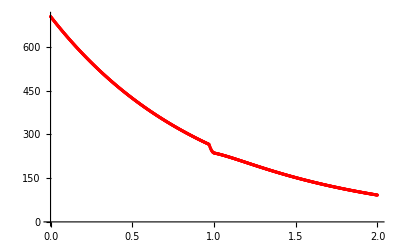

```mathematica
plotEntalpiaMPF8=ListPlot[tablicaEntalpiaMPF8,PlotStyle->Red]
```

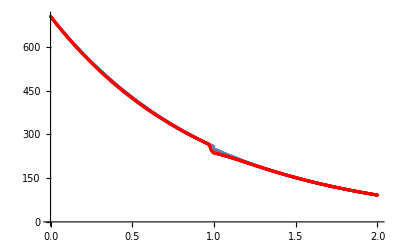

```mathematica
Show[plotEntalpiaDokladna8,plotEntalpiaMPF8]
```

```mathematica
Close["entalpie1.csv"]
```

entalpie1.csv